```mathematica
s[n_]:=Piecewise[{{{}, n==0}, {Union[s[n-1],{s[n-1]}], True}}]
```

```mathematica
s[0]
```

{}

```mathematica
s[1]
```

{{}}

```mathematica
s[2]
```

{{},{{}}}

```mathematica
s[3]
```

{{},{{}},{{},{{}}}}

```mathematica
s[4]
```

{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}}

```mathematica
s[5]
```

{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}}}

```mathematica
ad[x,x]==x+1
ad[ad[x,x],ad[x,x]]==x+2
x+{x}=={x}
(x+{x})+{x+{x}}
```

```mathematica
Map[Length,%]
```

{0,1,2,3,4}

```mathematica
un[a_,b_]:=Union[a,b]
in[a_,b_]:=Intersection[a,b]
df[a_,b_]:=Complement[a,b]
ad[a_,b_]:=Union[a,{b}]
rm[a_,b_]:=Complement[a,{b}]
l[x_]:=If[x==s[Length[x]],Length[x],-1]
```

```mathematica
un[s[0],x]==un[x,s[0]]==x
ad[s[j],s[i]]:i<j==s[j]
 ad[s[i],s[i]]==s[i+1]
rm[s[i],s[i]]==s[i]
rm[s[i],s[i-1]]==s[i-1]
```

```mathematica
l[ad[s[1],s[1]]]
```

2

```mathematica
s[1]
```

{{}}

```mathematica
l[{{{}}}]
```

-1

```mathematica
in[s[2],s[3]]
```

{{},{{}}}

```mathematica
rm[rm[rm[s[3],s[0]],s[1]],s[2]]
```

{}

```mathematica
ans={}
cnt={}
min=min[x,y]
loop1
if cnt==min, then (break), else
	ans+=2
	cnt+=1
	goto:loop1
loop2
if cnt==max,then(break),else
	ans+=1
	cnt+=1
	goto loop2
print ans
```

```mathematica
un[i,j]==Max[i,j]
in[i,j]==Min[i,j]
```

```mathematica
df[i,j]==Piecewise[{{0, j==0}, {-1, i>j}, {0, True}}]
```

```mathematica
ad[i,j]==Piecewise[{{i+1, i==j}, {-1, i<j}, {i, i>j}}]
```

```mathematica
rm[i,j]==Piecewise[{{j, i==j+1}, {-1, i>j+1}, {i, True}}]
un[ad[i,j],j]==Piecewise[{{i+1, i==j}, {j+1, i<j}, {i, i>j}}]
ad[rm[i,j],j]==Piecewise[{{i+1, i==j}, {-1, i<j}, {i, i>j}}]
```

```mathematica
2+3==5
```

```mathematica
s[2]
s[3]
s[5]
```

{{},{{}}}

{{},{{}},{{},{{}}}}

{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}}}

```mathematica
df[s[5],s[3]]
```

{{{},{{}},{{},{{}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}}}

```mathematica
{l[%],Map[Length,%]}
```

{-1,{3,4}}

```mathematica
Select[Flatten[Table[{i,j,l[df[s[i],s[j]]],Map[Length,df[s[i],s[j]]]},{i,0,6},{j,0,6}],1],#[[3]]==-1&]//Column
```

{2,1,-1,{1}}
{3,1,-1,{1,2}}
{3,2,-1,{2}}
{4,1,-1,{1,2,3}}
{4,2,-1,{2,3}}
{4,3,-1,{3}}
{5,1,-1,{1,2,3,4}}
{5,2,-1,{2,3,4}}
{5,3,-1,{3,4}}
{5,4,-1,{4}}
{6,1,-1,{1,2,3,4,5}}
{6,2,-1,{2,3,4,5}}
{6,3,-1,{3,4,5}}
{6,4,-1,{4,5}}
{6,5,-1,{5}}

```mathematica
ad[df[s[6],s[3]],s[0]]
{l[%],Map[Length,%]}
```

{{},{{},{{}},{{},{{}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}}}}

{-1,{0,3,4,5}}

```mathematica
ad[ad[df[s[5],s[2]],s[0]],s[1]]
{l[%],Map[Length,%]}
```

{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}},{{},{{}},{{},{{}}},{{},{{}},{{},{{}}}}}}

{5,{0,1,2,3,4}}

```mathematica
un[a_,b_]:=Union[a,b]
in[a_,b_]:=Intersection[a,b]
df[a_,b_]:=Complement[a,b]
ad[a_,b_]:=Union[a,{b}]
rm[a_,b_]:=Complement[a,{b}]
```

```mathematica
a+b+c
a*b*c
a+(b*c)
(a+b)*c
```

```mathematica
mm=5;
a[f_,g_]:=Flatten[Table[{i,j,k,l[g[f[s[i],s[j]],s[k]]](*,g[f[s[i],s[j]],s[k]]*)},{i,0,mm},{j,0,mm},{k,0,mm}],2]
b[f_,g_]:=Flatten[Table[{i,j,k,l[g[s[i],f[s[j],s[k]]]](*,g[s[i],f[s[j],s[k]]]*)},{i,0,mm},{j,0,mm},{k,0,mm}],2]
```

```mathematica
a[un,un]==Max
a[in,in]==Min
a[df,df][i,0,0]==i
```

```mathematica
Select[a[in,ad],#[[4]]≠-1&]//Column
```

{0,0,0,1}
{0,1,0,1}
{0,2,0,1}
{0,3,0,1}
{0,4,0,1}
{0,5,0,1}
{1,0,0,1}
{1,1,0,1}
{1,1,1,2}
{1,2,0,1}
{1,2,1,2}
{1,3,0,1}
{1,3,1,2}
{1,4,0,1}
{1,4,1,2}
{1,5,0,1}
{1,5,1,2}
{2,0,0,1}
{2,1,0,1}
{2,1,1,2}
{2,2,0,2}
{2,2,1,2}
{2,2,2,3}
{2,3,0,2}
{2,3,1,2}
{2,3,2,3}
{2,4,0,2}
{2,4,1,2}
{2,4,2,3}
{2,5,0,2}
{2,5,1,2}
{2,5,2,3}
{3,0,0,1}
{3,1,0,1}
{3,1,1,2}
{3,2,0,2}
{3,2,1,2}
{3,2,2,3}
{3,3,0,3}
{3,3,1,3}
{3,3,2,3}
{3,3,3,4}
{3,4,0,3}
{3,4,1,3}
{3,4,2,3}
{3,4,3,4}
{3,5,0,3}
{3,5,1,3}
{3,5,2,3}
{3,5,3,4}
{4,0,0,1}
{4,1,0,1}
{4,1,1,2}
{4,2,0,2}
{4,2,1,2}
{4,2,2,3}
{4,3,0,3}
{4,3,1,3}
{4,3,2,3}
{4,3,3,4}
{4,4,0,4}
{4,4,1,4}
{4,4,2,4}
{4,4,3,4}
{4,4,4,5}
{4,5,0,4}
{4,5,1,4}
{4,5,2,4}
{4,5,3,4}
{4,5,4,5}
{5,0,0,1}
{5,1,0,1}
{5,1,1,2}
{5,2,0,2}
{5,2,1,2}
{5,2,2,3}
{5,3,0,3}
{5,3,1,3}
{5,3,2,3}
{5,3,3,4}
{5,4,0,4}
{5,4,1,4}
{5,4,2,4}
{5,4,3,4}
{5,4,4,5}
{5,5,0,5}
{5,5,1,5}
{5,5,2,5}
{5,5,3,5}
{5,5,4,5}
{5,5,5,6}

```mathematica
111
0567
0444
1013
```

```mathematica
0567+0444
```

1011

```mathematica
Flatten[Table[{i,j,l[un[ad[s[i],s[j]],s[j]]]},{i,0,10},{j,0,10}],1]//Column
```

{0,0,1}
{0,1,2}
{0,2,3}
{0,3,4}
{0,4,5}
{0,5,6}
{0,6,7}
{0,7,8}
{0,8,9}
{0,9,10}
{0,10,11}
{1,0,1}
{1,1,2}
{1,2,3}
{1,3,4}
{1,4,5}
{1,5,6}
{1,6,7}
{1,7,8}
{1,8,9}
{1,9,10}
{1,10,11}
{2,0,2}
{2,1,2}
{2,2,3}
{2,3,4}
{2,4,5}
{2,5,6}
{2,6,7}
{2,7,8}
{2,8,9}
{2,9,10}
{2,10,11}
{3,0,3}
{3,1,3}
{3,2,3}
{3,3,4}
{3,4,5}
{3,5,6}
{3,6,7}
{3,7,8}
{3,8,9}
{3,9,10}
{3,10,11}
{4,0,4}
{4,1,4}
{4,2,4}
{4,3,4}
{4,4,5}
{4,5,6}
{4,6,7}
{4,7,8}
{4,8,9}
{4,9,10}
{4,10,11}
{5,0,5}
{5,1,5}
{5,2,5}
{5,3,5}
{5,4,5}
{5,5,6}
{5,6,7}
{5,7,8}
{5,8,9}
{5,9,10}
{5,10,11}
{6,0,6}
{6,1,6}
{6,2,6}
{6,3,6}
{6,4,6}
{6,5,6}
{6,6,7}
{6,7,8}
{6,8,9}
{6,9,10}
{6,10,11}
{7,0,7}
{7,1,7}
{7,2,7}
{7,3,7}
{7,4,7}
{7,5,7}
{7,6,7}
{7,7,8}
{7,8,9}
{7,9,10}
{7,10,11}
{8,0,8}
{8,1,8}
{8,2,8}
{8,3,8}
{8,4,8}
{8,5,8}
{8,6,8}
{8,7,8}
{8,8,9}
{8,9,10}
{8,10,11}
{9,0,9}
{9,1,9}
{9,2,9}
{9,3,9}
{9,4,9}
{9,5,9}
{9,6,9}
{9,7,9}
{9,8,9}
{9,9,10}
{9,10,11}
{10,0,10}
{10,1,10}
{10,2,10}
{10,3,10}
{10,4,10}
{10,5,10}
{10,6,10}
{10,7,10}
{10,8,10}
{10,9,10}
{10,10,11}

```mathematica
Flatten[Table[{i,j,l[un[s[i],s[j]]]},{i,0,5},{j,0,5}],1]//Column
```

{0,0,0}
{0,1,1}
{0,2,2}
{0,3,3}
{0,4,4}
{0,5,5}
{1,0,1}
{1,1,1}
{1,2,2}
{1,3,3}
{1,4,4}
{1,5,5}
{2,0,2}
{2,1,2}
{2,2,2}
{2,3,3}
{2,4,4}
{2,5,5}
{3,0,3}
{3,1,3}
{3,2,3}
{3,3,3}
{3,4,4}
{3,5,5}
{4,0,4}
{4,1,4}
{4,2,4}
{4,3,4}
{4,4,4}
{4,5,5}
{5,0,5}
{5,1,5}
{5,2,5}
{5,3,5}
{5,4,5}
{5,5,5}

```mathematica
Flatten[Table[{i,j,l[in[s[i],s[j]]]},{i,0,5},{j,0,5}],1]//Column
```

{0,0,0}
{0,1,0}
{0,2,0}
{0,3,0}
{0,4,0}
{0,5,0}
{1,0,0}
{1,1,1}
{1,2,1}
{1,3,1}
{1,4,1}
{1,5,1}
{2,0,0}
{2,1,1}
{2,2,2}
{2,3,2}
{2,4,2}
{2,5,2}
{3,0,0}
{3,1,1}
{3,2,2}
{3,3,3}
{3,4,3}
{3,5,3}
{4,0,0}
{4,1,1}
{4,2,2}
{4,3,3}
{4,4,4}
{4,5,4}
{5,0,0}
{5,1,1}
{5,2,2}
{5,3,3}
{5,4,4}
{5,5,5}

```mathematica
0,1
0,2
1,2
0,3
1,3
2,3
0,4
1,4
2,4
3,4
```

```mathematica
({{a, b}, {c, d}}).({{a, b}, {c, d}})
```

{{a^2+b c,a b+b d},{a c+c d,b c+d^2}}

```mathematica
NextPrime[500029]
```

500041

```mathematica
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
NextPrime[%]
```

511523

511541

511549

511559

511573

511579

511583

511591

511603

511627

511631

511633

511669

511691

511703

511711

511723

511757

511787

511793

511801

511811

511831

511843

511859

511867

511873

511891

511897

511909

```mathematica
NextPrime[1000000]
```

1000003

```mathematica
FindSequenceFunction[{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4},n]
```

FindSequenceFunction[{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4},n]

```mathematica
FindGeneratingFunction[{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4},n]
```

FindGeneratingFunction[{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4},n]

```mathematica
Prime[6]
```

13

```mathematica
InterpolatingPolynomial[{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4},n,Modulus->Prime[9]]
```

1+(22+(13+(15+(16+(3+(4+(5+(17+(3+(16+(6+(5+(11+(14+(16+(10+(20+(14+7 (-20+n)) (-19+n)) (-18+n)) (-17+n)) (-16+n)) (-15+n)) (-14+n)) (-13+n)) (-12+n)) (-11+n)) (-10+n)) (-9+n)) (-8+n)) (-7+n) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n)

```mathematica
Prime[9]
```

23

```mathematica
Table[Mod[1+(22+(13+(15+(16+(3+(4+(5+(17+(3+(16+(6+(5+(11+(14+(16+(10+(20+(14+7 (-20+n)) (-19+n)) (-18+n)) (-17+n)) (-16+n)) (-15+n)) (-14+n)) (-13+n)) (-12+n)) (-11+n)) (-10+n)) (-9+n)) (-8+n)) (-7+n) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n),23],{n,1,100}]
```

{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4,13,7,1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4,13,7,1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4,13,7,1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4,13,7,1,0,2,5,0,9,8,0}

```mathematica
StringReplace["((((((((((((((((((7 (n-20)+14) (n-19)+20) (n-18)+10) (n-17)+16) (n-16)+14) (n-15)+11) (n-14)+5) (n-13)+6) (n-12)+16) (n-11)+3) (n-10)+17) (n-9)+5) (n-8)+4) (n-7) (n-6)+3) (n-5)+16) (n-4)+15) (n-3)+13) (n-2)+22) (n-1)+1",{" "->"*"}]
```

((((((((((((((((((7*(n-20)+14)*(n-19)+20)*(n-18)+10)*(n-17)+16)*(n-16)+14)*(n-15)+11)*(n-14)+5)*(n-13)+6)*(n-12)+16)*(n-11)+3)*(n-10)+17)*(n-9)+5)*(n-8)+4)*(n-7)*(n-6)+3)*(n-5)+16)*(n-4)+15)*(n-3)+13)*(n-2)+22)*(n-1)+1

```mathematica
FullSimplify[1+(22+(13+(15+(16+(3+(4+(5+(17+(3+(16+(6+(5+(11+(14+(16+(10+(20+(14+7 (-20+n)) (-19+n)) (-18+n)) (-17+n)) (-16+n)) (-15+n)) (-14+n)) (-13+n)) (-12+n)) (-11+n)) (-10+n)) (-9+n)) (-8+n)) (-7+n) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n),Modulus->23]
```

FullSimplify::optx: Unknown option Modulus in FullSimplify[1 + (22 + (13 + Plus[« 2 »]\ Plus[« 2 »])\ (-2 + n))\ (-1 + n), Modulus → 23].

FullSimplify[1+(22+(13+(15+(16+(3+(4+(5+(17+(3+(16+(6+(5+(11+(14+(16+(10+(20+(14+7 (-20+n)) (-19+n)) (-18+n)) (-17+n)) (-16+n)) (-15+n)) (-14+n)) (-13+n)) (-12+n)) (-11+n)) (-10+n)) (-9+n)) (-8+n)) (-7+n) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n),Modulus→23]

```mathematica
Expand[%]
```

15452090638609826819-55665103933498388806 n+87929376762544501128 n^2-82146811368255605470 n^3+51415954653365285453 n^4-23087468996865025243 n^5+7760924523443183148 n^6-2008911913889894274 n^7+408169800197358048 n^8-65937982425363258 n^9+8537479336536696 n^10-889488231742952 n^11+74582477339805 n^12-5013939128410 n^13+268009143781 n^14-11230278458 n^15+360677728 n^16-8565950 n^17+141665 n^18-1456 n^19+7 n^20

```mathematica
15452090638609826819-55665103933498388806 n+87929376762544501128 n^2-82146811368255605470 n^3+51415954653365285453 n^4-23087468996865025243 n^5+7760924523443183148 n^6-2008911913889894274 n^7+408169800197358048 n^8-65937982425363258 n^9+8537479336536696 n^10-889488231742952 n^11+74582477339805 n^12-5013939128410 n^13+268009143781 n^14-11230278458 n^15+360677728 n^16-8565950 n^17+141665 n^18-1456 n^19+7 n^20
```

```mathematica
Prime[9]
```

23

```mathematica
FromDigits[{1,0,2,5,0,9,8,0,2,6,3,0,10,4,0,2,7,4,0,5,4},11]
```

```mathematica
FactorInteger[686437706002995366182]
```

{{2,1},{7,1},{281,1},{174488486528468573,1}}

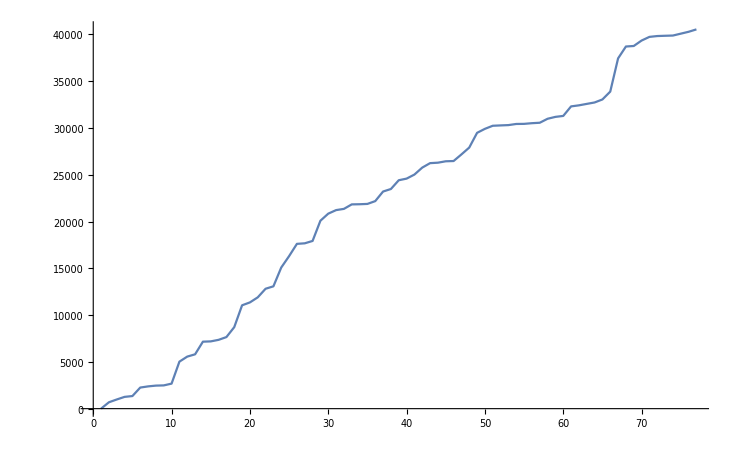

```mathematica
ListPlot[{0,682,980,1259,1347,2255,2380,2463,2486,2676,5025,5564,5809,7160,7191,7356,7652,8713,11049,11357,11899,12818,13077,15087,16303,17616,17675,17928,20089,20846,21224,21356,21836,21852,21886,22186,23211,23481,24417,24591,25024,25768,26245,26294,26444,26471,27177,27911,29485,29912,30241,30278,30312,30433,30444,30516,30563,30989,31191,31293,32312,32424,32579,32731,33053,33893,37444,38713,38769,39351,39742,39832,39861,39886,40086,40287,40544},Joined->True]
```

```mathematica
ListPlay[{1,2,2,3,2,3,8,18,49,59,14,45,69,17,4,1,5,15,42,25,70,10,41,15,31,14,31,29,13,7,108,32,66,33,10,27,16,34,10,3,34,4,28,41,12,62,19,10,34,54,46,79,10,17,25,3,2,14,21,17,23,4,22,1,45,14,7,12,65,87,5,23,8,5,41,44,5,19,73,27,12,6,25,4,38,4,49,17,27,7,43,33,2,12,28,4,10,24,57,1,9,16,9,10,3,43,22,2,8,19,2,3,9,8,31,24,25,1,3,11,37,23,10,47,21,8,106,6,23,38,15,69,14,31,49,1,5,50,4,20,35,65,1,19,39,19,31,3,31,11,9,8,41,17,40,20,21,2,1,4,12,2,7,23,2,6,6,2,17,9,1,4,6,9,40,46,32,18,26,4,29,13,33,7,39,16,14,22,20,23,23,9,27,104,47,1,53,33,6,12,10,23,96,40,4,16,17,21,3,20,14,20,17,42,6,27,5,28,8,35,8,9,38,8,54,3,6,12,26,45,18,8,17,3,24,7,1,11,19,123,4,23,28,14,6,2,183,2,6,61,6,60,1,16,10,67,19,74,19,18,39,3,32,8,12,56,68,4,8,37,15,28,16,30,41,75,50,17,10,16,34,11,4,16,37,10,9,8,13,9,16,2,4,44,3,2,32,9,31,29,5,42,28,8,57,57,5,14,13,5,27,3,86,16,16,6,28,7,11,11,22,8,21,37,83,64,1,7,23,12,42,47,3,27,105,7,79,11,11,4,28,8,3,4,3,27,7,1,1,31,13,7,115,22,14,2,26,19,1,2,10,21,11,2,18,28,1,35,76,18,7,13,12,34,2,2,12,2,26,30,9,51,61,2,6,19,24,3,28,116,4,17,78,129,31,12,43,45,20,18,92,68,3,80,5,19,11,7,23,1,15,14,14,14,14,21,83,60,28,25,25,34,57,24,8,31,105,46,11,20,35,39,15,8,26,37,15,32,1,8,59,70,5,26,64,22,13,43,12,1,12,16,13,30,12,74,25,32,14,3,9,32,30,18,52,41,4,31,10,12,2,11,11,19,41,7,82,45,7,35,9,2,24,24,3,31,3,9,2,20,5,2,12,55,16,7,13,10,32,71,2,4,8,38,25,26,21,6,18,27,34,20,30,43,36,39,8,49,16,53,3,7,25,12,34,4,17,49,5,53,14,12,5,1,27,17,4,38,10,13,124,23,8,31,51,12,25,28,25,10,31,45,3,46,18,4,29,35,23,54,51,18,13,54,21,3,12,23,9,3,36,2,26,27,17,1,16,13,47,57,35,60,20,16,39,1,33,14,3,9,22,3,19,5,23,16,5,21,9,13,38,18,8,3,3,38,18,10,78,31,40,6,7,15,7,5,34,20,67,12,6,7,62,13,4,20,62,39,3,16,94,13,39,3,14,2,12,33,16,3,31,24,28,29,3,25,14,16,10,5,19,43,22,8,15,10,3,5,36,82,6,64,15,24,8,2,5,3,3,24,36,31,14,54,4,23,8,11,6,11,13,15,1,10,14,24,48,29,4,56,9,2,1,14,25,60,33,6,10,11,14,46,37,3,2,12,8,27,23,31,1,26,2,61,13,23,4,13,35,32,14,38,9,8,24,79,5,25,56,28,4,15,42,2,27,9,8,23,37,13,37,30,21,1,16,22,21,24,16,38,55,6,5,60,30,25,36,19,12,98,8,11,1,44,18,6,38,23,119,1,71,47,71,32,10,1,4,26,5,54,22,11,22,5,9,24,20,3,26,5,43,11,35,38,9,7,17,54,23,23,25,19,56,38,56,43,53,12,17,63,3,5,10,16,14,60,2,3,1,12,21,40,3,46,5,26,73,3,12,28,5,21,28,18,1,8,34,4,21,40,108,44,17,6,14,9,82,2,15,39,8,6,9,51,7,7,15,8,38,47,14,43,21,4,1,46,11,12,16,24,7,24,51,194,5,21,4,26,5,12,38,20,30,26,80,1,5,25,23,5,40,3,5,28,18,85,36,41,10,2,61,33,61,6,15,3,45,52,7,1,1,12,3,40,15,16,1,4,3,7,30,38,8,11,11,6,34,100,48,1,4,50,64,11,13,59,33,40,2,46,2,11,9,8,35,26,35,6,5,45,11,46,14,7,18,30,33,20,7,1,33,19,2,41,29,18,7,62,7,46,10,1,4,18,3,1,18,26,24,27,1,7,25,21,43,46,40,13,5,10,40,6,3,59,23,37,6,1,27,24,19,24,18,50,38,11,4,40,8,9,32,35,14,29,32,19,44,6,7,15,15,66,1,22,42,16,31,14,5,4,33,24,9,7,17,38,16,12,1,14,6,2,39,4,8,15,27,45,13,16,2,4,10,76,6,8,40,61,2,3,11,10,56,3,5,44,56,38,8,20,38,7,25,2,15,34,28,16,3,5,96,63,19,111,2,99,51,11,4,4,82,33,50,9,15,3,21,8,45,50,13,34,17,11,34,11,24,38,13,26,4,10,23,28,52,17,18,39,21,15,19,8,4,23,54,74,1,8,8,4,3,16,17,27,33,30,10,10,81,5,8,25,15,1,41,18,75,47,30,7,1,7,36,23,5,31,5,2,74,15,47,10,21,7,43,9,34,56,14,47,10,50,29,73,19,21,36,1,3,67,2,8,27,28,32,27,2,2,3,11,20,12,60,13,3,7,26,6,19,13,2,26,7,13,17,46,3,7,18,11,13,12,9,4,1,16,66,42,16,5,11,3,71,10,18,31,4,36,105,11,4,35,3,43,39,2,14,23,2,6,41,19,2,15,83,18,74,113,24,21,13,4,31,10,11,4,26,12,68,1,39,19,7,44,9,7,21,74,9,8,17,18,7,1,55,28,74,8,16,29,36,2,1,43,43,42,33,23,8,12,31,18,4,3,9,4,1,12,11,7,7,34,3,12,46,43,14,16,21,5,6,88,65,2,11,7,16,45,23,13,3,20,7,10,97,12,4,11,16,58,46,8,43,29,2,7,39,7,41,2,7,1,56,39,20,16,7,1,29,8,2,17,9,40,104,16,16,16,15,9,20,8,38,1,13,10,10,19,13,25,6,12,82,63,28,31,9,24,3,12,61,6,2,61,4,8,62,38,1,9,14,14,34,21,2,26,47,9,33,24,34,19,83,3,27,57,14,7,1,4,17,37,22,11,31,6,7,24,6,11,13,40,6,12,18,47,24,7,12,9,1,7,35,33,9,2,85,11,10,56,20,16,16,29,18,14,22,36,28,14,11,2,31,11,98,14,7,6,73,16,57,4,55,29,20,2,7,5,2,7,11,32,11,3,119,15,18,5,14,38,41,11,73,15,41,9,64,18,10,14,9,3,18,8,66,6,7,12,13,52,9,72,39,21,9,10,31,3,44,31,33,53,50,26,2,14,4,27,3,8,1,6,27,3,53,53,12,5,21,3,7,2,57,7,18,37,58,1,37,2,49,21,24,5,1,41,44,14,14,3,9,2,30,29,4,67,23,47,5,25,16,18,91,18,35,16,61,91,7,21,22,14,41,21,8,28,2,8,23,10,38,17,43,4,30,22,34,14,11,8,7,17,37,24,12,35,8,34,68,1,4,16,54,28,5,10,4,21,14,41,23,44,14,28,1,20,10,98,8,57,21,1,9,54,57,41,3,4,4,86,26,22,27,14,3,37,9,25,1,13,51,48,37,10,59,2,52,20,1,31,13,3,16,2,7,72,4,17,127,3,21,9,40,27,4,14,2,51,25,65,31,9,96,1,19,61,13,68,20,52,7,6,14,9,8,49,18,27,35,4,6,31,23,9,27,12,26,16,45,10,34,1,4,3,27,17,14,38,24,10,15,4,5,3,50,8,70,3,5,9,10,14,6,50,99,51,7,63,43,25,29,1,3,18,30,139,6,32,26,30,9,14,16,3,12,65,8,5,1,28,44,23,11,18,33,13,2,25,5,7,38,7,5,24,4,17,10,5,12,17,62,66,45,16,54,31,13,10,2,22,29,8,12,6,8,35,13,10,140,15,12,44,17,13,3,25,47,1,35,23,17,40,22,7,3,43,11,18,5,13,14,33,16,36,8,25,44,40,27,41,3,9,61,8,31,2,33,56,8,1,28,7,15,4,23,8,12,4,10,7,12,7,20,3,90,15,6,2,1,19,31,19,30,9,3,16,16,76,17,20,29,38,9,44,7,28,2,8,60,17,41,14,6,11,28,14,52,54,49,3,12,15,13,70,23,2,29,24,52,7,11,9,23,28,1,4,1,15,8,51,7,11,8,30,1,28,1,15,146,13,4,7,45,14,2,43,8,34,30,18,24,9,19,19,24,1,80,27,6,6,15,19,19,34,1,81,7,20,21,12,17,2,10,9,7,32,1,29,38,29,24,19,30,74,82,17,4,37,6,45,18,6,7,9,22,21,4,23,58,26,21,15,1,8,24,10,14,12,11,20,18,63,53,57,5,5,28,21,15,6,8,52,18,1,12,22,38,10,11,27,31,46,56,13,22,113,32,37,36,25,12,2,2,11,24,16,7,98,37,26,3,10,24,10,22,2,7,30,8,8,28,11,155,107,29,24,12,41,4,8,25,5,10,23,25,13,35,3,6,33,19,84,24,5,20,1,69,28,4,150,20,82,29,3,6,1,10,3,1,27,75,2,3,134,32,24,61,2,26,2,58,36,12,28,13,23,6,36,17,6,6,86,24,7,13,1,16,3,19,10,22,11,21,2,30,1,61,52,7,2,46,6,25,3,4,9,32,9,53,8,13,9,1,21,21,43,14,8,51,16,14,7,8,1,15,14,48,3,1,7,8,4,20,2,23,7,36,9,10,11,9,7,3,29,42,1,1,1,16,4,46,9,23,11,12,22,27,18,10,28,8,3,7,58,48,7,30,14,60,29,21,52,10,16,37,10,51,8,2,5,46,24,20,14,7,29,13,4,10,51,36,18,37,15,13,9,11,13,37,32,26,28,26,8,65,57,24,74,12,3,8,13,6,13,6,71,118,5,2,8,2,135,10,1,6,39,2,37,11,23,38,25,12,12,23,11,4,110,39,13,24,1,57,1,4,1,4,44,42,10,55,7,7,74,56,28,56,5,113,10,32,21,23,1,37,7,1,10,23,18,20,3,81,4,10,17,47,16,22,18,5,87,4,33,15,29,2,38,10,7,2,19,10,11,20,4,98,7,21,9,16,78,15,15,11,3,25,6,60,14,42,10,47,14,6,48,4,6,65,6,37,2,7,1,6,17,74,25,26,25,93,15,14,4,14,8,58,41,74,1,2,2,4,13,8,28,14,3,11,167,12,1,16,58,10,32,11,90,29,20,26,13,24,86,33,12,8,13,7,3,1,7,5,36,36,10,17,8,6,45,12,34,14,43,3,42,63,16,42,24,9,45,9,7,47,9,3,28,21,24,36,43,22,55,3,32,20,1,14,45,10,22,2,33,48,7,31,61,25,13,29,65,125,7,2,15,6,7,28,18,59,84,7,15,6,6,10,82,2,3,16,3,3,19,11,16,11,6,22,26,6,2,37,1,1,7,76,15,5,136,15,8,80,26,8,12,9,26,70,10,3,18,8,39,12,15,1,57,2,4,8,6,5,11,49,28,22,63,4,18,19,6,1,6,2,3,9,47,3,20,18,33,16,49,59,6,15,9,23,30,31,27,18,19,9,48,8,11,7,19,36,7,18,1,2,4,17,107,21,6,20,101,2,51,23,3,18,1,12,20,22,16,24,14,46,4,3,39,26,56,9,77,1,32,67,36,49,2,58,24,75,5,5,42,7,1,46,22,41,23,36,48,9,12,25,36,1,1,12,7,1,37,12,6,40,7,4,15,24,6,24,3,4,9,14,28,63,79,21,56,53,92,18,1,1,10,27,41,8,49,61,3,22,44,3,4,4,11,2,18,18,22,4,43,8,42,14,14,10,5,6,25,6,43,49,5,1,26,13,8,1,48,58,13,4,13,44,8,26,4,11,66,37,4,33,3,2,2,2,4,1,27,13,23,8,12,1,29,16,31,10,4,7,11,7,19,18,79,29,55,77,1,6,33,14,26,39,29,8,36,15,20,4,7,17,14,100,1,32,9,18,5,27,36,4,1,25,63,46,50,7,8,16,29,5,7,24,35,11,1,3,63,1,51,19,7,3,48,37,8,13,2,46,53,8,12,16,29,49,12,6,144,64,7,8,15,17,60,12,47,11,14,1,27,64,16,5,9,27,2,2,4,14,2,21,2,15,5,58,3,42,85,46,73,5,3,10,12,5,9,8,2,42,35,26,1,4,5,73,52,8,17,39,3,16,5,14,38,17,8,1,54,40,8,8,3,8,24,1,26,2,21,11,107,24,1,9,52,18,51,38,23,31,30,8,8,51,1,76,7,27,8,29,5,25,10,38,1,27,34,4,3,18,36,17,28,45,4,36,30,2,9,28,75,80,15,5,2,53,9,14,28,14,18,2,8,65,14,8,4,9,5,24,37,3,85,14,86,17,17,32,48,4,111,3,4,8,5,19,54,16,2,6,67,4,25,9,1,63,17,16,8,13,20,9,14,4,10,49,5,78,21,19,26,9,1,35,4,64,13,6,5,17,88,11,10,18,2,5,62,72,16,86,16,20,26,6,27,20,16,4,2,37,23,13,3,13,38,15,17,5,20,2,2,23,4,41,11,5,21,13,11,52,6,36,31,8,16,21,4,2,68,37,17,118,4,22,3,8,14,4,61,29,64,7,68,9,52,1,41,54,19,22,30,103,7,1,9,13,96,27,24,31,18,47,25,57,61,4,18,17,49,9,9,21,31,36,9,56,14,24,18,22,31,2,9,24,12,63,9,4,14,66,7,25,54,18,15,2,32,1,31,43,135,118,79,2,29,7,21,12,12,16,3,4,7,11,6,47,13,26,16,26,23,16,6,35,47,66,11,13,50,13,3,28,17,26,30,36,27,19,57,66,29,9,86,3,32,2,8,52,16,2,3,3,9,3,18,20,4,18,13,19,1,64,8,60,1,16,9,1,86,1,21,27,8,19,3,3,37,51,8,17,56,10,12,4,10,1,14,1,34,7,71,39,17,18,24,63,3,8,26,15,21,2,32,8,10,33,43,17,4,90,14,117,18,22,135,39,29,8,14,54,61,36,2,15,1,16,29,25,8,4,9,74,6,11,1,14,11,15,7,34,1,3,111,4,1,2,29,1,19,9,36,17,5,46,12,20,2,22,32,171,7,9,41,25,5,32,6,26,1,10,14,23,4,3,10,48,7,5,4,20,8,14,4,14,16,62,17,20,38,8,41,21,22,1,56,29,13,4,19,16,1,13,10,48,38,11,9,19,23,22,1,25,6,21,41,62,3,11,8,7,22,1,35,2,2,10,6,72,28,27,22,29,10,10,48,23,65,7,37,9,11,6,14,4,11,12,9,14,13,40,5,2,5,1,1,4,8,79,30,52,33,5,48,21,7,22,4,33,20,32,1,4,2,30,1,37,48,48,8,17,42,10,34,7,11,9,43,38,15,22,24,23,13,20,2,2,45,24,13,1,71,63,4,12,4,46,81,35,4,10,5,35,25,5,3,40,26,16,8,49,33,25,14,1,23,48,24,2,18,18,14,21,26,83,60,3,42,1,39,3,52,15,16,25,92,41,1,74,20,29,46,18,6,10,1,17,1,37,12,30,7,21,10,5,14,8,1,11,52,29,10,8,6,7,22,46,71,33,16,29,40,22,23,51,3,1,10,72,8,2,14,84,2,14,37,24,33,3,41,34,22,97,35,22,3,29,61,37,17,4,25,22,7,11,8,47,16,2,13,58,16,14,38,26,10,20,48,5,36,26,1,94,15,35,6,20,35,12,69,4,2,52,45,53,4,32,1,12,2,41,13,20,22,12,2,43,17,129,5,11,16,2,39,17,25,45,64,14,7,81,36,16,21,27,1,21,10,32,32,19,17,2,7,24,23,3,18,29,7,3,3,76,23,19,24,2,13,66,7,1,8,3,7,20,69,4,29,61,4,8,7,11,1,4,33,50,31,40,17,5,6,4,26,24,23,1,1,17,39,5,24,31,33,4,16,35,11,51,2,12,31,4,42,86,8,23,63,14,2,27,4,95,53,31,8,73,71,15,22,8,16,13,1,70,11,31,15,48,17,15,49,1,1,49,40,2,9,12,3,3,28,16,21,2,3,67,1,10,21,18,16,4,1,27,8,6,10,20,124,5,64,40,10,8,49,6,7,5,20,43,22,31,70,15,31,2,14,58,18,107,29,4,32,17,24,5,26,6,10,36,6,75,31,10,14,3,2,43,73,56,6,8,2,46,22,83,21,79,1,3,71,4,11,3,4,20,26,38,58,14,3,1,13,17,38,10,15,11,27,6,13,28,43,12,23,9,19,25,56,54,7,66,7,11,3,31,69,2,13,21,31,15,13,17,2,45,70,13,6,53,8,11,50,10,17,16,38,10,14,1,12,7,2,6,55,11,34,25,29,2,63,19,5,23,15,32,38,17,82,36,28,2,35,31,43,11,4,8,89,19,27,5,19,7,1,4,30,23,15,25,12,32,13,16,58,60,17,10,1,17,11,25,11,11,28,30,11,24,28,29,11,9,14,1,31,102,14,49,31,16,16,3,13,52,11,23,10,38,61,49,9,53,3,4,24,20,30,11,31,34,47,3,6,36,13,7,15,23,5,17,50,8,26,16,3,62,6,37,34,7,25,11,11,24,16,7,81,1,55,12,2,17,13,13,37,16,27,3,20,5,19,35,58,33,1,24,18,2,22,2,11,65,17,42,16,43,26,31,34,17,19,15,15,22,5,14,17,68,9,16,13,10,34,42,24,14,25,34,21,35,45,53,3,29,22,75,6,10,9,31,3,26,9,7,149,13,27,4,8,14,36,11,9,5,40,16,17,12,64,3,90,39,34,23,21,57,8,61,30,24,11,7,42,78,76,1,22,42,1,2,46,1,38,2,51,13,1,11,7,4,3,10,11,77,53,96,61,1,22,66,14,4,92,13,43,11,2,31,112,38,25,22,6,23,27,56,9,10,8,6,23,40,40,2,21,3,8,5,63,1,53,4,30,43,1,15,2,11,59,5,23,7,74,4,2,2,25,18,9,6,8,21,15,114,29,10,4,2,60,84,35,2,1,81,16,17,4,1,1}]
```

-Graphics-

```mathematica
ListPlay[{1,2,2,3,2,3,8,18,49,59,14,45,69,17,4,1,5,15,42,25,70,10,41,15,31,14,31,29,13,7,108,32,66,33,10,27,16,34,10,3,34,4,28,41,12,62,19,10,34,54,46,79,10,17,25,3,2,14,21,17,23,4,22,1,45,14,7,12,65,87,5,23,8,5,41,44,5,19,73,27,12,6,25,4,38,4,49,17,27,7,43,33,2,12,28,4,10,24,57,1,9,16,9,10,3,43,22,2,8,19,2,3,9,8,31,24,25,1,3,11,37,23,10,47,21,8,106,6,23,38,15,69,14,31,49,1,5,50,4,20,35,65,1,19,39,19,31,3,31,11,9,8,41,17,40,20,21,2,1,4,12,2,7,23,2,6,6,2,17,9,1,4,6,9,40,46,32,18,26,4,29,13,33,7,39,16,14,22,20,23,23,9,27,104,47,1,53,33,6,12,10,23,96,40,4,16,17,21,3,20,14,20,17,42,6,27,5,28,8,35,8,9,38,8,54,3,6,12,26,45,18,8,17,3,24,7,1,11,19,123,4,23,28,14,6,2,183,2,6,61,6,60,1,16,10,67,19,74,19,18,39,3,32,8,12,56,68,4,8,37,15,28,16,30,41,75,50,17,10,16,34,11,4,16,37,10,9,8,13,9,16,2,4,44,3,2,32,9,31,29,5,42,28,8,57,57,5,14,13,5,27,3,86,16,16,6,28,7,11,11,22,8,21,37,83,64,1,7,23,12,42,47,3,27,105,7,79,11,11,4,28,8,3,4,3,27,7,1,1,31,13,7,115,22,14,2,26,19,1,2,10,21,11,2,18,28,1,35,76,18,7,13,12,34,2,2,12,2,26,30,9,51,61,2,6,19,24,3,28,116,4,17,78,129,31,12,43,45,20,18,92,68,3,80,5,19,11,7,23,1,15,14,14,14,14,21,83,60,28,25,25,34,57,24,8,31,105,46,11,20,35,39,15,8,26,37,15,32,1,8,59,70,5,26,64,22,13,43,12,1,12,16,13,30,12,74,25,32,14,3,9,32,30,18,52,41,4,31,10,12,2,11,11,19,41,7,82,45,7,35,9,2,24,24,3,31,3,9,2,20,5,2,12,55,16,7,13,10,32,71,2,4,8,38,25,26,21,6,18,27,34,20,30,43,36,39,8,49,16,53,3,7,25,12,34,4,17,49,5,53,14,12,5,1,27,17,4,38,10,13,124,23,8,31,51,12,25,28,25,10,31,45,3,46,18,4,29,35,23,54,51,18,13,54,21,3,12,23,9,3,36,2,26,27,17,1,16,13,47,57,35,60,20,16,39,1,33,14,3,9,22,3,19,5,23,16,5,21,9,13,38,18,8,3,3,38,18,10,78,31,40,6,7,15,7,5,34,20,67,12,6,7,62,13,4,20,62,39,3,16,94,13,39,3,14,2,12,33,16,3,31,24,28,29,3,25,14,16,10,5,19,43,22,8,15,10,3,5,36,82,6,64,15,24,8,2,5,3,3,24,36,31,14,54,4,23,8,11,6,11,13,15,1,10,14,24,48,29,4,56,9,2,1,14,25,60,33,6,10,11,14,46,37,3,2,12,8,27,23,31,1,26,2,61,13,23,4,13,35,32,14,38,9,8,24,79,5,25,56,28,4,15,42,2,27,9,8,23,37,13,37,30,21,1,16,22,21,24,16,38,55,6,5,60,30,25,36,19,12,98,8,11,1,44,18,6,38,23,119,1,71,47,71,32,10,1,4,26,5,54,22,11,22,5,9,24,20,3,26,5,43,11,35,38,9,7,17,54,23,23,25,19,56,38,56,43,53,12,17,63,3,5,10,16,14,60,2,3,1,12,21,40,3,46,5,26,73,3,12,28,5,21,28,18,1,8,34,4,21,40,108,44,17,6,14,9,82,2,15,39,8,6,9,51,7,7,15,8,38,47,14,43,21,4,1,46,11,12,16,24,7,24,51,194,5,21,4,26,5,12,38,20,30,26,80,1,5,25,23,5,40,3,5,28,18,85,36,41,10,2,61,33,61,6,15,3,45,52,7,1,1,12,3,40,15,16,1,4,3,7,30,38,8,11,11,6,34,100,48,1,4,50,64,11,13,59,33,40,2,46,2,11,9,8,35,26,35,6,5,45,11,46,14,7,18,30,33,20,7,1,33,19,2,41,29,18,7,62,7,46,10,1,4,18,3,1,18,26,24,27,1,7,25,21,43,46,40,13,5,10,40,6,3,59,23,37,6,1,27,24,19,24,18,50,38,11,4,40,8,9,32,35,14,29,32,19,44,6,7,15,15,66,1,22,42,16,31,14,5,4,33,24,9,7,17,38,16,12,1,14,6,2,39,4,8,15,27,45,13,16,2,4,10,76,6,8,40,61,2,3,11,10,56,3,5,44,56,38,8,20,38,7,25,2,15,34,28,16,3,5,96,63,19,111,2,99,51,11,4,4,82,33,50,9,15,3,21,8,45,50,13,34,17,11,34,11,24,38,13,26,4,10,23,28,52,17,18,39,21,15,19,8,4,23,54,74,1,8,8,4,3,16,17,27,33,30,10,10,81,5,8,25,15,1,41,18,75,47,30,7,1,7,36,23,5,31,5,2,74,15,47,10,21,7,43,9,34,56,14,47,10,50,29,73,19,21,36,1,3,67,2,8,27,28,32,27,2,2,3,11,20,12,60,13,3,7,26,6,19,13,2,26,7,13,17,46,3,7,18,11,13,12,9,4,1,16,66,42,16,5,11,3,71,10,18,31,4,36,105,11,4,35,3,43,39,2,14,23,2,6,41,19,2,15,83,18,74,113,24,21,13,4,31,10,11,4,26,12,68,1,39,19,7,44,9,7,21,74,9,8,17,18,7,1,55,28,74,8,16,29,36,2,1,43,43,42,33,23,8,12,31,18,4,3,9,4,1,12,11,7,7,34,3,12,46,43,14,16,21,5,6,88,65,2,11,7,16,45,23,13,3,20,7,10,97,12,4,11,16,58,46,8,43,29,2,7,39,7,41,2,7,1,56,39,20,16,7,1,29,8,2,17,9,40,104,16,16,16,15,9,20,8,38,1,13,10,10,19,13,25,6,12,82,63,28,31,9,24,3,12,61,6,2,61,4,8,62,38,1,9,14,14,34,21,2,26,47,9,33,24,34,19,83,3,27,57,14,7,1,4,17,37,22,11,31,6,7,24,6,11,13,40,6,12,18,47,24,7,12,9,1,7,35,33,9,2,85,11,10,56,20,16,16,29,18,14,22,36,28,14,11,2,31,11,98,14,7,6,73,16,57,4,55,29,20,2,7,5,2,7,11,32,11,3,119,15,18,5,14,38,41,11,73,15,41,9,64,18,10,14,9,3,18,8,66,6,7,12,13,52,9,72,39,21,9,10,31,3,44,31,33,53,50,26,2,14,4,27,3,8,1,6,27,3,53,53,12,5,21,3,7,2,57,7,18,37,58,1,37,2,49,21,24,5,1,41,44,14,14,3,9,2,30,29,4,67,23,47,5,25,16,18,91,18,35,16,61,91,7,21,22,14,41,21,8,28,2,8,23,10,38,17,43,4,30,22,34,14,11,8,7,17,37,24,12,35,8,34,68,1,4,16,54,28,5,10,4,21,14,41,23,44,14,28,1,20,10,98,8,57,21,1,9,54,57,41,3,4,4,86,26,22,27,14,3,37,9,25,1,13,51,48,37,10,59,2,52,20,1,31,13,3,16,2,7,72,4,17,127,3,21,9,40,27,4,14,2,51,25,65,31,9,96,1,19,61,13,68,20,52,7,6,14,9,8,49,18,27,35,4,6,31,23,9,27,12,26,16,45,10,34,1,4,3,27,17,14,38,24,10,15,4,5,3,50,8,70,3,5,9,10,14,6,50,99,51,7,63,43,25,29,1,3,18,30,139,6,32,26,30,9,14,16,3,12,65,8,5,1,28,44,23,11,18,33,13,2,25,5,7,38,7,5,24,4,17,10,5,12,17,62,66,45,16,54,31,13,10,2,22,29,8,12,6,8,35,13,10,140,15,12,44,17,13,3,25,47,1,35,23,17,40,22,7,3,43,11,18,5,13,14,33,16,36,8,25,44,40,27,41,3,9,61,8,31,2,33,56,8,1,28,7,15,4,23,8,12,4,10,7,12,7,20,3,90,15,6,2,1,19,31,19,30,9,3,16,16,76,17,20,29,38,9,44,7,28,2,8,60,17,41,14,6,11,28,14,52,54,49,3,12,15,13,70,23,2,29,24,52,7,11,9,23,28,1,4,1,15,8,51,7,11,8,30,1,28,1,15,146,13,4,7,45,14,2,43,8,34,30,18,24,9,19,19,24,1,80,27,6,6,15,19,19,34,1,81,7,20,21,12,17,2,10,9,7,32,1,29,38,29,24,19,30,74,82,17,4,37,6,45,18,6,7,9,22,21,4,23,58,26,21,15,1,8,24,10,14,12,11,20,18,63,53,57,5,5,28,21,15,6,8,52,18,1,12,22,38,10,11,27,31,46,56,13,22,113,32,37,36,25,12,2,2,11,24,16,7,98,37,26,3,10,24,10,22,2,7,30,8,8,28,11,155,107,29,24,12,41,4,8,25,5,10,23,25,13,35,3,6,33,19,84,24,5,20,1,69,28,4,150,20,82,29,3,6,1,10,3,1,27,75,2,3,134,32,24,61,2,26,2,58,36,12,28,13,23,6,36,17,6,6,86,24,7,13,1,16,3,19,10,22,11,21,2,30,1,61,52,7,2,46,6,25,3,4,9,32,9,53,8,13,9,1,21,21,43,14,8,51,16,14,7,8,1,15,14,48,3,1,7,8,4,20,2,23,7,36,9,10,11,9,7,3,29,42,1,1,1,16,4,46,9,23,11,12,22,27,18,10,28,8,3,7,58,48,7,30,14,60,29,21,52,10,16,37,10,51,8,2,5,46,24,20,14,7,29,13,4,10,51,36,18,37,15,13,9,11,13,37,32,26,28,26,8,65,57,24,74,12,3,8,13,6,13,6,71,118,5,2,8,2,135,10,1,6,39,2,37,11,23,38,25,12,12,23,11,4,110,39,13,24,1,57,1,4,1,4,44,42,10,55,7,7,74,56,28,56,5,113,10,32,21,23,1,37,7,1,10,23,18,20,3,81,4,10,17,47,16,22,18,5,87,4,33,15,29,2,38,10,7,2,19,10,11,20,4,98,7,21,9,16,78,15,15,11,3,25,6,60,14,42,10,47,14,6,48,4,6,65,6,37,2,7,1,6,17,74,25,26,25,93,15,14,4,14,8,58,41,74,1,2,2,4,13,8,28,14,3,11,167,12,1,16,58,10,32,11,90,29,20,26,13,24,86,33,12,8,13,7,3,1,7,5,36,36,10,17,8,6,45,12,34,14,43,3,42,63,16,42,24,9,45,9,7,47,9,3,28,21,24,36,43,22,55,3,32,20,1,14,45,10,22,2,33,48,7,31,61,25,13,29,65,125,7,2,15,6,7,28,18,59,84,7,15,6,6,10,82,2,3,16,3,3,19,11,16,11,6,22,26,6,2,37,1,1,7,76,15,5,136,15,8,80,26,8,12,9,26,70,10,3,18,8,39,12,15,1,57,2,4,8,6,5,11,49,28,22,63,4,18,19,6,1,6,2,3,9,47,3,20,18,33,16,49,59,6,15,9,23,30,31,27,18,19,9,48,8,11,7,19,36,7,18,1,2,4,17,107,21,6,20,101,2,51,23,3,18,1,12,20,22,16,24,14,46,4,3,39,26,56,9,77,1,32,67,36,49,2,58,24,75,5,5,42,7,1,46,22,41,23,36,48,9,12,25,36,1,1,12,7,1,37,12,6,40,7,4,15,24,6,24,3,4,9,14,28,63,79,21,56,53,92,18,1,1,10,27,41,8,49,61,3,22,44,3,4,4,11,2,18,18,22,4,43,8,42,14,14,10,5,6,25,6,43,49,5,1,26,13,8,1,48,58,13,4,13,44,8,26,4,11,66,37,4,33,3,2,2,2,4,1,27,13,23,8,12,1,29,16,31,10,4,7,11,7,19,18,79,29,55,77,1,6,33,14,26,39,29,8,36,15,20,4,7,17,14,100,1,32,9,18,5,27,36,4,1,25,63,46,50,7,8,16,29,5,7,24,35,11,1,3,63,1,51,19,7,3,48,37,8,13,2,46,53,8,12,16,29,49,12,6,144,64,7,8,15,17,60,12,47,11,14,1,27,64,16,5,9,27,2,2,4,14,2,21,2,15,5,58,3,42,85,46,73,5,3,10,12,5,9,8,2,42,35,26,1,4,5,73,52,8,17,39,3,16,5,14,38,17,8,1,54,40,8,8,3,8,24,1,26,2,21,11,107,24,1,9,52,18,51,38,23,31,30,8,8,51,1,76,7,27,8,29,5,25,10,38,1,27,34,4,3,18,36,17,28,45,4,36,30,2,9,28,75,80,15,5,2,53,9,14,28,14,18,2,8,65,14,8,4,9,5,24,37,3,85,14,86,17,17,32,48,4,111,3,4,8,5,19,54,16,2,6,67,4,25,9,1,63,17,16,8,13,20,9,14,4,10,49,5,78,21,19,26,9,1,35,4,64,13,6,5,17,88,11,10,18,2,5,62,72,16,86,16,20,26,6,27,20,16,4,2,37,23,13,3,13,38,15,17,5,20,2,2,23,4,41,11,5,21,13,11,52,6,36,31,8,16,21,4,2,68,37,17,118,4,22,3,8,14,4,61,29,64,7,68,9,52,1,41,54,19,22,30,103,7,1,9,13,96,27,24,31,18,47,25,57,61,4,18,17,49,9,9,21,31,36,9,56,14,24,18,22,31,2,9,24,12,63,9,4,14,66,7,25,54,18,15,2,32,1,31,43,135,118,79,2,29,7,21,12,12,16,3,4,7,11,6,47,13,26,16,26,23,16,6,35,47,66,11,13,50,13,3,28,17,26,30,36,27,19,57,66,29,9,86,3,32,2,8,52,16,2,3,3,9,3,18,20,4,18,13,19,1,64,8,60,1,16,9,1,86,1,21,27,8,19,3,3,37,51,8,17,56,10,12,4,10,1,14,1,34,7,71,39,17,18,24,63,3,8,26,15,21,2,32,8,10,33,43,17,4,90,14,117,18,22,135,39,29,8,14,54,61,36,2,15,1,16,29,25,8,4,9,74,6,11,1,14,11,15,7,34,1,3,111,4,1,2,29,1,19,9,36,17,5,46,12,20,2,22,32,171,7,9,41,25,5,32,6,26,1,10,14,23,4,3,10,48,7,5,4,20,8,14,4,14,16,62,17,20,38,8,41,21,22,1,56,29,13,4,19,16,1,13,10,48,38,11,9,19,23,22,1,25,6,21,41,62,3,11,8,7,22,1,35,2,2,10,6,72,28,27,22,29,10,10,48,23,65,7,37,9,11,6,14,4,11,12,9,14,13,40,5,2,5,1,1,4,8,79,30,52,33,5,48,21,7,22,4,33,20,32,1,4,2,30,1,37,48,48,8,17,42,10,34,7,11,9,43,38,15,22,24,23,13,20,2,2,45,24,13,1,71,63,4,12,4,46,81,35,4,10,5,35,25,5,3,40,26,16,8,49,33,25,14,1,23,48,24,2,18,18,14,21,26,83,60,3,42,1,39,3,52,15,16,25,92,41,1,74,20,29,46,18,6,10,1,17,1,37,12,30,7,21,10,5,14,8,1,11,52,29,10,8,6,7,22,46,71,33,16,29,40,22,23,51,3,1,10,72,8,2,14,84,2,14,37,24,33,3,41,34,22,97,35,22,3,29,61,37,17,4,25,22,7,11,8,47,16,2,13,58,16,14,38,26,10,20,48,5,36,26,1,94,15,35,6,20,35,12,69,4,2,52,45,53,4,32,1,12,2,41,13,20,22,12,2,43,17,129,5,11,16,2,39,17,25,45,64,14,7,81,36,16,21,27,1,21,10,32,32,19,17,2,7,24,23,3,18,29,7,3,3,76,23,19,24,2,13,66,7,1,8,3,7,20,69,4,29,61,4,8,7,11,1,4,33,50,31,40,17,5,6,4,26,24,23,1,1,17,39,5,24,31,33,4,16,35,11,51,2,12,31,4,42,86,8,23,63,14,2,27,4,95,53,31,8,73,71,15,22,8,16,13,1,70,11,31,15,48,17,15,49,1,1,49,40,2,9,12,3,3,28,16,21,2,3,67,1,10,21,18,16,4,1,27,8,6,10,20,124,5,64,40,10,8,49,6,7,5,20,43,22,31,70,15,31,2,14,58,18,107,29,4,32,17,24,5,26,6,10,36,6,75,31,10,14,3,2,43,73,56,6,8,2,46,22,83,21,79,1,3,71,4,11,3,4,20,26,38,58,14,3,1,13,17,38,10,15,11,27,6,13,28,43,12,23,9,19,25,56,54,7,66,7,11,3,31,69,2,13,21,31,15,13,17,2,45,70,13,6,53,8,11,50,10,17,16,38,10,14,1,12,7,2,6,55,11,34,25,29,2,63,19,5,23,15,32,38,17,82,36,28,2,35,31,43,11,4,8,89,19,27,5,19,7,1,4,30,23,15,25,12,32,13,16,58,60,17,10,1,17,11,25,11,11,28,30,11,24,28,29,11,9,14,1,31,102,14,49,31,16,16,3,13,52,11,23,10,38,61,49,9,53,3,4,24,20,30,11,31,34,47,3,6,36,13,7,15,23,5,17,50,8,26,16,3,62,6,37,34,7,25,11,11,24,16,7,81,1,55,12,2,17,13,13,37,16,27,3,20,5,19,35,58,33,1,24,18,2,22,2,11,65,17,42,16,43,26,31,34,17,19,15,15,22,5,14,17,68,9,16,13,10,34,42,24,14,25,34,21,35,45,53,3,29,22,75,6,10,9,31,3,26,9,7,149,13,27,4,8,14,36,11,9,5,40,16,17,12,64,3,90,39,34,23,21,57,8,61,30,24,11,7,42,78,76,1,22,42,1,2,46,1,38,2,51,13,1,11,7,4,3,10,11,77,53,96,61,1,22,66,14,4,92,13,43,11,2,31,112,38,25,22,6,23,27,56,9,10,8,6,23,40,40,2,21,3,8,5,63,1,53,4,30,43,1,15,2,11,59,5,23,7,74,4,2,2,25,18,9,6,8,21,15,114,29,10,4,2,60,84,35,2,1,81,16,17,4,1,50,24,11,20,26,12,43,4,20,9,14,99,6,27,33,3,7,7,15,19,61,60,35,13,23,4,13,7,1,24,20,4,12,38,3,17,80,32,28,46,1,55,1,40,7,1,3,104,12,15,50,21,36,14,10,21,41,56,122,2,5,10,2,10,37,9,63,26,30,11,10,18,1,6,12,22,37,14,27,13,12,12,88,12,45,8,13,53,15,8,16,1,42,37,4,42,1,11,13,9,8,68,4,14,3,20,10,15,12,60,45,4,6,28,4,15,4,3,26,11,20,15,76,34,6,15,2,9,17,22,10,12,3,88,45,80,17,12,43,3,9,7,9,52,11,60,21,4,27,6,30,9,55,83,11,8,15,97,29,6,22,22,6,8,9,16,19,14,7,11,23,52,27,9,104,42,2,10,10,6,86,17,6,35,60,17,26,2,23,70,67,16,1,3,36,9,24,1,32,27,16,11,42,29,13,101,14,16,29,17,51,23,5,63,40,12,18,27,1,20,24,144,45,4,1,14,5,9,9,35,25,26,14,4,9,1,6,3,54,36,29,42,6,102,4,31,6,1,33,4,2,7,3,5,9,66,48,5,15,18,15,18,8,7,8,131,9,8,27,45,18,13,24,4,54,16,10,12,5,9,12,13,26,25,82,14,1,16,6,44,4,37,39,15,1,64,4,17,16,20,85,24,14,29,42,51,5,77,18,8,6,4,38,40,7,3,56,12,6,71,2,16,9,10,21,11,27,12,109,10,21,64,36,26,30,58,26,4,14,13,6,90,93,19,25,1,3,84,42,17,3,4,10,12,2,20,39,4,5,95,6,16,14,29,19,117,58,46,1,6,10,1,22,7,70,7,14,21,21,27,17,11,26,9,8,62,13,11,21,9,23,14,122,136,6,14,5,8,29,66,5,21,35,9,22,83,4,9,6,45,7,21,8,57,17,1,35,28,23,22,16,14,13,1,9,11,7,31,31,67,42,8,81,45,33,14,13,35,22,17,15,9,34,8,21,10,11,14,4,9,12,1,4,15,60,34,30,3,32,18,1,48,52,5,41,20,10,11,14,6,13,51,53,37,19,17,8,2,4,2,38,1,74,5,1,29,39,7,14,43,5,12,3,73,19,46,25,14,12,13,6,59,36,10,10,2,54,1,36,3,12,65,7,6,73,27,7,74,16,15,25,53,9,1,13,14,16,13,11,19,17,39,6,10,1,6,31,29,33,7,62,19,6,10,53,18,11,22,46,4,60,9,5,8,24,2,1,16,3,10,2,3,37,59,56,4,5,6,23,26,8,12,4,27,5,16,10,15,6,42,25,19,24,31,48,23,26,5,5,14,9,22,5,26,40,29,16,2,12,37,12,13,50,9,41,18,11,16,32,8,30,64,7,23,30,26,27,27,27,66,2,5,38,20,21,2,107,36,10,29,36,22,67,36,3,31,2,56,2,47,65,1,3,16,11,12,18,3,29,4,10,7,4,40,1,7,3,2,8,10,8,9,35,14,17,17,2,71,47,10,3,8,21,25,140,51,14,68,15,37,34,15,2,10,4,3,31,36,51,4,8,33,8,33,2,22,9,6,29,15,31,44,8,8,7,25,3,39,14,23,7,67,26,36,23,24,19,6,9,46,54,12,24,46,27,40,5,6,26,12,20,8,9,13,2,3,51,24,2,157,34,9,8,8,55,7,42,8,22,180,16,44,23,53,8,44,8,4,91,25,53,42,17,3,5,2,106,32,11,9,11,12,21,24,15,86,12,35,92,26,25,61,4,23,46,74,4,40,41,17,18,39,150,36,3,23,49,11,3,9,7,2,11,22,32,26,81,17,36,7,61,30,5,2,5,125,19,1,7,40,18,4,35,53,2,25,51,78,7,35,6,125,6,13,20,12,4,11,7,116,11,7,42,18,7,7,62,1,18,15,67,25,20,11,8,46,6,6,2,3,10,28,18,5,2,52,38,8,29,29,23,7,1,6,4,33,38,11,24,24,11,14,15,2,41,1,95,24,31,13,15,10,22,7,64,12,12,1,8,9,28,12,5,5,1,18,2,1,4,4,7,33,6,14,1,35,1,2,11,2,16,15,26,4,64,10,7,17,4,2,28,22,1,1,48,54,3,30,54,6,7,3,90,45,11,38,2,34,13,7,18,46,10,15,1,5,1,8,34,29,19,1,23,16,9,63,13,26,19,28,3,34,7,4,24,21,83,107,6,30,7,11,13,2,56,17,12,22,62,8,8,67,57,6,4,42,38,49,16,2,14,2,7,24,26,5,29,12,65,3,18,3,94,52,20,38,55,8,22,15,36,20,16,9,17,15,9,45,18,27,1,1,16,1,44,16,9,67,63,42,13,104,18,16,1,136,10,18,11,22,24,16,54,164,10,5,29,14,40,4,7,11,33,43,18,15,28,4,10,15,35,19,13,11,16,34,43,2,29,57,26,6,38,25,42,37,14,43,7,14,4,18,50,20,5,12,9,28,14,12,63,2,44,7,20,4,20,44,29,14,45,108,12,16,2,29,16,159,13,8,39,79,16,17,14,31,3,6,12,15,36,18,34,74,13,22,25,7,4,7,90,124,13,4,11,5,4,2,15,37,2,21,40,4,6,65,12,22,9,2,55,5,6,15,11,1,2,77,75,29,18,7,36,5,16,27,26,1,12,36,9,42,17,8,21,14,34,4,10,15,79,62,10,82,42,12,9,52,32,50,19,2,17,34,32,22,14,3,22,4,11,22,22,14,17,2,2,6,33,37,25,16,42,7,34,18,8,12,16,22,10,3,24,9,2,18,5,117,6,8,18,8,56,69,7,11,3,12,4,5,2,50,11,25,28,3,22,15,16,8,1,30,56,26,68,21,18,12,24,5,16,32,13,13,16,18,16,2,4,5,2,17,45,23,13,9,1,8,7,22,33,17,35,12,36,32,15,16,42,7,5,17,27,24,42,39,1,6,46,22,39,60,47,2,25,13,3,10,46,4,21,6,17,12,10,88,28,26,19,7,49,78,17,8,5,42,46,11,12,15,20,7,41,9,28,5,6,35,61,20,9,39,53,35,17,11,1,5,70,76,58,5,25,13,6,41,29,1,47,42,32,8,4,15,4,28,41,6,22,7,33,14,38,57,25,38,17,23,19,10,26,19,71,93,11,1,24,52,7,36,24,41,10,28,4,36,5,3,2,19,16,5,12,17,2,18,18,33,1,20,1,33,103,60,18,37,11,22,6,16,59,12,54,55,22,45,6,28,2,21,2,2,9,39,19,28,9,14,11,12,21,61,54,9,12,7,21,29,13,18,11,1,1,23,10,46,30,76,47,25,55,27,9,15,35,3,41,55,7,5,18,12,64,27,33,12,1,13,8,6,11,16,26,1,19,72,7,12,19,7,15,9,14,15,23,31,10,20,3,1,7,15,70,72,2,13,9,12,1,22,18,66,9,34,16,58,8,32,14,10,50,46,8,33,41,3,10,13,24,6,68,29,12,3,10,14,35,7,48,38,23,3,3,2,52,65,22,22,5,18,79,34,45,34,4,4,32,2,1,18,39,13,33,60,4,45,16,17,5,28,15,29,3,2,11,1,2,69,17,7,12,4,2,18,34,86,42,7,25,4,44,3,24,9,7,1,76,19,29,59,24,4,36,6,2,16,3,5,24,32,13,29,27,3,11,12,92,17,4,3,16,2,26,21,83,67,27,4,42,24,36,56,27,4,55,71,1,25,20,105,1,1,25,2,18,8,8,13,17,8,99,23,18,25,26,8,17,2,14,10,19,8,125,8,3,11,17,23,33,140,5,2,51,48,6,7,27,1,6,8,28,12,59,13,9,11,30,27,8,3,28,3,2,17,10,8,16,3,8,6,10,13,46,4,2,1,3,30,7,9,17,9,2,4,4,2,39,4,20,14,2,7,12,38,52,2,9,18,1,17,22,10,7,51,89,13,40,50,1,19,15,14,45,16,76,7,53,48,2,4,10,10,9,1,25,24,21,8,53,3,27,60,12,56,8,12,6,23,6,28,8,5,6,51,19,49,3,28,33,7,60,41,62,30,18,31,22,64,17,96,18,77,15,28,13,56,1,13,37,75,16,20,11,26,20,1,85,2,81,21,13,3,5,39,23,31,5,8,9,9,24,7,46,13,24,49,31,1,11,16,22,14,14,4,9,18,15,2,7,9,10,1,29,58,8,22,9,13,2,21,10,11,64,8,14,29,2,7,35,15,34,3,4,73,22,30,15,14,115,10,42,2,84,15,5,42,1,25,2,34,9,3,38,53,9,8,1,12,11,11,53,3,8,19,34,4,4,1,1,26,11,71,6,16,20,18,16,4,5,27,38,7,63,5,25,31,3,21,8,5,70,30,36,17,96,18,20,13,4,32,8,47,1,8,57,40,9,12,37,16,35,6,28,32,3,8,21,5,56,3,15,22,27,3,28,44,50,18,23,21,2,22,18,7,32,24,17,37,53,3,33,35,13,28,57,2,32,24,23,27,67,5,21,2,19,11,1,25,35,21,15,39,49,10,23,5,3,20,47,7,10,10,10,64,5,2,3,7,82,4,27,9,2,78,15,49,19,66,15,32,32,9,8,10,7,23,11,69,22,14,15,2,3,48,3,56,10,18,3,21,1,21,24,7,7,48,45,73,2,14,5,2,15,36,4,8,10,70,22,25,41,39,47,4,19,18,17,5,9,32,25,56,66,12,12,1,9,1,128,31,17,50,9,3,25,33,68,2,2,15,6,9,27,14,7,31,36,9,41,24,4,34,16,21,31,21,25,1,6,6,8,5,3,1,51,22,58,58,1,25,6,1,2,32,141,25,4,17,4,25,29,13,5,34,6,24,11,34,34,17,2,63,3,18,4,23,13,34,45,20,39,4,14,37,20,27,36,22,26,31,7,13,44,10,120,40,57,9,24,24,39,11,16,22,13,18,36,52,20,11,3,17,47,31,15,12,81,22,28,12,12,41,37,30,65,40,29,5,8,3,24,31,15,23,30,11,6,9,5,21,9,9,29,55,23,32,22,3,3,2,4,60,55,3,1,2,7,8,3,18,45,2,49,3,58,10,21,9,43,21,24,8,8,20,49,20,3,33,12,20,44,22,13,31,22,19,4,10,20,2,19,2,34,18,30,23,26,1,18,32,8,42,4,16,1,59,6,25,1,4,21,26,32,5,16,13,8,4,7,52,21,5,31,2,2,21,21,10,22,9,21,20,8,18,10,3,5,21,4,28,7,40,8,12,11,3,48,9,3,8,12,33,12,6,4,15,23,40,10,35,1,31,3,42,8,43,60,22,83,31,25,9,43,5,25,22,20,47,5,2,19,58,9,12,14,22,48,76,44,10,5,59,2,32,37,3,12,6,9,59,9,7,78,46,33,28,31,45,35,11,55,28,8,12,32,9,2,13,1,17,5,15,4,24,3,14,15,2,34,14,4,6,10,1,3,30,18,107,116,14,27,71,75,22,34,28,16,66,25,9,43,26,8,51,22,41,1,12,65,16,10,4,3,30,3,5,5,15,56,9,16,26,25,5,51,53,2,63,4,31,15,72,39,4,5,36,19,28,53,15,6,31,45,20,3,6,31,12,11,21,2,2,56,8,29,2,42,16,23,41,9,5,24,47,7,79,32,17,87,18,9,25,27,6,16,8,91,27,20,47,32,38,28,77,29,82,27,7,19,25,49,30,88,23,10,15,16,21,11,15,9,37,8,81,4,15,47,14,6,5,26,4,8,1,8,39,23,13,9,18,27,8,10,25,10,4,34,14,47,3,13,13,20,12,7,14,8,8,45,15,1,20,3,4,4,31,99,43,4,18,16,13,34,93,4,77,4,17,60,7,18,4,103,27,15,64,6,14,40,47,8,15,8,2,1,5,32,24,33,39,1,15,21,10,25,17,25,32,10,9,4,9,14,15,13,13,15,25,11,18,1,44,64,22,63,15,12,18,9,7,29,7,28,31,2,80,20,16,80,4,1,4,53,24,25,12,77,25,38,5,4,38,65,13,39,78,3,13,30,2,4,3,15,9,12,30,23,2,32,5,3,69,5,16,11,37,14,1,3,60,45,9,9,15,5,22,27,11,19,30,12,15,7,90,28,19,1,22,22,17,51,27,16,10,3,2,6,27,38,32,7,15,33,53,18,5,10,40,16,29,32,17,9,11,50,5,55,29,19,30,12,11,54,9,4,3,33,16,41,38,2,3,6,17,75,40,14,1,10,24,8,6,63,33,24,27,4,94,7,9,6,17,5,6,19,5,6,42,16,21,55,2,14,55,7,58,23,20,28,18,2,155,11,25,17,2,53,1,53,14,14,1,4,9,9,1,57,2,24,10,25,1,6,19,22,10,40,4,49,113,31,22,1,19,20,14,17,17,18,43,16,114,73,34,13,2,4,22,6,12,16,16,38,41,36,3,9,8,16,19,2,27,5,5,12,48,60,6,8,20,40,9,4,49,9,38,19,22,95,22,19,29,7,16,2,2,36,15,13,41,8,34,19,30,34,37,37,8,79,6,29,64,20,35,10,8,57,42,19,14,8,71,1,7,10,2,14,93,119,56,7,43,6,92,37,4,64,14,10,26,2,35,11,21,20,16,31,4,4,3,13,30,32,12,12,37,62,4,13,18,45,12,13,4,17,37,2,29,1,40,61,1,17,17,27,92,3,6,12,24,18,7,5,27,6,7,26,13,27,4,33,63,4,16,7,5,9,41,27,29,18,41,23,63,13,2,35,10,9,13,52,16,6,37,10,45,13,6,5,31,14,19,4,22,21,39,10,69,21,35,14,1,66,34,12,7,60,9,26,19,1,10,16,8,9,26,11,6,17,7,34,1,7,14,11,32,18,17,31,13,93,10,34,38,8,100,16,10,17,58,75,6,9,19,18,26,14,5,5,29,3,2,29,32,16,26,2,3,2,5,1,25,5,19,11,6,6,64,45,22,11,62,18,15,1,3,22,44,5,1,36,11,2,19,3,38,1,13,5,12,18,38,76,54,31,4,49,155,23,10,25,14,24,13,2,59,16,55,47,14,1,15,6,19,39,3,10,3,2,28,38,21,9,3,34,3,28,21,10,29,2,6,19,6,14,18,38,30,25,9,46,47,11,3,80,9,9,5,75,19,2,4,1,4,14,24,8,83,32,6,21,30,43,15,19,1,3,7,2,2,11,1,38,35,48,7,4,8,3,28,23,8,80,36,13,9,30,25,13,54,6,41,10,21,9,11,8,37,17,10,42,6,2,13,18,12,2,4,1,2,4,58,9,60,23,29,4,2,1,27,26,25,15,9,11,28,31,12,34,17,35,11,2,60,16,18,21,5,7,7,29,7,25,3,13,27,2,25,6,59,1,8,43,47,10,3,53,37,3,1,15,7,3,19,27,14,7,44,13,13,39,5,19,2,8,1,2,6,63,24,10,3,81,7,17,7,6,20,3,35,43,53,55,22,36,24,21,20,28,37,15,34,5,7,16,18,1,17,15,1,5,37,18,88,24,26,1,19,11,67,34,13,16,8,64,28,32,7,14,14,2,55,14,14,36,32,40,8,86,1,41,22,19,16,22,5,6,13,6,28,7,8,16,63,69,5,39,7,53,6,5,36,7,12,112,17,18,9,23,24,151,20,30,41,23,26,19,17,30,4,39,1,9,12,28,53,49,28,28,5,21,19,6,54,20,27,21,6,23,2,17,3,61,28,10,9,3,50,44,12,3,18,5,13,3,18,65,19,21,11,30,60,2,3,19,16,23,10,22,23,18,5,25,4,29,41,26,37,16,18,105,49,18,51,24,11,14,54,15,19,8,9,8,37,136,71,18,73,13,31,14,5,12,20,7,101,50,2,50,41,49,18,2,14,25,30,5,5,33,14,36,81,30,23,5,18,2,27,68,20,20,36,8,35,20,13,1,55,21,19,23,22,30,3,8,21,2,10,16,9,19,51,4,6,3,58,2,9,57,9,8,42,21,7,12,1,26,10,19,3,5,41,59,13,38,48,16,20,7,9,10,1,21,14,15,27,47,9,1,36,7,42,25,11,33,8,10,6,8,16,1,39,2,5,17,51,4,13,31,18,10,1,21,15,64,4,6,7,11,57,20,32,4,42,35,4,3,11,22,6,4,26,2,25,5,56,3,91,22,17,8,29,50,10,43,10,17,26,21,4,75,14,18,5,54,6,15,19,53,26,4,28,4,11,6,34,58,20,13,3,5,26,14,35,28,3,33,14,41,61,3,3,9,33,2,12,1,4,3,14,3,5,13,1,2,33,72,16,3,85,29,2,35,25,9,73,15,4,5,4,4,23,3,66,11,30,12,34,6,6,48,47,28,15,20,133,50,12,6,33,87,16,18,37,17,53,21,3,3,42,20,95,9,3,2,7,22,91,51,5,31,10,18,15,68,1,2,13,8,33,10,10,49,44,13,4,1,54,7,18,111,31,5,6,40,8,15,18,20,32,4,95,22,33,4,7,32,30,45,62,18,2,18,7,6,10,7,32,8,18,16,8,93,34,31,20,14,6,23,5,16,51,7,46,34,11,14,11,17,6,38,5,18,3,70,56,16,5,21,4,35,50,19,13,12,12,4,44,5,24,5,25,19,36,70,12,9,10,16,28,9,56,14,4,33,27,10,22,49,28,41,22,66,4,90,1,92,23,30,10,7,17,31,3,10,14,13,9,29,1,14,52,12,61,8,4,7,8,1,14,11,25,15,21,1,31,13,4,91,111,29,19,54,6,41,20,13,36,23,39,22,4,34,12,26,15,108,31,5,10,25,42,15,3,45,40,4,36,13,21,7,28,5,8,38,10,8,47,33,8,28,51,21,3,35,12,35,10,23,13,48,12,9,51,11,48,15,52,9,15,24,11,15,9,3,9,23,9,28,32,17,2,49,2,5,2,10,25,34,12,42,37,13,92,56,2,9,58,6,78,42,40,18,13,33,61,5,5,10,11,23,28,98,32,9,9,9,6,4,15,28,14,30,24,37,91,30,28,23,2,31,23,6,51,17,10,3,20,38,36,4,19,83,89,10,54,56,18,21,59,3,24,38,31,69,25,36,6,41,13,16,77,35,1,40,18,5,7,30,9,67,70,107,17,61,18,11,8,1,49,11,31,9,2,7,11,33,30,23,4,2,9,30,39,13,75,3,54,5,15,4,30,5,22,24,122,2,28,59,3,21,45,28,50,6,35,39,8,20,4,5,119,33,9,54,48,5,33,21,6,57,21,29,7,13,24,55,14,23,11,31,9,4,3,7,16,2,12,3,19,13,140,30,2,61,1,3,9,7,8,13,66,3,1,30,28,15,20,20,72,80,5,18,14,11,9,121,14,11,28,19,5,18,55,37,19,17,2,10,10,3,72,30,48,68,6,6,35,19,1,9,6,28,4,41,9,16,17,5,28,83,17,3,32,3,3,20,9,10,22,15,1,7,1,12,75,41,4,71,7,9,4,25,12,23,11,114,5,30,26,32,47,17,2,25,13,36,4,66,1,9,74,23,4,40,5,22,11,19,14,15,5,111,26,12,2,1,1,27,1,16,4,24,27,23,15,15,3,16,8,8,33,3,32,11,40,9,11,15,8,5,20,95,4,48,67,53,105,91,3,5,6,48,22,1,1,37,5,10,15,30,13,11,45,80,7,22,21,74,2,6,2,9,2,38,35,34,30,3,11,38,50,18,4,42,24,14,15,6,27,4,30,1,26,7,22,22,10,14,43,17,49,11,3,13,60,11,3,2,18,17,1,14,34,7,59,2,32,6,9,26,5,3,4,11,27,20,3,25,24,1,4,47,8,24,6,188,31,59,75,47,4,38,38,2,2,6,2,4,27,34,55,26,4,39,24,26,44,17,33,11,3,50,27,8,12,55,30,42,15,47,11,26,43,31,3,12,2,5,3,15,24,38,8,62,48,62,115,5,10,4,22,26,76,37,26,42,1,11,33,78,36,8,27,1,78,1,61,22,34,32,6,61,2,28,13,10,51,10,36,9,14,40,4,7,113,8,18,8,32,20,33,55,43,7,3,17,9,7,4,41,18,2,1,20,24,10,38,79,27,23,6,6,12,6,2,5,61,11,10,3,18,3,20,57,35,1,1,1,23,4,61,15,9,58,12,82,6,10,12,1,9,16,19,14,32,13,3,57,9,3,9,24,4,19,9,17,11,17,18,75,6,29,42,5,8,2,23,12,13,25,59,19,11,7,14,6,78,20,40,2,13,30,146,14,38,44,1,65,54,7,46,8,16,31,1,2,8,20,46,4,5,51,15,28,20,37,1,16,20,29,46,26,32,42,43,2,46,2,9,87,14,21,3,7,3,5,35,8,2,10,66,2,42,47,22,44,10,27,24,6,5,10,4,18,15,16,1,3,3,34,65,13,46,43,3,2,44,18,13,39,9,5,53,4,28,15,7,2,19,40,3,42,6,58,9,42,45,24,25,89,49,13,38,3,60,26,3,17,22,10,8,1,9,28,17,20,24,29,1,16,17,26,2,5,1,40,15,3,42,20,25,52,39,22,12,4,7,24,4,44,6,39,3,39,13,6,12,51,17,15,19,31,13,10,8,3,10,28,56,21,27,5,8,35,12,29,8,4,47,15,43,20,43,25,7,24,1,33,22,19,7,2,2,31,21,7,36,2,38,17,9,100,31,18,17,8,24,18,17,11,5,48,2,8,5,60,2,17,13,3,8,16,18,46,29,58,3,1,48,3,45,37,15,5,33,14,10,13,22,23,9,13,28,66,44,13,12,37,49,40,44,27,1,22,6,26,8,25,2,11,9,46,1,37,5,6,36,16,74,4,49,33,3,1,16,30,51,27,15,75,9,6,1,1,102,15,12,4,23,3,42,30,14,37,74,52,106,36,12,29,5,10,51,21,2,7,7,22,27,23,2,16,16,7,13,4,10,9,14,41,13,32,51,28,25,10,2,19,27,1,12,44,17,11,5,12,15,66,20,14,53,17,41,7,12,18,26,48,39,16,26,19,24,19,24,5,3,32,80,10,11,23,19,2,2,3,13,1,8,8,13,4,6,20,15,64,38,10,7,6,67,17,5,15,24,54,41,23,7,7,1,163,51,49,21,19,9,65,36,45,6,24,5,44,3,2,8,8,27,21,35,3,3,29,2,100,84,29,10,45,71,11,15,11,7,8,12,115,11,11,7,12,49,76,2,32,33,44,31,1,4,5,9,101,19,21,10,148,9,31,14,36,105,21,51,63,2,56,1,13,27,1,6,19,90,4,134,20,5,4,24,7,24,23,14,142,9,36,6,20,152,46,32,26,84,13,36,1,15,12,5,45,9,6,7,36,18,3,17,11,3,72,42,19,6,31,3,52,6,2,8,48,1,4,5,25,15,23,5,21,27,21,48,16,32,7,11,46,7,8,37,14,34,81,9,2,15,21,29,30,31,44,54,11,8,2,19,1,17,48,46,31,17,3,35,9,22,1,5,105,56,78,14,60,21,14,78,29,40,13,7,1,21,28,8,4,24,11,2,7,16,19,37,34,41,4,8,32,2,11,8,2,13,3,12,8,4,8,34,9,22,16,16,19,8,25,31,48,3,17,53,32,13,11,12,5,2,5,39,89,14,20,48,16,39,50,6,2,18,6,18,35,10,59,8,44,21,27,23,14,42,20,17,14,15,13,15,38,16,63,56,6,9,11,16,13,29,10,12,4,6,3,31,9,10,34,7,19,16,8,69,35,23,5,13,9,7,1,10,2,1,10,24,3,13,43,28,14,33,8,17,12,20,9,1,19,27,7,22,9,15,26,8,10,6,7,67,33,5,24,5,16,10,3,20,6,16,42,22,4,6,69,68,1,13,1,22,20,29,30,16,3,15,10,1,56,18,70,12,1,46,29,17,21,2,15,12,1,2,6,13,69,130,4,38,17,19,5,38,2,29,11,5,9,12,6,42,19,9,13,42,9,16,58,4,8,71,10,4,7,53,5,43,1,17,7,58,53,22,28,51,2,15,61,18,5,1,49,64,41,9,21,5,27,29,5,56,19,25,73,7,31,42,12,1,5,12,11,14,20,87,3,95,27,81,7,4,20,10,4,43,20,23,12,14,13,4,33,78,30,34,27,2,16,38,47,10,15,16,21,13,19,5,37,20,4,62,26,10,11,18,5,68,21,7,29,10,2,9,53,56,11,5,46,13,27,9,4,1,11,4,24,5,14,26,60,47,7,2,1,11,99,28,37,6,5,3,7,35,25,6,2,26,41,26,12,77,24,14,11,10,14,17,25,17,41,47,10,42,35,17,2,1,5,33,48,28,32,4,10,22,12,18,4,37,85,50,5,26,46,41,10,3,6,11,9,10,13,23,13,15,42,10,27,1,16,23,60,10,103,4,25,54,13,33,47,3,6,18,10,22,4,43,1,17,3,14,32,12,9,32,52,35,1,23,18,7,3,15,20,20,15,75,6,46,20,1,15,133,6,8,49,7,42,29,7,6,14,23,6,13,12,5,22,21,37,18,57,46,19,11,11,48,16,26,6,16,16,9,10,32,26,15,65,4,3,5,14,29,40,15,44,3,17,20,62,10,3,7,18,84,5,31,4,44,53,1,15,22,59,17,11,44,9,11,5,65,6,54,49,12,16,3,4,1,3,19,12,4,17,84,169,26,3,33,53,13,47,17,40,2,30,38,15,32,11,29,5,27,48,4,1,10,1,26,17,2,51,24,88,1,56,33,1,31,8,5,11,5,19,13,15,4,11,17,17,4,19,7,80,5,6,21,13,3,13,48,3,9,26,10,33,24,17,34,4,3,37,4,24,54,47,27,7,12,3,23,6,7,3,113,31,30,29,54,5,1,1,85,30,2,6,9,7,53,2,50,18,8,60,13,98,31,42,6,60,11,13,2,7,43,13,2,13,19,40,9,2,3,33,67,2,24,8,91,2,3,11,9,27,21,19,9,19,13,85,24,7,2,64,2,4,1,27,5,73,18,4,19,70,18,7,14,35,6,2,24,25,43,40,16,5,37,18,13,31,43,6,27,19,37,92,11,39,17,3,18,26,3,65,14,26,16,18,6,7,3,6,29,20,20,11,16,83,7,46,29,16,2,5,66,22,11,17,4,22,2,14,21,9,22,31,2,36,4,26,20,27,6,9,117,7,12,13,38,6,10,25,26,13,4,30,48,1,51,30,40,16,1,43,77,3,60,2,37,13,6,13,8,1,31,28,42,18,27,17,40,83,10,11,15,55,14,70,52,20,6,31,3,16,1,60,10,1,13,1,27,70,1,19,1,28,1,23,2,34,38,32,20,44,4,42,12,28,50,4,60,25,10,54,7,13,12,25,5,5,17,3,37,1,51,8,35,32,8,56,4,42,37,17,11,15,10,30,37,27,5,26,8,3,13,23,31,13,31,28,18,16,2,20,14,1,6,68,30,11,19,25,26,22,58,44,59,29,28,52,20,23,66,12,39,7,3,5,11,19,22,16,17,8,2,7,6,29,14,31,13,34,2,13,23,41,7,14,65,81,1,44,31,9,8,13,29,11,3,14,68,3,2,3,6,33,38,3,34,2,10,39,8,11,20,6,46,69,27,15,1,4,52,7,12,9,12,17,10,12,20,6,29,60,3,20,12,77,75,26,29,35,28,36,13,4,13,39,31,8,17,21,15,17,9,16,24,9,15,24,19,33,36,1,11,14,2,21,7,40,4,61,18,17,72,28,11,27,37,10,8,33,20,59,36,1,19,24,4,8,60,8,9,3,4,67,2,54,1,37,49,11,31,10,15,31,38,30,1,10,4,23,7,13,32,60,2,1,2,17,40,32,68,5,19,6,20,31,13,37,72,15,21,13,40,34,5,3,33,7,3,18,38,23,4,2,1,2,5,45,9,12,32,22,73,54,16,37,12,47,1,1,10,19,4,44,41,44,13,43,56,9,5,12,45,47,37,4,24,1,1,14,6,18,3,2,5,19,17,7,4,35,21,24,50,12,5,18,51,20,33,7,8,30,54,40,2,28,3,20,24,5,45,19,43,44,7,19,5,10,7,7,58,93,13,9,12,104,21,4,24,31,2,11,25,17,13,5,2,2,15,1,3,83,48,12,23,9,13,5,24,46,7,6,9,8,16,18,7,33,29,8,72,13,1,28,64,16,10,2,3,27,14,5,39,30,15,35,12,9,15,25,16,16,41,4,20,22,2,3,1,13,32,16,7,40,19,15,4,36,20,4,39,51,8,41,4,31,17,1,72,47,3,110,37,99,21,47,32,23,10,9,5,22,16,6,4,19,26,1,16,12,3,59,5,28,10,5,10,4,42,12,10,1,26,38,11,1,14,9,95,6,43,17,8,2,65,16,21,29,65,5,18,2,5,4,1,28,3,25,8,6,5,42,39,13,6,12,1,21,40,78,15,17,53,13,8,4,21,66,32,17,100,3,54,15,37,10,122,12,18,49,9,31,5,15,31,19,2,10,41,33,12,50,1,77,9,4,12,7,36,12,6,40,14,14,7,12,10,4,45,12,10,10,2,2,13,76,18,13,29,31,8,10,27,14,13,46,26,12,57,16,1,16,4,1,44,10,20,30,37,17,15,56,21,2,11,6,92,6,27,6,37,4,30,2,23,19,46,7,10,32,43,14,2,12,6,3,104,22,6,28,1,33,19,10,4,29,20,2,36,28,24,10,8,14,1,2,23,10,27,4,25,9,8,31,23,6,11,6,26,4,1,2,101,49,6,28,4,19,12,16,48,1,6,18,10,9,59,13,4,52,28,32,4,59,15,53,11,3,5,132,23,5,2,10,51,21,4,43,2,25,13,56,3,7,14,2,12,1,9,31,4,31,52,10,4,1,42,25,35,3,15,9,23,22,7,22,42,3,43,9,15,77,55,2,55,11,1,56,2,23,29,3,32,21,6,39,50,10,33,9,56,35,7,13,7,61,24,12,2,5,2,6,17,34,12,11,42,17,14,20,30,65,17,39,11,29,8,11,18,4,36,12,37,2,5,23,6,4,35,10,42,37,1,15,19,16,22,4,10,34,35,14,26,69,39,43,60,14,36,10,8,19,2,2,13,7,3,11,19,32,20,20,1,68,45,3,17,11,36,22,50,88,15,104,7,10,20,9,20,118,5,47,16,85,18,14,13,13,2,14,62,19,1,21,56,7,16,43,15,22,2,10,34,41,45,13,16,14,41,7,57,5,4,8,27,8,15,34,17,25,27,12,1,17,15,27,14,26,5,3,10,1,8,52,3,24,13,6,35,29,98,2,42,12,4,7,86,20,9,15,19,41,27,25,39,7,43,24,9,1,30,2,48,37,30,2,5,8,12,12,4,56,11,27,4,2,28,27,5,13,2,21,16,8,59,11,5,107,2,11,29,54,26,62,26,5,2,65,1,16,27,24,12,80,49,1,4,12,4,20,4,13,5,31,26,7,20,27,13,7,39,42,5,31,2,8,1,59,41,38,15,6,40,9,29,22,65,14,37,20,20,4,7,4,22,43,54,9,35,30,29,49,7,16,5,75,15,25,24,16,27,94,11,12,14,35,5,32,6,33,33,3,23,25,41,25,24,12,17,3,31,2,6,11,8,54,2,22,24,2,1,11,11,56,23,2,21,96,3,20,5,2,9,3,151,14,4,20,16,70,2,20,19,18,28,12,10,8,13,6,17,26,6,6,39,25,23,2,41,24,73,50,42,2,1,2,7,61,3,67,34,1,90,1,1,20,19,36,4,10,20,1,22,31,26,6,2,10,23,1,2,67,19,4,25,10,32,16,10,42,16,3,8,49,31,1,45,25,9,19,17,85,4,12,43,45,20,3,16,57,15,27,25,39,9,24,8,71,48,8,45,12,3,35,12,28,42,4,4,27,31,2,20,8,10,48,50,7,41,51,24,52,60,1,28,31,12,48,8,13,32,2,92,4,1,13,17,20,2,5,23,23,6,27,6,6,29,9,2,16,14,13,3,22,8,32,17,3,24,13,41,8,9,2,31,27,19,30,16,15,50,4,46,49,11,21,32,28,13,2,22,41,28,158,29,45,15,31,20,45,8,31,18,82,10,60,39,55,2,8,5,6,5,3,46,34,14,14,8,1,1,1,12,58,26,7,26,12,17,5,14,4,4,14,29,3,1,33,21,94,33,3,10,3,11,36,15,90,26,41,9,1,1,2,4,77,4,9,8,29,16,18,10,19,22,34,8,26,47,8,71,11,10,23,15,3,31,9,17,41,82,4,5,6,30,29,43,43,2,24,52,21,4,7,9,66,4,2,10,18,19,29,13,112,15,3,2,12,74,3,32,39,13,31,3,14,73,20,12,23,16,27,46,28,34,59,6,37,7,14,41,22,26,21,24,18,34,28,9,22,21,5,37,19,38,65,23,8,13,11,49,16,3,12,39,23,6,8,13,6,1,66,4,4,2,62,11,38,49,27,10,31,1,33,1,20,6,1,2,19,4,8,30,21,26,15,7,2,30,6,10,28,40,4,40,9,51,38,14,1,46,2,32,7,97,24,15,17,40,5,32,11,48,10,34,60,22,6,5,19,20,26,25,75,47,16,46,32,11,5,19,11,28,24,8,37,64,20,12,19,12,2,64,12,18,107,27,42,3,20,20,8,8,3,10,6,27,19,5,6,1,23,20,6,15,67,65,5,22,26,93,4,6,26,42,8,1,29,10,11,18,30,10,16,3,13,3,12,22,25,8,24,16,40,12,27,19,4,10,15,2,3,24,34,10,17,33,12,18,42,49,12,27,19,39,10,75,14,4,50,32,2,13,4,15,10,1,17,19,27,9,19,9,16,13,22,9,10,18,4,86,4,4,8,6,23,68,5,2,74,21,47,4,6,5,13,15,28,31,22,31,4,4,1,25,9,18,20,8,9,36,3,40,26,2,14,6,15,4,11,6,42,26,35,23,6,14,16,29,3,15,4,8,16,13,1,7,18,11,30,46,3,20,25,54,6,15,7,3,5,34,16,22,20,7,2,3,50,8,36,24,5,27,26,22,8,22,8,7,71,16,7,25,53,17,29,36,1,42,2,23,15,45,10,10,4,11,87,4,11,21,10,11,16,84,76,25,16,8,10,23,57,42,17,34,64,1,23,20,23,23,28,16,11,16,18,79,14,1,11,20,3,9,12,18,6,6,43,20,16,12,44,13,2,8,17,29,43,2,13,20,19,3,38,3,70,50,26,6,29,1,21,10,32,30,2,5,11,6,2,24,1,26,39,34,17,20,7,23,70,19,22,28,19,11,45,58,22,1,5,14,2,35,50,21,20,32,6,12,109,16,29,8,16,3,3,9,151,8,15,17,18,21,7,33,24,7,2,47,91,11,39,10,36,6,79,10,27,8,27,27,20,17,20,3,26,18,22,5,28,11,7,15,42,4,1,17,4,55,2,3,63,14,6,38,26,30,47,32,49,38,13,19,3,11,17,9,23,3,36,26,44,26,2,66,8,26,18,11,7,12,27,56,21,26,11,40,18,7,5,15,3,11,12,1,11,16,28,6,38,5,24,2,3,35,4,4,7,10,49,23,16,45,22,27,7,41,42,2,29,84,51,19,28,12,26,21,10,11,2,17,40,6,15,10,6,9,7,1,47,12,8,12,18,88,32,2,1,13,37,6,34,30,41,49,32,22,27,22,9,18,74,17,7,18,15,9,41,65,1,8,11,35,8,18,40,2,12,12,6,17,137,6,9,6,29,28,36,15,21,16,9,13,20,16,52,2,2,2,17,48,35,34,13,50,17,7,9,18,32,56,12,73,14,25,44,54,23,8,20,13,18,38,3,59,26,57,36,30,3,30,73,2,30,2,2,16,18,17,3,3,66,68,17,15,2,11,17,14,3,15,39,90,4,58,5,1,57,17,5,1,23,6,2,11,6,29,12,18,1,2,11,4,4,2,38,12,16,18,68,9,8,34,30,1,11,16,3,9,15,5,31,42,4,9,4,76,63,46,31,8,8,3,20,4,26,39,6,34,57,24,7,41,4,19,4,20,27,1,66,27,2,4,32,2,11,26,7,8,37,55,12,9,4,37,4,5,17,31,51,12,10,15,38,6,9,9,21,27,5,36,3,7,16,9,50,6,54,68,1,14,22,1,35,1,12,6,11,51,15,5,64,52,61,6,17,18,5,5,15,10,1,75,15,12,30,5,11,29,21,3,13,4,8,25,14,18,25,49,46,57,12,38,32,6,11,9,9,30,5,69,35,38,2,15,18,23,11,4,11,28,172,18,3,10,22,7,5,21,62,30,37,114,14,16,6,96,2,50,13,16,7,24,55,112,20,26,29,4,37,20,1,35,7,5,15,64,80,2,16,39,51,4,63,52,21,2,13,31,7,25,54,63,40,22,12,33,1,44,2,2,21,5,3,10,35,16,4,35,8,10,9,19,9,46,13,12,5,5,9,37,5,80,31,47,5,28,49,18,12,16,18,33,28,61,94,19,53,90,12,19,7,61,1,14,2,34,13,6,72,45,18,19,98,48,35,36,15,19,1,26,33,7,12,14,7,19,47,26,15,4,43,34,8,29,12,3,4,84,12,1,41,14,44,1,29,21,24,17,3,21,1,68,16,20,30,9,39,48,1,29,23,5,25,6,2,17,32,13,8,6,53,5,60,47,8,11,66,2,15,9,2,3,55,29,24,15,48,54,14,1,23,6,6,10,17,31,45,33,10,57,46,16,7,1,15,39,23,24,23,4,23,20,33,29,40,25,2,6,38,81,42,21,9,21,26,7,7,5,5,22,29,41,28,7,1,7,15,7,16,14,10,46,35,17,10,9,5,8,17,24,21,10,9,26,60,62,21,9,32,1,35,8,6,38,3,18,15,2,3,69,9,4,22,21,5,2,46,12,46,52,10,33,31,18,6,6,6,42,88,5,52,22,8,24,8,5,24,35,1,16,32,58,35,21,8,141,5,24,4,18,44,16,29,2,66,6,7,3,3,8,19,6,2,60,75,12,56,6,2,9,11,70,35,26,4,28,14,59,36,1,100,4,38,30,20,3,13,35,37,28,21,12,2,27,31,32,89,16,47,36,108,19,31,30,24,13,19,88,6,12,7,29,3,12,4,18,34,49,34,9,139,11,1,3,1,23,37,43,13,1,9,14,6,9,2,26,32,49,33,37,5,15,32,41,5,13,20,25,14,2,13,32,10,33,33,38,22,26,13,41,38,22,7,37,13,11,6,10,5,22,6,5,47,38,46,32,3,1,4,12,19,10,47,6,1,67,18,14,6,2,8,1,84,10,22,4,28,7,1,1,6,7,22,2,35,25,19,48,9,101,9,23,14,18,43,12,7,34,59,5,43,20,47,40,9,15,30,35,16,30,65,6,6,15,21,5,7,10,11,10,2,15,28,54,15,3,7,4,12,22,21,20,3,21,43,3,74,5,17,5,24,14,26,27,45,5,12,16,18,25,8,33,16,23,1,12,24,3,6,6,16,50,20,9,4,65,8,15,23,1,10,78,17,3,26,45,9,23,14,57,2,1,4,46,41,4,4,55,1,3,6,10,18,20,48,41,6,20,1,24,12,29,22,39,51,2,14,27,20,99,50,29,41,24,59,4,50,7,1,8,23,54,4,26,19,10,4,28,17,25,103,3,43,38,11,1,37,20,10,27,35,39,4,47,42,10,13,29,46,6,14,17,39,11,1,3,3,3,12,8,40,1,26,13,3,59,38,8,6,21,14,12,4,9,31,38,2,4,61,42,69,1,27,25,1,18,72,1,1,16,3,5,13,13,51,59,12,22,16,39,31,41,46,6,65,38,2,24,5,23,23,18,11,3,6,63,51,22,3,1,2,14,86,39,15,3,29,28,24,2,17,60,3,1,21,11,7,55,14,98,32,56,11,2,4,43,6,4,38,18,34,81,23,25,25,19,4,16,4,12,37,11,14,24,10,16,25,23,31,7,7,14,14,5,11,48,1,14,58,5,29,3,14,12,13,57,29,5,60,9,11,18,23,10,52,16,2,7,15,1,6,23,16,18,6,9,2,17,96,144,29,24,31,7,6,7,12,17,52,21,38,6,28,13,1,75,3,20,14,11,9,25,21,5,40,28,3,16,30,46,16,4,2,32,26,24,16,8,12,2,9,3,33,23,12,31,74,4,10,23,9,31,4,61,39,11,11,6,26,24,27,55,7,36,36,1,30,25,55,2,14,34,3,52,1,11,26,11,51,6,22,17,28,2,12,1,38,16,23,1,15,1,1,42,15,5,47,19,6,20,13,26,25,7,44,26,10,25,107,77,23,44,10,12,33,15,3,27,6,61,13,1,3,82,8,28,71,3,9,9,48,8,16,23,13,5,1,10,9,2,13,16,3,22,24,25,20,11,2,20,10,8,19,6,5,1,20,7,9,69,73,3,39,7,17,24,34,15,37,2,29,64,75,20,10,8,17,9,38,2,25,10,30,1,2,92,7,15,21,82,79,26,36,10,10,10,15,9,104,28,71,41,21,28,7,37,40,11,4,11,19,103,11,5,16,64,7,46,26,8,5,10,2,35,7,21,28,118,7,8,24,17,7,10,2,1,5,2,4,8,1,9,71,5,18,6,4,23,12,6,29,20,1,8,36,27,6,30,44,1,29,16,26,14,21,52,17,7,15,59,28,42,53,45,27,149,44,53,6,3,43,5,17,28,33,19,16,47,24,42,2,53,8,46,4,45,54,34,11,9,49,14,3,48,3,29,124,11,32,22,71,14,7,18,28,15,7,4,29,22,38,25,42,18,23,15,23,52,13,91,29,10,11,35,85,12,45,18,45,32,2,1,26,10,4,26,42,4,10,41,37,5,52,50,5,3,73,12,84,16,4,4,5,3,23,2,4,7,59,2,77,45,6,69,37,8,45,39,20,37,27,38,10,95,1,20,34,5,2,32,29,24,20,3,36,40,4,23,7,5,23,4,14,11,68,1,38,9,66,12,5,50,12,54,1,23,11,19,2,3,3,16,79,63,8,6,5,6,9,15,50,3,20,7,17,19,75,58,3,41,12,34,46,68,27,19,10,1,12,8,33,52,34,53,9,70,10,24,15,2,3,10,127,57,22,10,4,6,10,10,34,73,21,19,19,10,10,75,51,10,13,7,17,15,4,9,11,52,31,29,26,10,4,4,28,8,3,1,11,4,8,18,34,30,16,27,6,6,18,24,6,10,6,15,3,27,21,31,4,10,39,43,97,64,32,1,49,7,7,51,66,2,24,21,22,38,62,37,2,2,4,10,7,23,12,14,99,24,5,13,82,73,6,4,1,3,82,4,65,9,23,1,37,1,14,18,46,16,8,70,6,16,7,17,1,21,63,21,17,82,29,12,32,26,16,22,1,37,51,22,20,11,33,22,33,18,33,5,23,15,32,21,31,32,52,4,8,2,7,6,3,7,10,2,87,19,19,10,5,66,49,11,175,69,40,15,19,19,7,1,44,22,4,7,24,18,14,9,123,7,51,4,28,14,42,34,18,4,31,23,3,10,1,3,8,6,2,29,44,64,15,10,15,4,25,49,19,16,115,62,26,4,6,13,11,36,30,43,17,8,8,16,4,63,39,41,15,33,9,31,5,10,19,13,15,4,11,43,2,86,11,57,23,44,3,8,24,7,6,34,27,12,17,74,27,8,7,35,1,26,9,36,23,47,13,19,23,1,7,7,9,5,29,4,52,2,31,19,30,7,62,44,48,2,9,10,97,25,13,42,16,45,8,8,11,18,32,4,4,4,75,7,28,43,15,18,54,19,11,3,17,17,10,20,6,28,20,7,12,30,70,3,22,9,27,93,7,19,2,3,8,12,28,33,21,23,48,7,3,3,18,5,14,41,6,14,30,2,21,4,8,45,22,4,12,59,4,11,6,78,4,4,37,43,9,3,4,19,11,82,31,19,10,9,52,3,36,17,1,32,20,24,46,14,1,30,46,15,22,26,29,19,56,6,41,25,2,16,14,11,31,18,11,33,65,3,59,41,1,56,5,10,8,50,25,34,20,23,29,27,61,1,3,21,9,45,20,6,22,11,12,4,89,67,1,8,27,3,61,16,71,17,25,7,4,10,11,37,8,38,13,18,55,17,3,11,5,23,17,14,42,18,14,3,23,14,30,50,8,1,3,12,30,5,25,59,31,12,4,42,1,14,22,87,17,10,3,16,74,13,5,24,12,15,4,14,29,21,21,30,13,66,10,11,37,2,1,25,16,7,39,8,1,2,21,1,3,1,7,42,47,19,26,3,77,27,63,22,34,8,33,5,2,9,17,28,58,2,7,106,4,83,37,36,15,16,11,25,7,27,63,29,3,12,9,42,24,2,38,10,21,35,32,5,4,18,52,18,16,21,12,16,59,43,2,71,5,11,16,78,3,29,17,21,1,14,9,24,53,23,32,23,17,52,99,13,2,21,14,14,22,11,17,1,11,20,22,21,10,36,45,31,36,9,64,2,6,34,6,98,28,18,42,101,22,24,37,5,23,1,13,18,11,26,24,13,31,35,11,19,12,24,54,6,8,10,12,11,25,20,3,12,31,13,7,34,3,15,38,22,16,50,40,19,10,92,3,12,57,27,10,15,39,2,18,36,30,19,27,43,1,22,84,1,12,10,44,11,34,32,30,15,3,34,3,6,61,6,3,22,44,5,11,8,8,1,21,99,26,14,5,31,20,8,16,12,28,44,10,36,2,10,6,9,5,14,22,27,8,68,74,12,10,15,23,11,22,1,18,1,18,6,14,9,89,40,5,77,20,33,27,33,9,2,4,6,25,3,14,36,8,16,6,53,26,28,20,10,21,26,23,45,76,4,26,10,6,27,61,12,3,161,5,47,13,20,5,10,12,6,14,4,2,35,1,36,58,12,9,23,1,46,21,4,2,50,10,5,53,18,2,47,34,19,6,9,7,74,106,39,20,19,2,69,76,1,28,4,82,26,157,4,32,29,57,25,24,18,158,13,60,21,39,13,72,21,21,1,6,1,59,6,16,22,39,8,42,5,36,10,11,27,24,8,5,4,11,21,1,15,21,14,17,20,19,34,14,25,4,34,56,28,1,38,3,3,1,22,50,13,22,25,57,23,17,10,48,13,29,12,39,64,10,5,39,53,22,47,26,6,4,24,103,25,13,23,23,12,3,20,11,14,120,2,9,8,21,26,21,35,16,17,6,31,23,24,49,19,5,35,95,38,16,8,8,46,19,8,35,15,21,43,47,57,13,10,24,10,6,11,16,10,7,82,18,10,2,47,12,28,17,27,61,5,58,13,12,40,8,45,4,19,26,5,19,2,7,1,8,5,34,14,5,103,29,14,28,43,12,39,23,20,14,3,22,2,20,10,22,29,41,78,31,28,2,10,7,17,14,1,48,29,9,21,19,1,18,15,19,1,11,22,24,43,4,56,66,72,54,35,7,34,24,30,27,5,10,25,10,1,9,3,7,36,23,20,20,15,20,1,9,20,4,9,8,7,83,6,57,26,6,8,58,2,19,6,68,15,14,35,10,28,24,37,23,33,6,6,10,41,70,79,22,9,45,33,10,94,22,1,79,7,33,13,39,10,13,53,6,40,16,5,12,9,27,21,7,7,15,7,34,19,4,29,26,14,10,4,23,28,9,2,26,3,5,44,111,10,19,91,49,101,6,27,16,5,30,2,42,17,4,7,2,6,7,21,23,2,18,2,9,16,19,4,8,19,68,58,14,19,8,12,4,4,6,59,3,159,45,20,5,18,11,13,148,19,15,6,25,13,11,6,49,28,9,4,26,20,6,25,62,27,19,68,15,3,46,1,14,1,19,34,35,5,54,42,47,17,50,5,23,23,8,5,7,20,10,11,1,12,12,12,28,10,11,79,20,4,19,7,1,1,35,3,63,62,157,16,29,13,27,38,2,16,11,13,8,48,57,3,48,40,11,74,5,25,16,5,13,51,9,11,30,2,37,8,39,15,13,28,8,47,2,50,72,13,94,30,17,42,7,73,14,4,2,32,26,39,18,1,5,2,44,56,4,7,1,23,37,119,55,1,14,17,7,3,14,5,10,1,22,9,63,19,13,34,8,3,21,3,3,11,49,29,32,7,9,17,13,3,1,25,3,74,14,31,74,46,19,18,20,66,10,42,40,11,11,45,52,14,2,18,42,4,2,9,9,14,3,98,17,19,2,38,28,15,5,82,37,10,8,12,81,8,40,38,43,4,69,9,57,21,42,52,23,3,15,15,126,9,12,35,45,6,21,3,1,7,7,9,21,8,12,4,45,10,19,4,2,59,20,9,16,2,40,90,7,18,20,11,25,63,35,40,21,10,1,2,23,2,10,3,60,27,27,5,26,16,4,24,27,33,48,3,12,7,1,10,34,11,3,47,45,6,86,2,73,46,13,33,25,3,12,17,9,21,42,22,22,61,65,1,40,7,2,35,9,6,62,44,1,20,29,15,2,12,20,19,4,33,1,15,16,14,56,9,6,30,20,11,32,25,27,19,31,21,97,13,8,21,5,4,116,13,2,6,9,7,4,29,1,12,43,4,5,24,8,1,14,5,40,26,44,42,11,6,10,22,4,32,58,8,18,11,29,17,34,20,5,12,1,3,2,34,21,5,3,47,19,43,8,5,14,28,33,55,5,2,1,8,9,32,35,11,9,7,25,18,12,15,2,6,26,11,39,13,9,35,37,30,35,12,7,21,35,19,21,2,8,23,15,7,7,5,5,69,9,14,1,20,20,19,16,41,26,12,19,6,14,24,9,9,95,48,13,27,2,1,6,20,4,8,12,2,19,3,7,5,6,3,4,8,35,44,15,9,8,11,45,5,1,52,21,31,36,1,10,4,11,12,12,10,2,16,2,23,2,2,5,18,31,4,9,9,35,22,1,1,3,57,2,31,8,22,21,3,38,33,1,17,9,103,7,110,22,6,11,54,29,18,11,6,15,93,12,67,2,9,26,56,6,92,7,20,28,19,11,24,31,45,27,14,11,2,50,7,1,30,50,4,15,21,19,40,10,52,49,6,17,17,2,1,4,7,2,16,20,2,104,10,113,10,18,43,31,1,16,12,44,6,12,59,27,29,19,11,62,18,12,18,15,13,44,13,16,20,19,55,40,44,14,14,57,61,13,59,20,6,24,1,33,22,29,13,45,30,14,6,17,28,25,20,2,13,5,1,4,7,38,40,57,6,41,4,27,3,2,37,9,69,39,12,2,34,4,1,8,8,2,7,14,16,10,1,20,15,30,2,6,11,11,4,2,71,8,1,17,4,8,94,3,15,1,32,19,7,64,4,5,9,48,5,12,68,9,4,36,26,10,50,10,76,10,27,6,3,52,2,1,39,43,111,1,2,15,2,8,9,26,23,2,58,4,22,24,5,40,46,1,1,2,31,65,3,24,27,10,47,3,1,7,16,29,14,25,7,14,32,7,51,12,8,21,13,2,52,2,63,85,25,5,7,19,40,13,35,6,20,44,50,77,33,45,14,50,7,24,10,47,68,17,16,9,65,5,33,15,3,9,10,55,3,7,73,26,52,5,30,40,35,23,10,44,67,5,2,6,35,15,46,80,21,22,32,52,12,29,5,11,61,9,12,9,8,61,39,13,19,4,31,4,46,10,6,59,3,5,118,4,49,56,42,37,27,14,50,3,6,59,16,16,3,32,41,12,2,53,3,37,41,26,9,34,2,4,8,5,80,12,4,63,42,5,52,19,15,39,1,47,9,63,33,23,1,11,26,3,2,12,17,14,10,17,14,28,19,21,26,4,4,4,28,23,9,8,1,22,9,20,3,5,9,41,29,11,12,15,56,29,13,5,2,16,65,5,15,32,10,32,25,9,10,11,18,52,6,9,26,3,1,1,12,61,60,25,4,9,66,3,9,9,19,11,19,41,3,24,7,9,22,15,16,21,11,5,28,2,48,9,1,58,6,11,80,3,9,21,15,23,21,5,5,20,3,11,1,3,3,13,30,20,30,12,5,14,24,6,4,26,35,4,4,70,35,11,5,18,15,39,9,11,22,58,25,6,15,21,25,65,9,19,30,63,15,6,1,2,28,27,23,35,18,13,37,7,15,22,4,8,30,31,27,20,68,13,5,4,27,28,9,55,1,2,37,8,9,22,10,17,35,26,83,3,3,2,6,4,14,29,46,1,5,6,5,2,3,24,20,4,22,3,40,53,33,9,12,11,38,51,6,81,82,78,5,2,15,74,4,6,9,30,7,5,13,1,1,7,13,8,35,39,5,11,23,15,9,16,13,15,23,6,40,9,2,24,4,36,42,49,3,100,8,4,3,27,21,27,7,54,6,41,3,20,65,7,29,30,5,4,18,17,9,33,13,46,19,26,10,5,72,11,30,50,1,1,15,49,41,4,13,7,5,1,4,8,22,35,4,13,7,2,14,1,17,10,45,82,8,11,20,77,19,29,32,5,21,6,19,58,2,4,11,60,13,44,32,5,11,9,14,15,8,38,90,4,12,22,9,5,14,1,2,10,1,9,5,2,18,4,1,10,5,18,9,15,53,25,1,15,21,52,5,15,21,19,1,73,8,26,7,25,9,9,16,26,19,39,43,10,41,35,8,12,15,40,1,31,30,44,17,30,16,1,3,3,5,42,6,12,1,2,6,16,15,15,28,119,19,26,50,8,38,17,17,7,23,16,11,1,28,9,22,40,1,11,40,3,3,1,17,8,18,70,23,11,10,19,78,15,82,8,17,79,23,1,10,14,3,9,22,22,17,2,5,4,59,30,3,3,42,36,9,19,44,9,39,15,14,14,23,62,3,13,9,3,128,25,15,6,23,29,19,12,62,21,9,26,52,12,37,41,16,17,43,1,33,47,2,18,49,38,24,7,39,5,5,3,56,79,2,12,38,13,10,6,64,23,14,76,23,1,9,12,30,25,26,120,3,8,19,4,20,13,19,1,47,10,4,41,34,84,23,14,12,5,47,39,7,4,1,59,49,12,7,3,3,10,6,21,19,6,10,7,13,10,7,7,60,77,14,1,18,14,48,1,25,20,5,7,11,1,4,26,94,24,80,20,18,25,34,22,14,8,46,8,14,17,81,21,1,2,12,6,5,30,8,8,13,93,5,10,62,2,29,20,24,10,30,23,10,31,45,23,17,46,84,1,19,2,54,20,59,130,51,54,11,3,3,1,8,68,35,21,4,44,2,39,6,12,5,49,1,25,38,7,24,21,24,7,33,27,1,25,68,5,63,27,5,2,83,34,25,4,18,1,18,29,1,4,4,36,6,30,3,4,73,10,29,125,2,6,13,4,5,49,32,28,46,8,6,5,26,54,19,11,11,22,55,2,79,8,16,36,6,41,12,17,17,5,34,54,9,25,60,27,101,31,22,31,13,110,36,8,39,24,12,12,12,45,11,14,15,12,21,71,24,124,14,2,44,56,1,36,49,35,15,9,97,1,23,7,5,22,41,1,44,17,12,18,27,5,29,19,23,93,16,3,5,6,21,19,10,10,1,1,20,30,13,29,39,4,85,70,20,7,22,10,8,56,7,3,42,25,61,9,21,2,20,17,37,54,59,18,69,9,10,5,5,46,55,28,20,26,10,26,5,32,12,8,5,19,6,3,55,14,6,43,45,23,19,7,48,1,20,39,10,61,95,50,22,3,2,16,58,6,64,3,6,34,3,9,3,1,5,14,22,43,9,30,18,38,6,50,25,49,65,4,4,17,3,10,42,16,68,28,13,8,49,15,46,77,13,10,10,40,2,29,24,11,69,4,4,8,31,1,16,19,3,4,27,2,6,24,1,18,27,32,16,29,2,23,70,6,3,39,22,2,38,3,10,3,10,8,5,34,23,34,7,39,3,15,2,1,18,39,38,56,19,1,65,35,5,25,20,13,8,39,5,31,58,5,9,30,13,12,108,20,25,49,1,56,11,5,13,16,11,47,5,2,13,4,37,16,11,57,14,51,19,18,29,3,28,12,11,1,13,23,27,8,40,5,2,5,4,40,65,18,1,11,20,9,45,6,28,27,6,12,17,22,6,3,87,55,37,33,14,10,18,5,13,7,5,10,136,7,83,6,32,16,29,19,41,17,34,19,5,8,12,12,18,81,13,64,13,32,16,30,6,6,6,66,16,10,14,52,33,12,36,3,92,5,3,27,1,32,46,10,42,60,2,5,35,4,1,21,35,2,32,14,1,7,2,6,8,56,44,14,5,2,67,11,23,14,30,19,169,10,20,1,9,15,13,9,67,14,36,5,18,12,13,48,56,7,12,26,11,3,9,20,15,25,19,16,48,7,42,16,28,21,16,19,8,42,7,24,7,7,7,33,10,1,50,32,27,2,11,57,72,7,45,8,2,14,17,9,44,164,18,5,5,20,10,17,12,29,29,7,12,28,24,25,68,39,20,4,1,54,26,13,12,9,33,3,18,46,8,8,28,1,2,2,24,2,94,66,10,14,5,58,42,8,31,24,9,9,37,3,5,100,23,19,38,24,9,2,5,6,3,40,58,11,24,47,52,10,32,18,18,55,9,52,15,9,10,52,22,2,45,5,25,44,10,15,12,3,47,54,4,36,21,44,4,8,88,73,37,4,24,4,1,57,2,2,33,9,26,17,52,15,17,15,2,32,10,46,27,13,67,20,24,33,4,2,24,32,14,22,27,11,12,33,2,26,1,18,74,9,15,28,42,15,7,1,21,15,21,20,8,36,34,26,34,2,44,35,32,14,20,71,10,6,16,24,47,6,7,39,7,4,26,36,71,11,28,4,1,42,4,12,13,30,25,89,23,7,31,25,2,16,16,1,40,4,34,9,8,3,10,54,49,2,3,1,5,8,32,31,53,32,28,4,18,25,18,11,16,15,37,2,41,1,2,43,27,28,5,14,29,10,12,68,8,10,42,24,6,7,6,11,8,51,3,39,28,39,26,22,4,7,40,26,4,13,2,1,32,16,23,15,27,49,27,112,16,15,20,14,31,8,3,7,34,1,21,35,54,16,9,13,34,14,72,46,6,4,94,14,18,17,6,32,31,7,33,8,19,10,53,51,12,97,3,75,13,46,16,69,10,31,12,5,18,75,77,13,4,14,57,65,5,14,65,32,3,66,3,37,14,1,14,6,10,1,39,4,24,95,67,14,75,26,4,5,24,9,25,15,7,30,43,57,29,2,58,1,10,21,81,11,15,6,11,20,27,19,51,78,9,3,21,6,2,19,5,17,52,4,3,26,45,17,43,25,25,6,29,23,4,7,6,2,6,13,44,24,21,20,2,16,16,18,32,5,6,4,1,80,25,10,13,1,21,33,5,36,18,16,30,17,9,37,13,9,7,69,3,23,7,23,36,24,43,5,28,19,27,8,5,15,9,5,23,1,5,18,26,10,29,7,7,43,5,4,20,14,48,37,4,3,12,63,6,4,30,47,30,3,37,1,9,23,65,98,57,7,16,9,30,26,51,5,5,7,1,19,4,6,5,9,15,4,1,17,2,53,10,25,8,26,2,18,37,22,22,21,5,15,1,3,4,8,7,10,6,2,48,46,117,59,15,15,28,36,10,2,18,17,132,16,1,20,51,44,48,5,1,3,6,19,26,19,3,60,66,6,2,2,70,1,10,14,25,35,22,26,44,7,18,9,14,85,10,74,58,40,13,25,5,15,17,28,8,13,18,31,21,9,4,10,9,23,2,45,34,7,20,12,8,11,3,30,64,31,48,28,60,10,37,1,7,53,32,2,36,6,13,9,49,27,22,3,4,3,3,97,1,7,12,51,13,72,2,2,25,5,34,46,12,66,45,2,27,33,8,5,7,61,12,54,27,9,10,53,13,14,26,48,28,69,66,40,10,28,3,23,17,42,17,37,9,5,7,51,59,6,21,10,6,24,35,21,10,4,12,8,2,3,2,19,43,62,15,8,22,62,5,7,2,4,29,3,60,39,5,30,16,18,5,8,8,26,4,29,49,34,1,23,17,19,45,2,41,38,29,15,23,10,53,4,29,16,31,44,15,2,4,5,17,18,7,23,40,37,21,2,39,14,34,27,12,24,26,23,7,2,3,36,25,8,9,1,81,25,28,49,21,7,5,15,12,37,17,32,7,35,13,47,90,55,1,16,3,9,4,26,4,40,43,8,15,37,60,36,24,4,15,37,45,67,5,34,33,59,19,6,3,1,26,5,33,41,12,7,143,43,4,11,34,10,7,99,68,7,26,17,45,31,20,32,5,4,57,9,14,34,36,30,49,11,38,11,107,6,29,7,6,96,33,27,8,56,86,2,2,6,3,9,39,6,5,7,10,21,29,12,39,5,3,49,46,3,44,46,2,10,2,14,8,12,20,13,21,93,25,119,16,12,1,42,14,37,26,10,3,3,13,42,5,8,79,24,44,24,51,8,6,13,46,10,7,46,67,12,5,1,14,24,9,70,12,12,4,66,8,4,15,2,2,23,13,7,24,23,2,3,1,3,33,4,12,23,30,5,18,15,23,35,3,33,6,22,32,2,38,1,2,62,9,9,7,29,14,15,16,57,28,10,9,52,34,43,14,5,29,15,37,20,7,4,76,41,3,60,84,22,47,11,8,9,2,36,20,27,31,10,1,67,9,6,31,22,11,13,62,1,20,1,10,1,27,12,2,9,21,13,17,31,3,10,66,69,23,16,8,8,15,13,1,5,61,20,7,61,10,38,53,10,13,28,16,25,16,1,1,8,24,12,43,8,29,27,6,8,16,1,31,5,11,21,25,21,41,10,8,28,14,21,21,2,28,23,93,4,21,11,19,2,64,8,17,15,1,69,25,23,91,6,11,61,66,8,12,2,50,13,4,2,28,2,12,19,96,14,8,5,92,2,22,61,7,5,9,12,9,3,19,10,15,4,7,6,15,42,30,25,33,28,3,40,31,4,78,18,35,14,10,28,19,59,6,53,43,38,104,2,13,16,22,22,40,35,34,20,8,42,51,1,40,21,1,23,48,48,16,29,17,4,6,4,4,7,33,24,3,56,29,16,16,58,46,115,57,23,9,4,38,8,11,3,31,21,97,16,16,5,7,5,6,13,1,34,77,33,8,12,20,17,48,4,6,17,109,1,31,24,16,46,5,35,95,49,9,12,42,8,7,15,55,54,5,21,1,3,13,50,3,44,62,16,6,66,13,35,54,9,7,23,6,25,19,14,7,34,134,3,7,20,9,17,29,56,37,87,41,65,74,24,8,20,22,16,36,11,43,9,2,18,5,15,5,10,4,5,4,26,3,14,25,13,36,3,71,16,44,16,41,66,74,13,20,11,32,2,18,14,38,18,1,2,18,74,105,26,60,62,10,31,94,45,1,12,2,24,18,6,53,26,21,2,6,26,19,8,14,7,47,55,3,1,10,47,9,50,31,27,65,88,21,39,74,56,3,10,13,2,16,6,2,15,12,32,16,8,27,22,83,15,9,19,12,39,19,9,11,6,70,26,16,27,29,13,52,5,74,3,8,7,9,41,37,113,8,6,2,19,2,30,4,3,47,4,19,15,5,2,44,25,7,15,13,3,17,43,3,18,8,2,9,22,8,9,9,36,30,6,9,45,39,6,56,40,9,8,1,22,14,13,11,24,10,14,6,41,8,12,55,5,52,13,45,9,16,6,1,33,28,74,4,40,1,12,33,13,4,33,15,1,18,7,41,33,19,16,79,19,21,2,49,37,9,3,2,1,60,22,83,46,49,16,10,10,22,2,30,3,67,8,26,12,11,66,3,10,8,6,23,51,8,40,2,27,30,9,14,19,7,18,48,66,9,14,17,15,29,9,9,12,38,18,17,60,6,19,27,9,5,32,5,7,7,8,14,30,32,51,27,4,13,23,6,20,31,13,87,5,5,37,61,15,39,17,64,10,1,56,13,43,5,6,12,47,6,7,70,24,3,3,32,5,5,7,52,10,4,9,24,11,22,55,12,10,22,11,37,19,19,27,12,63,36,3,22,6,4,13,77,23,23,1,33,4,26,27,23,55,99,2,9,20,17,15,24,67,57,30,13,4,38,16,23,8,36,4,17,22,22,15,14,37,73,23,26,63,33,58,2,35,5,19,27,3,33,24,4,8,36,32,2,41,6,15,1,1,5,53,81,11,42,9,48,51,10,17,21,6,2,13,14,5,10,34,12,23,23,29,8,68,11,52,14,39,3,19,10,16,7,13,43,62,108,26,14,19,58,3,115,31,8,17,16,14,31,3,17,36,12,33,10,57,29,13,11,15,44,5,7,6,16,4,47,79,6,16,18,71,25,4,3,15,7,29,5,6,60,33,8,25,67,26,11,1,16,53,16,16,43,4,1,3,13,30,9,49,10,83,14,16,6,56,1,18,12,7,27,69,1,7,22,8,36,20,39,10,1,15,31,4,2,43,12,14,18,4,15,1,78,5,37,10,39,5,18,8,27,28,8,76,16,13,47,23,15,4,2,11,33,31,50,4,12,9,70,18,107,6,21,31,5,24,19,2,33,10,24,54,85,1,48,3,31,17,9,12,1,1,7,15,45,41,4,42,17,25,6,3,18,24,2,36,13,12,3,22,78,14,56,42,13,4,43,27,36,1,3,78,21,9,59,35,5,4,1,35,12,2,10,2,12,13,33,8,8,39,10,6,10,4,97,9,12,10,12,1,7,23,60,39,14,33,19,6,36,44,31,4,67,5,1,4,23,28,3,52,19,13,12,17,108,25,45,24,4,8,1,9,10,11,3,8,4,75,13,9,23,48,12,42,5,8,11,13,7,9,14,9,30,62,1,41,5,23,29,45,8,33,21,13,30,30,15,8,1,35,29,58,17,36,15,62,3,70,47,21,18,49,8,29,17,54,15,4,23,32,15,9,56,5,12,46,40,21,83,9,2,15,8,38,23,24,48,32,14,3,72,12,12,90,28,16,22,64,7,45,11,28,11,18,5,29,3,23,88,10,9,11,5,11,6,11,14,11,61,36,65,6,39,102,15,7,3,13,26,46,47,12,8,39,35,100,6,18,3,21,29,3,1,2,3,34,14,27,3,12,14,1,18,33,24,11,3,16,34,12,37,22,12,19,7,56,5,12,8,7,3,25,3,2,7,9,7,19,22,12,52,45,9,11,49,40,5,24,5,4,42,9,11,33,1,13,15,11,8,21,61,44,4,8,57,9,25,45,21,33,41,6,1,6,6,7,5,1,18,20,1,6,9,14,22,1,5,5,8,1,26,21,108,17,19,15,5,12,27,1,39,11,8,35,8,1,46,41,6,6,55,8,4,34,58,7,10,14,4,73,54,33,26,24,4,73,6,11,12,26,56,57,18,58,80,9,3,24,30,25,21,64,18,25,56,17,35,8,21,4,4,14,11,22,97,9,23,25,7,19,9,55,4,11,1,38,22,2,4,3,64,35,13,17,21,26,15,50,42,11,4,47,30,3,32,13,17,30,12,6,13,6,2,52,27,7,26,9,1,28,4,2,8,10,20,38,51,15,45,25,30,13,13,40,12,20,3,4,31,2,93,68,39,5,20,12,14,29,23,18,42,21,36,79,1,15,16,19,17,4,26,47,5,43,4,99,27,2,169,19,62,32,42,80,25,7,17,44,29,17,6,34,18,5,32,27,1,4,78,15,18,25,55,3,61,52,22,12,15,16,2,1,21,64,51,42,56,3,75,27,17,18,1,19,7,12,3,37,52,17,33,10,8,10,29,22,12,18,24,29,25,32,36,9,4,39,33,9,38,23,13,3,1,23,31,2,1,12,10,17,18,16,85,5,3,51,20,117,5,6,85,21,9,26,22,3,7,23,23,11,3,5,88,14,15,12,21,12,3,85,7,16,31,10,13,30,12,19,11,176,7,11,22,2,36,2,22,3,16,41,54,98,6,34,4,75,1,41,42,13,32,2,6,12,8,7,29,19,76,50,6,8,37,1,2,12,13,5,85,23,5,10,33,13,41,10,25,20,6,10,8,4,36,48,13,18,28,30,17,49,52,49,46,16,5,13,17,17,1,11,12,36,5,68,56,13,12,12,28,6,10,28,11,13,90,24,27,3,7,31,29,94,13,16,25,2,28,39,38,25,48,8,23,18,11,62,23,30,8,2,11,13,27,37,2,5,18,37,14,1,7,29,1,68,42,7,19,13,7,17,13,2,6,10,30,7,2,36,37,14,11,24,6,53,14,5,25,6,11,13,44,6,44,12,84,14,15,19,14,80,14,19,10,18,4,2,1,18,8,28,37,45,15,30,53,22,10,36,33,8,1,1,4,5,23,17,3,57,18,14,25,40,23,1,53,149,58,19,34,22,12,1,3,9,9,67,14,1,5,8,11,35,2,46,9,29,17,22,22,25,23,16,29,19,38,35,14,21,38,22,45,54,51,34,4,17,61,4,5,11,52,6,42,20,94,6,74,17,24,41,63,24,39,50,7,3,2,30,10,34,26,7,26,28,10,25,21,46,19,19,7,2,20,23,56,17,31,55,16,1,19,28,12,14,2,13,5,22,11,34,5,10,8,30,7,9,17,25,19,20,3,6,17,15,1,20,8,3,19,3,2,3,15,63,22,2,11,6,53,6,56,5,16,19,7,19,14,30,40,1,36,2,7,1,32,34,6,3,9,18,50,3,13,8,20,3,21,20,17,70,12,52,19,23,44,35,6,7,7,7,23,6,1,70,25,23,10,15,15,94,23,34,43,3,50,3,18,19,13,17,45,4,5,45,14,14,3,35,12,26,6,83,6,15,85,11,27,7,18,6,31,14,1,21,8,13,17,38,21,46,10,5,84,44,3,6,4,8,44,13,14,2,58,5,3,43,19,10,10,32,23,48,1,1,25,37,55,47,17,2,62,14,64,35,32,3,5,12,16,33,19,54,4,8,10,26,85,72,2,1,3,1,51,34,37,30,5,41,15,58,62,7,12,14,1,43,11,35,5,6,10,2,30,21,11,85,4,32,20,16,58,16,8,9,40,44,12,10,30,12,53,5,22,53,9,2,23,28,4,28,7,2,10,14,121,77,27,27,6,19,10,34,26,3,10,57,1,5,14,10,28,31,95,19,27,80,47,14,81,85,2,18,5,60,23,19,41,9,37,57,4,4,58,44,11,6,1,7,2,12,9,36,8,17,18,121,49,9,61,14,21,55,33,22,31,12,83,50,5,10,16,10,8,33,15,91,37,7,11,11,31,18,76,32,13,17,30,35,13,9,3,41,18,12,17,13,7,1,63,121,18,8,20,13,21,64,8,13,11,10,47,1,11,16,74,26,17,39,3,7,15,33,11,1,19,2,4,3,18,28,9,13,25,17,14,35,19,5,41,15,25,31,25,20,6,29,102,14,7,72,21,6,53,68,3,3,48,29,38,25,19,16,35,24,45,37,3,52,19,27,26,8,21,6,1,8,12,1,31,3,82,7,27,4,3,20,13,23,15,19,8,25,46,22,3,11,74,13,23,68,21,9,11,4,1,12,36,14,2,45,30,24,6,17,23,1,6,77,10,1,13,2,36,22,3,15,26,5,8,39,1,11,19,12,6,3,6,13,4,3,15,29,20,15,1,37,12,3,37,15,37,1,9,31,2,24,30,3,66,21,7,11,39,2,3,5,44,39,4,23,16,7,6,29,10,23,13,10,2,19,19,15,14,54,1,26,22,27,27,26,14,36,76,10,20,21,87,12,38,17,6,24,44,37,20,5,62,8,9,11,35,9,20,70,21,43,1,7,4,64,7,1,31,23,23,12,9,56,7,31,28,13,52,34,23,70,9,57,18,12,2,13,5,51,11,49,15,8,54,46,11,5,65,10,19,10,31,32,26,31,39,84,47,40,59,2,14,55,43,30,17,1,9,7,44,46,53,17,11,4,83,30,43,25,13,16,7,19,8,6,21,18,4,11,11,19,61,14,23,13,2,33,14,12,7,31,2,15,12,6,47,9,7,4,33,2,9,28,7,6,21,3,10,27,4,151,14,30,46,12,14,18,27,18,23,23,37,11,1,20,26,30,25,77,22,102,15,73,29,7,32,2,5,40,11,1,23,35,58,32,47,2,59,15,18,5,84,2,84,2,10,95,14,6,39,9,30,15,51,8,12,1,30,12,11,6,27,39,2,30,59,12,8,4,21,29,3,1,9,17,84,39,5,14,51,2,93,23,4,10,21,38,12,16,7,15,17,30,8,2,6,12,19,58,15,1,20,7,34,2,23,12,45,41,8,29,40,2,30,62,6,43,42,46,4,19,26,11,2,44,3,1,21,7,1,15,45,30,7,2,21,9,10,35,100,10,73,33,15,41,7,14,8,28,36,19,58,28,67,18,35,6,15,34,64,53,6,9,88,30,12,5,8,10,11,47,30,3,1,15,26,24,81,34,30,1,23,28,5,2,4,4,11,82,161,44,6,15,50,5,39,18,61,24,44,53,24,25,2,18,19,29,21,55,25,8,56,12,10,2,97,122,46,3,9,35,18,1,11,28,26,118,84,3,2,5,47,11,36,18,9,42,49,15,18,1,2,5,39,11,25,5,15,50,25,35,1,5,13,6,46,44,149,80,4,9,1,21,1,34,7,47,5,21,3,57,17,10,17,39,20,17,6,29,3,28,33,33,15,3,3,15,25,4,7,51,12,70,11,13,12,18,41,2,6,25,5,1,15,3,3,9,58,13,4,45,4,3,27,4,7,13,5,8,1,33,11,1,1,13,5,12,20,8,5,54,2,25,48,19,46,1,4,40,31,9,46,1,24,44,1,68,3,9,26,48,8,5,3,49,2,2,15,8,9,76,14,7,23,28,10,4,83,13,26,2,9,6,7,29,9,8,28,18,4,21,53,35,7,23,39,51,133,31,11,2,76,14,43,1,92,4,6,2,17,1,19,1,22,11,3,20,10,4,9,88,28,28,18,24,2,47,40,17,5,15,72,44,19,1,16,31,32,7,15,1,47,4,25,14,3,6,19,24,14,7,8,14,43,2,25,8,37,21,5,9,17,20,12,2,22,14,69,26,12,10,53,3,62,50,3,7,42,12,7,1,10,8,25,36,25,1,4,7,3,4,44,43,28,140,4,28,32,19,118,10,15,13,43,8,13,45,19,9,27,93,17,10,1,18,38,19,49,11,4,11,23,1,17,50,7,9,12,14,15,3,15,5,2,45,8,28,19,82,18,27,1,36,12,51,14,19,2,13,156,18,19,8,68,55,68,80,27,3,81,20,3,16,4,27,4,59,3,8,26,36,26,38,37,20,51,25,3,25,6,4,112,5,19,18,34,31,5,17,8,100,36,10,12,9,50,21,7,24,16,37,2,41,3,9,18,30,25,4,30,3,1,10,18,15,79,61,42,15,9,1,3,26,13,16,6,22,59,6,61,72,50,2,8,4,9,37,21,14,7,1,20,6,8,28,39,1,11,20,16,7,77,13,17,23,34,14,41,19,1,11,33,17,10,38,59,8,89,16,23,6,5,9,29,1,3,1,19,12,5,8,12,8,28,23,22,40,2,6,18,37,44,8,17,6,10,16,9,3,24,11,14,39,55,48,6,66,20,2,59,2,11,24,6,9,43,68,11,23,65,5,10,11,15,26,11,4,7,28,9,43,3,8,17,3,21,9,1,27,1,39,11,4,11,22,4,8,3,10,57,17,5,9,8,18,28,10,28,21,9,6,10,56,7,25,10,9,28,14,13,10,10,4,7,6,11,36,5,43,4,11,25,71,65,26,13,4,1,14,7,33,21,5,24,5,13,13,1,10,8,3,17,29,24,15,8,12,17,2,6,4,17,23,7,10,22,2,11,102,23,13,4,8,11,38,3,87,21,60,2,8,93,49,13,16,20,19,17,19,2,61,33,84,15,9,25,1,8,14,10,37,13,6,27,8,13,23,56,1,1,14,24,69,3,12,5,13,1,8,4,35,17,15,6,18,11,6,73,1,20,10,24,4,7,4,1,8,4,8,23,5,8,8,12,20,58,7,45,47,19,3,13,50,14,18,12,26,18,13,119,10,11,27,9,37,7,15,1,40,28,19,23,3,7,3,14,22,17,9,43,10,43,27,25,8,4,18,12,40,12,3,4,33,5,42,7,7,3,27,9,3,7,14,21,7,25,27,24,31,33,2,27,24,16,1,72,5,24,22,4,33,8,62,5,26,4,3,8,15,18,14,13,15,14,13,21,14,12,32,57,21,8,2,50,1,7,12,15,38,31,29,1,34,22,2,25,11,5,11,52,26,11,12,10,3,16,2,27,7,13,6,13,29,50,3,59,11,8,27,21,33,8,57,4,9,29,41,17,4,1,48,28,17,10,13,7,43,9,103,10,6,5,42,66,1,19,1,11,35,21,11,9,5,7,13,4,45,12,13,7,50,6,43,14,47,8,60,3,38,2,26,6,32,15,14,73,6,59,20,17,1,1,12,45,15,28,21,35,5,13,14,18,43,18,1,18,18,38,5,64,8,25,8,3,50,30,3,60,15,46,33,11,26,13,31,30,54,1,12,6,21,16,21,8,79,5,7,11,6,17,1,18,3,13,17,23,8,37,3,52,7,2,47,8,10,17,6,24,67,7,3,20,42,22,13,57,54,24,17,6,38,26,5,3,30,11,8,24,8,18,55,45,22,17,9,10,26,6,2,27,9,28,14,37,1,18,6,103,13,24,15,25,48,6,17,4,14,4,5,30,9,61,21,13,2,20,1,29,20,5,46,6,14,3,6,8,31,5,24,14,12,8,43,16,59,5,193,22,59,3,2,59,26,19,41,1,17,59,25,21,2,32,13,30,28,19,3,11,11,19,11,9,46,31,65,1,11,9,9,4,5,12,7,4,20,17,38,21,19,30,52,80,16,15,39,26,4,9,20,12,24,27,23,55,30,62,75,15,13,10,47,9,9,35,18,23,41,14,2,73,16,8,27,16,5,79,1,12,11,30,92,27,25,25,2,23,10,22,17,30,3,23,37,3,16,12,30,124,22,25,3,12,5,9,1,3,12,43,19,77,23,7,3,38,10,2,34,11,23,2,3,11,6,36,13,16,13,12,12,52,22,31,31,44,14,27,16,1,23,1,4,19,46,19,5,12,31,2,27,11,2,1,41,14,4,26,1,34,19,22,1,66,51,42,21,1,30,1,27,11,19,13,17,8,3,5,21,9,1,39,16,12,39,1,23,2,20,20,31,3,3,11,49,10,17,76,31,18,43,42,77,15,51,10,14,5,71,3,1,20,51,19,5,2,43,11,5,34,23,26,35,2,3,3,12,18,33,7,11,6,23,7,44,17,11,54,9,26,10,38,7,13,32,39,4,28,42,15,4,15,13,6,29,4,3,8,9,34,4,12,96,99,25,2,35,27,9,5,20,26,14,51,26,29,26,64,40,8,39,30,11,71,36,12,77,30,41,46,16,1,15,56,7,33,40,1,96,10,15,5,30,12,39,28,2,43,2,9,20,8,2,23,28,3,27,34,18,4,18,18,12,16,7,11,23,2,20,2,4,4,28,40,6,6,9,42,1,26,14,20,17,1,18,3,16,7,34,12,34,8,19,37,4,2,10,72,5,29,20,5,5,42,24,52,10,43,6,51,30,44,16,6,28,2,18,31,27,21,11,17,41,27,1,3,40,21,4,18,11,45,3,7,17,8,47,28,3,101,19,23,30,8,74,15,14,18,12,17,45,59,22,17,10,13,20,6,75,6,5,12,10,25,104,25,75,1,13,27,35,38,19,15,14,9,16,33,29,27,20,3,2,52,7,68,23,42,14,24,159,2,6,17,64,14,30,18,2,3,66,7,6,22,4,98,2,12,3,17,2,15,8,17,37,8,12,14,3,1,31,6,53,15,7,1,3,10,6,5,10,30,36,20,42,25,13,17,1,3,3,17,1,7,14,8,18,7,14,7,51,88,33,21,15,42,10,36,34,2,15,9,22,2,31,85,3,12,6,40,23,8,15,2,13,7,14,35,7,8,23,2,61,19,49,55,1,22,15,31,19,50,39,1,1,44,26,20,14,3,5,41,11,16,10,1,11,15,24,8,29,12,12,3,5,5,16,6,46,20,10,37,4,13,40,14,1,10,47,8,4,2,11,1,9,2,20,27,6,2,8,5,8,20,1,20,105,20,30,3,45,21,39,3,1,40,42,6,2,1,5,70,51,9,6,1,17,13,33,2,29,6,30,2,14,1,25,7,2,55,30,24,35,16,30,22,22,11,9,3,5,5,77,43,68,16,3,17,35,5,9,1,3,2,4,49,36,5,2,1,11,7,28,5,12,33,11,14,9,18,27,2,32,19,36,9,41,12,3,6,6,30,2,17,7,4,11,5,1,3,16,7,23,29,30,121,16,94,27,39,10,29,11,14,7,6,26,2,35,22,33,33,3,14,28,2,6,11,2,40,5,4,21,38,25,7,9,20,7,25,50,19,82,23,40,16,3,4,76,108,7,23,20,76,48,37,2,10,2,3,4,10,24,30,32,17,34,11,38,20,35,12,47,1,7,5,10,8,28,27,83,30,21,20,67,12,88,55,6,12,12,24,6,15,41,4,11,40,36,7,24,36,37,13,5,19,21,14,13,73,4,35,1,11,11,10,11,29,3,40,11,44,65,8,11,31,5,36,31,16,1,37,6,4,46,7,33,18,3,51,2,24,57,40,10,75,21,1,43,28,144,4,82,34,24,10,22,10,73,1,1,32,14,14,8,47,103,5,9,8,49,49,47,38,48,4,10,2,26,19,38,95,39,5,34,4,58,6,25,12,35,31,56,20,11,32,4,21,40,22,26,29,19,24,9,1,63,55,28,4,4,8,18,1,12,38,2,81,11,3,32,27,4,51,11,20,20,15,8,18,10,7,6,2,37,6,7,2,29,3,27,26,16,12,8,15,18,16,46,15,43,12,10,33,27,20,15,4,28,7,45,31,19,9,40,5,5,17,3,1,39,61,10,2,10,25,21,27,28,9,18,1,14,4,20,4,45,80,14,1,26,8,4,11,8,7,61,8,16,28,1,6,13,31,7,5,72,19,49,12,19,28,27,16,37,1,5,3,30,26,12,37,26,29,1,4,17,14,12,49,33,9,22,40,13,21,30,25,6,58,8,3,3,36,10,3,4,6,17,8,19,20,28,20,3,2,26,29,13,36,18,21,12,25,11,5,1,33,2,2,15,36,15,28,36,27,4,38,49,51,2,66,27,36,5,6,18,6,3,5,37,13,2,87,16,10,104,24,17,17,38,27,46,39,50,38,23,40,5,2,46,16,34,2,2,5,39,19,17,44,23,11,22,37,32,33,18,15,10,12,63,11,7,10,2,56,8,2,4,21,9,1,107,45,5,54,27,31,3,10,23,40,16,7,31,56,29,5,22,26,20,9,1,35,94,8,1,81,29,36,24,3,21,7,10,22,44,8,7,9,10,1,27,6,24,69,33,2,10,28,16,8,33,13,3,49,5,25,1,35,22,7,37,49,11,11,1,12,18,2,10,51,3,34,5,25,18,13,17,13,27,36,8,4,21,68,21,20,15,12,7,8,9,4,13,59,8,31,12,68,6,1,3,18,10,2,21,2,8,10,9,36,2,10,50,16,13,4,29,15,26,102,33,2,9,19,19,9,15,4,18,54,23,47,28,16,12,5,35,28,8,5,20,39,4,17,48,9,5,7,34,2,8,6,1,12,18,10,2,9,4,10,5,18,4,12,2,3,16,8,80,3,56,10,26,84,34,22,36,47,32,29,17,22,40,31,16,24,40,10,93,14,11,4,29,24,2,26,16,70,13,2,9,6,10,50,9,2,27,4,41,33,119,10,1,42,15,16,18,61,7,22,18,14,3,29,8,13,51,8,23,6,17,32,31,17,3,6,110,22,1,16,22,5,19,21,32,5,37,80,136,8,12,7,67,17,38,36,61,132,22,26,13,22,5,26,6,18,4,54,37,14,1,2,32,79,67,8,2,5,23,20,15,14,68,12,50,13,17,6,8,5,11,20,8,32,5,39,5,31,4,23,17,14,28,18,3,55,4,17,4,68,19,46,6,51,29,55,5,30,52,86,10,14,37,2,45,49,18,1,12,54,76,33,28,3,13,13,21,32,17,13,11,12,6,15,18,7,15,48,3,18,9,17,5,31,6,9,10,33,3,15,4,30,35,2,1,3,25,10,4,19,8,36,1,42,61,12,38,23,38,33,55,11,1,6,13,37,19,24,10,5,15,22,27,23,5,18,15,2,52,147,11,1,37,20,5,48,22,2,12,7,80,11,63,4,8,42,56,6,9,23,2,39,6,80,14,5,10,29,2,23,5,67,79,2,19,8,24,41,1,30,1,77,53,56,1,20,3,15,67,62,47,10,11,71,39,7,42,19,11,33,24,16,57,4,18,4,62,2,5,10,137,21,15,31,64,4,22,7,22,1,77,24,7,25,7,51,5,10,9,34,3,17,35,6,11,18,2,20,3,46,13,9,10,62,66,1,15,9,7,10,19,13,17,44,4,5,18,13,30,9,12,6,4,14,11,19,27,9,23,77,28,4,47,33,15,4,9,5,36,7,13,14,1,13,5,1,18,83,33,5,37,33,39,38,40,5,27,4,23,36,43,1,42,4,66,17,8,20,35,14,13,30,29,4,16,6,18,7,24,4,35,34,13,19,7,32,9,11,15,2,9,9,33,18,30,24,7,5,23,33,13,16,4,22,9,2,21,21,23,80,7,20,16,66,1,27,23,41,3,13,14,35,39,14,17,50,11,40,27,38,3,11,60,36,19,1,16,3,27,29,11,35,10,33,24,25,19,27,9,4,36,16,8,30,63,25,27,16,6,63,7,2,16,20,5,24,19,11,24,16,23,44,6,22,20,11,13,46,40,126,8,115,18,35,30,8,2,37,1,44,4,51,51,11,35,20,30,37,2,51,11,16,17,45,10,21,25,9,4,94,25,19,19,20,29,30,18,16,5,15,5,21,27,5,35,3,7,7,45,22,8,56,26,26,52,13,7,5,13,25,7,67,17,39,7,13,5,10,7,17,12,13,16,24,2,1,5,4,32,6,3,31,8,3,20,1,10,13,19,25,17,1,19,22,65,19,43,4,5,55,5,103,4,13,71,3,11,3,35,2,2,56,27,45,21,21,7,7,11,42,27,29,7,7,11,6,44,39,10,20,32,48,52,28,23,23,4,23,63,6,15,44,41,2,9,13,5,9,13,2,21,18,14,9,11,11,32,57,48,14,45,21,18,22,66,27,9,19,18,4,29,31,1,42,40,58,10,22,28,8,40,9,9,6,21,10,7,7,61,14,28,30,9,4,6,23,16,15,1,14,70,2,15,31,15,17,1,16,2,4,36,4,18,2,36,47,42,25,18,5,10,14,9,5,51,8,18,15,6,5,108,11,12,6,11,35,15,29,20,20,2,53,26,56,28,21,3,21,10,9,53,29,6,56,20,12,76,38,11,10,2,2,24,30,60,8,4,10,1,36,5,18,15,11,12,2,36,3,60,3,51,101,51,17,169,19,2,3,11,2,13,13,24,9,2,20,45,45,19,30,22,12,56,3,72,7,16,13,21,6,14,15,1,25,6,45,48,2,7,10,17,7,1,13,8,14,13,31,30,23,9,12,29,10,2,6,14,54,9,18,117,17,15,1,25,11,8,94,19,2,34,48,28,20,13,11,6,3,134,1,34,65,6,1,3,21,37,43,71,38,1,9,14,12,22,89,20,19,17,4,21,17,29,21,11,15,27,3,35,22,7,1,49,11,29,45,28,12,2,4,4,19,11,20,165,20,6,54,33,63,13,32,90,22,52,21,11,17,19,18,5,12,4,16,10,48,5,1,2,5,22,14,31,1,9,3,11,13,5,9,18,5,1,4,47,12,6,67,38,13,11,35,4,9,5,83,7,4,38,3,18,6,41,29,38,59,17,60,9,33,18,19,9,2,19,16,1,22,28,12,31,11,7,21,2,3,24,51,89,33,85,44,31,11,10,10,8,30,21,13,25,9,28,4,16,41,12,36,19,18,6,14,4,9,3,11,13,8,12,4,30,35,11,16,23,12,1,11,4,46,7,6,6,21,14,87,41,11,1,6,28,4,9,19,18,17,6,1,4,18,2,19,14,15,77,8,51,17,21,26,56,4,9,5,5,121,22,22,22,9,4,12,3,14,3,14,17,18,4,13,9,20,18,48,33,20,10,29,55,1,34,27,1,12,2,2,21,1,8,18,20,37,3,79,5,3,48,32,2,20,3,6,20,1,45,16,13,51,1,5,28,53,2,20,56,12,15,18,20,4,2,26,69,3,12,32,120,2,4,4,11,2,49,4,16,33,11,40,48,23,5,36,59,10,10,38,19,3,2,36,3,25,1,7,8,17,22,11,5,6,22,1,44,7,6,3,25,95,16,10,12,6,6,11,23,6,14,1,11,32,39,38,15,16,19,3,29,27,14,16,12,3,69,7,25,10,38,26,6,16,25,13,15,24,13,9,12,5,25,12,32,5,11,19,10,7,28,71,48,5,37,8,12,5,42,9,4,23,19,4,12,15,42,10,18,16,17,12,9,23,35,23,6,9,6,20,21,4,12,23,27,44,49,26,9,1,21,49,47,1,9,26,13,4,25,11,17,9,18,25,21,36,24,21,36,28,18,10,40,17,40,5,14,17,13,87,92,13,11,45,32,2,49,7,61,31,50,10,33,31,16,39,38,30,3,5,23,99,22,16,8,6,18,27,16,8,24,8,5,1,29,36,4,7,4,3,14,12,20,13,29,106,17,14,20,75,9,13,26,75,1,7,81,11,13,35,14,10,15,30,4,15,31,25,39,3,50,38,4,14,23,2,33,15,23,9,20,15,9,24,3,75,14,9,18,7,2,3,52,7,37,13,39,15,5,23,11,2,33,9,15,15,2,31,52,12,21,15,12,9,6,11,17,1,13,32,18,9,12,21,26,47,26,3,69,35,2,2,12,39,22,2,60,12,4,63,9,42,42,17,47,23,4,1,22,33,3,26,34,8,30,13,8,23,12,16,30,74,81,1,32,2,4,9,6,43,8,53,19,19,7,3,5,32,22,15,8,10,100,79,20,65,13,31,11,19,10,10,17,70,18,7,36,4,3,7,12,45,56,56,2,12,20,17,15,21,2,10,9,47,47,31,61,86,7,1,1,1,24,15,1,9,22,22,9,4,65,12,16,69,34,76,13,24,35,9,2,102,132,83,19,29,2,4,23,13,2,54,29,47,81,9,5,61,37,7,14,25,48,8,3,94,6,8,27,46,16,17,70,22,101,99,4,2,9,33,78,21,22,13,17,15,32,18,12,2,6,20,9,4,9,16,2,14,12,2,13,9,6,65,72,77,19,36,3,11,22,28,9,20,6,19,6,7,97,4,30,19,11,2,12,1,68,5,39,33,12,13,7,3,17,20,33,7,44,13,45,19,3,19,50,35,4,4,74,20,40,34,42,3,34,21,58,7,20,10,38,24,18,39,3,21,3,32,9,48,13,33,11,51,19,33,9,1,17,45,3,38,24,7,34,36,26,2,41,9,2,5,5,9,2,22,7,106,29,22,14,98,60,8,77,18,66,23,66,12,110,13,52,8,15,7,39,31,46,6,39,28,43,80,8,29,19,4,11,2,28,23,7,7,2,8,4,7,7,24,2,45,35,87,1,5,16,7,42,47,24,55,5,41,10,37,9,21,20,1,59,22,26,37,7,15,9,2,6,1,13,6,56,18,21,3,65,43,3,48,77,12,18,20,40,8,15,56,22,9,57,81,13,44,5,21,36,31,16,35,63,4,76,13,3,13,43,102,54,25,7,17,5,53,58,10,4,46,100,9,12,22,20,3,57,2,1,32,19,6,20,12,57,28,23,11,45,28,30,5,8,21,37,1,7,17,18,11,20,1,2,3,111,19,8,41,36,8,14,5,32,15,17,30,12,39,24,70,59,4,49,1,21,11,9,76,15,10,32,23,16,35,1,25,17,34,32,80,4,29,31,34,11,1,25,25,3,9,14,33,2,66,9,27,15,50,5,22,50,7,63,61,3,1,25,9,15,7,10,16,10,1,16,9,1,21,143,32,13,32,39,22,13,2,21,2,2,25,5,4,8,73,12,8,2,8,3,34,12,9,31,10,2,20,21,25,14,18,2,32,2,6,3,53,7,7,36,37,23,51,39,13,19,11,54,20,14,18,12,7,2,1,7,57,46,28,7,32,2,5,9,15,20,12,12,14,44,35,1,154,11,23,11,8,5,39,41,12,1,41,16,8,17,5,21,7,3,4,52,3,44,24,45,3,88,60,3,2,61,13,46,5,4,5,2,18,17,5,25,35,24,41,18,15,9,14,27,15,20,12,8,1,29,52,2,6,1,57,56,10,16,27,40,59,10,2,14,1,16,5,16,2,86,3,3,61,24,1,1,37,1,15,3,1,14,13,30,3,33,11,53,55,40,20,69,3,16,1,19,30,76,123,11,77,8,40,5,15,7,24,49,21,23,1,65,24,1,30,33,2,73,52,30,5,15,3,28,1,5,15,25,76,21,7,10,14,4,6,26,7,1,9,14,7,11,13,22,13,35,16,5,3,11,2,16,60,1,19,10,3,50,8,2,6,50,6,31,27,4,8,59,19,37,32,13,85,81,57,14,31,1,9,30,11,9,180,19,44,2,2,20,8,22,18,12,8,54,5,4,6,26,21,29,3,27,36,1,24,1,4,4,40,46,12,10,43,27,3,18,2,49,12,61,35,24,2,20,3,18,8,45,21,3,4,1,10,2,6,25,35,45,23,15,30,7,2,31,46,12,21,9,4,14,2,4,9,18,29,8,12,22,18,42,1,50,12,41,11,1,4,6,2,1,24,8,8,23,20,41,9,32,8,26,87,11,33,40,24,18,14,4,1,16,13,13,11,14,14,13,3,24,7,17,33,10,18,113,23,4,30,1,1,129,35,2,3,32,5,5,17,11,23,14,59,17,62,11,63,37,5,46,28,18,5,3,167,12,46,4,11,1,37,21,96,22,4,7,18,55,7,46,59,4,35,36,46,3,31,38,17,44,41,20,14,51,20,9,5,33,3,38,16,9,3,5,3,32,1,82,10,21,3,20,17,31,4,2,63,6,15,1,51,5,7,2,12,24,30,6,8,44,22,10,5,16,37,15,1,14,12,46,53,24,132,13,21,3,10,19,9,15,4,19,24,14,33,18,27,14,64,53,40,19,6,14,14,24,58,14,46,4,5,36,18,18,8,19,23,14,28,3,40,7,3,1,1,10,4,19,17,2,57,4,35,21,110,47,5,13,24,8,16,4,116,16,17,6,13,19,8,12,6,4,22,8,2,49,28,10,1,29,10,4,3,4,39,1,18,4,17,60,15,18,20,30,41,7,11,17,12,18,49,14,25,16,23,9,31,32,39,17,2,17,21,23,84,1,6,5,9,3,16,43,32,4,20,32,25,64,21,51,6,60,15,2,1,52,21,10,3,11,11,105,34,2,15,59,17,6,63,49,29,27,41,33,57,7,13,13,28,22,6,11,32,2,23,9,4,11,5,19,9,4,15,12,40,29,8,46,5,62,6,2,20,68,35,3,79,6,21,68,10,12,3,10,8,5,23,20,9,16,9,11,13,35,24,5,28,8,4,11,59,38,14,52,17,34,88,6,10,23,7,39,88,37,9,2,19,2,12,45,41,8,21,14,14,3,9,30,2,17,17,9,3,11,49,8,19,10,4,27,42,3,5,7,19,9,10,13,4,15,18,31,3,36,4,51,7,8,7,123,13,8,18,65,124,34,20,29,33,20,18,8,21,19,16,2,22,15,104,9,93,21,8,18,94,53,17,12,4,37,26,28,27,32,21,15,171,37,64,24,3,26,20,15,35,2,112,39,8,33,33,5,17,8,9,21,7,20,8,40,65,13,62,24,7,5,3,11,23,6,5,78,38,15,13,8,2,7,13,6,24,30,12,3,13,12,16,3,128,28,23,17,19,1,9,18,27,24,18,1,12,16,56,4,5,20,6,28,49,13,31,49,8,86,4,5,17,17,9,55,25,36,22,6,16,8,18,95,29,21,19,24,4,11,22,38,30,23,29,43,24,18,39,24,2,2,5,14,63,15,9,32,5,7,9,19,35,1,48,70,5,2,8,20,4,51,5,54,4,37,18,34,20,24,23,10,70,20,23,36,2,6,5,19,59,21,2,8,8,6,13,19,9,17,9,36,28,28,35,6,54,66,2,48,3,50,3,9,62,32,6,45,2,21,2,3,6,25,58,2,24,2,15,28,5,5,8,51,2,24,11,22,9,55,97,5,19,69,15,6,11,100,59,7,21,7,16,13,44,6,5,45,7,51,72,3,48,15,6,2,13,40,30,13,26,44,25,11,22,20,9,22,6,19,4,13,77,11,133,80,4,24,9,125,7,26,13,30,11,27,7,10,13,14,4,2,10,12,17,35,2,9,16,20,8,4,3,1,15,15,1,22,24,2,2,89,2,25,32,3,78,16,29,20,35,44,22,24,34,113,13,13,6,27,3,2,62,13,19,2,23,53,7,13,53,1,2,14,20,15,9,19,4,28,21,1,30,2,39,5,9,7,7,6,19,32,19,18,15,29,96,3,16,23,19,11,13,47,9,8,14,23,11,15,30,5,7,31,2,29,19,8,4,19,12,30,4,27,1,20,8,34,92,12,31,4,60,15,19,43,39,9,18,18,8,17,4,2,3,41,4,3,3,27,2,34,25,12,13,9,1,12,20,18,61,28,3,9,80,31,46,24,13,1,4,33,18,22,2,36,14,3,31,4,7,12,26,1,6,2,27,24,10,23,25,76,6,61,56,1,7,8,35,14,16,1,71,31,10,7,5,2,18,25,20,16,37,35,2,12,8,15,12,27,75,33,11,3,11,46,22,50,6,21,7,8,10,6,51,11,11,90,25,4,21,1,24,2,64,12,6,43,17,11,8,14,4,6,29,20,6,10,4,17,16,54,21,20,18,53,7,5,54,9,18,15,34,12,56,19,52,14,1,36,63,26,2,20,30,49,40,19,8,4,20,11,14,6,59,21,1,9,26,64,6,8,45,24,57,4,14,4,44,16,3,52,58,7,56,25,11,1,4,56,1,38,35,41,20,3,6,5,45,1,5,42,57,6,10,112,34,20,55,32,17,14,40,39,1,5,42,10,22,8,20,9,15,3,2,49,36,8,4,34,11,102,15,5,19,17,30,2,93,5,3,18,105,17,10,45,35,11,16,5,6,43,55,22,5,2,20,3,13,14,39,41,24,11,9,7,7,98,19,35,7,34,63,8,73,5,21,2,37,3,32,65,9,4,12,32,19,28,16,10,33,8,6,43,26,28,75,19,13,11,11,2,4,53,46,22,27,27,41,45,125,47,4,5,20,15,37,3,34,52,16,29,2,77,10,18,40,3,3,6,16,42,52,56,55,29,2,37,29,40,2,1,29,7,77,25,63,44,2,2,34,36,2,4,16,79,13,51,15,16,16,2,80,2,11,15,1,18,24,4,7,10,17,5,33,12,22,49,8,28,36,5,11,55,12,8,14,11,14,13,62,9,7,48,7,7,4,23,16,19,18,14,30,63,1,46,19,14,4,30,1,73,21,24,26,5,4,32,2,26,3,16,21,54,3,41,77,3,11,16,12,50,122,1,28,14,26,24,72,21,31,3,15,24,45,3,3,73,30,58,49,33,16,8,21,9,4,60,5,27,16,12,20,3,5,42,48,17,4,7,81,4,15,17,34,75,68,25,9,9,7,32,4,1,17,8,26,20,25,1,28,23,14,3,5,20,190,5,12,15,5,43,25,12,8,3,12,15,31,13,39,25,3,41,7,31,10,2,14,9,6,31,52,106,26,7,22,21,29,58,6,28,11,1,15,27,30,7,7,28,7,73,2,51,10,8,13,13,29,14,2,81,6,4,9,35,12,12,8,12,7,12,3,32,16,7,3,5,35,59,68,44,49,14,23,65,22,7,6,39,21,57,64,16,2,8,22,11,16,25,7,70,9,10,22,3,8,79,1,17,8,37,95,3,16,4,12,12,12,68,3,61,42,10,5,45,15,11,6,22,47,33,2,47,11,1,12,15,26,31,31,41,2,29,9,10,26,9,13,2,28,20,20,12,47,24,1,8,30,2,22,20,3,63,2,2,64,66,27,17,10,64,24,88,72,26,10,8,24,1,1,13,5,37,1,12,6,24,44,19,26,19,2,24,3,33,46,8,27,13,5,18,6,22,16,2,102,22,14,19,9,18,15,19,25,13,28,3,33,2,1,7,2,34,30,18,22,97,32,13,6,8,1,14,4,11,31,49,90,72,42,20,11,61,17,14,8,3,2,22,13,18,7,15,5,4,27,62,44,4,6,20,13,53,3,30,40,47,28,11,165,40,4,6,14,1,2,3,2,38,103,23,14,61,64,7,13,11,26,1,18,24,48,28,23,23,8,66,40,16,39,11,65,11,30,6,25,41,48,7,31,11,16,12,29,49,36,33,25,48,6,22,6,8,10,4,7,18,19,3,44,94,28,11,1,5,62,23,58,15,4,30,7,18,1,30,146,6,59,4,50,8,2,69,17,9,26,18,46,26,19,1,28,196,10,57,1,5,13,60,15,36,36,15,9,4,15,4,7,28,3,100,16,23,17,20,13,19,29,1,35,49,13,36,12,36,4,7,44,32,22,1,74,12,16,32,56,20,32,23,20,23,4,43,19,16,28,10,67,38,32,5,31,22,30,71,10,1,16,1,13,7,117,3,1,3,12,7,120,12,5,38,6,23,37,4,44,20,1,29,1,117,2,68,56,31,4,17,109,56,12,40,12,7,9,5,32,2,81,10,71,59,46,31,38,32,27,32,10,26,56,11,99,57,8,34,11,34,10,5,19,129,17,6,35,52,22,37,6,16,2,53,25,9,31,2,36,15,25,31,65,40,4,7,33,28,52,1,29,19,4,57,4,37,3,1,12,56,20,4,28,26,6,37,20,45,16,42,60,59,69,21,12,12,34,86,89,33,5,15,17,37,31,8,8,20,4,21,38,14,20,18,21,39,1,91,28,26,34,88,23,9,37,56,12,9,6,25,73,1,17,5,26,45,18,14,8,2,6,11,2,15,74,9,13,23,10,32,11,25,28,2,6,46,7,22,1,58,7,20,35,55,4,89,21,15,6,4,7,24,30,27,8,5,19,13,1,3,11,18,9,14,12,5,5,5,28,37,64,9,42,12,19,2,8,25,4,53,1,1,18,74,9,36,14,87,3,42,19,50,12,68,15,22,24,70,29,23,19,28,72,60,9,3,19,18,56,1,12,4,4,51,6,5,13,28,42,16,1,46,95,36,7,47,21,6,58,38,2,112,20,14,19,1,25,5,18,13,28,45,18,59,5,5,65,38,26,30,21,18,40,4,37,27,13,23,5,5,16,7,27,15,36,47,45,28,15,79,63,76,6,12,13,32,13,95,12,23,16,18,18,4,13,28,24,4,2,8,11,40,19,15,7,18,8,6,14,3,52,99,29,10,28,2,2,36,9,3,63,16,2,2,69,22,28,12,18,25,61,4,38,15,15,8,34,14,1,29,37,46,12,11,9,9,1,11,2,19,10,67,6,31,1,3,5,11,18,7,86,10,44,47,11,18,52,5,4,11,29,25,29,25,6,6,19,42,19,53,11,26,67,200,2,11,10,7,10,38,113,6,42,4,8,33,55,16,29,56,86,58,23,1,6,15,5,4,21,6,50,2,34,14,10,2,28,41,6,44,1,1,11,9,11,4,13,17,3,4,22,5,21,52,28,28,25,51,40,45,33,1,40,88,27,12,1,5,29,14,84,53,2,15,4,12,19,8,14,16,14,6,5,12,25,18,11,10,14,62,8,5,75,65,9,1,5,2,78,5,35,21,12,20,15,28,7,33,17,8,19,33,11,7,9,23,15,42,3,26,21,5,42,13,31,11,6,140,31,62,4,62,36,3,10,17,15,1,45,24,44,25,8,80,49,5,24,6,9,22,39,19,69,5,28,14,7,22,2,64,31,1,29,70,59,52,52,2,27,27,27,2,41,10,62,41,4,31,27,28,13,3,19,40,24,6,2,17,91,59,27,32,10,6,6,59,18,9,15,13,11,18,8,40,5,21,6,3,8,82,13,10,24,43,58,28,86,25,7,87,3,20,38,69,19,42,7,18,29,1,18,9,31,18,5,78,35,24,34,46,20,8,4,51,15,32,80,14,28,10,6,1,10,28,47,2,27,18,31,25,1,56,33,4,7,53,26,2,10,11,17,23,18,43,16,18,24,42,20,4,36,36,3,29,10,55,102,1,5,28,21,20,24,14,8,33,58,2,11,16,35,2,7,46,20,18,7,5,1,7,10,32,28,4,5,93,46,4,7,81,4,10,7,8,5,22,25,9,3,5,22,12,2,20,7,13,14,12,14,66,55,14,58,39,3,20,6,9,6,26,5,159,48,11,10,12,29,19,30,7,12,7,15,12,60,6,21,13,1,35,6,6,8,39,4,1,35,53,8,26,14,47,20,105,12,18,19,27,4,17,5,28,29,95,3,5,39,6,12,3,4,12,13,10,4,22,1,10,47,4,17,21,35,52,5,3,34,15,14,19,30,14,8,2,93,47,37,17,21,5,28,4,38,2,3,17,16,2,3,8,17,5,2,16,69,21,33,11,34,36,15,15,16,28,33,3,10,37,32,13,15,7,5,25,5,2,63,44,73,18,7,16,16,36,2,49,10,2,48,11,14,9,3,15,20,35,3,7,10,78,15,10,11,5,22,4,80,55,3,17,3,4,3,3,22,15,24,4,16,17,14,13,7,7,15,9,20,44,22,15,17,24,17,6,72,11,59,42,67,24,27,41,6,18,6,2,28,37,16,31,14,8,72,32,14,23,36,20,2,15,12,20,8,13,40,11,13,8,7,7,1,13,1,92,1,21,51,4,17,5,68,10,10,15,12,36,6,8,14,48,8,10,7,4,12,27,1,47,3,32,9,1,39,4,3,37,44,89,30,28,40,4,28,22,9,10,12,44,32,3,21,2,46,6,7,10,15,10,9,18,51,19,14,2,16,21,27,60,15,4,12,6,16,6,11,26,1,109,4,4,28,2,19,36,11,23,16,1,58,46,36,5,5,11,77,9,48,55,16,12,40,6,6,26,34,19,3,28,13,1,3,4,1,28,26,22,19,32,5,16,32,24,3,5,4,115,2,84,32,12,29,50,10,24,11,36,10,13,98,4,29,15,2,14,20,26,20,25,5,3,2,15,3,21,8,8,8,24,38,11,44,100,41,1,66,26,8,2,6,10,64,6,8,45,1,4,42,9,2,4,8,5,29,35,51,55,13,13,61,63,1,4,25,13,15,16,2,30,10,56,22,46,40,1,16,15,8,8,6,8,54,33,8,55,134,20,10,2,8,5,5,6,12,8,37,98,7,20,26,13,44,10,8,1,20,5,7,5,4,27,3,46,21,6,24,16,76,50,24,29,3,35,19,8,19,73,19,130,42,5,21,12,136,61,13,28,117,51,27,18,13,23,7,5,13,6,2,32,29,12,3,22,7,14,5,9,8,1,14,11,7,11,23,45,1,41,62,71,16,33,44,26,15,10,39,2,78,13,12,54,15,38,7,27,18,3,96,31,19,5,26,14,36,16,59,59,22,36,2,45,57,31,7,17,9,18,16,8,6,7,11,7,42,57,8,1,12,9,7,38,7,31,12,41,20,25,31,41,3,19,18,40,34,23,25,34,11,40,1,47,28,4,9,16,1,43,5,9,28,61,8,3,32,43,7,15,38,1,8,4,11,13,26,4,5,14,74,16,18,1,4,71,5,1,10,11,14,42,1,42,2,48,14,16,67,17,13,1,5,5,28,7,60,61,71,47,2,1,43,38,8,18,25,40,3,14,17,33,4,15,6,94,37,32,45,25,26,11,8,15,5,24,15,59,64,3,2,2,19,43,20,91,47,11,12,43,34,35,8,5,24,22,13,71,3,2,10,18,38,4,38,2,9,22,1,35,1,36,3,43,51,55,18,11,8,14,12,88,28,24,40,22,7,16,6,4,11,2,2,15,22,12,2,1,5,18,16,4,5,8,42,23,17,2,14,12,4,93,10,15,54,5,41,16,31,81,19,36,32,80,1,7,9,5,4,4,80,17,9,36,13,7,76,75,21,68,148,43,5,3,3,5,48,40,53,34,24,58,1,24,45,5,5,14,4,1,13,16,8,22,35,1,5,5,3,11,44,2,77,19,12,28,5,4,7,39,8,43,14,20,56,3,10,2,62,9,8,27,76,30,62,31,22,13,20,28,25,8,24,20,6,57,13,23,199,37,23,28,12,37,34,15,12,22,6,45,61,1,4,3,13,10,8,2,36,77,7,47,11,2,68,71,7,32,16,7,73,11,99,9,1,5,25,30,115,31,11,24,4,79,24,17,35,19,82,43,22,1,11,12,14,28,5,9,13,11,28,83,14,30,42,10,62,6,16,39,57,7,30,55,11,28,4,54,33,29,12,44,10,3,42,17,9,63,42,2,6,2,42,16,13,23,25,21,46,21,9,1,19,60,9,4,110,16,17,164,36,33,16,137,21,24,26,7,11,29,3,5,9,5,16,67,14,5,1,22,25,16,54,34,53,28,89,1,21,39,12,43,2,37,12,9,5,26,13,17,8,12,20,23,29,64,4,6,20,44,13,4,19,30,49,16,9,58,34,2,2,30,9,24,56,27,8,12,26,58,2,6,3,5,35,13,29,56,52,33,87,4,43,40,2,8,7,85,19,51,22,6,11,52,69,5,51,33,28,36,43,44,25,4,3,5,29,11,2,4,19,30,1,27,5,6,6,54,11,6,18,10,5,9,14,25,11,8,31,1,5,23,15,21,100,18,33,10,26,16,2,6,11,31,7,17,10,45,1,12,27,20,5,5,24,33,44,11,2,22,7,25,11,8,21,2,15,47,13,22,20,6,16,5,14,2,34,2,9,105,5,19,8,22,14,8,10,33,2,41,10,12,32,6,41,12,22,22,3,2,57,16,19,23,11,76,11,33,10,33,69,22,11,56,42,27,126,6,9,27,6,46,5,5,30,19,37,29,20,13,12,48,3,11,42,42,26,35,32,1,12,49,14,9,48,10,39,14,26,24,32,33,40,26,1,13,1,1,37,2,16,4,72,58,54,41,26,4,4,25,4,46,12,30,55,29,1,5,62,48,3,16,46,13,40,4,16,72,13,9,13,9,12,29,17,13,7,14,40,3,6,29,24,31,68,30,7,10,11,2,4,11,10,26,52,22,8,18,27,10,4,83,34,80,42,6,57,4,65,65,9,11,31,12,19,3,6,15,6,43,20,19,38,8,5,3,27,7,13,45,11,8,20,17,60,1,5,31,34,28,74,76,48,1,11,4,3,7,3,23,4,4,62,10,25,16,31,4,18,17,26,1,5,10,80,44,58,62,21,24,65,30,32,16,8,26,11,14,26,53,56,6,7,2,29,7,3,28,1,45,5,25,7,1,13,24,11,4,9,19,7,37,55,3,13,17,24,27,11,3,19,1,3,15,5,7,24,21,7,14,63,46,12,51,5,44,29,95,14,54,43,21,38,27,25,41,59,13,14,34,34,8,47,5,4,5,28,5,30,19,41,27,9,31,33,22,61,20,33,16,36,39,4,40,21,6,16,17,20,50,3,14,7,2,11,5,13,5,72,5,20,9,24,4,5,27,8,27,34,41,12,21,3,2,2,22,16,4,2,24,74,20,12,24,5,64,63,26,6,10,2,12,20,16,20,16,17,5,3,10,28,4,35,7,37,7,11,11,15,20,71,2,74,24,2,10,26,44,117,17,5,11,10,7,32,15,10,48,83,12,30,41,2,9,15,1,9,50,38,12,8,17,45,9,1,4,13,8,5,23,16,22,2,11,16,5,8,47,16,3,5,20,15,11,27,24,15,9,9,13,42,34,6,27,5,27,30,16,44,15,31,5,8,16,1,13,6,60,13,1,18,24,40,20,62,30,48,138,21,2,88,85,24,24,11,58,8,13,63,16,6,12,9,26,46,36,5,19,38,15,62,3,47,27,7,10,42,9,39,30,20,29,36,39,60,55,11,40,14,16,2,5,9,6,28,8,13,17,20,24,9,7,12,19,6,17,7,17,64,6,48,4,10,8,7,42,21,11,2,1,11,40,53,43,25,9,18,17,2,21,4,50,27,44,40,12,12,29,22,35,68,4,41,53,20,24,10,13,20,5,1,11,76,32,13,38,6,7,44,5,2,9,17,9,8,5,17,23,6,2,6,7,29,23,33,41,27,7,32,27,126,67,45,26,11,9,15,35,7,20,58,44,3,70,40,17,23,1,17,12,9,14,28,29,5,20,1,11,6,26,1,12,42,15,23,16,12,21,10,3,9,1,119,50,7,5,29,33,27,1,6,2,4,1,13,25,1,34,28,21,43,24,10,23,1,13,114,9,7,1,11,56,2,28,8,39,5,8,10,26,9,4,29,40,29,12,18,4,14,3,3,76,18,1,33,9,55,13,61,14,25,50,5,81,14,41,21,3,4,16,13,2,20,40,36,133,16,10,5,26,19,30,35,49,15,3,6,8,23,39,8,7,22,20,2,2,5,6,14,3,8,1,22,14,22,28,4,5,6,27,10,28,2,18,5,3,16,2,21,3,81,5,3,34,66,14,8,22,19,56,31,19,12,28,33,13,60,2,19,4,37,7,5,5,18,8,11,20,10,10,15,70,1,17,43,1,17,11,14,4,88,2,5,32,60,5,48,71,12,27,16,7,6,17,35,17,2,4,55,18,13,1,10,9,9,12,12,28,15,11,16,32,13,29,63,50,37,20,18,21,9,26,13,3,1,24,1,8,20,44,6,40,2,25,103,35,15,37,29,80,23,20,5,1,23,21,32,41,62,16,2,33,14,4,2,4,25,16,7,100,58,7,3,15,9,31,4,11,11,39,114,6,2,9,7,8,29,27,40,1,83,6,6,4,2,5,9,10,2,28,21,2,32,107,3,7,21,53,3,7,22,12,12,114,55,13,58,24,27,3,20,19,27,3,19,39,15,12,10,10,24,19,36,57,2,6,5,12,5,2,9,54,12,106,30,43,44,3,1,26,11,17,11,53,49,70,30,2,8,17,9,24,21,8,33,10,25,5,11,5,2,107,21,9,59,6,21,10,20,28,40,10,2,31,11,58,18,23,6,22,35,95,14,65,49,45,3,29,22,10,4,18,20,64,5,55,2,56,46,11,9,30,3,4,12,7,22,8,10,46,8,4,36,2,69,20,6,5,30,38,22,8,26,17,11,28,48,43,6,1,26,32,14,53,11,8,3,43,4,47,4,28,33,23,6,27,36,7,12,5,5,1,8,16,2,10,5,29,84,6,12,96,20,11,1,6,27,22,12,14,5,39,5,22,16,19,17,22,8,1,2,88,36,32,37,17,22,4,26,6,26,12,10,81,52,19,37,7,2,15,36,62,13,99,20,14,18,64,16,6,25,44,3,10,10,23,13,22,45,72,16,2,2,27,18,23,87,3,15,18,54,47,5,17,2,12,45,4,3,11,2,8,6,4,20,13,53,16,9,6,57,20,120,70,66,1,56,3,12,24,39,53,11,47,9,41,4,105,66,22,1,15,74,14,27,35,10,26,33,5,32,10,17,5,23,11,55,16,12,15,1,5,2,28,8,2,9,3,36,21,6,83,4,21,8,4,14,4,21,32,10,2,12,40,12,19,12,2,13,25,7,32,2,20,19,2,9,22,4,27,62,13,7,14,26,38,38,27,7,28,124,6,16,17,7,15,58,27,2,56,16,12,34,32,5,15,16,35,30,11,10,8,17,13,1,2,1,18,3,50,9,6,11,29,22,93,8,46,5,3,36,3,18,56,23,34,33,20,8,2,89,10,28,1,49,34,60,16,41,1,61,2,9,29,1,2,15,2,22,8,42,38,4,27,38,6,26,18,51,21,69,20,21,8,15,33,26,3,4,13,1,76,11,8,9,3,26,49,43,19,48,4,22,41,1,15,10,11,16,16,1,23,2,25,5,47,1,67,88,6,23,8,35,14,39,7,25,12,25,6,25,8,13,18,3,54,5,12,40,62,7,60,51,27,8,71,18,5,19,6,18,68,42,2,25,9,14,5,20,25,9,43,10,19,42,108,11,20,24,28,10,41,1,20,1,12,1,17,5,28,24,15,2,3,48,13,16,73,22,12,38,7,4,27,50,1,1,19,13,17,24,112,5,14,41,5,35,5,2,19,35,29,14,33,93,52,62,23,9,17,29,12,37,7,7,84,7,66,15,24,12,4,5,57,1,5,12,46,1,8,54,34,10,2,18,3,5,56,7,31,23,2,16,6,3,32,31,26,18,71,13,18,5,41,4,14,8,13,6,15,44,34,8,44,20,11,3,5,11,76,6,57,76,7,36,20,22,13,13,83,48,11,111,39,4,18,39,26,28,34,29,66,8,65,9,2,4,8,26,14,40,4,45,12,17,49,7,59,20,24,17,2,3,7,7,16,11,18,23,6,3,10,16,33,66,189,10,2,47,11,34,26,5,31,16,88,41,1,65,72,18,31,38,6,12,20,6,56,4,6,16,8,31,1,45,3,22,77,16,6,33,8,2,63,4,17,23,4,23,4,8,38,18,29,35,19,46,11,22,29,14,23,60,10,31,87,3,19,36,67,53,5,19,140,25,119,42,8,29,24,18,49,22,44,54,59,9,29,14,28,26,6,6,4,76,11,11,21,8,20,20,17,8,43,16,33,1,15,66,15,80,2,55,16,19,36,24,24,29,4,55,28,5,8,6,10,6,3,16,6,10,20,11,18,38,29,7,37,4,14,36,1,54,20,84,12,9,1,71,3,7,23,6,38,15,10,11,10,39,16,66,9,57,9,39,22,7,32,9,38,32,27,21,33,10,9,41,46,24,16,11,3,71,8,37,28,14,21,81,10,72,19,3,68,9,5,12,58,8,6,35,48,3,54,37,10,5,27,72,7,20,35,37,3,10,29,2,7,47,34,41,38,13,87,66,33,5,30,14,88,31,14,33,3,9,24,35,1,9,9,9,47,5,54,26,47,15,22,7,8,6,12,3,31,16,32,18,17,2,12,17,1,54,39,6,20,38,28,24,102,1,49,24,22,1,33,19,12,8,65,5,3,14,3,20,16,5,10,16,13,5,1,50,35,5,1,7,2,6,38,2,5,24,20,99,2,23,24,1,7,22,29,19,10,61,7,48,4,30,3,1,34,8,12,33,23,8,14,77,10,40,15,20,11,34,6,5,17,26,19,3,4,16,10,26,41,6,5,8,21,6,15,8,18,12,10,49,46,39,38,82,2,5,74,24,19,2,4,1,14,19,77,103,7,15,102,4,15,58,16,9,8,11,28,1,52,14,17,8,11,42,9,20,22,1,100,40,2,34,10,21,53,15,5,21,28,9,2,1,46,50,1,56,14,30,7,2,18,42,22,5,15,50,9,19,29,15,58,32,1,16,77,24,10,22,26,28,9,3,30,1,37,25,25,4,39,10,10,6,55,3,12,5,13,17,14,28,13,6,3,3,3,10,3,6,17,15,9,17,7,10,10,10,14,34,38,23,25,38,40,46,1,25,11,1,8,6,11,21,4,61,24,5,6,11,7,9,1,50,26,21,87,6,44,28,37,21,2,2,19,64,7,1,15,42,27,50,29,7,28,15,83,5,77,41,24,32,1,5,6,19,7,28,64,5,33,36,10,56,7,84,27,25,41,31,64,28,10,40,7,74,7,3,4,20,4,18,23,5,1,41,8,16,50,4,9,21,7,2,2,29,9,104,50,21,31,19,14,7,55,25,2,5,107,2,11,14,6,23,1,6,3,133,28,45,58,6,6,6,23,24,18,25,10,11,3,52,57,69,7,31,28,9,3,3,53,3,24,32,16,51,84,82,29,24,1,23,24,3,16,29,29,1,8,5,5,3,47,3,36,32,50,1,23,13,11,4,5,129,13,46,12,22,31,7,4,25,9,19,5,2,8,30,15,10,58,8,12,14,8,27,2,17,3,23,7,70,19,13,32,7,39,23,5,38,8,26,6,34,10,44,20,73,7,41,62,16,10,11,29,19,63,1,2,46,19,54,16,22,8,10,7,8,7,9,33,27,4,4,13,1,9,44,33,8,4,1,21,1,2,28,72,1,112,34,108,4,16,38,24,26,34,14,13,12,52,3,1,40,57,14,26,23,16,3,4,29,41,3,6,5,35,3,5,21,49,16,46,6,8,25,16,11,37,23,46,20,37,31,28,7,127,36,5,2,2,20,39,2,3,27,28,9,20,12,3,17,5,4,10,71,30,60,4,9,7,17,15,58,18,2,5,3,28,28,27,16,5,33,16,71,19,21,19,6,7,28,58,15,29,40,69,13,1,28,8,18,2,32,2,3,48,33,27,64,18,27,26,18,17,30,6,2,35,7,26,16,7,54,7,7,11,20,26,34,2,10,5,71,16,15,6,35,1,9,52,25,5,6,28,16,4,7,19,27,9,12,13,12,3,1,20,61,8,34,14,32,11,4,14,11,20,80,21,9,60,96,16,35,30,3,21,18,15,7,1,11,42,16,1,7,81,27,3,60,36,29,12,10,21,64,24,39,14,30,8,9,13,46,37,11,23,11,56,27,84,26,12,28,18,21,7,4,24,24,58,55,13,3,22,27,33,38,5,27,6,6,64,18,61,11,2,30,5,16,6,70,26,14,43,22,3,3,26,48,1,2,29,2,39,24,13,19,12,12,22,9,21,10,2,8,33,29,43,3,13,33,45,99,16,14,10,42,7,19,68,25,17,51,9,16,41,11,5,4,23,13,17,11,49,20,12,18,4,22,32,18,40,40,8,7,41,10,60,14,8,43,6,22,42,4,10,3,4,1,9,84,18,3,5,70,19,19,47,19,3,7,5,23,23,18,3,8,15,8,52,11,22,41,22,1,22,17,17,13,3,9,3,4,2,4,14,30,6,29,40,34,4,23,51,60,4,3,8,1,50,44,35,30,36,7,2,10,8,3,21,48,6,13,7,26,20,33,61,77,89,71,6,3,1,64,71,3,24,23,20,10,14,17,12,3,16,11,15,14,39,52,54,21,27,23,9,14,13,4,54,3,23,7,4,24,2,44,153,29,10,8,13,9,6,9,10,6,1,19,25,12,9,42,26,2,32,61,17,20,29,1,1,56,46,22,2,60,3,24,17,7,34,8,8,21,17,8,16,3,2,25,1,3,7,65,22,3,1,27,14,5,17,12,4,9,5,6,11,22,26,43,52,87,49,27,18,39,22,38,16,89,16,40,12,5,47,6,8,17,1,10,26,14,36,5,35,22,39,15,33,11,12,13,42,13,13,31,11,16,25,1,2,12,16,7,46,2,7,24,48,3,70,1,4,17,23,16,6,32,8,84,13,8,1,8,11,47,39,14,29,3,7,3,14,20,3,41,18,33,27,22,36,18,10,10,55,21,5,20,17,45,32,63,16,15,2,14,13,9,21,11,35,63,5,6,33,3,11,41,25,9,80,52,17,27,24,35,11,48,8,56,21,11,34,3,40,13,17,87,42,23,13,11,25,12,5,7,22,27,11,8,61,69,4,8,4,9,8,2,45,31,7,12,44,40,9,18,19,4,11,31,69,60,30,5,1,73,17,87,10,29,13,10,24,108,29,8,21,9,23,22,2,12,29,2,1,23,7,6,16,27,27,3,11,61,16,2,27,16,6,6,14,12,12,22,96,20,17,36,14,9,16,35,29,10,46,17,38,8,10,29,68,3,16,9,12,6,70,7,28,17,30,1,8,11,26,3,38,5,13,49,6,7,20,35,13,20,22,12,10,5,40,13,11,7,51,6,54,39,20,7,34,1,26,7,84,3,10,3,58,24,10,8,73,24,37,10,3,22,23,15,7,2,38,10,47,36,32,6,36,23,10,17,4,19,23,76,27,5,9,21,11,9,13,21,1,19,30,3,12,5,46,15,18,16,22,42,10,30,3,31,23,26,7,7,6,6,3,20,15,12,2,20,7,2,21,3,24,7,52,31,44,12,22,36,14,13,10,28,20,106,34,12,3,4,28,88,45,55,8,28,22,1,25,48,23,23,41,33,38,24,26,17,3,137,11,19,3,49,43,18,40,33,3,14,20,58,25,7,2,13,3,77,7,66,5,7,3,35,59,38,20,29,5,35,34,16,14,28,1,11,7,22,14,63,10,10,29,7,23,22,9,54,7,8,54,51,10,28,31,67,57,23,13,53,64,22,12,2,50,2,9,3,1,63,32,20,2,29,3,55,5,5,55,4,2,6,1,62,9,3,1,59,16,14,17,2,6,15,20,58,32,16,46,4,36,47,10,19,24,61,24,19,24,7,6,15,25,10,26,5,37,2,11,7,99,9,4,29,11,11,37,47,6,18,34,24,4,31,38,44,1,37,11,66,19,4,4,39,105,34,13,4,20,32,6,22,105,17,15,23,49,21,5,79,3,11,39,5,46,58,58,31,2,23,39,32,1,20,25,49,29,40,3,6,10,11,8,42,16,6,9,68,18,35,4,4,4,1,1,23,5,11,20,7,27,58,4,41,44,4,22,59,5,17,41,15,28,45,14,13,39,9,6,15,8,84,25,37,21,24,22,59,11,44,80,15,17,18,15,1,21,20,14,24,5,14,7,34,34,45,101,22,28,46,51,3,14,6,15,18,8,2,18,50,1,6,25,3,12,35,16,35,13,9,31,10,54,15,27,21,11,10,31,6,14,20,12,13,4,17,4,24,16,40,3,55,6,7,21,23,16,8,52,17,82,5,19,37,23,21,32,46,6,17,32,10,6,9,12,18,16,83,33,4,2,22,1,5,20,14,83,12,9,12,10,8,66,11,42,50,24,33,41,5,27,19,23,43,32,84,5,10,4,84,67,5,4,26,29,2,47,21,35,23,4,53,2,4,28,12,79,20,76,24,18,36,63,19,13,46,2,23,2,28,1,8,52,4,4,18,29,6,97,57,37,9,63,15,29,3,3,19,7,27,17,67,8,15,3,1,38,18,88,1,18,4,10,65,19,36,27,12,114,34,6,2,1,15,4,41,6,13,122,7,13,15,21,3,15,12,8,23,17,9,10,21,83,5,30,11,4,12,9,3,25,33,2,10,6,26,9,8,69,23,14,4,24,38,29,11,16,14,17,50,28,20,8,1,29,7,10,14,17,6,39,23,10,2,10,17,36,13,111,10,27,9,63,18,1,1,88,1,34,4,25,49,127,101,34,41,74,14,23,19,9,60,1,3,13,56,18,50,13,4,23,57,49,46,19,3,54,9,5,7,16,2,36,27,6,14,11,4,5,9,9,26,8,21,22,23,93,35,61,26,11,23,74,3,10,24,10,60,18,36,10,7,64,1,12,22,6,32,34,22,30,14,21,1,12,8,9,2,54,15,7,13,7,12,4,3,21,8,7,11,5,10,4,25,28,30,27,6,13,6,8,3,12,4,17,11,51,2,28,29,36,26,28,15,12,12,21,6,13,37,10,21,6,12,14,2,43,26,32,83,10,19,3,5,1,45,55,2,3,5,3,74,49,77,5,16,5,32,6,20,58,57,15,15,7,35,41,46,9,13,48,25,14,15,39,17,28,14,20,20,28,3,12,18,1,58,34,10,5,14,35,3,3,40,41,132,10,12,3,15,16,17,13,7,3,47,25,30,17,1,1,39,19,1,9,1,5,1,17,10,17,97,16,47,29,11,12,4,19,21,45,67,4,8,4,11,17,39,9,10,39,25,7,2,28,42,26,27,28,55,28,18,32,1,27,18,5,1,34,12,4,28,56,9,12,4,3,9,67,45,8,5,14,3,9,1,11,5,110,14,68,11,18,8,23,8,2,2,7,13,40,29,2,6,16,23,57,12,4,32,28,28,28,115,48,43,2,8,7,4,1,40,18,30,53,29,23,13,11,2,38,35,54,10,6,12,25,2,7,1,7,32,12,16,9,11,36,18,12,16,1,40,12,2,33,1,19,2,12,46,15,30,37,16,91,22,25,28,5,37,4,23,29,47,1,12,39,25,12,59,15,21,17,19,2,1,18,14,9,4,11,89,8,29,16,66,27,3,13,9,7,3,14,1,2,19,14,10,4,69,2,36,41,23,4,41,10,6,40,1,33,3,31,16,30,12,24,23,6,33,45,8,24,18,35,25,35,5,18,6,29,28,8,37,10,10,9,35,7,2,14,15,8,5,3,49,26,1,5,2,2,8,21,6,16,2,37,1,35,38,2,12,3,48,1,18,3,45,28,16,5,26,34,57,34,54,11,39,35,12,3,52,49,20,1,2,16,22,17,15,33,10,11,9,8,2,5,66,7,32,9,12,34,21,26,7,104,53,40,3,3,1,13,27,1,30,84,4,72,69,11,10,1,3,7,19,4,35,17,34,1,12,1,22,78,4,24,38,72,135,40,18,1,3,9,3,47,1,7,14,19,58,13,80,72,1,4,25,7,48,56,3,52,6,5,6,23,15,60,3,2,21,41,48,2,12,13,3,4,6,41,49,27,40,46,7,4,44,32,40,13,30,22,6,2,5,38,5,21,11,34,3,8,33,16,32,2,24,2,10,39,9,39,4,2,43,16,4,48,8,7,65,41,14,5,3,69,17,12,57,5,5,88,6,1,32,1,11,30,10,19,1,12,84,16,19,43,6,17,40,5,1,16,15,16,6,27,15,4,8,24,6,42,70,24,20,40,18,30,1,11,52,10,7,15,68,18,11,49,6,24,5,4,7,25,67,3,1,25,7,16,77,14,19,5,7,7,40,7,26,31,75,1,9,29,24,32,38,46,18,5,4,69,17,25,11,10,46,17,28,16,49,22,20,10,3,20,57,10,24,28,41,14,64,29,34,41,1,22,81,6,26,2,169,90,71,45,2,50,30,28,9,26,23,9,2,17,16,7,40,7,19,13,5,34,10,7,48,20,9,37,43,10,9,7,43,41,17,10,28,38,30,43,29,10,1,45,11,5,5,74,18,20,18,2,2,46,12,52,2,16,31,35,3,32,39,5,33,6,34,18,42,32,3,38,27,33,27,11,14,46,6,7,28,1,46,4,29,14,12,25,30,43,23,91,4,7,17,29,4,17,3,3,2,1,92,17,23,56,10,46,23,7,25,16,5,21,9,6,13,17,1,16,3,9,7,20,2,5,1,2,26,17,2,33,17,6,6,23,8,6,3,24,8,7,8,7,8,1,73,40,27,49,13,16,11,43,19,46,22,25,18,17,5,10,18,51,14,67,63,4,26,2,7,230,97,14,21,5,15,46,44,16,39,19,14,1,11,4,6,31,26,7,8,3,2,20,8,32,11,10,16,16,3,23,51,26,50,15,2,25,61,48,10,35,48,4,1,1,26,9,23,48,9,9,13,4,7,5,1,4,16,11,4,32,13,59,12,24,103,25,7,5,4,85,67,59,26,16,42,10,22,10,50,41,33,16,78,6,3,23,10,14,13,2,5,4,46,29,28,81,9,12,2,18,25,11,19,15,15,4,81,1,51,3,34,23,5,3,31,16,9,19,26,1,2,1,16,18,3,2,5,38,45,13,1,7,53,22,20,21,13,48,2,9,2,17,18,20,5,51,16,4,13,8,25,4,38,5,13,37,55,20,1,44,59,44,15,7,5,1,11,107,40,48,4,31,24,24,32,3,4,8,5,16,58,7,16,52,28,4,37,47,1,12,1,58,5,51,32,29,1,4,47,13,15,19,9,1,8,25,20,11,62,9,24,31,45,21,4,68,5,6,12,11,19,20,34,4,21,42,45,11,10,22,43,3,55,16,26,9,8,3,16,3,1,15,3,38,25,5,9,92,1,12,20,29,78,18,19,15,14,2,14,60,41,50,20,1,13,2,1,1,1,8,22,32,16,17,4,4,20,71,33,35,5,69,8,42,42,25,4,11,8,7,2,37,29,6,99,23,32,50,7,14,106,6,9,2,6,6,8,26,1,31,28,13,11,17,15,28,8,8,2,52,13,60,53,9,19,31,21,4,19,2,12,51,14,23,20,38,4,76,62,5,47,47,31,4,3,7,2,38,59,3,5,2,62,26,1,13,9,56,10,8,4,67,4,54,6,63,11,77,7,19,25,35,5,6,26,3,35,65,30,32,11,10,3,22,119,28,5,12,5,46,1,35,12,4,84,43,47,5,33,43,5,3,45,52,4,8,13,1,38,1,71,36,25,11,4,19,11,57,78,48,8,2,62,4,7,12,1,10,4,4,7,19,12,7,2,56,5,27,16,29,12,37,4,14,6,12,9,12,42,11,5,53,58,6,36,32,33,20,84,3,15,34,7,61,8,1,10,69,30,23,6,6,18,24,36,58,17,29,9,6,52,1,43,16,52,22,29,32,2,47,13,13,91,16,32,1,22,33,21,31,76,7,9,4,22,3,1,5,25,36,64,17,3,5,5,56,26,3,33,45,4,14,21,22,3,10,40,19,56,12,5,5,14,59,4,68,9,34,25,29,8,79,67,9,21,10,5,48,7,2,13,10,63,2,4,80,5,32,20,22,26,5,17,114,10,7,13,15,39,10,5,5,21,17,8,2,10,24,15,1,24,47,34,1,76,3,11,25,2,46,38,29,31,27,39,47,39,21,12,2,21,24,1,24,17,1,3,60,21,16,3,14,22,25,19,18,31,5,19,6,3,6,12,59,44,6,25,2,32,21,5,17,16,23,11,42,39,68,7,11,13,26,3,3,10,12,27,11,13,10,2,15,11,5,30,7,1,19,22,1,3,38,44,32,6,2,9,46,14,47,36,5,24,12,22,10,50,80,14,55,8,30,3,3,11,11,17,2,14,10,21,1,35,35,1,17,3,74,10,34,1,19,7,9,10,2,5,63,9,3,34,8,72,10,24,43,10,74,30,42,1,1,21,45,11,24,4,11,3,26,11,79,14,1,14,42,3,36,19,21,5,53,8,34,24,7,8,2,30,4,27,50,7,9,12,19,2,43,8,47,5,14,1,17,25,11,46,14,13,26,4,11,2,20,17,7,3,13,92,2,54,1,14,18,9,4,43,46,11,8,37,2,28,20,46,32,31,19,5,14,18,7,37,2,8,26,8,6,15,22,13,17,29,2,11,56,3,2,48,37,11,17,41,47,5,49,52,18,8,5,6,30,44,4,32,17,10,1,3,15,7,10,6,14,2,26,80,11,32,23,33,49,3,1,25,45,64,52,30,29,1,17,96,9,14,11,30,30,15,3,42,7,79,19,63,2,3,23,34,11,5,2,10,1,28,7,7,38,14,12,2,2,5,31,74,10,36,3,6,20,86,41,22,11,8,31,13,1,21,16,78,24,63,32,8,12,6,7,7,6,1,22,8,11,34,34,21,12,33,8,82,82,9,14,45,5,13,3,4,11,46,3,6,10,30,40,28,10,10,122,3,14,23,84,26,47,13,3,6,4,20,20,1,14,3,7,23,14,11,17,7,27,9,18,10,9,30,66,48,15,2,4,40,31,10,55,26,58,61,20,2,4,12,65,9,89,17,7,25,8,30,5,16,12,1,39,3,24,12,11,1,11,1,18,166,91,19,36,32,1,3,12,36,19,16,32,18,26,48,13,10,32,27,35,31,17,8,42,37,9,7,85,3,56,1,87,33,10,11,7,7,57,35,15,8,101,5,14,29,5,7,3,22,11,46,15,9,34,2,1,5,6,14,79,7,24,8,10,10,30,29,1,25,22,16,1,13,13,7,18,3,5,117,3,41,10,1,59,20,64,10,1,3,7,16,45,57,38,26,43,7,15,19,11,38,2,8,121,19,18,30,12,18,5,11,2,28,52,1,5,41,11,8,8,1,2,26,42,20,2,8,28,6,4,59,51,9,8,43,70,7,7,51,26,23,42,1,4,14,12,8,47,86,22,16,4,11,31,4,3,4,63,20,17,4,34,15,1,11,9,1,82,5,89,4,8,2,19,43,23,17,6,7,30,25,3,9,36,7,2,31,66,3,49,17,41,9,3,11,3,2,7,30,33,72,57,29,3,4,28,46,3,14,33,6,5,31,28,10,60,26,58,5,8,8,22,2,8,63,26,10,8,15,25,1,11,19,34,10,34,13,43,20,72,10,26,8,4,13,14,26,45,36,2,37,30,13,20,51,29,3,6,36,11,28,54,5,6,20,2,90,26,1,23,25,23,21,34,26,26,2,45,17,19,45,40,2,47,15,6,5,1,1,31,6,144,12,5,9,39,14,15,9,4,56,46,1,19,5,72,47,35,20,13,17,18,15,17,2,11,13,10,26,54,5,14,6,13,6,33,28,3,9,75,67,13,25,1,44,31,28,5,63,12,33,82,9,20,7,9,72,93,39,16,1,2,10,10,43,26,1,1,73,9,1,42,40,45,47,14,15,48,38,12,7,1,30,70,18,10,6,12,3,26,10,14,110,1,110,8,15,12,13,23,19,12,9,5,22,14,36,3,2,5,148,11,6,3,3,19,5,5,35,8,2,40,13,8,6,4,56,30,40,24,6,13,25,19,1,38,91,20,35,2,14,37,26,6,29,52,5,17,14,3,5,3,37,22,35,5,14,37,11,90,41,21,5,25,30,23,25,60,8,43,5,5,5,34,24,50,45,5,18,1,20,18,36,1,7,34,42,20,57,23,6,72,7,18,24,23,4,78,116,5,45,40,13,25,4,25,42,17,46,8,28,7,57,32,5,29,14,16,35,21,18,6,10,26,2,90,52,6,1,40,16,55,38,14,57,1,24,30,5,12,17,18,8,12,3,93,4,13,1,1,43,4,17,5,14,47,4,11,74,9,57,23,6,38,2,19,20,4,25,10,15,51,4,31,56,8,37,41,15,39,41,61,6,1,54,9,4,6,16,15,41,46,17,4,1,51,14,22,20,28,36,12,21,4,26,29,14,23,4,23,9,19,9,37,16,78,26,7,10,18,21,4,19,31,14,21,52,35,15,13,9,2,3,24,40,51,13,39,3,56,5,60,67,5,2,7,7,25,11,20,35,76,9,11,9,18,12,28,16,12,19,15,7,62,4,86,89,5,17,9,44,13,3,84,23,26,46,4,10,17,39,10,3,68,20,8,19,3,26,11,28,19,3,27,39,10,19,15,2,6,19,32,12,19,25,4,4,30,13,88,7,9,11,17,29,29,18,18,46,14,10,18,2,65,27,1,11,49,19,29,7,35,24,52,56,43,11,3,20,32,13,15,5,89,1,3,43,3,6,19,6,27,15,20,24,18,12,42,3,5,1,22,21,78,5,39,22,3,21,19,32,4,12,13,3,33,23,39,53,20,12,50,2,22,25,19,101,16,27,66,5,45,60,43,28,18,38,1,8,40,32,1,11,15,9,46,61,20,3,37,4,1,107,6,87,2,3,16,15,24,41,63,2,78,23,4,10,8,25,4,1,11,7,2,17,14,24,28,34,17,29,3,3,30,8,8,21,12,13,2,11,22,6,15,68,35,22,3,9,15,22,41,20,1,9,10,12,9,8,40,19,8,28,1,13,22,29,16,16,9,15,20,68,3,1,20,44,7,12,3,21,8,7,1,7,14,21,8,22,8,13,10,4,20,32,11,3,60,37,1,9,12,2,22,12,89,8,7,23,6,14,15,3,10,1,4,17,1,25,12,23,5,10,49,13,51,3,54,23,8,14,1,3,1,23,7,5,116,13,9,19,24,19,48,12,27,17,1,15,37,19,22,9,4,22,2,5,62,34,39,7,3,12,35,9,24,74,10,19,59,26,59,2,2,98,30,20,45,49,21,16,2,60,2,7,60,7,78,33,100,7,7,17,14,68,54,10,16,49,23,7,89,50,81,6,3,4,17,10,62,46,6,60,5,13,6,36,14,12,25,2,10,9,6,27,10,42,40,16,3,4,34,9,15,19,29,14,8,42,94,30,6,12,28,34,19,4,5,28,7,7,1,26,10,28,1,12,47,3,35,10,20,7,9,44,2,2,6,20,3,37,54,5,32,19,20,10,8,7,39,11,18,13,46,6,13,27,19,8,33,11,1,11,2,36,20,7,6,35,30,20,66,18,41,106,46,36,17,2,5,8,10,63,53,93,55,1,5,1,58,8,13,37,10,37,1,3,42,71,27,12,76,22,89,34,10,47,12,1,8,9,10,27,44,9,3,1,42,40,22,40,7,75,27,22,4,22,40,2,2,3,118,5,36,7,12,11,19,11,7,11,88,9,57,18,41,173,29,13,2,3,1,22,33,72,19,5,7,10,14,24,19,31,1,18,8,22,13,53,22,7,24,2,7,31,18,25,35,4,6,42,2,7,23,14,2,31,31,32,9,11,28,27,6,46,64,1,12,16,49,2,8,8,4,41,18,11,46,4,12,50,25,21,32,5,14,34,4,13,25,34,8,14,20,22,6,17,6,8,32,34,1,1,12,33,9,3,3,44,50,8,6,14,10,21,127,11,23,24,4,10,6,19,5,3,10,26,42,21,51,26,20,15,8,21,95,12,1,31,42,28,7,18,71,7,13,39,88,17,3,17,6,21,6,11,2,12,5,5,31,3,4,45,7,11,27,56,2,11,5,64,2,8,26,19,8,17,24,3,9,23,5,27,30,4,9,6,45,13,12,28,17,15,4,169,44,33,73,42,12,47,7,6,5,6,48,10,17,43,24,16,67,3,25,26,38,46,29,38,1,16,10,41,31,24,40,17,56,36,10,40,14,45,31,66,7,6,18,9,11,21,8,2,42,27,7,83,1,34,18,7,3,30,7,16,19,127,35,33,36,13,38,51,10,6,18,7,29,5,72,8,22,40,17,1,51,2,9,26,5,19,3,35,39,16,14,20,1,21,20,28,21,42,3,41,8,18,12,2,1,4,3,23,61,3,4,91,26,43,14,7,8,48,22,66,2,28,15,32,9,36,1,20,16,5,53,16,5,11,22,13,4,9,42,19,7,31,38,56,11,15,4,39,26,43,36,17,5,2,8,20,16,3,21,4,33,11,8,64,14,12,23,48,21,66,2,8,10,2,6,6,15,3,12,22,60,23,58,21,1,120,4,10,68,6,4,5,91,21,106,33,44,2,34,1,18,22,5,30,30,3,13,7,24,25,18,28,6,49,20,53,36,14,8,13,3,165,13,4,5,35,8,31,8,5,5,36,27,61,1,3,6,17,33,26,8,2,34,2,55,16,4,41,13,109,13,19,39,9,38,17,6,33,41,29,2,40,6,12,5,33,2,58,2,24,17,5,22,14,37,15,14,10,1,19,11,24,9,16,57,16,12,95,3,16,30,30,24,2,22,2,18,27,5,16,78,19,36,13,39,38,1,20,33,11,25,6,9,35,2,29,22,31,7,122,2,28,12,23,11,9,50,41,10,1,4,31,16,30,21,12,114,53,5,11,20,2,32,49,42,7,14,21,74,6,1,39,46,12,1,11,3,26,56,10,1,2,28,11,4,5,11,46,41,3,8,5,10,27,7,45,23,47,16,35,110,9,6,20,101,4,28,6,29,49,5,11,33,7,55,2,15,1,36,7,10,24,42,15,24,54,8,33,14,6,22,8,17,4,12,7,23,15,4,4,58,28,2,23,83,6,15,15,11,18,3,11,20,4,29,8,55,25,2,65,13,35,15,5,11,2,29,2,42,5,31,68,2,30,11,5,25,1,14,9,9,77,6,9,28,1,16,92,19,30,18,18,11,16,12,14,55,18,10,15,104,46,68,4,23,22,14,10,6,7,21,5,24,1,77,3,17,5,6,91,25,2,2,3,34,10,2,22,4,19,84,38,38,8,1,24,24,34,14,56,36,56,3,27,7,38,56,10,29,15,16,13,17,14,52,1,119,16,10,17,6,35,19,11,13,11,2,12,11,4,22,121,9,2,42,16,20,36,19,2,3,22,15,65,23,27,2,7,1,17,18,9,63,13,22,19,5,5,12,3,15,10,29,11,19,17,2,2,18,28,1,3,12,12,38,61,1,32,9,4,2,1,1,9,6,37,34,4,2,43,12,46,25,12,5,29,2,15,3,12,36,1,3,27,16,28,31,52,41,8,15,16,14,24,5,1,2,1,67,20,1,52,20,9,10,8,40,38,10,89,22,79,7,7,23,62,29,9,8,26,12,2,21,19,7,4,6,1,19,37,159,24,13,14,80,6,10,1,2,5,32,32,29,23,23,27,47,16,6,4,16,10,50,13,29,59,16,39,14,23,22,60,1,2,52,7,17,64,18,4,12,11,159,9,56,27,10,6,30,16,42,13,31,44,50,14,5,15,14,4,10,5,1,8,20,6,10,9,14,1,16,1,70,9,7,7,35,25,3,21,19,24,11,14,104,4,112,5,23,23,88,13,2,92,43,11,24,14,8,5,14,50,45,26,42,3,10,14,3,9,8,7,11,29,25,5,1,4,20,33,16,45,16,29,8,11,1,21,26,36,11,11,25,11,5,8,15,7,8,7,28,20,56,7,13,2,23,38,33,44,16,29,6,3,7,8,2,64,34,23,2,6,4,7,9,1,19,10,36,8,5,10,6,6,53,71,1,2,4,5,32,16,14,30,67,39,24,4,10,8,22,10,12,23,86,3,30,5,19,1,17,1,16,5,6,4,16,2,4,19,46,20,1,8,19,40,35,3,7,19,6,106,3,34,13,9,4,3,65,48,12,29,108,14,7,40,14,9,14,123,31,28,6,15,26,35,13,31,51,6,17,1,1,19,11,3,2,32,47,37,44,5,34,32,27,42,1,21,51,3,61,34,1,25,14,14,30,84,30,14,12,5,4,39,5,35,3,15,9,17,5,22,1,33,21,7,17,8,104,37,1,6,1,29,10,1,25,25,26,1,26,4,5,7,46,25,19,1,15,16,92,17,4,1,6,4,7,16,7,64,11,49,15,19,4,5,35,14,12,31,37,19,24,2,16,114,8,5,18,5,25,34,25,2,22,17,27,27,11,59,7,12,66,25,37,7,28,7,72,28,8,9,48,77,9,22,3,20,12,24,14,13,8,16,18,13,75,18,13,22,28,35,34,42,73,4,3,30,45,68,17,31,28,3,31,51,88,23,10,5,2,15,2,7,26,7,27,10,40,48,2,27,19,12,8,26,39,6,35,2,7,6,6,73,31,17,35,37,4,31,20,9,3,30,10,43,14,14,64,24,3,21,2,11,7,25,31,67,42,26,8,1,5,13,21,34,4,6,12,29,16,17,11,70,65,21,3,1,66,13,28,28,11,6,24,41,35,71,20,23,28,20,83,8,87,12,19,24,23,3,13,27,36,8,10,10,8,1,95,98,5,12,15,4,11,5,87,15,1,32,55,74,17,6,70,8,6,41,1,10,1,43,8,3,23,13,8,12,49,6,33,20,36,71,1,9,15,9,13,51,38,47,25,3,9,27,13,4,9,4,34,23,17,1,47,18,5,21,18,16,54,14,16,15,11,21,4,2,32,78,2,40,6,5,32,2,7,9,24,2,13,2,9,1,36,47,56,30,8,6,3,10,2,1,4,1,42,17,80,24,36,7,14,26,28,16,2,48,4,14,10,17,5,17,1,50,13,3,61,8,13,32,10,8,32,5,76,8,20,10,4,71,24,2,38,6,8,1,18,14,26,8,58,63,8,74,47,8,49,4,14,39,1,10,4,14,4,2,21,18,14,32,6,29,23,199,57,18,18,5,12,16,2,25,6,8,7,41,57,35,70,23,18,28,45,49,20,16,18,24,25,24,20,32,4,34,22,75,36,13,31,43,60,32,27,23,5,28,23,2,8,6,3,1,8,38,39,52,6,9,79,6,1,28,17,29,7,22,19,7,51,23,4,60,41,19,21,8,30,1,13,63,11,16,58,42,7,43,72,9,4,10,33,43,4,44,18,53,7,11,5,31,8,1,45,43,28,43,46,7,29,17,26,5,23,9,17,25,6,10,43,17,2,1,23,22,31,56,2,11,24,6,62,76,29,5,3,19,3,45,30,26,20,6,5,17,76,52,43,5,5,20,11,1,38,187,71,20,31,18,30,50,4,44,1,52,4,14,13,8,13,63,6,14,46,11,3,20,1,21,16,19,54,44,7,3,1,15,24,4,25,9,19,4,11,10,25,14,9,5,32,6,40,6,27,5,1,11,26,57,26,21,36,1,6,6,1,70,35,17,77,13,14,2,5,28,35,4,17,7,9,4,37,8,15,5,23,12,2,14,63,17,19,11,63,33,7,27,16,21,31,11,3,23,19,12,2,31,1,32,64,25,41,9,18,1,10,2,13,68,40,19,19,10,35,4,21,24,88,10,31,16,17,18,75,3,35,4,19,18,26,32,10,42,26,24,8,34,32,29,10,31,7,8,6,5,39,2,30,62,84,17,55,3,24,43,16,37,6,6,1,27,17,118,32,2,27,20,7,18,11,6,32,38,52,12,4,20,10,21,48,11,6,31,1,3,43,28,30,5,36,4,15,9,11,9,16,31,1,42,18,22,4,4,19,58,40,21,37,51,15,6,3,2,7,8,28,53,15,25,15,52,97,11,24,14,76,8,23,5,8,57,39,9,14,16,86,22,19,42,12,18,14,35,16,8,1,26,12,19,17,23,80,20,6,2,3,6,7,22,7,30,163,7,26,8,26,4,25,72,8,19,87,7,26,17,22,17,21,15,18,40,7,86,9,2,95,107,39,29,62,37,24,19,19,58,106,11,51,8,10,2,8,8,1,5,2,1,12,11,6,17,7,2,7,25,17,40,18,11,12,24,15,23,59,62,30,45,4,10,4,8,1,5,8,3,17,9,43,74,56,37,10,24,34,28,5,25,9,6,55,5,7,31,26,3,1,18,27,17,13,44,7,17,14,55,10,6,5,41,3,32,11,12,13,5,16,25,32,29,15,7,9,67,58,45,16,7,26,12,17,4,14,1,13,30,50,13,77,56,16,2,6,6,22,41,8,4,12,23,53,22,4,32,45,19,32,5,12,24,12,1,11,32,11,1,2,31,72,6,3,27,21,14,38,48,10,4,37,13,99,17,5,53,3,27,28,16,6,2,1,11,35,7,24,4,3,9,7,20,8,13,9,17,53,21,3,24,24,5,14,49,5,53,31,35,21,11,13,26,14,31,62,64,4,8,31,20,19,17,5,21,10,31,41,35,43,12,4,2,45,59,5,31,36,12,4,20,1,10,2,4,3,13,5,20,6,5,22,29,4,52,4,58,5,3,22,8,1,2,10,10,17,21,52,23,3,43,59,64,6,36,5,4,7,23,15,81,31,39,41,4,3,18,3,55,8,2,15,6,44,10,14,36,18,1,53,7,20,20,3,17,26,24,42,29,30,11,3,7,16,13,42,29,14,3,11,15,9,29,12,21,28,22,4,15,31,5,15,2,27,11,9,21,31,12,18,19,10,55,33,39,39,12,2,12,13,12,10,51,44,15,23,30,20,9,16,5,27,2,22,8,21,1,16,1,21,34,95,21,18,54,23,19,32,19,59,11,23,39,48,1,8,4,1,47,50,21,14,35,2,35,15,27,1,18,23,1,23,44,23,2,27,52,19,8,6,2,35,9,35,41,26,4,13,113,4,3,7,19,14,34,30,8,49,10,47,32,17,13,40,10,22,4,27,21,18,62,12,55,84,11,12,11,14,28,37,14,29,21,56,7,6,31,22,4,1,54,9,8,10,19,26,5,1,47,14,15,20,53,36,27,45,6,18,67,18,33,5,7,2,45,5,53,2,5,1,8,4,27,27,38,7,2,50,31,12,15,9,71,92,1,70,3,26,1,33,12,44,23,12,7,50,6,22,6,6,24,8,22,39,3,20,5,15,2,15,24,12,3,11,21,70,2,47,9,14,36,42,43,3,16,32,58,8,71,41,26,19,52,51,3,36,21,24,4,42,5,26,27,18,71,9,6,16,35,44,6,10,19,6,7,42,59,70,10,2,47,27,8,22,14,11,3,62,14,106,11,21,16,1,49,16,5,2,40,3,20,10,24,93,9,114,59,5,1,48,40,10,69,8,28,49,3,4,4,2,12,11,13,1,6,24,3,117,19,14,13,6,29,12,7,4,12,9,55,1,5,16,12,28,25,6,15,19,7,63,6,34,16,84,57,9,71,13,6,2,16,3,33,96,3,25,5,30,34,11,7,17,14,55,93,14,26,7,15,14,1,21,55,26,7,71,26,4,4,42,55,6,5,36,7,58,2,17,10,47,14,18,23,120,6,22,56,35,37,20,3,2,20,10,21,5,14,95,6,120,39,18,24,8,11,85,23,19,50,2,29,24,12,7,42,25,21,9,16,28,78,20,51,15,13,44,1,3,1,107,10,39,52,11,5,4,29,1,9,7,16,45,28,2,53,62,23,16,20,80,29,1,62,22,3,27,3,1,19,9,11,16,25,4,5,60,10,6,20,26,10,44,44,74,2,3,17,28,14,29,18,52,78,110,53,44,93,17,19,84,3,41,35,9,17,41,3,5,2,7,5,29,9,16,88,8,10,21,56,9,20,2,36,6,25,5,75,26,23,141,11,36,32,15,40,28,23,29,4,28,13,34,38,44,8,24,15,10,4,8,27,2,22,71,1,48,20,14,30,39,31,1,86,10,26,43,41,6,17,2,11,16,56,5,5,34,18,32,11,23,2,7,10,13,8,46,10,18,15,47,13,14,37,10,9,1,44,4,67,29,8,37,34,10,20,20,1,33,4,38,11,28,20,47,10,49,11,15,50,19,3,20,21,11,93,5,15,17,21,17,4,2,1,4,11,17,4,8,34,8,7,20,3,25,13,22,11,4,29,51,56,11,9,41,40,8,71,1,31,43,83,34,16,7,12,11,17,29,1,19,11,3,13,43,12,10,1,9,7,26,5,19,36,3,19,8,9,30,33,12,44,38,2,5,9,56,16,6,28,99,25,31,24,27,3,18,7,31,1,58,40,33,4,26,51,41,30,7,23,50,3,60,9,9,9,6,85,10,3,33,16,7,18,4,3,6,16,35,6,10,31,10,23,12,41,25,29,22,19,89,45,15,36,22,68,6,8,6,20,43,15,1,4,10,82,8,5,38,3,10,9,17,9,56,71,22,4,24,13,11,6,15,13,8,55,16,55,5,48,6,11,37,6,19,6,11,2,62,29,4,35,4,16,46,33,5,38,40,8,8,36,4,2,41,24,60,2,2,27,8,37,61,11,4,45,18,39,32,23,10,9,15,5,3,10,29,35,17,10,12,2,1,22,12,29,21,6,12,52,20,21,4,2,1,1,1,40,8,5,39,12,21,13,1,7,64,8,2,88,5,35,5,10,19,1,14,37,45,22,4,18,11,1,22,5,30,8,16,61,12,38,32,26,6,10,13,10,17,5,6,3,31,22,17,46,2,1,13,2,38,8,74,23,15,82,25,32,15,32,21,40,63,2,28,8,2,16,20,9,31,22,9,1,97,8,63,11,25,25,14,59,7,24,79,1,46,3,57,1,2,104,26,2,37,7,39,12,19,38,52,7,27,10,6,32,2,6,13,28,14,62,85,15,2,13,7,53,11,1,5,22,8,60,33,9,70,1,57,1,73,20,35,2,61,14,3,4,52,6,29,35,22,16,22,2,57,51,22,7,21,54,8,84,31,2,14,36,47,22,30,52,7,174,36,6,1,1,1,26,5,5,37,1,63,1,19,50,9,11,15,11,4,31,9,20,8,11,15,7,9,2,1,7,47,8,19,13,2,55,69,50,12,6,29,9,5,73,23,66,9,37,62,8,16,21,37,2,11,22,1,8,2,32,6,35,18,3,15,9,5,16,7,37,7,18,31,118,20,22,58,8,57,75,29,2,6,37,10,12,39,8,14,2,8,25,6,32,7,8,44,42,10,30,9,8,34,15,21,5,13,12,25,40,104,140,16,12,77,18,54,10,23,3,49,9,32,51,1,15,34,11,5,49,40,13,27,29,15,22,78,2,26,8,6,18,3,9,3,8,33,42,4,37,26,25,3,12,12,23,44,18,9,33,18,2,24,3,3,31,6,8,6,13,8,77,38,5,23,15,1,18,55,18,58,32,21,3,6,30,26,96,15,12,42,8,6,5,2,60,7,47,19,23,24,9,6,20,32,53,27,6,12,7,11,17,12,13,83,21,20,5,12,27,37,2,23,6,10,18,12,103,35,8,11,50,8,8,1,14,34,13,10,1,23,124,8,49,42,10,12,20,22,23,2,12,67,6,6,25,3,14,13,13,3,10,37,45,5,5,45,2,9,9,8,16,12,48,15,1,1,39,25,66,2,21,39,110,120,5,26,1,83,44,1,138,9,3,1,24,91,18,9,9,40,11,2,46,8,4,10,39,9,14,26,48,20,2,10,27,2,96,61,19,4,4,15,46,42,40,1,30,30,51,36,6,15,5,39,10,27,11,3,1,46,3,1,7,1,29,41,30,2,14,4,6,47,30,23,28,42,14,2,27,38,16,28,14,1,6,38,63,35,19,19,5,61,73,53,8,9,44,20,59,37,68,7,25,1,36,9,43,1,31,25,35,16,29,11,1,57,18,51,56,15,18,40,18,4,22,1,11,9,3,6,33,41,10,76,2,17,54,12,23,29,69,7,11,4,31,5,10,32,34,3,33,6,7,25,19,6,17,10,86,2,17,19,30,5,35,11,4,43,20,32,13,11,33,16,17,22,20,22,2,13,60,26,24,6,9,5,30,14,48,59,14,7,58,4,43,10,12,7,45,35,4,3,7,41,68,45,108,16,19,13,66,36,20,92,95,1,4,24,11,9,14,37,12,6,45,17,4,41,9,17,69,4,1,36,7,21,2,1,3,37,28,2,2,43,16,15,8,21,41,30,42,13,111,111,22,8,20,78,37,47,19,20,44,52,6,9,2,3,31,12,51,2,20,24,2,7,15,70,31,10,54,35,53,17,31,47,4,7,11,55,23,22,9,4,13,7,53,1,12,24,6,1,57,16,10,79,15,6,8,6,13,45,12,16,26,15,34,13,15,11,3,14,3,11,8,74,2,6,15,1,7,3,14,29,13,50,2,39,34,1,10,1,55,32,10,12,18,16,12,55,2,5,21,14,9,2,1,3,1,9,16,2,1,7,5,35,83,21,74,22,21,55,1,8,30,2,10,15,23,7,87,32,62,36,5,22,47,16,15,24,24,40,24,21,45,9,16,78,1,21,55,5,4,49,11,60,32,4,34,14,1,81,4,49,7,8,33,24,45,52,22,27,9,5,19,9,6,6,2,27,5,19,4,13,40,8,4,65,17,8,3,82,89,49,9,14,19,5,9,31,19,74,19,19,25,55,66,67,34,62,20,54,2,27,30,118,14,24,19,88,68,34,13,15,46,26,36,35,8,45,23,3,32,83,24,4,10,64,6,19,70,26,24,6,9,111,17,5,63,26,9,5,44,3,42,7,14,54,40,10,19,10,24,3,24,3,12,28,93,19,65,6,10,11,24,22,4,4,7,16,4,87,23,35,15,9,20,4,3,5,35,26,66,28,28,11,31,22,17,7,15,8,17,150,24,40,71,6,4,60,21,2,38,2,46,14,13,8,22,39,40,4,3,6,17,11,34,21,3,102,13,69,37,4,1,26,45,12,9,59,14,1,17,53,15,6,10,12,35,13,14,29,36,10,10,60,5,16,55,3,43,3,64,15,12,2,27,5,98,45,33,3,8,37,7,2,15,26,41,21,9,3,24,45,18,48,29,15,38,14,49,27,88,92,25,67,25,27,8,26,19,48,27,42,32,12,74,55,6,34,3,6,95,22,19,14,9,20,10,20,26,6,73,92,6,20,46,17,17,94,24,51,9,10,1,34,2,7,27,63,44,3,15,22,62,4,20,28,34,5,6,5,54,4,1,3,12,2,22,5,13,17,13,32,22,5,34,12,36,38,13,3,21,6,13,18,11,25,15,37,10,31,1,17,40,13,28,20,10,5,31,49,23,1,26,4,22,38,56,1,15,7,2,104,5,34,32,15,6,3,3,4,8,20,24,14,7,14,3,9,2,13,25,8,4,13,15,11,18,39,12,7,21,22,48,38,32,43,6,42,17,12,8,48,1,85,30,58,9,46,6,13,25,1,20,39,53,8,11,23,11,15,82,29,17,24,31,31,1,2,1,16,47,4,39,10,5,3,30,78,22,40,48,5,87,5,2,6,22,11,7,22,33,9,13,1,13,23,10,33,1,19,18,6,5,1,14,11,1,14,33,79,4,21,5,7,5,23,23,5,28,5,11,4,8,18,20,3,102,15,31,3,2,9,20,18,31,4,1,4,24,25,1,1,20,5,6,36,7,4,20,18,7,17,16,43,49,2,9,16,17,38,3,12,21,30,32,20,28,7,39,34,35,22,28,2,20,51,30,101,3,38,11,11,17,55,3,29,23,3,24,37,4,10,25,10,107,24,2,15,36,18,58,11,20,6,62,21,5,17,15,14,143,4,5,37,12,7,24,8,2,7,35,1,48,37,35,19,15,62,13,18,1,1,16,21,24,2,57,10,41,56,6,21,23,2,17,39,2,8,20,39,29,77,38,42,3,14,23,1,5,50,8,16,18,11,26,7,5,16,33,16,30,2,15,43,40,1,10,26,3,6,48,18,26,34,14,6,10,44,10,20,13,111,36,11,26,11,40,32,3,57,30,1,3,3,37,11,27,20,34,27,8,1,20,1,12,49,71,5,21,23,1,8,11,13,30,25,7,11,7,12,22,4,9,4,33,1,36,21,11,7,34,2,45,16,3,16,16,16,20,1,68,5,17,3,4,12,19,1,7,26,21,1,23,6,64,4,25,13,16,2,12,14,10,8,1,99,3,85,9,9,12,92,13,2,41,15,47,76,20,5,25,16,30,11,59,14,14,17,26,26,11,23,4,3,42,13,23,69,12,25,16,26,19,76,10,45,38,10,35,38,27,35,47,42,3,4,5,89,12,16,114,1,40,32,5,10,14,25,48,11,67,10,17,29,9,4,10,55,11,11,7,27,2,11,1,25,15,115,3,56,39,11,56,9,9,13,1,12,33,10,18,6,41,23,25,111,6,6,5,22,4,5,26,5,56,23,86,4,43,3,2,69,1,38,6,2,33,2,38,5,55,4,23,2,1,22,32,19,22,8,21,65,10,12,3,3,36,95,6,11,53,37,13,3,32,8,2,1,22,8,16,6,2,54,10,42,9,18,37,2,4,45,32,11,24,6,30,11,4,2,3,6,23,2,1,5,31,26,20,38,16,4,75,32,53,18,7,19,7,13,27,13,40,34,1,23,21,2,2,55,37,3,14,1,10,25,2,40,4,19,4,9,14,14,17,10,6,4,12,5,18,20,29,5,10,13,16,9,50,35,24,16,20,11,11,20,63,8,11,12,3,2,78,2,10,13,12,2,9,33,85,157,11,12,11,24,27,23,19,20,21,39,36,42,26,14,16,1,11,9,17,23,12,15,2,118,5,18,3,25,4,41,27,8,6,59,9,6,51,10,9,1,37,18,7,16,26,46,18,33,42,16,67,55,1,21,28,56,2,29,1,27,60,9,7,80,5,27,36,14,13,24,9,5,39,32,67,4,12,2,3,13,7,12,7,1,7,6,36,64,34,15,5,4,22,38,11,46,48,17,7,4,3,2,18,4,23,22,3,16,40,2,2,16,4,31,10,23,8,43,7,40,4,2,1,7,66,4,6,107,4,107,43,2,74,19,39,24,18,7,38,46,8,3,30,1,17,52,13,19,31,10,7,4,20,136,7,5,80,27,17,19,29,9,18,2,20,2,42,6,5,149,2,28,16,36,13,22,10,2,9,15,13,9,14,18,16,1,3,26,18,26,4,19,12,15,16,8,28,31,4,11,6,7,29,60,105,25,13,39,63,10,35,24,5,27,19,29,14,89,13,1,20,2,9,102,6,33,19,32,28,14,16,4,7,19,73,23,21,19,22,18,10,8,14,5,36,22,3,12,17,63,42,31,28,4,6,6,31,10,9,33,88,30,11,6,40,19,8,3,19,22,8,5,155,6,53,2,23,3,27,13,40,7,42,50,5,61,11,9,41,18,7,4,2,36,32,12,24,50,2,18,29,22,5,14,9,11,16,7,36,12,28,18,23,48,3,7,28,5,30,35,18,12,1,41,8,11,54,11,11,14,3,45,3,3,10,13,12,26,21,26,7,17,24,7,57,13,49,12,20,103,23,6,2,47,9,3,17,25,22,4,2,43,2,14,41,6,20,8,18,50,12,41,4,1,25,3,21,9,7,16,10,13,9,4,7,15,12,12,31,4,9,2,41,4,20,44,2,5,7,15,1,13,11,8,18,3,6,34,14,34,1,18,5,34,1,45,28,4,12,39,19,11,33,12,16,28,2,61,4,2,1,4,17,37,16,12,26,63,5,25,48,6,37,78,137,35,14,15,26,3,51,16,49,19,22,23,29,20,16,35,31,10,12,28,27,1,27,32,15,7,50,48,7,54,9,18,5,5,2,32,52,24,11,36,6,12,5,41,18,12,6,54,4,19,45,3,13,11,6,15,15,41,11,48,17,30,77,15,47,22,14,6,50,7,38,14,33,36,71,38,11,22,21,28,36,44,1,5,23,5,15,21,15,29,6,7,8,2,12,9,6,39,3,92,15,14,18,20,5,21,16,25,16,6,2,28,57,12,26,41,19,17,15,3,10,13,25,57,31,22,18,4,3,4,33,28,4,1,43,6,4,3,31,27,11,24,5,12,5,18,6,44,12,2,21,3,7,25,19,25,8,10,4,15,12,1,7,16,7,76,6,34,16,43,13,3,6,38,28,33,15,75,6,26,13,31,30,65,19,1,37,12,99,4,33,39,4,8,48,3,25,12,20,34,32,21,83,90,57,11,14,13,30,25,15,8,68,19,7,6,3,7,14,16,17,8,26,12,66,41,6,45,20,67,12,10,12,38,17,8,50,28,22,76,30,52,27,38,48,11,8,20,33,9,47,65,8,34,16,19,24,17,13,118,3,2,6,7,4,11,32,3,5,32,44,95,6,3,24,12,9,19,55,69,7,40,9,60,3,17,28,11,1,75,24,7,11,25,17,10,12,53,3,5,6,23,38,1,1,6,64,16,29,46,28,9,65,36,30,2,9,30,15,14,15,11,32,12,18,5,7,4,6,2,60,4,12,29,140,13,50,2,18,14,4,25,13,26,13,46,39,4,19,7,130,1,21,48,15,9,5,51,25,8,25,1,68,24,22,35,21,22,6,41,44,50,9,58,8,32,16,16,90,31,3,13,38,24,4,18,65,8,17,10,68,3,23,7,2,16,102,12,19,32,41,39,23,51,2,1,23,13,2,44,78,7,38,3,6,91,5,39,3,17,9,28,32,6,8,85,4,47,8,2,13,63,34,15,4,2,9,12,2,33,26,36,13,12,19,8,40,48,41,12,4,28,147,3,57,59,19,6,66,18,3,16,73,9,2,27,33,28,15,5,45,12,165,15,28,8,45,49,3,31,21,89,6,12,36,14,21,7,4,48,51,19,2,35,25,19,43,42,10,2,7,95,5,14,47,15,138,13,31,17,44,45,24,43,8,10,15,6,42,18,2,2,47,24,13,7,27,8,14,8,75,7,34,42,2,6,13,23,27,38,20,12,41,20,20,26,20,35,44,16,14,34,8,12,16,14,11,8,23,21,19,14,2,11,9,20,8,17,20,30,110,23,3,22,36,2,25,3,5,4,23,10,13,8,9,43,10,21,23,11,5,23,23,15,27,11,26,3,10,19,15,20,32,5,19,31,7,21,5,38,7,28,2,13,50,19,13,15,12,16,37,11,4,49,48,2,2,4,67,8,6,66,32,17,6,1,15,25,4,3,5,22,2,35,11,23,19,4,5,29,22,43,10,3,5,35,19,17,37,6,63,35,1,19,1,40,6,31,16,20,22,5,5,12,3,28,26,21,32,25,1,40,16,2,29,2,73,3,7,70,13,11,12,32,46,43,11,76,38,3,6,5,4,12,48,11,2,10,30,16,54,21,13,3,90,25,15,5,30,21,35,54,5,36,12,108,11,25,27,12,41,4,6,99,13,36,22,12,4,35,65,16,2,16,20,6,35,19,21,34,76,86,10,1,1,3,6,19,20,19,76,11,9,10,11,3,89}]
```

-Graphics-

```mathematica
qq={1,2,2,3,2,3,8,18,49,59,14,45,69,17,4,1,5,15,42,25,70,10,41,15,31,14,31,29,13,7,108,32,66,33,10,27,16,34,10,3,34,4,28,41,12,62,19,10,34,54,46,79,10,17,25,3,2,14,21,17,23,4,22,1,45,14,7,12,65,87,5,23,8,5,41,44,5,19,73,27,12,6,25,4,38,4,49,17,27,7,43,33,2,12,28,4,10,24,57,1,9,16,9,10,3,43,22,2,8,19,2,3,9,8,31,24,25,1,3,11,37,23,10,47,21,8,106,6,23,38,15,69,14,31,49,1,5,50,4,20,35,65,1,19,39,19,31,3,31,11,9,8,41,17,40,20,21,2,1,4,12,2,7,23,2,6,6,2,17,9,1,4,6,9,40,46,32,18,26,4,29,13,33,7,39,16,14,22,20,23,23,9,27,104,47,1,53,33,6,12,10,23,96,40,4,16,17,21,3,20,14,20,17,42,6,27,5,28,8,35,8,9,38,8,54,3,6,12,26,45,18,8,17,3,24,7,1,11,19,123,4,23,28,14,6,2,183,2,6,61,6,60,1,16,10,67,19,74,19,18,39,3,32,8,12,56,68,4,8,37,15,28,16,30,41,75,50,17,10,16,34,11,4,16,37,10,9,8,13,9,16,2,4,44,3,2,32,9,31,29,5,42,28,8,57,57,5,14,13,5,27,3,86,16,16,6,28,7,11,11,22,8,21,37,83,64,1,7,23,12,42,47,3,27,105,7,79,11,11,4,28,8,3,4,3,27,7,1,1,31,13,7,115,22,14,2,26,19,1,2,10,21,11,2,18,28,1,35,76,18,7,13,12,34,2,2,12,2,26,30,9,51,61,2,6,19,24,3,28,116,4,17,78,129,31,12,43,45,20,18,92,68,3,80,5,19,11,7,23,1,15,14,14,14,14,21,83,60,28,25,25,34,57,24,8,31,105,46,11,20,35,39,15,8,26,37,15,32,1,8,59,70,5,26,64,22,13,43,12,1,12,16,13,30,12,74,25,32,14,3,9,32,30,18,52,41,4,31,10,12,2,11,11,19,41,7,82,45,7,35,9,2,24,24,3,31,3,9,2,20,5,2,12,55,16,7,13,10,32,71,2,4,8,38,25,26,21,6,18,27,34,20,30,43,36,39,8,49,16,53,3,7,25,12,34,4,17,49,5,53,14,12,5,1,27,17,4,38,10,13,124,23,8,31,51,12,25,28,25,10,31,45,3,46,18,4,29,35,23,54,51,18,13,54,21,3,12,23,9,3,36,2,26,27,17,1,16,13,47,57,35,60,20,16,39,1,33,14,3,9,22,3,19,5,23,16,5,21,9,13,38,18,8,3,3,38,18,10,78,31,40,6,7,15,7,5,34,20,67,12,6,7,62,13,4,20,62,39,3,16,94,13,39,3,14,2,12,33,16,3,31,24,28,29,3,25,14,16,10,5,19,43,22,8,15,10,3,5,36,82,6,64,15,24,8,2,5,3,3,24,36,31,14,54,4,23,8,11,6,11,13,15,1,10,14,24,48,29,4,56,9,2,1,14,25,60,33,6,10,11,14,46,37,3,2,12,8,27,23,31,1,26,2,61,13,23,4,13,35,32,14,38,9,8,24,79,5,25,56,28,4,15,42,2,27,9,8,23,37,13,37,30,21,1,16,22,21,24,16,38,55,6,5,60,30,25,36,19,12,98,8,11,1,44,18,6,38,23,119,1,71,47,71,32,10,1,4,26,5,54,22,11,22,5,9,24,20,3,26,5,43,11,35,38,9,7,17,54,23,23,25,19,56,38,56,43,53,12,17,63,3,5,10,16,14,60,2,3,1,12,21,40,3,46,5,26,73,3,12,28,5,21,28,18,1,8,34,4,21,40,108,44,17,6,14,9,82,2,15,39,8,6,9,51,7,7,15,8,38,47,14,43,21,4,1,46,11,12,16,24,7,24,51,194,5,21,4,26,5,12,38,20,30,26,80,1,5,25,23,5,40,3,5,28,18,85,36,41,10,2,61,33,61,6,15,3,45,52,7,1,1,12,3,40,15,16,1,4,3,7,30,38,8,11,11,6,34,100,48,1,4,50,64,11,13,59,33,40,2,46,2,11,9,8,35,26,35,6,5,45,11,46,14,7,18,30,33,20,7,1,33,19,2,41,29,18,7,62,7,46,10,1,4,18,3,1,18,26,24,27,1,7,25,21,43,46,40,13,5,10,40,6,3,59,23,37,6,1,27,24,19,24,18,50,38,11,4,40,8,9,32,35,14,29,32,19,44,6,7,15,15,66,1,22,42,16,31,14,5,4,33,24,9,7,17,38,16,12,1,14,6,2,39,4,8,15,27,45,13,16,2,4,10,76,6,8,40,61,2,3,11,10,56,3,5,44,56,38,8,20,38,7,25,2,15,34,28,16,3,5,96,63,19,111,2,99,51,11,4,4,82,33,50,9,15,3,21,8,45,50,13,34,17,11,34,11,24,38,13,26,4,10,23,28,52,17,18,39,21,15,19,8,4,23,54,74,1,8,8,4,3,16,17,27,33,30,10,10,81,5,8,25,15,1,41,18,75,47,30,7,1,7,36,23,5,31,5,2,74,15,47,10,21,7,43,9,34,56,14,47,10,50,29,73,19,21,36,1,3,67,2,8,27,28,32,27,2,2,3,11,20,12,60,13,3,7,26,6,19,13,2,26,7,13,17,46,3,7,18,11,13,12,9,4,1,16,66,42,16,5,11,3,71,10,18,31,4,36,105,11,4,35,3,43,39,2,14,23,2,6,41,19,2,15,83,18,74,113,24,21,13,4,31,10,11,4,26,12,68,1,39,19,7,44,9,7,21,74,9,8,17,18,7,1,55,28,74,8,16,29,36,2,1,43,43,42,33,23,8,12,31,18,4,3,9,4,1,12,11,7,7,34,3,12,46,43,14,16,21,5,6,88,65,2,11,7,16,45,23,13,3,20,7,10,97,12,4,11,16,58,46,8,43,29,2,7,39,7,41,2,7,1,56,39,20,16,7,1,29,8,2,17,9,40,104,16,16,16,15,9,20,8,38,1,13,10,10,19,13,25,6,12,82,63,28,31,9,24,3,12,61,6,2,61,4,8,62,38,1,9,14,14,34,21,2,26,47,9,33,24,34,19,83,3,27,57,14,7,1,4,17,37,22,11,31,6,7,24,6,11,13,40,6,12,18,47,24,7,12,9,1,7,35,33,9,2,85,11,10,56,20,16,16,29,18,14,22,36,28,14,11,2,31,11,98,14,7,6,73,16,57,4,55,29,20,2,7,5,2,7,11,32,11,3,119,15,18,5,14,38,41,11,73,15,41,9,64,18,10,14,9,3,18,8,66,6,7,12,13,52,9,72,39,21,9,10,31,3,44,31,33,53,50,26,2,14,4,27,3,8,1,6,27,3,53,53,12,5,21,3,7,2,57,7,18,37,58,1,37,2,49,21,24,5,1,41,44,14,14,3,9,2,30,29,4,67,23,47,5,25,16,18,91,18,35,16,61,91,7,21,22,14,41,21,8,28,2,8,23,10,38,17,43,4,30,22,34,14,11,8,7,17,37,24,12,35,8,34,68,1,4,16,54,28,5,10,4,21,14,41,23,44,14,28,1,20,10,98,8,57,21,1,9,54,57,41,3,4,4,86,26,22,27,14,3,37,9,25,1,13,51,48,37,10,59,2,52,20,1,31,13,3,16,2,7,72,4,17,127,3,21,9,40,27,4,14,2,51,25,65,31,9,96,1,19,61,13,68,20,52,7,6,14,9,8,49,18,27,35,4,6,31,23,9,27,12,26,16,45,10,34,1,4,3,27,17,14,38,24,10,15,4,5,3,50,8,70,3,5,9,10,14,6,50,99,51,7,63,43,25,29,1,3,18,30,139,6,32,26,30,9,14,16,3,12,65,8,5,1,28,44,23,11,18,33,13,2,25,5,7,38,7,5,24,4,17,10,5,12,17,62,66,45,16,54,31,13,10,2,22,29,8,12,6,8,35,13,10,140,15,12,44,17,13,3,25,47,1,35,23,17,40,22,7,3,43,11,18,5,13,14,33,16,36,8,25,44,40,27,41,3,9,61,8,31,2,33,56,8,1,28,7,15,4,23,8,12,4,10,7,12,7,20,3,90,15,6,2,1,19,31,19,30,9,3,16,16,76,17,20,29,38,9,44,7,28,2,8,60,17,41,14,6,11,28,14,52,54,49,3,12,15,13,70,23,2,29,24,52,7,11,9,23,28,1,4,1,15,8,51,7,11,8,30,1,28,1,15,146,13,4,7,45,14,2,43,8,34,30,18,24,9,19,19,24,1,80,27,6,6,15,19,19,34,1,81,7,20,21,12,17,2,10,9,7,32,1,29,38,29,24,19,30,74,82,17,4,37,6,45,18,6,7,9,22,21,4,23,58,26,21,15,1,8,24,10,14,12,11,20,18,63,53,57,5,5,28,21,15,6,8,52,18,1,12,22,38,10,11,27,31,46,56,13,22,113,32,37,36,25,12,2,2,11,24,16,7,98,37,26,3,10,24,10,22,2,7,30,8,8,28,11,155,107,29,24,12,41,4,8,25,5,10,23,25,13,35,3,6,33,19,84,24,5,20,1,69,28,4,150,20,82,29,3,6,1,10,3,1,27,75,2,3,134,32,24,61,2,26,2,58,36,12,28,13,23,6,36,17,6,6,86,24,7,13,1,16,3,19,10,22,11,21,2,30,1,61,52,7,2,46,6,25,3,4,9,32,9,53,8,13,9,1,21,21,43,14,8,51,16,14,7,8,1,15,14,48,3,1,7,8,4,20,2,23,7,36,9,10,11,9,7,3,29,42,1,1,1,16,4,46,9,23,11,12,22,27,18,10,28,8,3,7,58,48,7,30,14,60,29,21,52,10,16,37,10,51,8,2,5,46,24,20,14,7,29,13,4,10,51,36,18,37,15,13,9,11,13,37,32,26,28,26,8,65,57,24,74,12,3,8,13,6,13,6,71,118,5,2,8,2,135,10,1,6,39,2,37,11,23,38,25,12,12,23,11,4,110,39,13,24,1,57,1,4,1,4,44,42,10,55,7,7,74,56,28,56,5,113,10,32,21,23,1,37,7,1,10,23,18,20,3,81,4,10,17,47,16,22,18,5,87,4,33,15,29,2,38,10,7,2,19,10,11,20,4,98,7,21,9,16,78,15,15,11,3,25,6,60,14,42,10,47,14,6,48,4,6,65,6,37,2,7,1,6,17,74,25,26,25,93,15,14,4,14,8,58,41,74,1,2,2,4,13,8,28,14,3,11,167,12,1,16,58,10,32,11,90,29,20,26,13,24,86,33,12,8,13,7,3,1,7,5,36,36,10,17,8,6,45,12,34,14,43,3,42,63,16,42,24,9,45,9,7,47,9,3,28,21,24,36,43,22,55,3,32,20,1,14,45,10,22,2,33,48,7,31,61,25,13,29,65,125,7,2,15,6,7,28,18,59,84,7,15,6,6,10,82,2,3,16,3,3,19,11,16,11,6,22,26,6,2,37,1,1,7,76,15,5,136,15,8,80,26,8,12,9,26,70,10,3,18,8,39,12,15,1,57,2,4,8,6,5,11,49,28,22,63,4,18,19,6,1,6,2,3,9,47,3,20,18,33,16,49,59,6,15,9,23,30,31,27,18,19,9,48,8,11,7,19,36,7,18,1,2,4,17,107,21,6,20,101,2,51,23,3,18,1,12,20,22,16,24,14,46,4,3,39,26,56,9,77,1,32,67,36,49,2,58,24,75,5,5,42,7,1,46,22,41,23,36,48,9,12,25,36,1,1,12,7,1,37,12,6,40,7,4,15,24,6,24,3,4,9,14,28,63,79,21,56,53,92,18,1,1,10,27,41,8,49,61,3,22,44,3,4,4,11,2,18,18,22,4,43,8,42,14,14,10,5,6,25,6,43,49,5,1,26,13,8,1,48,58,13,4,13,44,8,26,4,11,66,37,4,33,3,2,2,2,4,1,27,13,23,8,12,1,29,16,31,10,4,7,11,7,19,18,79,29,55,77,1,6,33,14,26,39,29,8,36,15,20,4,7,17,14,100,1,32,9,18,5,27,36,4,1,25,63,46,50,7,8,16,29,5,7,24,35,11,1,3,63,1,51,19,7,3,48,37,8,13,2,46,53,8,12,16,29,49,12,6,144,64,7,8,15,17,60,12,47,11,14,1,27,64,16,5,9,27,2,2,4,14,2,21,2,15,5,58,3,42,85,46,73,5,3,10,12,5,9,8,2,42,35,26,1,4,5,73,52,8,17,39,3,16,5,14,38,17,8,1,54,40,8,8,3,8,24,1,26,2,21,11,107,24,1,9,52,18,51,38,23,31,30,8,8,51,1,76,7,27,8,29,5,25,10,38,1,27,34,4,3,18,36,17,28,45,4,36,30,2,9,28,75,80,15,5,2,53,9,14,28,14,18,2,8,65,14,8,4,9,5,24,37,3,85,14,86,17,17,32,48,4,111,3,4,8,5,19,54,16,2,6,67,4,25,9,1,63,17,16,8,13,20,9,14,4,10,49,5,78,21,19,26,9,1,35,4,64,13,6,5,17,88,11,10,18,2,5,62,72,16,86,16,20,26,6,27,20,16,4,2,37,23,13,3,13,38,15,17,5,20,2,2,23,4,41,11,5,21,13,11,52,6,36,31,8,16,21,4,2,68,37,17,118,4,22,3,8,14,4,61,29,64,7,68,9,52,1,41,54,19,22,30,103,7,1,9,13,96,27,24,31,18,47,25,57,61,4,18,17,49,9,9,21,31,36,9,56,14,24,18,22,31,2,9,24,12,63,9,4,14,66,7,25,54,18,15,2,32,1,31,43,135,118,79,2,29,7,21,12,12,16,3,4,7,11,6,47,13,26,16,26,23,16,6,35,47,66,11,13,50,13,3,28,17,26,30,36,27,19,57,66,29,9,86,3,32,2,8,52,16,2,3,3,9,3,18,20,4,18,13,19,1,64,8,60,1,16,9,1,86,1,21,27,8,19,3,3,37,51,8,17,56,10,12,4,10,1,14,1,34,7,71,39,17,18,24,63,3,8,26,15,21,2,32,8,10,33,43,17,4,90,14,117,18,22,135,39,29,8,14,54,61,36,2,15,1,16,29,25,8,4,9,74,6,11,1,14,11,15,7,34,1,3,111,4,1,2,29,1,19,9,36,17,5,46,12,20,2,22,32,171,7,9,41,25,5,32,6,26,1,10,14,23,4,3,10,48,7,5,4,20,8,14,4,14,16,62,17,20,38,8,41,21,22,1,56,29,13,4,19,16,1,13,10,48,38,11,9,19,23,22,1,25,6,21,41,62,3,11,8,7,22,1,35,2,2,10,6,72,28,27,22,29,10,10,48,23,65,7,37,9,11,6,14,4,11,12,9,14,13,40,5,2,5,1,1,4,8,79,30,52,33,5,48,21,7,22,4,33,20,32,1,4,2,30,1,37,48,48,8,17,42,10,34,7,11,9,43,38,15,22,24,23,13,20,2,2,45,24,13,1,71,63,4,12,4,46,81,35,4,10,5,35,25,5,3,40,26,16,8,49,33,25,14,1,23,48,24,2,18,18,14,21,26,83,60,3,42,1,39,3,52,15,16,25,92,41,1,74,20,29,46,18,6,10,1,17,1,37,12,30,7,21,10,5,14,8,1,11,52,29,10,8,6,7,22,46,71,33,16,29,40,22,23,51,3,1,10,72,8,2,14,84,2,14,37,24,33,3,41,34,22,97,35,22,3,29,61,37,17,4,25,22,7,11,8,47,16,2,13,58,16,14,38,26,10,20,48,5,36,26,1,94,15,35,6,20,35,12,69,4,2,52,45,53,4,32,1,12,2,41,13,20,22,12,2,43,17,129,5,11,16,2,39,17,25,45,64,14,7,81,36,16,21,27,1,21,10,32,32,19,17,2,7,24,23,3,18,29,7,3,3,76,23,19,24,2,13,66,7,1,8,3,7,20,69,4,29,61,4,8,7,11,1,4,33,50,31,40,17,5,6,4,26,24,23,1,1,17,39,5,24,31,33,4,16,35,11,51,2,12,31,4,42,86,8,23,63,14,2,27,4,95,53,31,8,73,71,15,22,8,16,13,1,70,11,31,15,48,17,15,49,1,1,49,40,2,9,12,3,3,28,16,21,2,3,67,1,10,21,18,16,4,1,27,8,6,10,20,124,5,64,40,10,8,49,6,7,5,20,43,22,31,70,15,31,2,14,58,18,107,29,4,32,17,24,5,26,6,10,36,6,75,31,10,14,3,2,43,73,56,6,8,2,46,22,83,21,79,1,3,71,4,11,3,4,20,26,38,58,14,3,1,13,17,38,10,15,11,27,6,13,28,43,12,23,9,19,25,56,54,7,66,7,11,3,31,69,2,13,21,31,15,13,17,2,45,70,13,6,53,8,11,50,10,17,16,38,10,14,1,12,7,2,6,55,11,34,25,29,2,63,19,5,23,15,32,38,17,82,36,28,2,35,31,43,11,4,8,89,19,27,5,19,7,1,4,30,23,15,25,12,32,13,16,58,60,17,10,1,17,11,25,11,11,28,30,11,24,28,29,11,9,14,1,31,102,14,49,31,16,16,3,13,52,11,23,10,38,61,49,9,53,3,4,24,20,30,11,31,34,47,3,6,36,13,7,15,23,5,17,50,8,26,16,3,62,6,37,34,7,25,11,11,24,16,7,81,1,55,12,2,17,13,13,37,16,27,3,20,5,19,35,58,33,1,24,18,2,22,2,11,65,17,42,16,43,26,31,34,17,19,15,15,22,5,14,17,68,9,16,13,10,34,42,24,14,25,34,21,35,45,53,3,29,22,75,6,10,9,31,3,26,9,7,149,13,27,4,8,14,36,11,9,5,40,16,17,12,64,3,90,39,34,23,21,57,8,61,30,24,11,7,42,78,76,1,22,42,1,2,46,1,38,2,51,13,1,11,7,4,3,10,11,77,53,96,61,1,22,66,14,4,92,13,43,11,2,31,112,38,25,22,6,23,27,56,9,10,8,6,23,40,40,2,21,3,8,5,63,1,53,4,30,43,1,15,2,11,59,5,23,7,74,4,2,2,25,18,9,6,8,21,15,114,29,10,4,2,60,84,35,2,1,81,16,17,4,1,50,24,11,20,26,12,43,4,20,9,14,99,6,27,33,3,7,7,15,19,61,60,35,13,23,4,13,7,1,24,20,4,12,38,3,17,80,32,28,46,1,55,1,40,7,1,3,104,12,15,50,21,36,14,10,21,41,56,122,2,5,10,2,10,37,9,63,26,30,11,10,18,1,6,12,22,37,14,27,13,12,12,88,12,45,8,13,53,15,8,16,1,42,37,4,42,1,11,13,9,8,68,4,14,3,20,10,15,12,60,45,4,6,28,4,15,4,3,26,11,20,15,76,34,6,15,2,9,17,22,10,12,3,88,45,80,17,12,43,3,9,7,9,52,11,60,21,4,27,6,30,9,55,83,11,8,15,97,29,6,22,22,6,8,9,16,19,14,7,11,23,52,27,9,104,42,2,10,10,6,86,17,6,35,60,17,26,2,23,70,67,16,1,3,36,9,24,1,32,27,16,11,42,29,13,101,14,16,29,17,51,23,5,63,40,12,18,27,1,20,24,144,45,4,1,14,5,9,9,35,25,26,14,4,9,1,6,3,54,36,29,42,6,102,4,31,6,1,33,4,2,7,3,5,9,66,48,5,15,18,15,18,8,7,8,131,9,8,27,45,18,13,24,4,54,16,10,12,5,9,12,13,26,25,82,14,1,16,6,44,4,37,39,15,1,64,4,17,16,20,85,24,14,29,42,51,5,77,18,8,6,4,38,40,7,3,56,12,6,71,2,16,9,10,21,11,27,12,109,10,21,64,36,26,30,58,26,4,14,13,6,90,93,19,25,1,3,84,42,17,3,4,10,12,2,20,39,4,5,95,6,16,14,29,19,117,58,46,1,6,10,1,22,7,70,7,14,21,21,27,17,11,26,9,8,62,13,11,21,9,23,14,122,136,6,14,5,8,29,66,5,21,35,9,22,83,4,9,6,45,7,21,8,57,17,1,35,28,23,22,16,14,13,1,9,11,7,31,31,67,42,8,81,45,33,14,13,35,22,17,15,9,34,8,21,10,11,14,4,9,12,1,4,15,60,34,30,3,32,18,1,48,52,5,41,20,10,11,14,6,13,51,53,37,19,17,8,2,4,2,38,1,74,5,1,29,39,7,14,43,5,12,3,73,19,46,25,14,12,13,6,59,36,10,10,2,54,1,36,3,12,65,7,6,73,27,7,74,16,15,25,53,9,1,13,14,16,13,11,19,17,39,6,10,1,6,31,29,33,7,62,19,6,10,53,18,11,22,46,4,60,9,5,8,24,2,1,16,3,10,2,3,37,59,56,4,5,6,23,26,8,12,4,27,5,16,10,15,6,42,25,19,24,31,48,23,26,5,5,14,9,22,5,26,40,29,16,2,12,37,12,13,50,9,41,18,11,16,32,8,30,64,7,23,30,26,27,27,27,66,2,5,38,20,21,2,107,36,10,29,36,22,67,36,3,31,2,56,2,47,65,1,3,16,11,12,18,3,29,4,10,7,4,40,1,7,3,2,8,10,8,9,35,14,17,17,2,71,47,10,3,8,21,25,140,51,14,68,15,37,34,15,2,10,4,3,31,36,51,4,8,33,8,33,2,22,9,6,29,15,31,44,8,8,7,25,3,39,14,23,7,67,26,36,23,24,19,6,9,46,54,12,24,46,27,40,5,6,26,12,20,8,9,13,2,3,51,24,2,157,34,9,8,8,55,7,42,8,22,180,16,44,23,53,8,44,8,4,91,25,53,42,17,3,5,2,106,32,11,9,11,12,21,24,15,86,12,35,92,26,25,61,4,23,46,74,4,40,41,17,18,39,150,36,3,23,49,11,3,9,7,2,11,22,32,26,81,17,36,7,61,30,5,2,5,125,19,1,7,40,18,4,35,53,2,25,51,78,7,35,6,125,6,13,20,12,4,11,7,116,11,7,42,18,7,7,62,1,18,15,67,25,20,11,8,46,6,6,2,3,10,28,18,5,2,52,38,8,29,29,23,7,1,6,4,33,38,11,24,24,11,14,15,2,41,1,95,24,31,13,15,10,22,7,64,12,12,1,8,9,28,12,5,5,1,18,2,1,4,4,7,33,6,14,1,35,1,2,11,2,16,15,26,4,64,10,7,17,4,2,28,22,1,1,48,54,3,30,54,6,7,3,90,45,11,38,2,34,13,7,18,46,10,15,1,5,1,8,34,29,19,1,23,16,9,63,13,26,19,28,3,34,7,4,24,21,83,107,6,30,7,11,13,2,56,17,12,22,62,8,8,67,57,6,4,42,38,49,16,2,14,2,7,24,26,5,29,12,65,3,18,3,94,52,20,38,55,8,22,15,36,20,16,9,17,15,9,45,18,27,1,1,16,1,44,16,9,67,63,42,13,104,18,16,1,136,10,18,11,22,24,16,54,164,10,5,29,14,40,4,7,11,33,43,18,15,28,4,10,15,35,19,13,11,16,34,43,2,29,57,26,6,38,25,42,37,14,43,7,14,4,18,50,20,5,12,9,28,14,12,63,2,44,7,20,4,20,44,29,14,45,108,12,16,2,29,16,159,13,8,39,79,16,17,14,31,3,6,12,15,36,18,34,74,13,22,25,7,4,7,90,124,13,4,11,5,4,2,15,37,2,21,40,4,6,65,12,22,9,2,55,5,6,15,11,1,2,77,75,29,18,7,36,5,16,27,26,1,12,36,9,42,17,8,21,14,34,4,10,15,79,62,10,82,42,12,9,52,32,50,19,2,17,34,32,22,14,3,22,4,11,22,22,14,17,2,2,6,33,37,25,16,42,7,34,18,8,12,16,22,10,3,24,9,2,18,5,117,6,8,18,8,56,69,7,11,3,12,4,5,2,50,11,25,28,3,22,15,16,8,1,30,56,26,68,21,18,12,24,5,16,32,13,13,16,18,16,2,4,5,2,17,45,23,13,9,1,8,7,22,33,17,35,12,36,32,15,16,42,7,5,17,27,24,42,39,1,6,46,22,39,60,47,2,25,13,3,10,46,4,21,6,17,12,10,88,28,26,19,7,49,78,17,8,5,42,46,11,12,15,20,7,41,9,28,5,6,35,61,20,9,39,53,35,17,11,1,5,70,76,58,5,25,13,6,41,29,1,47,42,32,8,4,15,4,28,41,6,22,7,33,14,38,57,25,38,17,23,19,10,26,19,71,93,11,1,24,52,7,36,24,41,10,28,4,36,5,3,2,19,16,5,12,17,2,18,18,33,1,20,1,33,103,60,18,37,11,22,6,16,59,12,54,55,22,45,6,28,2,21,2,2,9,39,19,28,9,14,11,12,21,61,54,9,12,7,21,29,13,18,11,1,1,23,10,46,30,76,47,25,55,27,9,15,35,3,41,55,7,5,18,12,64,27,33,12,1,13,8,6,11,16,26,1,19,72,7,12,19,7,15,9,14,15,23,31,10,20,3,1,7,15,70,72,2,13,9,12,1,22,18,66,9,34,16,58,8,32,14,10,50,46,8,33,41,3,10,13,24,6,68,29,12,3,10,14,35,7,48,38,23,3,3,2,52,65,22,22,5,18,79,34,45,34,4,4,32,2,1,18,39,13,33,60,4,45,16,17,5,28,15,29,3,2,11,1,2,69,17,7,12,4,2,18,34,86,42,7,25,4,44,3,24,9,7,1,76,19,29,59,24,4,36,6,2,16,3,5,24,32,13,29,27,3,11,12,92,17,4,3,16,2,26,21,83,67,27,4,42,24,36,56,27,4,55,71,1,25,20,105,1,1,25,2,18,8,8,13,17,8,99,23,18,25,26,8,17,2,14,10,19,8,125,8,3,11,17,23,33,140,5,2,51,48,6,7,27,1,6,8,28,12,59,13,9,11,30,27,8,3,28,3,2,17,10,8,16,3,8,6,10,13,46,4,2,1,3,30,7,9,17,9,2,4,4,2,39,4,20,14,2,7,12,38,52,2,9,18,1,17,22,10,7,51,89,13,40,50,1,19,15,14,45,16,76,7,53,48,2,4,10,10,9,1,25,24,21,8,53,3,27,60,12,56,8,12,6,23,6,28,8,5,6,51,19,49,3,28,33,7,60,41,62,30,18,31,22,64,17,96,18,77,15,28,13,56,1,13,37,75,16,20,11,26,20,1,85,2,81,21,13,3,5,39,23,31,5,8,9,9,24,7,46,13,24,49,31,1,11,16,22,14,14,4,9,18,15,2,7,9,10,1,29,58,8,22,9,13,2,21,10,11,64,8,14,29,2,7,35,15,34,3,4,73,22,30,15,14,115,10,42,2,84,15,5,42,1,25,2,34,9,3,38,53,9,8,1,12,11,11,53,3,8,19,34,4,4,1,1,26,11,71,6,16,20,18,16,4,5,27,38,7,63,5,25,31,3,21,8,5,70,30,36,17,96,18,20,13,4,32,8,47,1,8,57,40,9,12,37,16,35,6,28,32,3,8,21,5,56,3,15,22,27,3,28,44,50,18,23,21,2,22,18,7,32,24,17,37,53,3,33,35,13,28,57,2,32,24,23,27,67,5,21,2,19,11,1,25,35,21,15,39,49,10,23,5,3,20,47,7,10,10,10,64,5,2,3,7,82,4,27,9,2,78,15,49,19,66,15,32,32,9,8,10,7,23,11,69,22,14,15,2,3,48,3,56,10,18,3,21,1,21,24,7,7,48,45,73,2,14,5,2,15,36,4,8,10,70,22,25,41,39,47,4,19,18,17,5,9,32,25,56,66,12,12,1,9,1,128,31,17,50,9,3,25,33,68,2,2,15,6,9,27,14,7,31,36,9,41,24,4,34,16,21,31,21,25,1,6,6,8,5,3,1,51,22,58,58,1,25,6,1,2,32,141,25,4,17,4,25,29,13,5,34,6,24,11,34,34,17,2,63,3,18,4,23,13,34,45,20,39,4,14,37,20,27,36,22,26,31,7,13,44,10,120,40,57,9,24,24,39,11,16,22,13,18,36,52,20,11,3,17,47,31,15,12,81,22,28,12,12,41,37,30,65,40,29,5,8,3,24,31,15,23,30,11,6,9,5,21,9,9,29,55,23,32,22,3,3,2,4,60,55,3,1,2,7,8,3,18,45,2,49,3,58,10,21,9,43,21,24,8,8,20,49,20,3,33,12,20,44,22,13,31,22,19,4,10,20,2,19,2,34,18,30,23,26,1,18,32,8,42,4,16,1,59,6,25,1,4,21,26,32,5,16,13,8,4,7,52,21,5,31,2,2,21,21,10,22,9,21,20,8,18,10,3,5,21,4,28,7,40,8,12,11,3,48,9,3,8,12,33,12,6,4,15,23,40,10,35,1,31,3,42,8,43,60,22,83,31,25,9,43,5,25,22,20,47,5,2,19,58,9,12,14,22,48,76,44,10,5,59,2,32,37,3,12,6,9,59,9,7,78,46,33,28,31,45,35,11,55,28,8,12,32,9,2,13,1,17,5,15,4,24,3,14,15,2,34,14,4,6,10,1,3,30,18,107,116,14,27,71,75,22,34,28,16,66,25,9,43,26,8,51,22,41,1,12,65,16,10,4,3,30,3,5,5,15,56,9,16,26,25,5,51,53,2,63,4,31,15,72,39,4,5,36,19,28,53,15,6,31,45,20,3,6,31,12,11,21,2,2,56,8,29,2,42,16,23,41,9,5,24,47,7,79,32,17,87,18,9,25,27,6,16,8,91,27,20,47,32,38,28,77,29,82,27,7,19,25,49,30,88,23,10,15,16,21,11,15,9,37,8,81,4,15,47,14,6,5,26,4,8,1,8,39,23,13,9,18,27,8,10,25,10,4,34,14,47,3,13,13,20,12,7,14,8,8,45,15,1,20,3,4,4,31,99,43,4,18,16,13,34,93,4,77,4,17,60,7,18,4,103,27,15,64,6,14,40,47,8,15,8,2,1,5,32,24,33,39,1,15,21,10,25,17,25,32,10,9,4,9,14,15,13,13,15,25,11,18,1,44,64,22,63,15,12,18,9,7,29,7,28,31,2,80,20,16,80,4,1,4,53,24,25,12,77,25,38,5,4,38,65,13,39,78,3,13,30,2,4,3,15,9,12,30,23,2,32,5,3,69,5,16,11,37,14,1,3,60,45,9,9,15,5,22,27,11,19,30,12,15,7,90,28,19,1,22,22,17,51,27,16,10,3,2,6,27,38,32,7,15,33,53,18,5,10,40,16,29,32,17,9,11,50,5,55,29,19,30,12,11,54,9,4,3,33,16,41,38,2,3,6,17,75,40,14,1,10,24,8,6,63,33,24,27,4,94,7,9,6,17,5,6,19,5,6,42,16,21,55,2,14,55,7,58,23,20,28,18,2,155,11,25,17,2,53,1,53,14,14,1,4,9,9,1,57,2,24,10,25,1,6,19,22,10,40,4,49,113,31,22,1,19,20,14,17,17,18,43,16,114,73,34,13,2,4,22,6,12,16,16,38,41,36,3,9,8,16,19,2,27,5,5,12,48,60,6,8,20,40,9,4,49,9,38,19,22,95,22,19,29,7,16,2,2,36,15,13,41,8,34,19,30,34,37,37,8,79,6,29,64,20,35,10,8,57,42,19,14,8,71,1,7,10,2,14,93,119,56,7,43,6,92,37,4,64,14,10,26,2,35,11,21,20,16,31,4,4,3,13,30,32,12,12,37,62,4,13,18,45,12,13,4,17,37,2,29,1,40,61,1,17,17,27,92,3,6,12,24,18,7,5,27,6,7,26,13,27,4,33,63,4,16,7,5,9,41,27,29,18,41,23,63,13,2,35,10,9,13,52,16,6,37,10,45,13,6,5,31,14,19,4,22,21,39,10,69,21,35,14,1,66,34,12,7,60,9,26,19,1,10,16,8,9,26,11,6,17,7,34,1,7,14,11,32,18,17,31,13,93,10,34,38,8,100,16,10,17,58,75,6,9,19,18,26,14,5,5,29,3,2,29,32,16,26,2,3,2,5,1,25,5,19,11,6,6,64,45,22,11,62,18,15,1,3,22,44,5,1,36,11,2,19,3,38,1,13,5,12,18,38,76,54,31,4,49,155,23,10,25,14,24,13,2,59,16,55,47,14,1,15,6,19,39,3,10,3,2,28,38,21,9,3,34,3,28,21,10,29,2,6,19,6,14,18,38,30,25,9,46,47,11,3,80,9,9,5,75,19,2,4,1,4,14,24,8,83,32,6,21,30,43,15,19,1,3,7,2,2,11,1,38,35,48,7,4,8,3,28,23,8,80,36,13,9,30,25,13,54,6,41,10,21,9,11,8,37,17,10,42,6,2,13,18,12,2,4,1,2,4,58,9,60,23,29,4,2,1,27,26,25,15,9,11,28,31,12,34,17,35,11,2,60,16,18,21,5,7,7,29,7,25,3,13,27,2,25,6,59,1,8,43,47,10,3,53,37,3,1,15,7,3,19,27,14,7,44,13,13,39,5,19,2,8,1,2,6,63,24,10,3,81,7,17,7,6,20,3,35,43,53,55,22,36,24,21,20,28,37,15,34,5,7,16,18,1,17,15,1,5,37,18,88,24,26,1,19,11,67,34,13,16,8,64,28,32,7,14,14,2,55,14,14,36,32,40,8,86,1,41,22,19,16,22,5,6,13,6,28,7,8,16,63,69,5,39,7,53,6,5,36,7,12,112,17,18,9,23,24,151,20,30,41,23,26,19,17,30,4,39,1,9,12,28,53,49,28,28,5,21,19,6,54,20,27,21,6,23,2,17,3,61,28,10,9,3,50,44,12,3,18,5,13,3,18,65,19,21,11,30,60,2,3,19,16,23,10,22,23,18,5,25,4,29,41,26,37,16,18,105,49,18,51,24,11,14,54,15,19,8,9,8,37,136,71,18,73,13,31,14,5,12,20,7,101,50,2,50,41,49,18,2,14,25,30,5,5,33,14,36,81,30,23,5,18,2,27,68,20,20,36,8,35,20,13,1,55,21,19,23,22,30,3,8,21,2,10,16,9,19,51,4,6,3,58,2,9,57,9,8,42,21,7,12,1,26,10,19,3,5,41,59,13,38,48,16,20,7,9,10,1,21,14,15,27,47,9,1,36,7,42,25,11,33,8,10,6,8,16,1,39,2,5,17,51,4,13,31,18,10,1,21,15,64,4,6,7,11,57,20,32,4,42,35,4,3,11,22,6,4,26,2,25,5,56,3,91,22,17,8,29,50,10,43,10,17,26,21,4,75,14,18,5,54,6,15,19,53,26,4,28,4,11,6,34,58,20,13,3,5,26,14,35,28,3,33,14,41,61,3,3,9,33,2,12,1,4,3,14,3,5,13,1,2,33,72,16,3,85,29,2,35,25,9,73,15,4,5,4,4,23,3,66,11,30,12,34,6,6,48,47,28,15,20,133,50,12,6,33,87,16,18,37,17,53,21,3,3,42,20,95,9,3,2,7,22,91,51,5,31,10,18,15,68,1,2,13,8,33,10,10,49,44,13,4,1,54,7,18,111,31,5,6,40,8,15,18,20,32,4,95,22,33,4,7,32,30,45,62,18,2,18,7,6,10,7,32,8,18,16,8,93,34,31,20,14,6,23,5,16,51,7,46,34,11,14,11,17,6,38,5,18,3,70,56,16,5,21,4,35,50,19,13,12,12,4,44,5,24,5,25,19,36,70,12,9,10,16,28,9,56,14,4,33,27,10,22,49,28,41,22,66,4,90,1,92,23,30,10,7,17,31,3,10,14,13,9,29,1,14,52,12,61,8,4,7,8,1,14,11,25,15,21,1,31,13,4,91,111,29,19,54,6,41,20,13,36,23,39,22,4,34,12,26,15,108,31,5,10,25,42,15,3,45,40,4,36,13,21,7,28,5,8,38,10,8,47,33,8,28,51,21,3,35,12,35,10,23,13,48,12,9,51,11,48,15,52,9,15,24,11,15,9,3,9,23,9,28,32,17,2,49,2,5,2,10,25,34,12,42,37,13,92,56,2,9,58,6,78,42,40,18,13,33,61,5,5,10,11,23,28,98,32,9,9,9,6,4,15,28,14,30,24,37,91,30,28,23,2,31,23,6,51,17,10,3,20,38,36,4,19,83,89,10,54,56,18,21,59,3,24,38,31,69,25,36,6,41,13,16,77,35,1,40,18,5,7,30,9,67,70,107,17,61,18,11,8,1,49,11,31,9,2,7,11,33,30,23,4,2,9,30,39,13,75,3,54,5,15,4,30,5,22,24,122,2,28,59,3,21,45,28,50,6,35,39,8,20,4,5,119,33,9,54,48,5,33,21,6,57,21,29,7,13,24,55,14,23,11,31,9,4,3,7,16,2,12,3,19,13,140,30,2,61,1,3,9,7,8,13,66,3,1,30,28,15,20,20,72,80,5,18,14,11,9,121,14,11,28,19,5,18,55,37,19,17,2,10,10,3,72,30,48,68,6,6,35,19,1,9,6,28,4,41,9,16,17,5,28,83,17,3,32,3,3,20,9,10,22,15,1,7,1,12,75,41,4,71,7,9,4,25,12,23,11,114,5,30,26,32,47,17,2,25,13,36,4,66,1,9,74,23,4,40,5,22,11,19,14,15,5,111,26,12,2,1,1,27,1,16,4,24,27,23,15,15,3,16,8,8,33,3,32,11,40,9,11,15,8,5,20,95,4,48,67,53,105,91,3,5,6,48,22,1,1,37,5,10,15,30,13,11,45,80,7,22,21,74,2,6,2,9,2,38,35,34,30,3,11,38,50,18,4,42,24,14,15,6,27,4,30,1,26,7,22,22,10,14,43,17,49,11,3,13,60,11,3,2,18,17,1,14,34,7,59,2,32,6,9,26,5,3,4,11,27,20,3,25,24,1,4,47,8,24,6,188,31,59,75,47,4,38,38,2,2,6,2,4,27,34,55,26,4,39,24,26,44,17,33,11,3,50,27,8,12,55,30,42,15,47,11,26,43,31,3,12,2,5,3,15,24,38,8,62,48,62,115,5,10,4,22,26,76,37,26,42,1,11,33,78,36,8,27,1,78,1,61,22,34,32,6,61,2,28,13,10,51,10,36,9,14,40,4,7,113,8,18,8,32,20,33,55,43,7,3,17,9,7,4,41,18,2,1,20,24,10,38,79,27,23,6,6,12,6,2,5,61,11,10,3,18,3,20,57,35,1,1,1,23,4,61,15,9,58,12,82,6,10,12,1,9,16,19,14,32,13,3,57,9,3,9,24,4,19,9,17,11,17,18,75,6,29,42,5,8,2,23,12,13,25,59,19,11,7,14,6,78,20,40,2,13,30,146,14,38,44,1,65,54,7,46,8,16,31,1,2,8,20,46,4,5,51,15,28,20,37,1,16,20,29,46,26,32,42,43,2,46,2,9,87,14,21,3,7,3,5,35,8,2,10,66,2,42,47,22,44,10,27,24,6,5,10,4,18,15,16,1,3,3,34,65,13,46,43,3,2,44,18,13,39,9,5,53,4,28,15,7,2,19,40,3,42,6,58,9,42,45,24,25,89,49,13,38,3,60,26,3,17,22,10,8,1,9,28,17,20,24,29,1,16,17,26,2,5,1,40,15,3,42,20,25,52,39,22,12,4,7,24,4,44,6,39,3,39,13,6,12,51,17,15,19,31,13,10,8,3,10,28,56,21,27,5,8,35,12,29,8,4,47,15,43,20,43,25,7,24,1,33,22,19,7,2,2,31,21,7,36,2,38,17,9,100,31,18,17,8,24,18,17,11,5,48,2,8,5,60,2,17,13,3,8,16,18,46,29,58,3,1,48,3,45,37,15,5,33,14,10,13,22,23,9,13,28,66,44,13,12,37,49,40,44,27,1,22,6,26,8,25,2,11,9,46,1,37,5,6,36,16,74,4,49,33,3,1,16,30,51,27,15,75,9,6,1,1,102,15,12,4,23,3,42,30,14,37,74,52,106,36,12,29,5,10,51,21,2,7,7,22,27,23,2,16,16,7,13,4,10,9,14,41,13,32,51,28,25,10,2,19,27,1,12,44,17,11,5,12,15,66,20,14,53,17,41,7,12,18,26,48,39,16,26,19,24,19,24,5,3,32,80,10,11,23,19,2,2,3,13,1,8,8,13,4,6,20,15,64,38,10,7,6,67,17,5,15,24,54,41,23,7,7,1,163,51,49,21,19,9,65,36,45,6,24,5,44,3,2,8,8,27,21,35,3,3,29,2,100,84,29,10,45,71,11,15,11,7,8,12,115,11,11,7,12,49,76,2,32,33,44,31,1,4,5,9,101,19,21,10,148,9,31,14,36,105,21,51,63,2,56,1,13,27,1,6,19,90,4,134,20,5,4,24,7,24,23,14,142,9,36,6,20,152,46,32,26,84,13,36,1,15,12,5,45,9,6,7,36,18,3,17,11,3,72,42,19,6,31,3,52,6,2,8,48,1,4,5,25,15,23,5,21,27,21,48,16,32,7,11,46,7,8,37,14,34,81,9,2,15,21,29,30,31,44,54,11,8,2,19,1,17,48,46,31,17,3,35,9,22,1,5,105,56,78,14,60,21,14,78,29,40,13,7,1,21,28,8,4,24,11,2,7,16,19,37,34,41,4,8,32,2,11,8,2,13,3,12,8,4,8,34,9,22,16,16,19,8,25,31,48,3,17,53,32,13,11,12,5,2,5,39,89,14,20,48,16,39,50,6,2,18,6,18,35,10,59,8,44,21,27,23,14,42,20,17,14,15,13,15,38,16,63,56,6,9,11,16,13,29,10,12,4,6,3,31,9,10,34,7,19,16,8,69,35,23,5,13,9,7,1,10,2,1,10,24,3,13,43,28,14,33,8,17,12,20,9,1,19,27,7,22,9,15,26,8,10,6,7,67,33,5,24,5,16,10,3,20,6,16,42,22,4,6,69,68,1,13,1,22,20,29,30,16,3,15,10,1,56,18,70,12,1,46,29,17,21,2,15,12,1,2,6,13,69,130,4,38,17,19,5,38,2,29,11,5,9,12,6,42,19,9,13,42,9,16,58,4,8,71,10,4,7,53,5,43,1,17,7,58,53,22,28,51,2,15,61,18,5,1,49,64,41,9,21,5,27,29,5,56,19,25,73,7,31,42,12,1,5,12,11,14,20,87,3,95,27,81,7,4,20,10,4,43,20,23,12,14,13,4,33,78,30,34,27,2,16,38,47,10,15,16,21,13,19,5,37,20,4,62,26,10,11,18,5,68,21,7,29,10,2,9,53,56,11,5,46,13,27,9,4,1,11,4,24,5,14,26,60,47,7,2,1,11,99,28,37,6,5,3,7,35,25,6,2,26,41,26,12,77,24,14,11,10,14,17,25,17,41,47,10,42,35,17,2,1,5,33,48,28,32,4,10,22,12,18,4,37,85,50,5,26,46,41,10,3,6,11,9,10,13,23,13,15,42,10,27,1,16,23,60,10,103,4,25,54,13,33,47,3,6,18,10,22,4,43,1,17,3,14,32,12,9,32,52,35,1,23,18,7,3,15,20,20,15,75,6,46,20,1,15,133,6,8,49,7,42,29,7,6,14,23,6,13,12,5,22,21,37,18,57,46,19,11,11,48,16,26,6,16,16,9,10,32,26,15,65,4,3,5,14,29,40,15,44,3,17,20,62,10,3,7,18,84,5,31,4,44,53,1,15,22,59,17,11,44,9,11,5,65,6,54,49,12,16,3,4,1,3,19,12,4,17,84,169,26,3,33,53,13,47,17,40,2,30,38,15,32,11,29,5,27,48,4,1,10,1,26,17,2,51,24,88,1,56,33,1,31,8,5,11,5,19,13,15,4,11,17,17,4,19,7,80,5,6,21,13,3,13,48,3,9,26,10,33,24,17,34,4,3,37,4,24,54,47,27,7,12,3,23,6,7,3,113,31,30,29,54,5,1,1,85,30,2,6,9,7,53,2,50,18,8,60,13,98,31,42,6,60,11,13,2,7,43,13,2,13,19,40,9,2,3,33,67,2,24,8,91,2,3,11,9,27,21,19,9,19,13,85,24,7,2,64,2,4,1,27,5,73,18,4,19,70,18,7,14,35,6,2,24,25,43,40,16,5,37,18,13,31,43,6,27,19,37,92,11,39,17,3,18,26,3,65,14,26,16,18,6,7,3,6,29,20,20,11,16,83,7,46,29,16,2,5,66,22,11,17,4,22,2,14,21,9,22,31,2,36,4,26,20,27,6,9,117,7,12,13,38,6,10,25,26,13,4,30,48,1,51,30,40,16,1,43,77,3,60,2,37,13,6,13,8,1,31,28,42,18,27,17,40,83,10,11,15,55,14,70,52,20,6,31,3,16,1,60,10,1,13,1,27,70,1,19,1,28,1,23,2,34,38,32,20,44,4,42,12,28,50,4,60,25,10,54,7,13,12,25,5,5,17,3,37,1,51,8,35,32,8,56,4,42,37,17,11,15,10,30,37,27,5,26,8,3,13,23,31,13,31,28,18,16,2,20,14,1,6,68,30,11,19,25,26,22,58,44,59,29,28,52,20,23,66,12,39,7,3,5,11,19,22,16,17,8,2,7,6,29,14,31,13,34,2,13,23,41,7,14,65,81,1,44,31,9,8,13,29,11,3,14,68,3,2,3,6,33,38,3,34,2,10,39,8,11,20,6,46,69,27,15,1,4,52,7,12,9,12,17,10,12,20,6,29,60,3,20,12,77,75,26,29,35,28,36,13,4,13,39,31,8,17,21,15,17,9,16,24,9,15,24,19,33,36,1,11,14,2,21,7,40,4,61,18,17,72,28,11,27,37,10,8,33,20,59,36,1,19,24,4,8,60,8,9,3,4,67,2,54,1,37,49,11,31,10,15,31,38,30,1,10,4,23,7,13,32,60,2,1,2,17,40,32,68,5,19,6,20,31,13,37,72,15,21,13,40,34,5,3,33,7,3,18,38,23,4,2,1,2,5,45,9,12,32,22,73,54,16,37,12,47,1,1,10,19,4,44,41,44,13,43,56,9,5,12,45,47,37,4,24,1,1,14,6,18,3,2,5,19,17,7,4,35,21,24,50,12,5,18,51,20,33,7,8,30,54,40,2,28,3,20,24,5,45,19,43,44,7,19,5,10,7,7,58,93,13,9,12,104,21,4,24,31,2,11,25,17,13,5,2,2,15,1,3,83,48,12,23,9,13,5,24,46,7,6,9,8,16,18,7,33,29,8,72,13,1,28,64,16,10,2,3,27,14,5,39,30,15,35,12,9,15,25,16,16,41,4,20,22,2,3,1,13,32,16,7,40,19,15,4,36,20,4,39,51,8,41,4,31,17,1,72,47,3,110,37,99,21,47,32,23,10,9,5,22,16,6,4,19,26,1,16,12,3,59,5,28,10,5,10,4,42,12,10,1,26,38,11,1,14,9,95,6,43,17,8,2,65,16,21,29,65,5,18,2,5,4,1,28,3,25,8,6,5,42,39,13,6,12,1,21,40,78,15,17,53,13,8,4,21,66,32,17,100,3,54,15,37,10,122,12,18,49,9,31,5,15,31,19,2,10,41,33,12,50,1,77,9,4,12,7,36,12,6,40,14,14,7,12,10,4,45,12,10,10,2,2,13,76,18,13,29,31,8,10,27,14,13,46,26,12,57,16,1,16,4,1,44,10,20,30,37,17,15,56,21,2,11,6,92,6,27,6,37,4,30,2,23,19,46,7,10,32,43,14,2,12,6,3,104,22,6,28,1,33,19,10,4,29,20,2,36,28,24,10,8,14,1,2,23,10,27,4,25,9,8,31,23,6,11,6,26,4,1,2,101,49,6,28,4,19,12,16,48,1,6,18,10,9,59,13,4,52,28,32,4,59,15,53,11,3,5,132,23,5,2,10,51,21,4,43,2,25,13,56,3,7,14,2,12,1,9,31,4,31,52,10,4,1,42,25,35,3,15,9,23,22,7,22,42,3,43,9,15,77,55,2,55,11,1,56,2,23,29,3,32,21,6,39,50,10,33,9,56,35,7,13,7,61,24,12,2,5,2,6,17,34,12,11,42,17,14,20,30,65,17,39,11,29,8,11,18,4,36,12,37,2,5,23,6,4,35,10,42,37,1,15,19,16,22,4,10,34,35,14,26,69,39,43,60,14,36,10,8,19,2,2,13,7,3,11,19,32,20,20,1,68,45,3,17,11,36,22,50,88,15,104,7,10,20,9,20,118,5,47,16,85,18,14,13,13,2,14,62,19,1,21,56,7,16,43,15,22,2,10,34,41,45,13,16,14,41,7,57,5,4,8,27,8,15,34,17,25,27,12,1,17,15,27,14,26,5,3,10,1,8,52,3,24,13,6,35,29,98,2,42,12,4,7,86,20,9,15,19,41,27,25,39,7,43,24,9,1,30,2,48,37,30,2,5,8,12,12,4,56,11,27,4,2,28,27,5,13,2,21,16,8,59,11,5,107,2,11,29,54,26,62,26,5,2,65,1,16,27,24,12,80,49,1,4,12,4,20,4,13,5,31,26,7,20,27,13,7,39,42,5,31,2,8,1,59,41,38,15,6,40,9,29,22,65,14,37,20,20,4,7,4,22,43,54,9,35,30,29,49,7,16,5,75,15,25,24,16,27,94,11,12,14,35,5,32,6,33,33,3,23,25,41,25,24,12,17,3,31,2,6,11,8,54,2,22,24,2,1,11,11,56,23,2,21,96,3,20,5,2,9,3,151,14,4,20,16,70,2,20,19,18,28,12,10,8,13,6,17,26,6,6,39,25,23,2,41,24,73,50,42,2,1,2,7,61,3,67,34,1,90,1,1,20,19,36,4,10,20,1,22,31,26,6,2,10,23,1,2,67,19,4,25,10,32,16,10,42,16,3,8,49,31,1,45,25,9,19,17,85,4,12,43,45,20,3,16,57,15,27,25,39,9,24,8,71,48,8,45,12,3,35,12,28,42,4,4,27,31,2,20,8,10,48,50,7,41,51,24,52,60,1,28,31,12,48,8,13,32,2,92,4,1,13,17,20,2,5,23,23,6,27,6,6,29,9,2,16,14,13,3,22,8,32,17,3,24,13,41,8,9,2,31,27,19,30,16,15,50,4,46,49,11,21,32,28,13,2,22,41,28,158,29,45,15,31,20,45,8,31,18,82,10,60,39,55,2,8,5,6,5,3,46,34,14,14,8,1,1,1,12,58,26,7,26,12,17,5,14,4,4,14,29,3,1,33,21,94,33,3,10,3,11,36,15,90,26,41,9,1,1,2,4,77,4,9,8,29,16,18,10,19,22,34,8,26,47,8,71,11,10,23,15,3,31,9,17,41,82,4,5,6,30,29,43,43,2,24,52,21,4,7,9,66,4,2,10,18,19,29,13,112,15,3,2,12,74,3,32,39,13,31,3,14,73,20,12,23,16,27,46,28,34,59,6,37,7,14,41,22,26,21,24,18,34,28,9,22,21,5,37,19,38,65,23,8,13,11,49,16,3,12,39,23,6,8,13,6,1,66,4,4,2,62,11,38,49,27,10,31,1,33,1,20,6,1,2,19,4,8,30,21,26,15,7,2,30,6,10,28,40,4,40,9,51,38,14,1,46,2,32,7,97,24,15,17,40,5,32,11,48,10,34,60,22,6,5,19,20,26,25,75,47,16,46,32,11,5,19,11,28,24,8,37,64,20,12,19,12,2,64,12,18,107,27,42,3,20,20,8,8,3,10,6,27,19,5,6,1,23,20,6,15,67,65,5,22,26,93,4,6,26,42,8,1,29,10,11,18,30,10,16,3,13,3,12,22,25,8,24,16,40,12,27,19,4,10,15,2,3,24,34,10,17,33,12,18,42,49,12,27,19,39,10,75,14,4,50,32,2,13,4,15,10,1,17,19,27,9,19,9,16,13,22,9,10,18,4,86,4,4,8,6,23,68,5,2,74,21,47,4,6,5,13,15,28,31,22,31,4,4,1,25,9,18,20,8,9,36,3,40,26,2,14,6,15,4,11,6,42,26,35,23,6,14,16,29,3,15,4,8,16,13,1,7,18,11,30,46,3,20,25,54,6,15,7,3,5,34,16,22,20,7,2,3,50,8,36,24,5,27,26,22,8,22,8,7,71,16,7,25,53,17,29,36,1,42,2,23,15,45,10,10,4,11,87,4,11,21,10,11,16,84,76,25,16,8,10,23,57,42,17,34,64,1,23,20,23,23,28,16,11,16,18,79,14,1,11,20,3,9,12,18,6,6,43,20,16,12,44,13,2,8,17,29,43,2,13,20,19,3,38,3,70,50,26,6,29,1,21,10,32,30,2,5,11,6,2,24,1,26,39,34,17,20,7,23,70,19,22,28,19,11,45,58,22,1,5,14,2,35,50,21,20,32,6,12,109,16,29,8,16,3,3,9,151,8,15,17,18,21,7,33,24,7,2,47,91,11,39,10,36,6,79,10,27,8,27,27,20,17,20,3,26,18,22,5,28,11,7,15,42,4,1,17,4,55,2,3,63,14,6,38,26,30,47,32,49,38,13,19,3,11,17,9,23,3,36,26,44,26,2,66,8,26,18,11,7,12,27,56,21,26,11,40,18,7,5,15,3,11,12,1,11,16,28,6,38,5,24,2,3,35,4,4,7,10,49,23,16,45,22,27,7,41,42,2,29,84,51,19,28,12,26,21,10,11,2,17,40,6,15,10,6,9,7,1,47,12,8,12,18,88,32,2,1,13,37,6,34,30,41,49,32,22,27,22,9,18,74,17,7,18,15,9,41,65,1,8,11,35,8,18,40,2,12,12,6,17,137,6,9,6,29,28,36,15,21,16,9,13,20,16,52,2,2,2,17,48,35,34,13,50,17,7,9,18,32,56,12,73,14,25,44,54,23,8,20,13,18,38,3,59,26,57,36,30,3,30,73,2,30,2,2,16,18,17,3,3,66,68,17,15,2,11,17,14,3,15,39,90,4,58,5,1,57,17,5,1,23,6,2,11,6,29,12,18,1,2,11,4,4,2,38,12,16,18,68,9,8,34,30,1,11,16,3,9,15,5,31,42,4,9,4,76,63,46,31,8,8,3,20,4,26,39,6,34,57,24,7,41,4,19,4,20,27,1,66,27,2,4,32,2,11,26,7,8,37,55,12,9,4,37,4,5,17,31,51,12,10,15,38,6,9,9,21,27,5,36,3,7,16,9,50,6,54,68,1,14,22,1,35,1,12,6,11,51,15,5,64,52,61,6,17,18,5,5,15,10,1,75,15,12,30,5,11,29,21,3,13,4,8,25,14,18,25,49,46,57,12,38,32,6,11,9,9,30,5,69,35,38,2,15,18,23,11,4,11,28,172,18,3,10,22,7,5,21,62,30,37,114,14,16,6,96,2,50,13,16,7,24,55,112,20,26,29,4,37,20,1,35,7,5,15,64,80,2,16,39,51,4,63,52,21,2,13,31,7,25,54,63,40,22,12,33,1,44,2,2,21,5,3,10,35,16,4,35,8,10,9,19,9,46,13,12,5,5,9,37,5,80,31,47,5,28,49,18,12,16,18,33,28,61,94,19,53,90,12,19,7,61,1,14,2,34,13,6,72,45,18,19,98,48,35,36,15,19,1,26,33,7,12,14,7,19,47,26,15,4,43,34,8,29,12,3,4,84,12,1,41,14,44,1,29,21,24,17,3,21,1,68,16,20,30,9,39,48,1,29,23,5,25,6,2,17,32,13,8,6,53,5,60,47,8,11,66,2,15,9,2,3,55,29,24,15,48,54,14,1,23,6,6,10,17,31,45,33,10,57,46,16,7,1,15,39,23,24,23,4,23,20,33,29,40,25,2,6,38,81,42,21,9,21,26,7,7,5,5,22,29,41,28,7,1,7,15,7,16,14,10,46,35,17,10,9,5,8,17,24,21,10,9,26,60,62,21,9,32,1,35,8,6,38,3,18,15,2,3,69,9,4,22,21,5,2,46,12,46,52,10,33,31,18,6,6,6,42,88,5,52,22,8,24,8,5,24,35,1,16,32,58,35,21,8,141,5,24,4,18,44,16,29,2,66,6,7,3,3,8,19,6,2,60,75,12,56,6,2,9,11,70,35,26,4,28,14,59,36,1,100,4,38,30,20,3,13,35,37,28,21,12,2,27,31,32,89,16,47,36,108,19,31,30,24,13,19,88,6,12,7,29,3,12,4,18,34,49,34,9,139,11,1,3,1,23,37,43,13,1,9,14,6,9,2,26,32,49,33,37,5,15,32,41,5,13,20,25,14,2,13,32,10,33,33,38,22,26,13,41,38,22,7,37,13,11,6,10,5,22,6,5,47,38,46,32,3,1,4,12,19,10,47,6,1,67,18,14,6,2,8,1,84,10,22,4,28,7,1,1,6,7,22,2,35,25,19,48,9,101,9,23,14,18,43,12,7,34,59,5,43,20,47,40,9,15,30,35,16,30,65,6,6,15,21,5,7,10,11,10,2,15,28,54,15,3,7,4,12,22,21,20,3,21,43,3,74,5,17,5,24,14,26,27,45,5,12,16,18,25,8,33,16,23,1,12,24,3,6,6,16,50,20,9,4,65,8,15,23,1,10,78,17,3,26,45,9,23,14,57,2,1,4,46,41,4,4,55,1,3,6,10,18,20,48,41,6,20,1,24,12,29,22,39,51,2,14,27,20,99,50,29,41,24,59,4,50,7,1,8,23,54,4,26,19,10,4,28,17,25,103,3,43,38,11,1,37,20,10,27,35,39,4,47,42,10,13,29,46,6,14,17,39,11,1,3,3,3,12,8,40,1,26,13,3,59,38,8,6,21,14,12,4,9,31,38,2,4,61,42,69,1,27,25,1,18,72,1,1,16,3,5,13,13,51,59,12,22,16,39,31,41,46,6,65,38,2,24,5,23,23,18,11,3,6,63,51,22,3,1,2,14,86,39,15,3,29,28,24,2,17,60,3,1,21,11,7,55,14,98,32,56,11,2,4,43,6,4,38,18,34,81,23,25,25,19,4,16,4,12,37,11,14,24,10,16,25,23,31,7,7,14,14,5,11,48,1,14,58,5,29,3,14,12,13,57,29,5,60,9,11,18,23,10,52,16,2,7,15,1,6,23,16,18,6,9,2,17,96,144,29,24,31,7,6,7,12,17,52,21,38,6,28,13,1,75,3,20,14,11,9,25,21,5,40,28,3,16,30,46,16,4,2,32,26,24,16,8,12,2,9,3,33,23,12,31,74,4,10,23,9,31,4,61,39,11,11,6,26,24,27,55,7,36,36,1,30,25,55,2,14,34,3,52,1,11,26,11,51,6,22,17,28,2,12,1,38,16,23,1,15,1,1,42,15,5,47,19,6,20,13,26,25,7,44,26,10,25,107,77,23,44,10,12,33,15,3,27,6,61,13,1,3,82,8,28,71,3,9,9,48,8,16,23,13,5,1,10,9,2,13,16,3,22,24,25,20,11,2,20,10,8,19,6,5,1,20,7,9,69,73,3,39,7,17,24,34,15,37,2,29,64,75,20,10,8,17,9,38,2,25,10,30,1,2,92,7,15,21,82,79,26,36,10,10,10,15,9,104,28,71,41,21,28,7,37,40,11,4,11,19,103,11,5,16,64,7,46,26,8,5,10,2,35,7,21,28,118,7,8,24,17,7,10,2,1,5,2,4,8,1,9,71,5,18,6,4,23,12,6,29,20,1,8,36,27,6,30,44,1,29,16,26,14,21,52,17,7,15,59,28,42,53,45,27,149,44,53,6,3,43,5,17,28,33,19,16,47,24,42,2,53,8,46,4,45,54,34,11,9,49,14,3,48,3,29,124,11,32,22,71,14,7,18,28,15,7,4,29,22,38,25,42,18,23,15,23,52,13,91,29,10,11,35,85,12,45,18,45,32,2,1,26,10,4,26,42,4,10,41,37,5,52,50,5,3,73,12,84,16,4,4,5,3,23,2,4,7,59,2,77,45,6,69,37,8,45,39,20,37,27,38,10,95,1,20,34,5,2,32,29,24,20,3,36,40,4,23,7,5,23,4,14,11,68,1,38,9,66,12,5,50,12,54,1,23,11,19,2,3,3,16,79,63,8,6,5,6,9,15,50,3,20,7,17,19,75,58,3,41,12,34,46,68,27,19,10,1,12,8,33,52,34,53,9,70,10,24,15,2,3,10,127,57,22,10,4,6,10,10,34,73,21,19,19,10,10,75,51,10,13,7,17,15,4,9,11,52,31,29,26,10,4,4,28,8,3,1,11,4,8,18,34,30,16,27,6,6,18,24,6,10,6,15,3,27,21,31,4,10,39,43,97,64,32,1,49,7,7,51,66,2,24,21,22,38,62,37,2,2,4,10,7,23,12,14,99,24,5,13,82,73,6,4,1,3,82,4,65,9,23,1,37,1,14,18,46,16,8,70,6,16,7,17,1,21,63,21,17,82,29,12,32,26,16,22,1,37,51,22,20,11,33,22,33,18,33,5,23,15,32,21,31,32,52,4,8,2,7,6,3,7,10,2,87,19,19,10,5,66,49,11,175,69,40,15,19,19,7,1,44,22,4,7,24,18,14,9,123,7,51,4,28,14,42,34,18,4,31,23,3,10,1,3,8,6,2,29,44,64,15,10,15,4,25,49,19,16,115,62,26,4,6,13,11,36,30,43,17,8,8,16,4,63,39,41,15,33,9,31,5,10,19,13,15,4,11,43,2,86,11,57,23,44,3,8,24,7,6,34,27,12,17,74,27,8,7,35,1,26,9,36,23,47,13,19,23,1,7,7,9,5,29,4,52,2,31,19,30,7,62,44,48,2,9,10,97,25,13,42,16,45,8,8,11,18,32,4,4,4,75,7,28,43,15,18,54,19,11,3,17,17,10,20,6,28,20,7,12,30,70,3,22,9,27,93,7,19,2,3,8,12,28,33,21,23,48,7,3,3,18,5,14,41,6,14,30,2,21,4,8,45,22,4,12,59,4,11,6,78,4,4,37,43,9,3,4,19,11,82,31,19,10,9,52,3,36,17,1,32,20,24,46,14,1,30,46,15,22,26,29,19,56,6,41,25,2,16,14,11,31,18,11,33,65,3,59,41,1,56,5,10,8,50,25,34,20,23,29,27,61,1,3,21,9,45,20,6,22,11,12,4,89,67,1,8,27,3,61,16,71,17,25,7,4,10,11,37,8,38,13,18,55,17,3,11,5,23,17,14,42,18,14,3,23,14,30,50,8,1,3,12,30,5,25,59,31,12,4,42,1,14,22,87,17,10,3,16,74,13,5,24,12,15,4,14,29,21,21,30,13,66,10,11,37,2,1,25,16,7,39,8,1,2,21,1,3,1,7,42,47,19,26,3,77,27,63,22,34,8,33,5,2,9,17,28,58,2,7,106,4,83,37,36,15,16,11,25,7,27,63,29,3,12,9,42,24,2,38,10,21,35,32,5,4,18,52,18,16,21,12,16,59,43,2,71,5,11,16,78,3,29,17,21,1,14,9,24,53,23,32,23,17,52,99,13,2,21,14,14,22,11,17,1,11,20,22,21,10,36,45,31,36,9,64,2,6,34,6,98,28,18,42,101,22,24,37,5,23,1,13,18,11,26,24,13,31,35,11,19,12,24,54,6,8,10,12,11,25,20,3,12,31,13,7,34,3,15,38,22,16,50,40,19,10,92,3,12,57,27,10,15,39,2,18,36,30,19,27,43,1,22,84,1,12,10,44,11,34,32,30,15,3,34,3,6,61,6,3,22,44,5,11,8,8,1,21,99,26,14,5,31,20,8,16,12,28,44,10,36,2,10,6,9,5,14,22,27,8,68,74,12,10,15,23,11,22,1,18,1,18,6,14,9,89,40,5,77,20,33,27,33,9,2,4,6,25,3,14,36,8,16,6,53,26,28,20,10,21,26,23,45,76,4,26,10,6,27,61,12,3,161,5,47,13,20,5,10,12,6,14,4,2,35,1,36,58,12,9,23,1,46,21,4,2,50,10,5,53,18,2,47,34,19,6,9,7,74,106,39,20,19,2,69,76,1,28,4,82,26,157,4,32,29,57,25,24,18,158,13,60,21,39,13,72,21,21,1,6,1,59,6,16,22,39,8,42,5,36,10,11,27,24,8,5,4,11,21,1,15,21,14,17,20,19,34,14,25,4,34,56,28,1,38,3,3,1,22,50,13,22,25,57,23,17,10,48,13,29,12,39,64,10,5,39,53,22,47,26,6,4,24,103,25,13,23,23,12,3,20,11,14,120,2,9,8,21,26,21,35,16,17,6,31,23,24,49,19,5,35,95,38,16,8,8,46,19,8,35,15,21,43,47,57,13,10,24,10,6,11,16,10,7,82,18,10,2,47,12,28,17,27,61,5,58,13,12,40,8,45,4,19,26,5,19,2,7,1,8,5,34,14,5,103,29,14,28,43,12,39,23,20,14,3,22,2,20,10,22,29,41,78,31,28,2,10,7,17,14,1,48,29,9,21,19,1,18,15,19,1,11,22,24,43,4,56,66,72,54,35,7,34,24,30,27,5,10,25,10,1,9,3,7,36,23,20,20,15,20,1,9,20,4,9,8,7,83,6,57,26,6,8,58,2,19,6,68,15,14,35,10,28,24,37,23,33,6,6,10,41,70,79,22,9,45,33,10,94,22,1,79,7,33,13,39,10,13,53,6,40,16,5,12,9,27,21,7,7,15,7,34,19,4,29,26,14,10,4,23,28,9,2,26,3,5,44,111,10,19,91,49,101,6,27,16,5,30,2,42,17,4,7,2,6,7,21,23,2,18,2,9,16,19,4,8,19,68,58,14,19,8,12,4,4,6,59,3,159,45,20,5,18,11,13,148,19,15,6,25,13,11,6,49,28,9,4,26,20,6,25,62,27,19,68,15,3,46,1,14,1,19,34,35,5,54,42,47,17,50,5,23,23,8,5,7,20,10,11,1,12,12,12,28,10,11,79,20,4,19,7,1,1,35,3,63,62,157,16,29,13,27,38,2,16,11,13,8,48,57,3,48,40,11,74,5,25,16,5,13,51,9,11,30,2,37,8,39,15,13,28,8,47,2,50,72,13,94,30,17,42,7,73,14,4,2,32,26,39,18,1,5,2,44,56,4,7,1,23,37,119,55,1,14,17,7,3,14,5,10,1,22,9,63,19,13,34,8,3,21,3,3,11,49,29,32,7,9,17,13,3,1,25,3,74,14,31,74,46,19,18,20,66,10,42,40,11,11,45,52,14,2,18,42,4,2,9,9,14,3,98,17,19,2,38,28,15,5,82,37,10,8,12,81,8,40,38,43,4,69,9,57,21,42,52,23,3,15,15,126,9,12,35,45,6,21,3,1,7,7,9,21,8,12,4,45,10,19,4,2,59,20,9,16,2,40,90,7,18,20,11,25,63,35,40,21,10,1,2,23,2,10,3,60,27,27,5,26,16,4,24,27,33,48,3,12,7,1,10,34,11,3,47,45,6,86,2,73,46,13,33,25,3,12,17,9,21,42,22,22,61,65,1,40,7,2,35,9,6,62,44,1,20,29,15,2,12,20,19,4,33,1,15,16,14,56,9,6,30,20,11,32,25,27,19,31,21,97,13,8,21,5,4,116,13,2,6,9,7,4,29,1,12,43,4,5,24,8,1,14,5,40,26,44,42,11,6,10,22,4,32,58,8,18,11,29,17,34,20,5,12,1,3,2,34,21,5,3,47,19,43,8,5,14,28,33,55,5,2,1,8,9,32,35,11,9,7,25,18,12,15,2,6,26,11,39,13,9,35,37,30,35,12,7,21,35,19,21,2,8,23,15,7,7,5,5,69,9,14,1,20,20,19,16,41,26,12,19,6,14,24,9,9,95,48,13,27,2,1,6,20,4,8,12,2,19,3,7,5,6,3,4,8,35,44,15,9,8,11,45,5,1,52,21,31,36,1,10,4,11,12,12,10,2,16,2,23,2,2,5,18,31,4,9,9,35,22,1,1,3,57,2,31,8,22,21,3,38,33,1,17,9,103,7,110,22,6,11,54,29,18,11,6,15,93,12,67,2,9,26,56,6,92,7,20,28,19,11,24,31,45,27,14,11,2,50,7,1,30,50,4,15,21,19,40,10,52,49,6,17,17,2,1,4,7,2,16,20,2,104,10,113,10,18,43,31,1,16,12,44,6,12,59,27,29,19,11,62,18,12,18,15,13,44,13,16,20,19,55,40,44,14,14,57,61,13,59,20,6,24,1,33,22,29,13,45,30,14,6,17,28,25,20,2,13,5,1,4,7,38,40,57,6,41,4,27,3,2,37,9,69,39,12,2,34,4,1,8,8,2,7,14,16,10,1,20,15,30,2,6,11,11,4,2,71,8,1,17,4,8,94,3,15,1,32,19,7,64,4,5,9,48,5,12,68,9,4,36,26,10,50,10,76,10,27,6,3,52,2,1,39,43,111,1,2,15,2,8,9,26,23,2,58,4,22,24,5,40,46,1,1,2,31,65,3,24,27,10,47,3,1,7,16,29,14,25,7,14,32,7,51,12,8,21,13,2,52,2,63,85,25,5,7,19,40,13,35,6,20,44,50,77,33,45,14,50,7,24,10,47,68,17,16,9,65,5,33,15,3,9,10,55,3,7,73,26,52,5,30,40,35,23,10,44,67,5,2,6,35,15,46,80,21,22,32,52,12,29,5,11,61,9,12,9,8,61,39,13,19,4,31,4,46,10,6,59,3,5,118,4,49,56,42,37,27,14,50,3,6,59,16,16,3,32,41,12,2,53,3,37,41,26,9,34,2,4,8,5,80,12,4,63,42,5,52,19,15,39,1,47,9,63,33,23,1,11,26,3,2,12,17,14,10,17,14,28,19,21,26,4,4,4,28,23,9,8,1,22,9,20,3,5,9,41,29,11,12,15,56,29,13,5,2,16,65,5,15,32,10,32,25,9,10,11,18,52,6,9,26,3,1,1,12,61,60,25,4,9,66,3,9,9,19,11,19,41,3,24,7,9,22,15,16,21,11,5,28,2,48,9,1,58,6,11,80,3,9,21,15,23,21,5,5,20,3,11,1,3,3,13,30,20,30,12,5,14,24,6,4,26,35,4,4,70,35,11,5,18,15,39,9,11,22,58,25,6,15,21,25,65,9,19,30,63,15,6,1,2,28,27,23,35,18,13,37,7,15,22,4,8,30,31,27,20,68,13,5,4,27,28,9,55,1,2,37,8,9,22,10,17,35,26,83,3,3,2,6,4,14,29,46,1,5,6,5,2,3,24,20,4,22,3,40,53,33,9,12,11,38,51,6,81,82,78,5,2,15,74,4,6,9,30,7,5,13,1,1,7,13,8,35,39,5,11,23,15,9,16,13,15,23,6,40,9,2,24,4,36,42,49,3,100,8,4,3,27,21,27,7,54,6,41,3,20,65,7,29,30,5,4,18,17,9,33,13,46,19,26,10,5,72,11,30,50,1,1,15,49,41,4,13,7,5,1,4,8,22,35,4,13,7,2,14,1,17,10,45,82,8,11,20,77,19,29,32,5,21,6,19,58,2,4,11,60,13,44,32,5,11,9,14,15,8,38,90,4,12,22,9,5,14,1,2,10,1,9,5,2,18,4,1,10,5,18,9,15,53,25,1,15,21,52,5,15,21,19,1,73,8,26,7,25,9,9,16,26,19,39,43,10,41,35,8,12,15,40,1,31,30,44,17,30,16,1,3,3,5,42,6,12,1,2,6,16,15,15,28,119,19,26,50,8,38,17,17,7,23,16,11,1,28,9,22,40,1,11,40,3,3,1,17,8,18,70,23,11,10,19,78,15,82,8,17,79,23,1,10,14,3,9,22,22,17,2,5,4,59,30,3,3,42,36,9,19,44,9,39,15,14,14,23,62,3,13,9,3,128,25,15,6,23,29,19,12,62,21,9,26,52,12,37,41,16,17,43,1,33,47,2,18,49,38,24,7,39,5,5,3,56,79,2,12,38,13,10,6,64,23,14,76,23,1,9,12,30,25,26,120,3,8,19,4,20,13,19,1,47,10,4,41,34,84,23,14,12,5,47,39,7,4,1,59,49,12,7,3,3,10,6,21,19,6,10,7,13,10,7,7,60,77,14,1,18,14,48,1,25,20,5,7,11,1,4,26,94,24,80,20,18,25,34,22,14,8,46,8,14,17,81,21,1,2,12,6,5,30,8,8,13,93,5,10,62,2,29,20,24,10,30,23,10,31,45,23,17,46,84,1,19,2,54,20,59,130,51,54,11,3,3,1,8,68,35,21,4,44,2,39,6,12,5,49,1,25,38,7,24,21,24,7,33,27,1,25,68,5,63,27,5,2,83,34,25,4,18,1,18,29,1,4,4,36,6,30,3,4,73,10,29,125,2,6,13,4,5,49,32,28,46,8,6,5,26,54,19,11,11,22,55,2,79,8,16,36,6,41,12,17,17,5,34,54,9,25,60,27,101,31,22,31,13,110,36,8,39,24,12,12,12,45,11,14,15,12,21,71,24,124,14,2,44,56,1,36,49,35,15,9,97,1,23,7,5,22,41,1,44,17,12,18,27,5,29,19,23,93,16,3,5,6,21,19,10,10,1,1,20,30,13,29,39,4,85,70,20,7,22,10,8,56,7,3,42,25,61,9,21,2,20,17,37,54,59,18,69,9,10,5,5,46,55,28,20,26,10,26,5,32,12,8,5,19,6,3,55,14,6,43,45,23,19,7,48,1,20,39,10,61,95,50,22,3,2,16,58,6,64,3,6,34,3,9,3,1,5,14,22,43,9,30,18,38,6,50,25,49,65,4,4,17,3,10,42,16,68,28,13,8,49,15,46,77,13,10,10,40,2,29,24,11,69,4,4,8,31,1,16,19,3,4,27,2,6,24,1,18,27,32,16,29,2,23,70,6,3,39,22,2,38,3,10,3,10,8,5,34,23,34,7,39,3,15,2,1,18,39,38,56,19,1,65,35,5,25,20,13,8,39,5,31,58,5,9,30,13,12,108,20,25,49,1,56,11,5,13,16,11,47,5,2,13,4,37,16,11,57,14,51,19,18,29,3,28,12,11,1,13,23,27,8,40,5,2,5,4,40,65,18,1,11,20,9,45,6,28,27,6,12,17,22,6,3,87,55,37,33,14,10,18,5,13,7,5,10,136,7,83,6,32,16,29,19,41,17,34,19,5,8,12,12,18,81,13,64,13,32,16,30,6,6,6,66,16,10,14,52,33,12,36,3,92,5,3,27,1,32,46,10,42,60,2,5,35,4,1,21,35,2,32,14,1,7,2,6,8,56,44,14,5,2,67,11,23,14,30,19,169,10,20,1,9,15,13,9,67,14,36,5,18,12,13,48,56,7,12,26,11,3,9,20,15,25,19,16,48,7,42,16,28,21,16,19,8,42,7,24,7,7,7,33,10,1,50,32,27,2,11,57,72,7,45,8,2,14,17,9,44,164,18,5,5,20,10,17,12,29,29,7,12,28,24,25,68,39,20,4,1,54,26,13,12,9,33,3,18,46,8,8,28,1,2,2,24,2,94,66,10,14,5,58,42,8,31,24,9,9,37,3,5,100,23,19,38,24,9,2,5,6,3,40,58,11,24,47,52,10,32,18,18,55,9,52,15,9,10,52,22,2,45,5,25,44,10,15,12,3,47,54,4,36,21,44,4,8,88,73,37,4,24,4,1,57,2,2,33,9,26,17,52,15,17,15,2,32,10,46,27,13,67,20,24,33,4,2,24,32,14,22,27,11,12,33,2,26,1,18,74,9,15,28,42,15,7,1,21,15,21,20,8,36,34,26,34,2,44,35,32,14,20,71,10,6,16,24,47,6,7,39,7,4,26,36,71,11,28,4,1,42,4,12,13,30,25,89,23,7,31,25,2,16,16,1,40,4,34,9,8,3,10,54,49,2,3,1,5,8,32,31,53,32,28,4,18,25,18,11,16,15,37,2,41,1,2,43,27,28,5,14,29,10,12,68,8,10,42,24,6,7,6,11,8,51,3,39,28,39,26,22,4,7,40,26,4,13,2,1,32,16,23,15,27,49,27,112,16,15,20,14,31,8,3,7,34,1,21,35,54,16,9,13,34,14,72,46,6,4,94,14,18,17,6,32,31,7,33,8,19,10,53,51,12,97,3,75,13,46,16,69,10,31,12,5,18,75,77,13,4,14,57,65,5,14,65,32,3,66,3,37,14,1,14,6,10,1,39,4,24,95,67,14,75,26,4,5,24,9,25,15,7,30,43,57,29,2,58,1,10,21,81,11,15,6,11,20,27,19,51,78,9,3,21,6,2,19,5,17,52,4,3,26,45,17,43,25,25,6,29,23,4,7,6,2,6,13,44,24,21,20,2,16,16,18,32,5,6,4,1,80,25,10,13,1,21,33,5,36,18,16,30,17,9,37,13,9,7,69,3,23,7,23,36,24,43,5,28,19,27,8,5,15,9,5,23,1,5,18,26,10,29,7,7,43,5,4,20,14,48,37,4,3,12,63,6,4,30,47,30,3,37,1,9,23,65,98,57,7,16,9,30,26,51,5,5,7,1,19,4,6,5,9,15,4,1,17,2,53,10,25,8,26,2,18,37,22,22,21,5,15,1,3,4,8,7,10,6,2,48,46,117,59,15,15,28,36,10,2,18,17,132,16,1,20,51,44,48,5,1,3,6,19,26,19,3,60,66,6,2,2,70,1,10,14,25,35,22,26,44,7,18,9,14,85,10,74,58,40,13,25,5,15,17,28,8,13,18,31,21,9,4,10,9,23,2,45,34,7,20,12,8,11,3,30,64,31,48,28,60,10,37,1,7,53,32,2,36,6,13,9,49,27,22,3,4,3,3,97,1,7,12,51,13,72,2,2,25,5,34,46,12,66,45,2,27,33,8,5,7,61,12,54,27,9,10,53,13,14,26,48,28,69,66,40,10,28,3,23,17,42,17,37,9,5,7,51,59,6,21,10,6,24,35,21,10,4,12,8,2,3,2,19,43,62,15,8,22,62,5,7,2,4,29,3,60,39,5,30,16,18,5,8,8,26,4,29,49,34,1,23,17,19,45,2,41,38,29,15,23,10,53,4,29,16,31,44,15,2,4,5,17,18,7,23,40,37,21,2,39,14,34,27,12,24,26,23,7,2,3,36,25,8,9,1,81,25,28,49,21,7,5,15,12,37,17,32,7,35,13,47,90,55,1,16,3,9,4,26,4,40,43,8,15,37,60,36,24,4,15,37,45,67,5,34,33,59,19,6,3,1,26,5,33,41,12,7,143,43,4,11,34,10,7,99,68,7,26,17,45,31,20,32,5,4,57,9,14,34,36,30,49,11,38,11,107,6,29,7,6,96,33,27,8,56,86,2,2,6,3,9,39,6,5,7,10,21,29,12,39,5,3,49,46,3,44,46,2,10,2,14,8,12,20,13,21,93,25,119,16,12,1,42,14,37,26,10,3,3,13,42,5,8,79,24,44,24,51,8,6,13,46,10,7,46,67,12,5,1,14,24,9,70,12,12,4,66,8,4,15,2,2,23,13,7,24,23,2,3,1,3,33,4,12,23,30,5,18,15,23,35,3,33,6,22,32,2,38,1,2,62,9,9,7,29,14,15,16,57,28,10,9,52,34,43,14,5,29,15,37,20,7,4,76,41,3,60,84,22,47,11,8,9,2,36,20,27,31,10,1,67,9,6,31,22,11,13,62,1,20,1,10,1,27,12,2,9,21,13,17,31,3,10,66,69,23,16,8,8,15,13,1,5,61,20,7,61,10,38,53,10,13,28,16,25,16,1,1,8,24,12,43,8,29,27,6,8,16,1,31,5,11,21,25,21,41,10,8,28,14,21,21,2,28,23,93,4,21,11,19,2,64,8,17,15,1,69,25,23,91,6,11,61,66,8,12,2,50,13,4,2,28,2,12,19,96,14,8,5,92,2,22,61,7,5,9,12,9,3,19,10,15,4,7,6,15,42,30,25,33,28,3,40,31,4,78,18,35,14,10,28,19,59,6,53,43,38,104,2,13,16,22,22,40,35,34,20,8,42,51,1,40,21,1,23,48,48,16,29,17,4,6,4,4,7,33,24,3,56,29,16,16,58,46,115,57,23,9,4,38,8,11,3,31,21,97,16,16,5,7,5,6,13,1,34,77,33,8,12,20,17,48,4,6,17,109,1,31,24,16,46,5,35,95,49,9,12,42,8,7,15,55,54,5,21,1,3,13,50,3,44,62,16,6,66,13,35,54,9,7,23,6,25,19,14,7,34,134,3,7,20,9,17,29,56,37,87,41,65,74,24,8,20,22,16,36,11,43,9,2,18,5,15,5,10,4,5,4,26,3,14,25,13,36,3,71,16,44,16,41,66,74,13,20,11,32,2,18,14,38,18,1,2,18,74,105,26,60,62,10,31,94,45,1,12,2,24,18,6,53,26,21,2,6,26,19,8,14,7,47,55,3,1,10,47,9,50,31,27,65,88,21,39,74,56,3,10,13,2,16,6,2,15,12,32,16,8,27,22,83,15,9,19,12,39,19,9,11,6,70,26,16,27,29,13,52,5,74,3,8,7,9,41,37,113,8,6,2,19,2,30,4,3,47,4,19,15,5,2,44,25,7,15,13,3,17,43,3,18,8,2,9,22,8,9,9,36,30,6,9,45,39,6,56,40,9,8,1,22,14,13,11,24,10,14,6,41,8,12,55,5,52,13,45,9,16,6,1,33,28,74,4,40,1,12,33,13,4,33,15,1,18,7,41,33,19,16,79,19,21,2,49,37,9,3,2,1,60,22,83,46,49,16,10,10,22,2,30,3,67,8,26,12,11,66,3,10,8,6,23,51,8,40,2,27,30,9,14,19,7,18,48,66,9,14,17,15,29,9,9,12,38,18,17,60,6,19,27,9,5,32,5,7,7,8,14,30,32,51,27,4,13,23,6,20,31,13,87,5,5,37,61,15,39,17,64,10,1,56,13,43,5,6,12,47,6,7,70,24,3,3,32,5,5,7,52,10,4,9,24,11,22,55,12,10,22,11,37,19,19,27,12,63,36,3,22,6,4,13,77,23,23,1,33,4,26,27,23,55,99,2,9,20,17,15,24,67,57,30,13,4,38,16,23,8,36,4,17,22,22,15,14,37,73,23,26,63,33,58,2,35,5,19,27,3,33,24,4,8,36,32,2,41,6,15,1,1,5,53,81,11,42,9,48,51,10,17,21,6,2,13,14,5,10,34,12,23,23,29,8,68,11,52,14,39,3,19,10,16,7,13,43,62,108,26,14,19,58,3,115,31,8,17,16,14,31,3,17,36,12,33,10,57,29,13,11,15,44,5,7,6,16,4,47,79,6,16,18,71,25,4,3,15,7,29,5,6,60,33,8,25,67,26,11,1,16,53,16,16,43,4,1,3,13,30,9,49,10,83,14,16,6,56,1,18,12,7,27,69,1,7,22,8,36,20,39,10,1,15,31,4,2,43,12,14,18,4,15,1,78,5,37,10,39,5,18,8,27,28,8,76,16,13,47,23,15,4,2,11,33,31,50,4,12,9,70,18,107,6,21,31,5,24,19,2,33,10,24,54,85,1,48,3,31,17,9,12,1,1,7,15,45,41,4,42,17,25,6,3,18,24,2,36,13,12,3,22,78,14,56,42,13,4,43,27,36,1,3,78,21,9,59,35,5,4,1,35,12,2,10,2,12,13,33,8,8,39,10,6,10,4,97,9,12,10,12,1,7,23,60,39,14,33,19,6,36,44,31,4,67,5,1,4,23,28,3,52,19,13,12,17,108,25,45,24,4,8,1,9,10,11,3,8,4,75,13,9,23,48,12,42,5,8,11,13,7,9,14,9,30,62,1,41,5,23,29,45,8,33,21,13,30,30,15,8,1,35,29,58,17,36,15,62,3,70,47,21,18,49,8,29,17,54,15,4,23,32,15,9,56,5,12,46,40,21,83,9,2,15,8,38,23,24,48,32,14,3,72,12,12,90,28,16,22,64,7,45,11,28,11,18,5,29,3,23,88,10,9,11,5,11,6,11,14,11,61,36,65,6,39,102,15,7,3,13,26,46,47,12,8,39,35,100,6,18,3,21,29,3,1,2,3,34,14,27,3,12,14,1,18,33,24,11,3,16,34,12,37,22,12,19,7,56,5,12,8,7,3,25,3,2,7,9,7,19,22,12,52,45,9,11,49,40,5,24,5,4,42,9,11,33,1,13,15,11,8,21,61,44,4,8,57,9,25,45,21,33,41,6,1,6,6,7,5,1,18,20,1,6,9,14,22,1,5,5,8,1,26,21,108,17,19,15,5,12,27,1,39,11,8,35,8,1,46,41,6,6,55,8,4,34,58,7,10,14,4,73,54,33,26,24,4,73,6,11,12,26,56,57,18,58,80,9,3,24,30,25,21,64,18,25,56,17,35,8,21,4,4,14,11,22,97,9,23,25,7,19,9,55,4,11,1,38,22,2,4,3,64,35,13,17,21,26,15,50,42,11,4,47,30,3,32,13,17,30,12,6,13,6,2,52,27,7,26,9,1,28,4,2,8,10,20,38,51,15,45,25,30,13,13,40,12,20,3,4,31,2,93,68,39,5,20,12,14,29,23,18,42,21,36,79,1,15,16,19,17,4,26,47,5,43,4,99,27,2,169,19,62,32,42,80,25,7,17,44,29,17,6,34,18,5,32,27,1,4,78,15,18,25,55,3,61,52,22,12,15,16,2,1,21,64,51,42,56,3,75,27,17,18,1,19,7,12,3,37,52,17,33,10,8,10,29,22,12,18,24,29,25,32,36,9,4,39,33,9,38,23,13,3,1,23,31,2,1,12,10,17,18,16,85,5,3,51,20,117,5,6,85,21,9,26,22,3,7,23,23,11,3,5,88,14,15,12,21,12,3,85,7,16,31,10,13,30,12,19,11,176,7,11,22,2,36,2,22,3,16,41,54,98,6,34,4,75,1,41,42,13,32,2,6,12,8,7,29,19,76,50,6,8,37,1,2,12,13,5,85,23,5,10,33,13,41,10,25,20,6,10,8,4,36,48,13,18,28,30,17,49,52,49,46,16,5,13,17,17,1,11,12,36,5,68,56,13,12,12,28,6,10,28,11,13,90,24,27,3,7,31,29,94,13,16,25,2,28,39,38,25,48,8,23,18,11,62,23,30,8,2,11,13,27,37,2,5,18,37,14,1,7,29,1,68,42,7,19,13,7,17,13,2,6,10,30,7,2,36,37,14,11,24,6,53,14,5,25,6,11,13,44,6,44,12,84,14,15,19,14,80,14,19,10,18,4,2,1,18,8,28,37,45,15,30,53,22,10,36,33,8,1,1,4,5,23,17,3,57,18,14,25,40,23,1,53,149,58,19,34,22,12,1,3,9,9,67,14,1,5,8,11,35,2,46,9,29,17,22,22,25,23,16,29,19,38,35,14,21,38,22,45,54,51,34,4,17,61,4,5,11,52,6,42,20,94,6,74,17,24,41,63,24,39,50,7,3,2,30,10,34,26,7,26,28,10,25,21,46,19,19,7,2,20,23,56,17,31,55,16,1,19,28,12,14,2,13,5,22,11,34,5,10,8,30,7,9,17,25,19,20,3,6,17,15,1,20,8,3,19,3,2,3,15,63,22,2,11,6,53,6,56,5,16,19,7,19,14,30,40,1,36,2,7,1,32,34,6,3,9,18,50,3,13,8,20,3,21,20,17,70,12,52,19,23,44,35,6,7,7,7,23,6,1,70,25,23,10,15,15,94,23,34,43,3,50,3,18,19,13,17,45,4,5,45,14,14,3,35,12,26,6,83,6,15,85,11,27,7,18,6,31,14,1,21,8,13,17,38,21,46,10,5,84,44,3,6,4,8,44,13,14,2,58,5,3,43,19,10,10,32,23,48,1,1,25,37,55,47,17,2,62,14,64,35,32,3,5,12,16,33,19,54,4,8,10,26,85,72,2,1,3,1,51,34,37,30,5,41,15,58,62,7,12,14,1,43,11,35,5,6,10,2,30,21,11,85,4,32,20,16,58,16,8,9,40,44,12,10,30,12,53,5,22,53,9,2,23,28,4,28,7,2,10,14,121,77,27,27,6,19,10,34,26,3,10,57,1,5,14,10,28,31,95,19,27,80,47,14,81,85,2,18,5,60,23,19,41,9,37,57,4,4,58,44,11,6,1,7,2,12,9,36,8,17,18,121,49,9,61,14,21,55,33,22,31,12,83,50,5,10,16,10,8,33,15,91,37,7,11,11,31,18,76,32,13,17,30,35,13,9,3,41,18,12,17,13,7,1,63,121,18,8,20,13,21,64,8,13,11,10,47,1,11,16,74,26,17,39,3,7,15,33,11,1,19,2,4,3,18,28,9,13,25,17,14,35,19,5,41,15,25,31,25,20,6,29,102,14,7,72,21,6,53,68,3,3,48,29,38,25,19,16,35,24,45,37,3,52,19,27,26,8,21,6,1,8,12,1,31,3,82,7,27,4,3,20,13,23,15,19,8,25,46,22,3,11,74,13,23,68,21,9,11,4,1,12,36,14,2,45,30,24,6,17,23,1,6,77,10,1,13,2,36,22,3,15,26,5,8,39,1,11,19,12,6,3,6,13,4,3,15,29,20,15,1,37,12,3,37,15,37,1,9,31,2,24,30,3,66,21,7,11,39,2,3,5,44,39,4,23,16,7,6,29,10,23,13,10,2,19,19,15,14,54,1,26,22,27,27,26,14,36,76,10,20,21,87,12,38,17,6,24,44,37,20,5,62,8,9,11,35,9,20,70,21,43,1,7,4,64,7,1,31,23,23,12,9,56,7,31,28,13,52,34,23,70,9,57,18,12,2,13,5,51,11,49,15,8,54,46,11,5,65,10,19,10,31,32,26,31,39,84,47,40,59,2,14,55,43,30,17,1,9,7,44,46,53,17,11,4,83,30,43,25,13,16,7,19,8,6,21,18,4,11,11,19,61,14,23,13,2,33,14,12,7,31,2,15,12,6,47,9,7,4,33,2,9,28,7,6,21,3,10,27,4,151,14,30,46,12,14,18,27,18,23,23,37,11,1,20,26,30,25,77,22,102,15,73,29,7,32,2,5,40,11,1,23,35,58,32,47,2,59,15,18,5,84,2,84,2,10,95,14,6,39,9,30,15,51,8,12,1,30,12,11,6,27,39,2,30,59,12,8,4,21,29,3,1,9,17,84,39,5,14,51,2,93,23,4,10,21,38,12,16,7,15,17,30,8,2,6,12,19,58,15,1,20,7,34,2,23,12,45,41,8,29,40,2,30,62,6,43,42,46,4,19,26,11,2,44,3,1,21,7,1,15,45,30,7,2,21,9,10,35,100,10,73,33,15,41,7,14,8,28,36,19,58,28,67,18,35,6,15,34,64,53,6,9,88,30,12,5,8,10,11,47,30,3,1,15,26,24,81,34,30,1,23,28,5,2,4,4,11,82,161,44,6,15,50,5,39,18,61,24,44,53,24,25,2,18,19,29,21,55,25,8,56,12,10,2,97,122,46,3,9,35,18,1,11,28,26,118,84,3,2,5,47,11,36,18,9,42,49,15,18,1,2,5,39,11,25,5,15,50,25,35,1,5,13,6,46,44,149,80,4,9,1,21,1,34,7,47,5,21,3,57,17,10,17,39,20,17,6,29,3,28,33,33,15,3,3,15,25,4,7,51,12,70,11,13,12,18,41,2,6,25,5,1,15,3,3,9,58,13,4,45,4,3,27,4,7,13,5,8,1,33,11,1,1,13,5,12,20,8,5,54,2,25,48,19,46,1,4,40,31,9,46,1,24,44,1,68,3,9,26,48,8,5,3,49,2,2,15,8,9,76,14,7,23,28,10,4,83,13,26,2,9,6,7,29,9,8,28,18,4,21,53,35,7,23,39,51,133,31,11,2,76,14,43,1,92,4,6,2,17,1,19,1,22,11,3,20,10,4,9,88,28,28,18,24,2,47,40,17,5,15,72,44,19,1,16,31,32,7,15,1,47,4,25,14,3,6,19,24,14,7,8,14,43,2,25,8,37,21,5,9,17,20,12,2,22,14,69,26,12,10,53,3,62,50,3,7,42,12,7,1,10,8,25,36,25,1,4,7,3,4,44,43,28,140,4,28,32,19,118,10,15,13,43,8,13,45,19,9,27,93,17,10,1,18,38,19,49,11,4,11,23,1,17,50,7,9,12,14,15,3,15,5,2,45,8,28,19,82,18,27,1,36,12,51,14,19,2,13,156,18,19,8,68,55,68,80,27,3,81,20,3,16,4,27,4,59,3,8,26,36,26,38,37,20,51,25,3,25,6,4,112,5,19,18,34,31,5,17,8,100,36,10,12,9,50,21,7,24,16,37,2,41,3,9,18,30,25,4,30,3,1,10,18,15,79,61,42,15,9,1,3,26,13,16,6,22,59,6,61,72,50,2,8,4,9,37,21,14,7,1,20,6,8,28,39,1,11,20,16,7,77,13,17,23,34,14,41,19,1,11,33,17,10,38,59,8,89,16,23,6,5,9,29,1,3,1,19,12,5,8,12,8,28,23,22,40,2,6,18,37,44,8,17,6,10,16,9,3,24,11,14,39,55,48,6,66,20,2,59,2,11,24,6,9,43,68,11,23,65,5,10,11,15,26,11,4,7,28,9,43,3,8,17,3,21,9,1,27,1,39,11,4,11,22,4,8,3,10,57,17,5,9,8,18,28,10,28,21,9,6,10,56,7,25,10,9,28,14,13,10,10,4,7,6,11,36,5,43,4,11,25,71,65,26,13,4,1,14,7,33,21,5,24,5,13,13,1,10,8,3,17,29,24,15,8,12,17,2,6,4,17,23,7,10,22,2,11,102,23,13,4,8,11,38,3,87,21,60,2,8,93,49,13,16,20,19,17,19,2,61,33,84,15,9,25,1,8,14,10,37,13,6,27,8,13,23,56,1,1,14,24,69,3,12,5,13,1,8,4,35,17,15,6,18,11,6,73,1,20,10,24,4,7,4,1,8,4,8,23,5,8,8,12,20,58,7,45,47,19,3,13,50,14,18,12,26,18,13,119,10,11,27,9,37,7,15,1,40,28,19,23,3,7,3,14,22,17,9,43,10,43,27,25,8,4,18,12,40,12,3,4,33,5,42,7,7,3,27,9,3,7,14,21,7,25,27,24,31,33,2,27,24,16,1,72,5,24,22,4,33,8,62,5,26,4,3,8,15,18,14,13,15,14,13,21,14,12,32,57,21,8,2,50,1,7,12,15,38,31,29,1,34,22,2,25,11,5,11,52,26,11,12,10,3,16,2,27,7,13,6,13,29,50,3,59,11,8,27,21,33,8,57,4,9,29,41,17,4,1,48,28,17,10,13,7,43,9,103,10,6,5,42,66,1,19,1,11,35,21,11,9,5,7,13,4,45,12,13,7,50,6,43,14,47,8,60,3,38,2,26,6,32,15,14,73,6,59,20,17,1,1,12,45,15,28,21,35,5,13,14,18,43,18,1,18,18,38,5,64,8,25,8,3,50,30,3,60,15,46,33,11,26,13,31,30,54,1,12,6,21,16,21,8,79,5,7,11,6,17,1,18,3,13,17,23,8,37,3,52,7,2,47,8,10,17,6,24,67,7,3,20,42,22,13,57,54,24,17,6,38,26,5,3,30,11,8,24,8,18,55,45,22,17,9,10,26,6,2,27,9,28,14,37,1,18,6,103,13,24,15,25,48,6,17,4,14,4,5,30,9,61,21,13,2,20,1,29,20,5,46,6,14,3,6,8,31,5,24,14,12,8,43,16,59,5,193,22,59,3,2,59,26,19,41,1,17,59,25,21,2,32,13,30,28,19,3,11,11,19,11,9,46,31,65,1,11,9,9,4,5,12,7,4,20,17,38,21,19,30,52,80,16,15,39,26,4,9,20,12,24,27,23,55,30,62,75,15,13,10,47,9,9,35,18,23,41,14,2,73,16,8,27,16,5,79,1,12,11,30,92,27,25,25,2,23,10,22,17,30,3,23,37,3,16,12,30,124,22,25,3,12,5,9,1,3,12,43,19,77,23,7,3,38,10,2,34,11,23,2,3,11,6,36,13,16,13,12,12,52,22,31,31,44,14,27,16,1,23,1,4,19,46,19,5,12,31,2,27,11,2,1,41,14,4,26,1,34,19,22,1,66,51,42,21,1,30,1,27,11,19,13,17,8,3,5,21,9,1,39,16,12,39,1,23,2,20,20,31,3,3,11,49,10,17,76,31,18,43,42,77,15,51,10,14,5,71,3,1,20,51,19,5,2,43,11,5,34,23,26,35,2,3,3,12,18,33,7,11,6,23,7,44,17,11,54,9,26,10,38,7,13,32,39,4,28,42,15,4,15,13,6,29,4,3,8,9,34,4,12,96,99,25,2,35,27,9,5,20,26,14,51,26,29,26,64,40,8,39,30,11,71,36,12,77,30,41,46,16,1,15,56,7,33,40,1,96,10,15,5,30,12,39,28,2,43,2,9,20,8,2,23,28,3,27,34,18,4,18,18,12,16,7,11,23,2,20,2,4,4,28,40,6,6,9,42,1,26,14,20,17,1,18,3,16,7,34,12,34,8,19,37,4,2,10,72,5,29,20,5,5,42,24,52,10,43,6,51,30,44,16,6,28,2,18,31,27,21,11,17,41,27,1,3,40,21,4,18,11,45,3,7,17,8,47,28,3,101,19,23,30,8,74,15,14,18,12,17,45,59,22,17,10,13,20,6,75,6,5,12,10,25,104,25,75,1,13,27,35,38,19,15,14,9,16,33,29,27,20,3,2,52,7,68,23,42,14,24,159,2,6,17,64,14,30,18,2,3,66,7,6,22,4,98,2,12,3,17,2,15,8,17,37,8,12,14,3,1,31,6,53,15,7,1,3,10,6,5,10,30,36,20,42,25,13,17,1,3,3,17,1,7,14,8,18,7,14,7,51,88,33,21,15,42,10,36,34,2,15,9,22,2,31,85,3,12,6,40,23,8,15,2,13,7,14,35,7,8,23,2,61,19,49,55,1,22,15,31,19,50,39,1,1,44,26,20,14,3,5,41,11,16,10,1,11,15,24,8,29,12,12,3,5,5,16,6,46,20,10,37,4,13,40,14,1,10,47,8,4,2,11,1,9,2,20,27,6,2,8,5,8,20,1,20,105,20,30,3,45,21,39,3,1,40,42,6,2,1,5,70,51,9,6,1,17,13,33,2,29,6,30,2,14,1,25,7,2,55,30,24,35,16,30,22,22,11,9,3,5,5,77,43,68,16,3,17,35,5,9,1,3,2,4,49,36,5,2,1,11,7,28,5,12,33,11,14,9,18,27,2,32,19,36,9,41,12,3,6,6,30,2,17,7,4,11,5,1,3,16,7,23,29,30,121,16,94,27,39,10,29,11,14,7,6,26,2,35,22,33,33,3,14,28,2,6,11,2,40,5,4,21,38,25,7,9,20,7,25,50,19,82,23,40,16,3,4,76,108,7,23,20,76,48,37,2,10,2,3,4,10,24,30,32,17,34,11,38,20,35,12,47,1,7,5,10,8,28,27,83,30,21,20,67,12,88,55,6,12,12,24,6,15,41,4,11,40,36,7,24,36,37,13,5,19,21,14,13,73,4,35,1,11,11,10,11,29,3,40,11,44,65,8,11,31,5,36,31,16,1,37,6,4,46,7,33,18,3,51,2,24,57,40,10,75,21,1,43,28,144,4,82,34,24,10,22,10,73,1,1,32,14,14,8,47,103,5,9,8,49,49,47,38,48,4,10,2,26,19,38,95,39,5,34,4,58,6,25,12,35,31,56,20,11,32,4,21,40,22,26,29,19,24,9,1,63,55,28,4,4,8,18,1,12,38,2,81,11,3,32,27,4,51,11,20,20,15,8,18,10,7,6,2,37,6,7,2,29,3,27,26,16,12,8,15,18,16,46,15,43,12,10,33,27,20,15,4,28,7,45,31,19,9,40,5,5,17,3,1,39,61,10,2,10,25,21,27,28,9,18,1,14,4,20,4,45,80,14,1,26,8,4,11,8,7,61,8,16,28,1,6,13,31,7,5,72,19,49,12,19,28,27,16,37,1,5,3,30,26,12,37,26,29,1,4,17,14,12,49,33,9,22,40,13,21,30,25,6,58,8,3,3,36,10,3,4,6,17,8,19,20,28,20,3,2,26,29,13,36,18,21,12,25,11,5,1,33,2,2,15,36,15,28,36,27,4,38,49,51,2,66,27,36,5,6,18,6,3,5,37,13,2,87,16,10,104,24,17,17,38,27,46,39,50,38,23,40,5,2,46,16,34,2,2,5,39,19,17,44,23,11,22,37,32,33,18,15,10,12,63,11,7,10,2,56,8,2,4,21,9,1,107,45,5,54,27,31,3,10,23,40,16,7,31,56,29,5,22,26,20,9,1,35,94,8,1,81,29,36,24,3,21,7,10,22,44,8,7,9,10,1,27,6,24,69,33,2,10,28,16,8,33,13,3,49,5,25,1,35,22,7,37,49,11,11,1,12,18,2,10,51,3,34,5,25,18,13,17,13,27,36,8,4,21,68,21,20,15,12,7,8,9,4,13,59,8,31,12,68,6,1,3,18,10,2,21,2,8,10,9,36,2,10,50,16,13,4,29,15,26,102,33,2,9,19,19,9,15,4,18,54,23,47,28,16,12,5,35,28,8,5,20,39,4,17,48,9,5,7,34,2,8,6,1,12,18,10,2,9,4,10,5,18,4,12,2,3,16,8,80,3,56,10,26,84,34,22,36,47,32,29,17,22,40,31,16,24,40,10,93,14,11,4,29,24,2,26,16,70,13,2,9,6,10,50,9,2,27,4,41,33,119,10,1,42,15,16,18,61,7,22,18,14,3,29,8,13,51,8,23,6,17,32,31,17,3,6,110,22,1,16,22,5,19,21,32,5,37,80,136,8,12,7,67,17,38,36,61,132,22,26,13,22,5,26,6,18,4,54,37,14,1,2,32,79,67,8,2,5,23,20,15,14,68,12,50,13,17,6,8,5,11,20,8,32,5,39,5,31,4,23,17,14,28,18,3,55,4,17,4,68,19,46,6,51,29,55,5,30,52,86,10,14,37,2,45,49,18,1,12,54,76,33,28,3,13,13,21,32,17,13,11,12,6,15,18,7,15,48,3,18,9,17,5,31,6,9,10,33,3,15,4,30,35,2,1,3,25,10,4,19,8,36,1,42,61,12,38,23,38,33,55,11,1,6,13,37,19,24,10,5,15,22,27,23,5,18,15,2,52,147,11,1,37,20,5,48,22,2,12,7,80,11,63,4,8,42,56,6,9,23,2,39,6,80,14,5,10,29,2,23,5,67,79,2,19,8,24,41,1,30,1,77,53,56,1,20,3,15,67,62,47,10,11,71,39,7,42,19,11,33,24,16,57,4,18,4,62,2,5,10,137,21,15,31,64,4,22,7,22,1,77,24,7,25,7,51,5,10,9,34,3,17,35,6,11,18,2,20,3,46,13,9,10,62,66,1,15,9,7,10,19,13,17,44,4,5,18,13,30,9,12,6,4,14,11,19,27,9,23,77,28,4,47,33,15,4,9,5,36,7,13,14,1,13,5,1,18,83,33,5,37,33,39,38,40,5,27,4,23,36,43,1,42,4,66,17,8,20,35,14,13,30,29,4,16,6,18,7,24,4,35,34,13,19,7,32,9,11,15,2,9,9,33,18,30,24,7,5,23,33,13,16,4,22,9,2,21,21,23,80,7,20,16,66,1,27,23,41,3,13,14,35,39,14,17,50,11,40,27,38,3,11,60,36,19,1,16,3,27,29,11,35,10,33,24,25,19,27,9,4,36,16,8,30,63,25,27,16,6,63,7,2,16,20,5,24,19,11,24,16,23,44,6,22,20,11,13,46,40,126,8,115,18,35,30,8,2,37,1,44,4,51,51,11,35,20,30,37,2,51,11,16,17,45,10,21,25,9,4,94,25,19,19,20,29,30,18,16,5,15,5,21,27,5,35,3,7,7,45,22,8,56,26,26,52,13,7,5,13,25,7,67,17,39,7,13,5,10,7,17,12,13,16,24,2,1,5,4,32,6,3,31,8,3,20,1,10,13,19,25,17,1,19,22,65,19,43,4,5,55,5,103,4,13,71,3,11,3,35,2,2,56,27,45,21,21,7,7,11,42,27,29,7,7,11,6,44,39,10,20,32,48,52,28,23,23,4,23,63,6,15,44,41,2,9,13,5,9,13,2,21,18,14,9,11,11,32,57,48,14,45,21,18,22,66,27,9,19,18,4,29,31,1,42,40,58,10,22,28,8,40,9,9,6,21,10,7,7,61,14,28,30,9,4,6,23,16,15,1,14,70,2,15,31,15,17,1,16,2,4,36,4,18,2,36,47,42,25,18,5,10,14,9,5,51,8,18,15,6,5,108,11,12,6,11,35,15,29,20,20,2,53,26,56,28,21,3,21,10,9,53,29,6,56,20,12,76,38,11,10,2,2,24,30,60,8,4,10,1,36,5,18,15,11,12,2,36,3,60,3,51,101,51,17,169,19,2,3,11,2,13,13,24,9,2,20,45,45,19,30,22,12,56,3,72,7,16,13,21,6,14,15,1,25,6,45,48,2,7,10,17,7,1,13,8,14,13,31,30,23,9,12,29,10,2,6,14,54,9,18,117,17,15,1,25,11,8,94,19,2,34,48,28,20,13,11,6,3,134,1,34,65,6,1,3,21,37,43,71,38,1,9,14,12,22,89,20,19,17,4,21,17,29,21,11,15,27,3,35,22,7,1,49,11,29,45,28,12,2,4,4,19,11,20,165,20,6,54,33,63,13,32,90,22,52,21,11,17,19,18,5,12,4,16,10,48,5,1,2,5,22,14,31,1,9,3,11,13,5,9,18,5,1,4,47,12,6,67,38,13,11,35,4,9,5,83,7,4,38,3,18,6,41,29,38,59,17,60,9,33,18,19,9,2,19,16,1,22,28,12,31,11,7,21,2,3,24,51,89,33,85,44,31,11,10,10,8,30,21,13,25,9,28,4,16,41,12,36,19,18,6,14,4,9,3,11,13,8,12,4,30,35,11,16,23,12,1,11,4,46,7,6,6,21,14,87,41,11,1,6,28,4,9,19,18,17,6,1,4,18,2,19,14,15,77,8,51,17,21,26,56,4,9,5,5,121,22,22,22,9,4,12,3,14,3,14,17,18,4,13,9,20,18,48,33,20,10,29,55,1,34,27,1,12,2,2,21,1,8,18,20,37,3,79,5,3,48,32,2,20,3,6,20,1,45,16,13,51,1,5,28,53,2,20,56,12,15,18,20,4,2,26,69,3,12,32,120,2,4,4,11,2,49,4,16,33,11,40,48,23,5,36,59,10,10,38,19,3,2,36,3,25,1,7,8,17,22,11,5,6,22,1,44,7,6,3,25,95,16,10,12,6,6,11,23,6,14,1,11,32,39,38,15,16,19,3,29,27,14,16,12,3,69,7,25,10,38,26,6,16,25,13,15,24,13,9,12,5,25,12,32,5,11,19,10,7,28,71,48,5,37,8,12,5,42,9,4,23,19,4,12,15,42,10,18,16,17,12,9,23,35,23,6,9,6,20,21,4,12,23,27,44,49,26,9,1,21,49,47,1,9,26,13,4,25,11,17,9,18,25,21,36,24,21,36,28,18,10,40,17,40,5,14,17,13,87,92,13,11,45,32,2,49,7,61,31,50,10,33,31,16,39,38,30,3,5,23,99,22,16,8,6,18,27,16,8,24,8,5,1,29,36,4,7,4,3,14,12,20,13,29,106,17,14,20,75,9,13,26,75,1,7,81,11,13,35,14,10,15,30,4,15,31,25,39,3,50,38,4,14,23,2,33,15,23,9,20,15,9,24,3,75,14,9,18,7,2,3,52,7,37,13,39,15,5,23,11,2,33,9,15,15,2,31,52,12,21,15,12,9,6,11,17,1,13,32,18,9,12,21,26,47,26,3,69,35,2,2,12,39,22,2,60,12,4,63,9,42,42,17,47,23,4,1,22,33,3,26,34,8,30,13,8,23,12,16,30,74,81,1,32,2,4,9,6,43,8,53,19,19,7,3,5,32,22,15,8,10,100,79,20,65,13,31,11,19,10,10,17,70,18,7,36,4,3,7,12,45,56,56,2,12,20,17,15,21,2,10,9,47,47,31,61,86,7,1,1,1,24,15,1,9,22,22,9,4,65,12,16,69,34,76,13,24,35,9,2,102,132,83,19,29,2,4,23,13,2,54,29,47,81,9,5,61,37,7,14,25,48,8,3,94,6,8,27,46,16,17,70,22,101,99,4,2,9,33,78,21,22,13,17,15,32,18,12,2,6,20,9,4,9,16,2,14,12,2,13,9,6,65,72,77,19,36,3,11,22,28,9,20,6,19,6,7,97,4,30,19,11,2,12,1,68,5,39,33,12,13,7,3,17,20,33,7,44,13,45,19,3,19,50,35,4,4,74,20,40,34,42,3,34,21,58,7,20,10,38,24,18,39,3,21,3,32,9,48,13,33,11,51,19,33,9,1,17,45,3,38,24,7,34,36,26,2,41,9,2,5,5,9,2,22,7,106,29,22,14,98,60,8,77,18,66,23,66,12,110,13,52,8,15,7,39,31,46,6,39,28,43,80,8,29,19,4,11,2,28,23,7,7,2,8,4,7,7,24,2,45,35,87,1,5,16,7,42,47,24,55,5,41,10,37,9,21,20,1,59,22,26,37,7,15,9,2,6,1,13,6,56,18,21,3,65,43,3,48,77,12,18,20,40,8,15,56,22,9,57,81,13,44,5,21,36,31,16,35,63,4,76,13,3,13,43,102,54,25,7,17,5,53,58,10,4,46,100,9,12,22,20,3,57,2,1,32,19,6,20,12,57,28,23,11,45,28,30,5,8,21,37,1,7,17,18,11,20,1,2,3,111,19,8,41,36,8,14,5,32,15,17,30,12,39,24,70,59,4,49,1,21,11,9,76,15,10,32,23,16,35,1,25,17,34,32,80,4,29,31,34,11,1,25,25,3,9,14,33,2,66,9,27,15,50,5,22,50,7,63,61,3,1,25,9,15,7,10,16,10,1,16,9,1,21,143,32,13,32,39,22,13,2,21,2,2,25,5,4,8,73,12,8,2,8,3,34,12,9,31,10,2,20,21,25,14,18,2,32,2,6,3,53,7,7,36,37,23,51,39,13,19,11,54,20,14,18,12,7,2,1,7,57,46,28,7,32,2,5,9,15,20,12,12,14,44,35,1,154,11,23,11,8,5,39,41,12,1,41,16,8,17,5,21,7,3,4,52,3,44,24,45,3,88,60,3,2,61,13,46,5,4,5,2,18,17,5,25,35,24,41,18,15,9,14,27,15,20,12,8,1,29,52,2,6,1,57,56,10,16,27,40,59,10,2,14,1,16,5,16,2,86,3,3,61,24,1,1,37,1,15,3,1,14,13,30,3,33,11,53,55,40,20,69,3,16,1,19,30,76,123,11,77,8,40,5,15,7,24,49,21,23,1,65,24,1,30,33,2,73,52,30,5,15,3,28,1,5,15,25,76,21,7,10,14,4,6,26,7,1,9,14,7,11,13,22,13,35,16,5,3,11,2,16,60,1,19,10,3,50,8,2,6,50,6,31,27,4,8,59,19,37,32,13,85,81,57,14,31,1,9,30,11,9,180,19,44,2,2,20,8,22,18,12,8,54,5,4,6,26,21,29,3,27,36,1,24,1,4,4,40,46,12,10,43,27,3,18,2,49,12,61,35,24,2,20,3,18,8,45,21,3,4,1,10,2,6,25,35,45,23,15,30,7,2,31,46,12,21,9,4,14,2,4,9,18,29,8,12,22,18,42,1,50,12,41,11,1,4,6,2,1,24,8,8,23,20,41,9,32,8,26,87,11,33,40,24,18,14,4,1,16,13,13,11,14,14,13,3,24,7,17,33,10,18,113,23,4,30,1,1,129,35,2,3,32,5,5,17,11,23,14,59,17,62,11,63,37,5,46,28,18,5,3,167,12,46,4,11,1,37,21,96,22,4,7,18,55,7,46,59,4,35,36,46,3,31,38,17,44,41,20,14,51,20,9,5,33,3,38,16,9,3,5,3,32,1,82,10,21,3,20,17,31,4,2,63,6,15,1,51,5,7,2,12,24,30,6,8,44,22,10,5,16,37,15,1,14,12,46,53,24,132,13,21,3,10,19,9,15,4,19,24,14,33,18,27,14,64,53,40,19,6,14,14,24,58,14,46,4,5,36,18,18,8,19,23,14,28,3,40,7,3,1,1,10,4,19,17,2,57,4,35,21,110,47,5,13,24,8,16,4,116,16,17,6,13,19,8,12,6,4,22,8,2,49,28,10,1,29,10,4,3,4,39,1,18,4,17,60,15,18,20,30,41,7,11,17,12,18,49,14,25,16,23,9,31,32,39,17,2,17,21,23,84,1,6,5,9,3,16,43,32,4,20,32,25,64,21,51,6,60,15,2,1,52,21,10,3,11,11,105,34,2,15,59,17,6,63,49,29,27,41,33,57,7,13,13,28,22,6,11,32,2,23,9,4,11,5,19,9,4,15,12,40,29,8,46,5,62,6,2,20,68,35,3,79,6,21,68,10,12,3,10,8,5,23,20,9,16,9,11,13,35,24,5,28,8,4,11,59,38,14,52,17,34,88,6,10,23,7,39,88,37,9,2,19,2,12,45,41,8,21,14,14,3,9,30,2,17,17,9,3,11,49,8,19,10,4,27,42,3,5,7,19,9,10,13,4,15,18,31,3,36,4,51,7,8,7,123,13,8,18,65,124,34,20,29,33,20,18,8,21,19,16,2,22,15,104,9,93,21,8,18,94,53,17,12,4,37,26,28,27,32,21,15,171,37,64,24,3,26,20,15,35,2,112,39,8,33,33,5,17,8,9,21,7,20,8,40,65,13,62,24,7,5,3,11,23,6,5,78,38,15,13,8,2,7,13,6,24,30,12,3,13,12,16,3,128,28,23,17,19,1,9,18,27,24,18,1,12,16,56,4,5,20,6,28,49,13,31,49,8,86,4,5,17,17,9,55,25,36,22,6,16,8,18,95,29,21,19,24,4,11,22,38,30,23,29,43,24,18,39,24,2,2,5,14,63,15,9,32,5,7,9,19,35,1,48,70,5,2,8,20,4,51,5,54,4,37,18,34,20,24,23,10,70,20,23,36,2,6,5,19,59,21,2,8,8,6,13,19,9,17,9,36,28,28,35,6,54,66,2,48,3,50,3,9,62,32,6,45,2,21,2,3,6,25,58,2,24,2,15,28,5,5,8,51,2,24,11,22,9,55,97,5,19,69,15,6,11,100,59,7,21,7,16,13,44,6,5,45,7,51,72,3,48,15,6,2,13,40,30,13,26,44,25,11,22,20,9,22,6,19,4,13,77,11,133,80,4,24,9,125,7,26,13,30,11,27,7,10,13,14,4,2,10,12,17,35,2,9,16,20,8,4,3,1,15,15,1,22,24,2,2,89,2,25,32,3,78,16,29,20,35,44,22,24,34,113,13,13,6,27,3,2,62,13,19,2,23,53,7,13,53,1,2,14,20,15,9,19,4,28,21,1,30,2,39,5,9,7,7,6,19,32,19,18,15,29,96,3,16,23,19,11,13,47,9,8,14,23,11,15,30,5,7,31,2,29,19,8,4,19,12,30,4,27,1,20,8,34,92,12,31,4,60,15,19,43,39,9,18,18,8,17,4,2,3,41,4,3,3,27,2,34,25,12,13,9,1,12,20,18,61,28,3,9,80,31,46,24,13,1,4,33,18,22,2,36,14,3,31,4,7,12,26,1,6,2,27,24,10,23,25,76,6,61,56,1,7,8,35,14,16,1,71,31,10,7,5,2,18,25,20,16,37,35,2,12,8,15,12,27,75,33,11,3,11,46,22,50,6,21,7,8,10,6,51,11,11,90,25,4,21,1,24,2,64,12,6,43,17,11,8,14,4,6,29,20,6,10,4,17,16,54,21,20,18,53,7,5,54,9,18,15,34,12,56,19,52,14,1,36,63,26,2,20,30,49,40,19,8,4,20,11,14,6,59,21,1,9,26,64,6,8,45,24,57,4,14,4,44,16,3,52,58,7,56,25,11,1,4,56,1,38,35,41,20,3,6,5,45,1,5,42,57,6,10,112,34,20,55,32,17,14,40,39,1,5,42,10,22,8,20,9,15,3,2,49,36,8,4,34,11,102,15,5,19,17,30,2,93,5,3,18,105,17,10,45,35,11,16,5,6,43,55,22,5,2,20,3,13,14,39,41,24,11,9,7,7,98,19,35,7,34,63,8,73,5,21,2,37,3,32,65,9,4,12,32,19,28,16,10,33,8,6,43,26,28,75,19,13,11,11,2,4,53,46,22,27,27,41,45,125,47,4,5,20,15,37,3,34,52,16,29,2,77,10,18,40,3,3,6,16,42,52,56,55,29,2,37,29,40,2,1,29,7,77,25,63,44,2,2,34,36,2,4,16,79,13,51,15,16,16,2,80,2,11,15,1,18,24,4,7,10,17,5,33,12,22,49,8,28,36,5,11,55,12,8,14,11,14,13,62,9,7,48,7,7,4,23,16,19,18,14,30,63,1,46,19,14,4,30,1,73,21,24,26,5,4,32,2,26,3,16,21,54,3,41,77,3,11,16,12,50,122,1,28,14,26,24,72,21,31,3,15,24,45,3,3,73,30,58,49,33,16,8,21,9,4,60,5,27,16,12,20,3,5,42,48,17,4,7,81,4,15,17,34,75,68,25,9,9,7,32,4,1,17,8,26,20,25,1,28,23,14,3,5,20,190,5,12,15,5,43,25,12,8,3,12,15,31,13,39,25,3,41,7,31,10,2,14,9,6,31,52,106,26,7,22,21,29,58,6,28,11,1,15,27,30,7,7,28,7,73,2,51,10,8,13,13,29,14,2,81,6,4,9,35,12,12,8,12,7,12,3,32,16,7,3,5,35,59,68,44,49,14,23,65,22,7,6,39,21,57,64,16,2,8,22,11,16,25,7,70,9,10,22,3,8,79,1,17,8,37,95,3,16,4,12,12,12,68,3,61,42,10,5,45,15,11,6,22,47,33,2,47,11,1,12,15,26,31,31,41,2,29,9,10,26,9,13,2,28,20,20,12,47,24,1,8,30,2,22,20,3,63,2,2,64,66,27,17,10,64,24,88,72,26,10,8,24,1,1,13,5,37,1,12,6,24,44,19,26,19,2,24,3,33,46,8,27,13,5,18,6,22,16,2,102,22,14,19,9,18,15,19,25,13,28,3,33,2,1,7,2,34,30,18,22,97,32,13,6,8,1,14,4,11,31,49,90,72,42,20,11,61,17,14,8,3,2,22,13,18,7,15,5,4,27,62,44,4,6,20,13,53,3,30,40,47,28,11,165,40,4,6,14,1,2,3,2,38,103,23,14,61,64,7,13,11,26,1,18,24,48,28,23,23,8,66,40,16,39,11,65,11,30,6,25,41,48,7,31,11,16,12,29,49,36,33,25,48,6,22,6,8,10,4,7,18,19,3,44,94,28,11,1,5,62,23,58,15,4,30,7,18,1,30,146,6,59,4,50,8,2,69,17,9,26,18,46,26,19,1,28,196,10,57,1,5,13,60,15,36,36,15,9,4,15,4,7,28,3,100,16,23,17,20,13,19,29,1,35,49,13,36,12,36,4,7,44,32,22,1,74,12,16,32,56,20,32,23,20,23,4,43,19,16,28,10,67,38,32,5,31,22,30,71,10,1,16,1,13,7,117,3,1,3,12,7,120,12,5,38,6,23,37,4,44,20,1,29,1,117,2,68,56,31,4,17,109,56,12,40,12,7,9,5,32,2,81,10,71,59,46,31,38,32,27,32,10,26,56,11,99,57,8,34,11,34,10,5,19,129,17,6,35,52,22,37,6,16,2,53,25,9,31,2,36,15,25,31,65,40,4,7,33,28,52,1,29,19,4,57,4,37,3,1,12,56,20,4,28,26,6,37,20,45,16,42,60,59,69,21,12,12,34,86,89,33,5,15,17,37,31,8,8,20,4,21,38,14,20,18,21,39,1,91,28,26,34,88,23,9,37,56,12,9,6,25,73,1,17,5,26,45,18,14,8,2,6,11,2,15,74,9,13,23,10,32,11,25,28,2,6,46,7,22,1,58,7,20,35,55,4,89,21,15,6,4,7,24,30,27,8,5,19,13,1,3,11,18,9,14,12,5,5,5,28,37,64,9,42,12,19,2,8,25,4,53,1,1,18,74,9,36,14,87,3,42,19,50,12,68,15,22,24,70,29,23,19,28,72,60,9,3,19,18,56,1,12,4,4,51,6,5,13,28,42,16,1,46,95,36,7,47,21,6,58,38,2,112,20,14,19,1,25,5,18,13,28,45,18,59,5,5,65,38,26,30,21,18,40,4,37,27,13,23,5,5,16,7,27,15,36,47,45,28,15,79,63,76,6,12,13,32,13,95,12,23,16,18,18,4,13,28,24,4,2,8,11,40,19,15,7,18,8,6,14,3,52,99,29,10,28,2,2,36,9,3,63,16,2,2,69,22,28,12,18,25,61,4,38,15,15,8,34,14,1,29,37,46,12,11,9,9,1,11,2,19,10,67,6,31,1,3,5,11,18,7,86,10,44,47,11,18,52,5,4,11,29,25,29,25,6,6,19,42,19,53,11,26,67,200,2,11,10,7,10,38,113,6,42,4,8,33,55,16,29,56,86,58,23,1,6,15,5,4,21,6,50,2,34,14,10,2,28,41,6,44,1,1,11,9,11,4,13,17,3,4,22,5,21,52,28,28,25,51,40,45,33,1,40,88,27,12,1,5,29,14,84,53,2,15,4,12,19,8,14,16,14,6,5,12,25,18,11,10,14,62,8,5,75,65,9,1,5,2,78,5,35,21,12,20,15,28,7,33,17,8,19,33,11,7,9,23,15,42,3,26,21,5,42,13,31,11,6,140,31,62,4,62,36,3,10,17,15,1,45,24,44,25,8,80,49,5,24,6,9,22,39,19,69,5,28,14,7,22,2,64,31,1,29,70,59,52,52,2,27,27,27,2,41,10,62,41,4,31,27,28,13,3,19,40,24,6,2,17,91,59,27,32,10,6,6,59,18,9,15,13,11,18,8,40,5,21,6,3,8,82,13,10,24,43,58,28,86,25,7,87,3,20,38,69,19,42,7,18,29,1,18,9,31,18,5,78,35,24,34,46,20,8,4,51,15,32,80,14,28,10,6,1,10,28,47,2,27,18,31,25,1,56,33,4,7,53,26,2,10,11,17,23,18,43,16,18,24,42,20,4,36,36,3,29,10,55,102,1,5,28,21,20,24,14,8,33,58,2,11,16,35,2,7,46,20,18,7,5,1,7,10,32,28,4,5,93,46,4,7,81,4,10,7,8,5,22,25,9,3,5,22,12,2,20,7,13,14,12,14,66,55,14,58,39,3,20,6,9,6,26,5,159,48,11,10,12,29,19,30,7,12,7,15,12,60,6,21,13,1,35,6,6,8,39,4,1,35,53,8,26,14,47,20,105,12,18,19,27,4,17,5,28,29,95,3,5,39,6,12,3,4,12,13,10,4,22,1,10,47,4,17,21,35,52,5,3,34,15,14,19,30,14,8,2,93,47,37,17,21,5,28,4,38,2,3,17,16,2,3,8,17,5,2,16,69,21,33,11,34,36,15,15,16,28,33,3,10,37,32,13,15,7,5,25,5,2,63,44,73,18,7,16,16,36,2,49,10,2,48,11,14,9,3,15,20,35,3,7,10,78,15,10,11,5,22,4,80,55,3,17,3,4,3,3,22,15,24,4,16,17,14,13,7,7,15,9,20,44,22,15,17,24,17,6,72,11,59,42,67,24,27,41,6,18,6,2,28,37,16,31,14,8,72,32,14,23,36,20,2,15,12,20,8,13,40,11,13,8,7,7,1,13,1,92,1,21,51,4,17,5,68,10,10,15,12,36,6,8,14,48,8,10,7,4,12,27,1,47,3,32,9,1,39,4,3,37,44,89,30,28,40,4,28,22,9,10,12,44,32,3,21,2,46,6,7,10,15,10,9,18,51,19,14,2,16,21,27,60,15,4,12,6,16,6,11,26,1,109,4,4,28,2,19,36,11,23,16,1,58,46,36,5,5,11,77,9,48,55,16,12,40,6,6,26,34,19,3,28,13,1,3,4,1,28,26,22,19,32,5,16,32,24,3,5,4,115,2,84,32,12,29,50,10,24,11,36,10,13,98,4,29,15,2,14,20,26,20,25,5,3,2,15,3,21,8,8,8,24,38,11,44,100,41,1,66,26,8,2,6,10,64,6,8,45,1,4,42,9,2,4,8,5,29,35,51,55,13,13,61,63,1,4,25,13,15,16,2,30,10,56,22,46,40,1,16,15,8,8,6,8,54,33,8,55,134,20,10,2,8,5,5,6,12,8,37,98,7,20,26,13,44,10,8,1,20,5,7,5,4,27,3,46,21,6,24,16,76,50,24,29,3,35,19,8,19,73,19,130,42,5,21,12,136,61,13,28,117,51,27,18,13,23,7,5,13,6,2,32,29,12,3,22,7,14,5,9,8,1,14,11,7,11,23,45,1,41,62,71,16,33,44,26,15,10,39,2,78,13,12,54,15,38,7,27,18,3,96,31,19,5,26,14,36,16,59,59,22,36,2,45,57,31,7,17,9,18,16,8,6,7,11,7,42,57,8,1,12,9,7,38,7,31,12,41,20,25,31,41,3,19,18,40,34,23,25,34,11,40,1,47,28,4,9,16,1,43,5,9,28,61,8,3,32,43,7,15,38,1,8,4,11,13,26,4,5,14,74,16,18,1,4,71,5,1,10,11,14,42,1,42,2,48,14,16,67,17,13,1,5,5,28,7,60,61,71,47,2,1,43,38,8,18,25,40,3,14,17,33,4,15,6,94,37,32,45,25,26,11,8,15,5,24,15,59,64,3,2,2,19,43,20,91,47,11,12,43,34,35,8,5,24,22,13,71,3,2,10,18,38,4,38,2,9,22,1,35,1,36,3,43,51,55,18,11,8,14,12,88,28,24,40,22,7,16,6,4,11,2,2,15,22,12,2,1,5,18,16,4,5,8,42,23,17,2,14,12,4,93,10,15,54,5,41,16,31,81,19,36,32,80,1,7,9,5,4,4,80,17,9,36,13,7,76,75,21,68,148,43,5,3,3,5,48,40,53,34,24,58,1,24,45,5,5,14,4,1,13,16,8,22,35,1,5,5,3,11,44,2,77,19,12,28,5,4,7,39,8,43,14,20,56,3,10,2,62,9,8,27,76,30,62,31,22,13,20,28,25,8,24,20,6,57,13,23,199,37,23,28,12,37,34,15,12,22,6,45,61,1,4,3,13,10,8,2,36,77,7,47,11,2,68,71,7,32,16,7,73,11,99,9,1,5,25,30,115,31,11,24,4,79,24,17,35,19,82,43,22,1,11,12,14,28,5,9,13,11,28,83,14,30,42,10,62,6,16,39,57,7,30,55,11,28,4,54,33,29,12,44,10,3,42,17,9,63,42,2,6,2,42,16,13,23,25,21,46,21,9,1,19,60,9,4,110,16,17,164,36,33,16,137,21,24,26,7,11,29,3,5,9,5,16,67,14,5,1,22,25,16,54,34,53,28,89,1,21,39,12,43,2,37,12,9,5,26,13,17,8,12,20,23,29,64,4,6,20,44,13,4,19,30,49,16,9,58,34,2,2,30,9,24,56,27,8,12,26,58,2,6,3,5,35,13,29,56,52,33,87,4,43,40,2,8,7,85,19,51,22,6,11,52,69,5,51,33,28,36,43,44,25,4,3,5,29,11,2,4,19,30,1,27,5,6,6,54,11,6,18,10,5,9,14,25,11,8,31,1,5,23,15,21,100,18,33,10,26,16,2,6,11,31,7,17,10,45,1,12,27,20,5,5,24,33,44,11,2,22,7,25,11,8,21,2,15,47,13,22,20,6,16,5,14,2,34,2,9,105,5,19,8,22,14,8,10,33,2,41,10,12,32,6,41,12,22,22,3,2,57,16,19,23,11,76,11,33,10,33,69,22,11,56,42,27,126,6,9,27,6,46,5,5,30,19,37,29,20,13,12,48,3,11,42,42,26,35,32,1,12,49,14,9,48,10,39,14,26,24,32,33,40,26,1,13,1,1,37,2,16,4,72,58,54,41,26,4,4,25,4,46,12,30,55,29,1,5,62,48,3,16,46,13,40,4,16,72,13,9,13,9,12,29,17,13,7,14,40,3,6,29,24,31,68,30,7,10,11,2,4,11,10,26,52,22,8,18,27,10,4,83,34,80,42,6,57,4,65,65,9,11,31,12,19,3,6,15,6,43,20,19,38,8,5,3,27,7,13,45,11,8,20,17,60,1,5,31,34,28,74,76,48,1,11,4,3,7,3,23,4,4,62,10,25,16,31,4,18,17,26,1,5,10,80,44,58,62,21,24,65,30,32,16,8,26,11,14,26,53,56,6,7,2,29,7,3,28,1,45,5,25,7,1,13,24,11,4,9,19,7,37,55,3,13,17,24,27,11,3,19,1,3,15,5,7,24,21,7,14,63,46,12,51,5,44,29,95,14,54,43,21,38,27,25,41,59,13,14,34,34,8,47,5,4,5,28,5,30,19,41,27,9,31,33,22,61,20,33,16,36,39,4,40,21,6,16,17,20,50,3,14,7,2,11,5,13,5,72,5,20,9,24,4,5,27,8,27,34,41,12,21,3,2,2,22,16,4,2,24,74,20,12,24,5,64,63,26,6,10,2,12,20,16,20,16,17,5,3,10,28,4,35,7,37,7,11,11,15,20,71,2,74,24,2,10,26,44,117,17,5,11,10,7,32,15,10,48,83,12,30,41,2,9,15,1,9,50,38,12,8,17,45,9,1,4,13,8,5,23,16,22,2,11,16,5,8,47,16,3,5,20,15,11,27,24,15,9,9,13,42,34,6,27,5,27,30,16,44,15,31,5,8,16,1,13,6,60,13,1,18,24,40,20,62,30,48,138,21,2,88,85,24,24,11,58,8,13,63,16,6,12,9,26,46,36,5,19,38,15,62,3,47,27,7,10,42,9,39,30,20,29,36,39,60,55,11,40,14,16,2,5,9,6,28,8,13,17,20,24,9,7,12,19,6,17,7,17,64,6,48,4,10,8,7,42,21,11,2,1,11,40,53,43,25,9,18,17,2,21,4,50,27,44,40,12,12,29,22,35,68,4,41,53,20,24,10,13,20,5,1,11,76,32,13,38,6,7,44,5,2,9,17,9,8,5,17,23,6,2,6,7,29,23,33,41,27,7,32,27,126,67,45,26,11,9,15,35,7,20,58,44,3,70,40,17,23,1,17,12,9,14,28,29,5,20,1,11,6,26,1,12,42,15,23,16,12,21,10,3,9,1,119,50,7,5,29,33,27,1,6,2,4,1,13,25,1,34,28,21,43,24,10,23,1,13,114,9,7,1,11,56,2,28,8,39,5,8,10,26,9,4,29,40,29,12,18,4,14,3,3,76,18,1,33,9,55,13,61,14,25,50,5,81,14,41,21,3,4,16,13,2,20,40,36,133,16,10,5,26,19,30,35,49,15,3,6,8,23,39,8,7,22,20,2,2,5,6,14,3,8,1,22,14,22,28,4,5,6,27,10,28,2,18,5,3,16,2,21,3,81,5,3,34,66,14,8,22,19,56,31,19,12,28,33,13,60,2,19,4,37,7,5,5,18,8,11,20,10,10,15,70,1,17,43,1,17,11,14,4,88,2,5,32,60,5,48,71,12,27,16,7,6,17,35,17,2,4,55,18,13,1,10,9,9,12,12,28,15,11,16,32,13,29,63,50,37,20,18,21,9,26,13,3,1,24,1,8,20,44,6,40,2,25,103,35,15,37,29,80,23,20,5,1,23,21,32,41,62,16,2,33,14,4,2,4,25,16,7,100,58,7,3,15,9,31,4,11,11,39,114,6,2,9,7,8,29,27,40,1,83,6,6,4,2,5,9,10,2,28,21,2,32,107,3,7,21,53,3,7,22,12,12,114,55,13,58,24,27,3,20,19,27,3,19,39,15,12,10,10,24,19,36,57,2,6,5,12,5,2,9,54,12,106,30,43,44,3,1,26,11,17,11,53,49,70,30,2,8,17,9,24,21,8,33,10,25,5,11,5,2,107,21,9,59,6,21,10,20,28,40,10,2,31,11,58,18,23,6,22,35,95,14,65,49,45,3,29,22,10,4,18,20,64,5,55,2,56,46,11,9,30,3,4,12,7,22,8,10,46,8,4,36,2,69,20,6,5,30,38,22,8,26,17,11,28,48,43,6,1,26,32,14,53,11,8,3,43,4,47,4,28,33,23,6,27,36,7,12,5,5,1,8,16,2,10,5,29,84,6,12,96,20,11,1,6,27,22,12,14,5,39,5,22,16,19,17,22,8,1,2,88,36,32,37,17,22,4,26,6,26,12,10,81,52,19,37,7,2,15,36,62,13,99,20,14,18,64,16,6,25,44,3,10,10,23,13,22,45,72,16,2,2,27,18,23,87,3,15,18,54,47,5,17,2,12,45,4,3,11,2,8,6,4,20,13,53,16,9,6,57,20,120,70,66,1,56,3,12,24,39,53,11,47,9,41,4,105,66,22,1,15,74,14,27,35,10,26,33,5,32,10,17,5,23,11,55,16,12,15,1,5,2,28,8,2,9,3,36,21,6,83,4,21,8,4,14,4,21,32,10,2,12,40,12,19,12,2,13,25,7,32,2,20,19,2,9,22,4,27,62,13,7,14,26,38,38,27,7,28,124,6,16,17,7,15,58,27,2,56,16,12,34,32,5,15,16,35,30,11,10,8,17,13,1,2,1,18,3,50,9,6,11,29,22,93,8,46,5,3,36,3,18,56,23,34,33,20,8,2,89,10,28,1,49,34,60,16,41,1,61,2,9,29,1,2,15,2,22,8,42,38,4,27,38,6,26,18,51,21,69,20,21,8,15,33,26,3,4,13,1,76,11,8,9,3,26,49,43,19,48,4,22,41,1,15,10,11,16,16,1,23,2,25,5,47,1,67,88,6,23,8,35,14,39,7,25,12,25,6,25,8,13,18,3,54,5,12,40,62,7,60,51,27,8,71,18,5,19,6,18,68,42,2,25,9,14,5,20,25,9,43,10,19,42,108,11,20,24,28,10,41,1,20,1,12,1,17,5,28,24,15,2,3,48,13,16,73,22,12,38,7,4,27,50,1,1,19,13,17,24,112,5,14,41,5,35,5,2,19,35,29,14,33,93,52,62,23,9,17,29,12,37,7,7,84,7,66,15,24,12,4,5,57,1,5,12,46,1,8,54,34,10,2,18,3,5,56,7,31,23,2,16,6,3,32,31,26,18,71,13,18,5,41,4,14,8,13,6,15,44,34,8,44,20,11,3,5,11,76,6,57,76,7,36,20,22,13,13,83,48,11,111,39,4,18,39,26,28,34,29,66,8,65,9,2,4,8,26,14,40,4,45,12,17,49,7,59,20,24,17,2,3,7,7,16,11,18,23,6,3,10,16,33,66,189,10,2,47,11,34,26,5,31,16,88,41,1,65,72,18,31,38,6,12,20,6,56,4,6,16,8,31,1,45,3,22,77,16,6,33,8,2,63,4,17,23,4,23,4,8,38,18,29,35,19,46,11,22,29,14,23,60,10,31,87,3,19,36,67,53,5,19,140,25,119,42,8,29,24,18,49,22,44,54,59,9,29,14,28,26,6,6,4,76,11,11,21,8,20,20,17,8,43,16,33,1,15,66,15,80,2,55,16,19,36,24,24,29,4,55,28,5,8,6,10,6,3,16,6,10,20,11,18,38,29,7,37,4,14,36,1,54,20,84,12,9,1,71,3,7,23,6,38,15,10,11,10,39,16,66,9,57,9,39,22,7,32,9,38,32,27,21,33,10,9,41,46,24,16,11,3,71,8,37,28,14,21,81,10,72,19,3,68,9,5,12,58,8,6,35,48,3,54,37,10,5,27,72,7,20,35,37,3,10,29,2,7,47,34,41,38,13,87,66,33,5,30,14,88,31,14,33,3,9,24,35,1,9,9,9,47,5,54,26,47,15,22,7,8,6,12,3,31,16,32,18,17,2,12,17,1,54,39,6,20,38,28,24,102,1,49,24,22,1,33,19,12,8,65,5,3,14,3,20,16,5,10,16,13,5,1,50,35,5,1,7,2,6,38,2,5,24,20,99,2,23,24,1,7,22,29,19,10,61,7,48,4,30,3,1,34,8,12,33,23,8,14,77,10,40,15,20,11,34,6,5,17,26,19,3,4,16,10,26,41,6,5,8,21,6,15,8,18,12,10,49,46,39,38,82,2,5,74,24,19,2,4,1,14,19,77,103,7,15,102,4,15,58,16,9,8,11,28,1,52,14,17,8,11,42,9,20,22,1,100,40,2,34,10,21,53,15,5,21,28,9,2,1,46,50,1,56,14,30,7,2,18,42,22,5,15,50,9,19,29,15,58,32,1,16,77,24,10,22,26,28,9,3,30,1,37,25,25,4,39,10,10,6,55,3,12,5,13,17,14,28,13,6,3,3,3,10,3,6,17,15,9,17,7,10,10,10,14,34,38,23,25,38,40,46,1,25,11,1,8,6,11,21,4,61,24,5,6,11,7,9,1,50,26,21,87,6,44,28,37,21,2,2,19,64,7,1,15,42,27,50,29,7,28,15,83,5,77,41,24,32,1,5,6,19,7,28,64,5,33,36,10,56,7,84,27,25,41,31,64,28,10,40,7,74,7,3,4,20,4,18,23,5,1,41,8,16,50,4,9,21,7,2,2,29,9,104,50,21,31,19,14,7,55,25,2,5,107,2,11,14,6,23,1,6,3,133,28,45,58,6,6,6,23,24,18,25,10,11,3,52,57,69,7,31,28,9,3,3,53,3,24,32,16,51,84,82,29,24,1,23,24,3,16,29,29,1,8,5,5,3,47,3,36,32,50,1,23,13,11,4,5,129,13,46,12,22,31,7,4,25,9,19,5,2,8,30,15,10,58,8,12,14,8,27,2,17,3,23,7,70,19,13,32,7,39,23,5,38,8,26,6,34,10,44,20,73,7,41,62,16,10,11,29,19,63,1,2,46,19,54,16,22,8,10,7,8,7,9,33,27,4,4,13,1,9,44,33,8,4,1,21,1,2,28,72,1,112,34,108,4,16,38,24,26,34,14,13,12,52,3,1,40,57,14,26,23,16,3,4,29,41,3,6,5,35,3,5,21,49,16,46,6,8,25,16,11,37,23,46,20,37,31,28,7,127,36,5,2,2,20,39,2,3,27,28,9,20,12,3,17,5,4,10,71,30,60,4,9,7,17,15,58,18,2,5,3,28,28,27,16,5,33,16,71,19,21,19,6,7,28,58,15,29,40,69,13,1,28,8,18,2,32,2,3,48,33,27,64,18,27,26,18,17,30,6,2,35,7,26,16,7,54,7,7,11,20,26,34,2,10,5,71,16,15,6,35,1,9,52,25,5,6,28,16,4,7,19,27,9,12,13,12,3,1,20,61,8,34,14,32,11,4,14,11,20,80,21,9,60,96,16,35,30,3,21,18,15,7,1,11,42,16,1,7,81,27,3,60,36,29,12,10,21,64,24,39,14,30,8,9,13,46,37,11,23,11,56,27,84,26,12,28,18,21,7,4,24,24,58,55,13,3,22,27,33,38,5,27,6,6,64,18,61,11,2,30,5,16,6,70,26,14,43,22,3,3,26,48,1,2,29,2,39,24,13,19,12,12,22,9,21,10,2,8,33,29,43,3,13,33,45,99,16,14,10,42,7,19,68,25,17,51,9,16,41,11,5,4,23,13,17,11,49,20,12,18,4,22,32,18,40,40,8,7,41,10,60,14,8,43,6,22,42,4,10,3,4,1,9,84,18,3,5,70,19,19,47,19,3,7,5,23,23,18,3,8,15,8,52,11,22,41,22,1,22,17,17,13,3,9,3,4,2,4,14,30,6,29,40,34,4,23,51,60,4,3,8,1,50,44,35,30,36,7,2,10,8,3,21,48,6,13,7,26,20,33,61,77,89,71,6,3,1,64,71,3,24,23,20,10,14,17,12,3,16,11,15,14,39,52,54,21,27,23,9,14,13,4,54,3,23,7,4,24,2,44,153,29,10,8,13,9,6,9,10,6,1,19,25,12,9,42,26,2,32,61,17,20,29,1,1,56,46,22,2,60,3,24,17,7,34,8,8,21,17,8,16,3,2,25,1,3,7,65,22,3,1,27,14,5,17,12,4,9,5,6,11,22,26,43,52,87,49,27,18,39,22,38,16,89,16,40,12,5,47,6,8,17,1,10,26,14,36,5,35,22,39,15,33,11,12,13,42,13,13,31,11,16,25,1,2,12,16,7,46,2,7,24,48,3,70,1,4,17,23,16,6,32,8,84,13,8,1,8,11,47,39,14,29,3,7,3,14,20,3,41,18,33,27,22,36,18,10,10,55,21,5,20,17,45,32,63,16,15,2,14,13,9,21,11,35,63,5,6,33,3,11,41,25,9,80,52,17,27,24,35,11,48,8,56,21,11,34,3,40,13,17,87,42,23,13,11,25,12,5,7,22,27,11,8,61,69,4,8,4,9,8,2,45,31,7,12,44,40,9,18,19,4,11,31,69,60,30,5,1,73,17,87,10,29,13,10,24,108,29,8,21,9,23,22,2,12,29,2,1,23,7,6,16,27,27,3,11,61,16,2,27,16,6,6,14,12,12,22,96,20,17,36,14,9,16,35,29,10,46,17,38,8,10,29,68,3,16,9,12,6,70,7,28,17,30,1,8,11,26,3,38,5,13,49,6,7,20,35,13,20,22,12,10,5,40,13,11,7,51,6,54,39,20,7,34,1,26,7,84,3,10,3,58,24,10,8,73,24,37,10,3,22,23,15,7,2,38,10,47,36,32,6,36,23,10,17,4,19,23,76,27,5,9,21,11,9,13,21,1,19,30,3,12,5,46,15,18,16,22,42,10,30,3,31,23,26,7,7,6,6,3,20,15,12,2,20,7,2,21,3,24,7,52,31,44,12,22,36,14,13,10,28,20,106,34,12,3,4,28,88,45,55,8,28,22,1,25,48,23,23,41,33,38,24,26,17,3,137,11,19,3,49,43,18,40,33,3,14,20,58,25,7,2,13,3,77,7,66,5,7,3,35,59,38,20,29,5,35,34,16,14,28,1,11,7,22,14,63,10,10,29,7,23,22,9,54,7,8,54,51,10,28,31,67,57,23,13,53,64,22,12,2,50,2,9,3,1,63,32,20,2,29,3,55,5,5,55,4,2,6,1,62,9,3,1,59,16,14,17,2,6,15,20,58,32,16,46,4,36,47,10,19,24,61,24,19,24,7,6,15,25,10,26,5,37,2,11,7,99,9,4,29,11,11,37,47,6,18,34,24,4,31,38,44,1,37,11,66,19,4,4,39,105,34,13,4,20,32,6,22,105,17,15,23,49,21,5,79,3,11,39,5,46,58,58,31,2,23,39,32,1,20,25,49,29,40,3,6,10,11,8,42,16,6,9,68,18,35,4,4,4,1,1,23,5,11,20,7,27,58,4,41,44,4,22,59,5,17,41,15,28,45,14,13,39,9,6,15,8,84,25,37,21,24,22,59,11,44,80,15,17,18,15,1,21,20,14,24,5,14,7,34,34,45,101,22,28,46,51,3,14,6,15,18,8,2,18,50,1,6,25,3,12,35,16,35,13,9,31,10,54,15,27,21,11,10,31,6,14,20,12,13,4,17,4,24,16,40,3,55,6,7,21,23,16,8,52,17,82,5,19,37,23,21,32,46,6,17,32,10,6,9,12,18,16,83,33,4,2,22,1,5,20,14,83,12,9,12,10,8,66,11,42,50,24,33,41,5,27,19,23,43,32,84,5,10,4,84,67,5,4,26,29,2,47,21,35,23,4,53,2,4,28,12,79,20,76,24,18,36,63,19,13,46,2,23,2,28,1,8,52,4,4,18,29,6,97,57,37,9,63,15,29,3,3,19,7,27,17,67,8,15,3,1,38,18,88,1,18,4,10,65,19,36,27,12,114,34,6,2,1,15,4,41,6,13,122,7,13,15,21,3,15,12,8,23,17,9,10,21,83,5,30,11,4,12,9,3,25,33,2,10,6,26,9,8,69,23,14,4,24,38,29,11,16,14,17,50,28,20,8,1,29,7,10,14,17,6,39,23,10,2,10,17,36,13,111,10,27,9,63,18,1,1,88,1,34,4,25,49,127,101,34,41,74,14,23,19,9,60,1,3,13,56,18,50,13,4,23,57,49,46,19,3,54,9,5,7,16,2,36,27,6,14,11,4,5,9,9,26,8,21,22,23,93,35,61,26,11,23,74,3,10,24,10,60,18,36,10,7,64,1,12,22,6,32,34,22,30,14,21,1,12,8,9,2,54,15,7,13,7,12,4,3,21,8,7,11,5,10,4,25,28,30,27,6,13,6,8,3,12,4,17,11,51,2,28,29,36,26,28,15,12,12,21,6,13,37,10,21,6,12,14,2,43,26,32,83,10,19,3,5,1,45,55,2,3,5,3,74,49,77,5,16,5,32,6,20,58,57,15,15,7,35,41,46,9,13,48,25,14,15,39,17,28,14,20,20,28,3,12,18,1,58,34,10,5,14,35,3,3,40,41,132,10,12,3,15,16,17,13,7,3,47,25,30,17,1,1,39,19,1,9,1,5,1,17,10,17,97,16,47,29,11,12,4,19,21,45,67,4,8,4,11,17,39,9,10,39,25,7,2,28,42,26,27,28,55,28,18,32,1,27,18,5,1,34,12,4,28,56,9,12,4,3,9,67,45,8,5,14,3,9,1,11,5,110,14,68,11,18,8,23,8,2,2,7,13,40,29,2,6,16,23,57,12,4,32,28,28,28,115,48,43,2,8,7,4,1,40,18,30,53,29,23,13,11,2,38,35,54,10,6,12,25,2,7,1,7,32,12,16,9,11,36,18,12,16,1,40,12,2,33,1,19,2,12,46,15,30,37,16,91,22,25,28,5,37,4,23,29,47,1,12,39,25,12,59,15,21,17,19,2,1,18,14,9,4,11,89,8,29,16,66,27,3,13,9,7,3,14,1,2,19,14,10,4,69,2,36,41,23,4,41,10,6,40,1,33,3,31,16,30,12,24,23,6,33,45,8,24,18,35,25,35,5,18,6,29,28,8,37,10,10,9,35,7,2,14,15,8,5,3,49,26,1,5,2,2,8,21,6,16,2,37,1,35,38,2,12,3,48,1,18,3,45,28,16,5,26,34,57,34,54,11,39,35,12,3,52,49,20,1,2,16,22,17,15,33,10,11,9,8,2,5,66,7,32,9,12,34,21,26,7,104,53,40,3,3,1,13,27,1,30,84,4,72,69,11,10,1,3,7,19,4,35,17,34,1,12,1,22,78,4,24,38,72,135,40,18,1,3,9,3,47,1,7,14,19,58,13,80,72,1,4,25,7,48,56,3,52,6,5,6,23,15,60,3,2,21,41,48,2,12,13,3,4,6,41,49,27,40,46,7,4,44,32,40,13,30,22,6,2,5,38,5,21,11,34,3,8,33,16,32,2,24,2,10,39,9,39,4,2,43,16,4,48,8,7,65,41,14,5,3,69,17,12,57,5,5,88,6,1,32,1,11,30,10,19,1,12,84,16,19,43,6,17,40,5,1,16,15,16,6,27,15,4,8,24,6,42,70,24,20,40,18,30,1,11,52,10,7,15,68,18,11,49,6,24,5,4,7,25,67,3,1,25,7,16,77,14,19,5,7,7,40,7,26,31,75,1,9,29,24,32,38,46,18,5,4,69,17,25,11,10,46,17,28,16,49,22,20,10,3,20,57,10,24,28,41,14,64,29,34,41,1,22,81,6,26,2,169,90,71,45,2,50,30,28,9,26,23,9,2,17,16,7,40,7,19,13,5,34,10,7,48,20,9,37,43,10,9,7,43,41,17,10,28,38,30,43,29,10,1,45,11,5,5,74,18,20,18,2,2,46,12,52,2,16,31,35,3,32,39,5,33,6,34,18,42,32,3,38,27,33,27,11,14,46,6,7,28,1,46,4,29,14,12,25,30,43,23,91,4,7,17,29,4,17,3,3,2,1,92,17,23,56,10,46,23,7,25,16,5,21,9,6,13,17,1,16,3,9,7,20,2,5,1,2,26,17,2,33,17,6,6,23,8,6,3,24,8,7,8,7,8,1,73,40,27,49,13,16,11,43,19,46,22,25,18,17,5,10,18,51,14,67,63,4,26,2,7,230,97,14,21,5,15,46,44,16,39,19,14,1,11,4,6,31,26,7,8,3,2,20,8,32,11,10,16,16,3,23,51,26,50,15,2,25,61,48,10,35,48,4,1,1,26,9,23,48,9,9,13,4,7,5,1,4,16,11,4,32,13,59,12,24,103,25,7,5,4,85,67,59,26,16,42,10,22,10,50,41,33,16,78,6,3,23,10,14,13,2,5,4,46,29,28,81,9,12,2,18,25,11,19,15,15,4,81,1,51,3,34,23,5,3,31,16,9,19,26,1,2,1,16,18,3,2,5,38,45,13,1,7,53,22,20,21,13,48,2,9,2,17,18,20,5,51,16,4,13,8,25,4,38,5,13,37,55,20,1,44,59,44,15,7,5,1,11,107,40,48,4,31,24,24,32,3,4,8,5,16,58,7,16,52,28,4,37,47,1,12,1,58,5,51,32,29,1,4,47,13,15,19,9,1,8,25,20,11,62,9,24,31,45,21,4,68,5,6,12,11,19,20,34,4,21,42,45,11,10,22,43,3,55,16,26,9,8,3,16,3,1,15,3,38,25,5,9,92,1,12,20,29,78,18,19,15,14,2,14,60,41,50,20,1,13,2,1,1,1,8,22,32,16,17,4,4,20,71,33,35,5,69,8,42,42,25,4,11,8,7,2,37,29,6,99,23,32,50,7,14,106,6,9,2,6,6,8,26,1,31,28,13,11,17,15,28,8,8,2,52,13,60,53,9,19,31,21,4,19,2,12,51,14,23,20,38,4,76,62,5,47,47,31,4,3,7,2,38,59,3,5,2,62,26,1,13,9,56,10,8,4,67,4,54,6,63,11,77,7,19,25,35,5,6,26,3,35,65,30,32,11,10,3,22,119,28,5,12,5,46,1,35,12,4,84,43,47,5,33,43,5,3,45,52,4,8,13,1,38,1,71,36,25,11,4,19,11,57,78,48,8,2,62,4,7,12,1,10,4,4,7,19,12,7,2,56,5,27,16,29,12,37,4,14,6,12,9,12,42,11,5,53,58,6,36,32,33,20,84,3,15,34,7,61,8,1,10,69,30,23,6,6,18,24,36,58,17,29,9,6,52,1,43,16,52,22,29,32,2,47,13,13,91,16,32,1,22,33,21,31,76,7,9,4,22,3,1,5,25,36,64,17,3,5,5,56,26,3,33,45,4,14,21,22,3,10,40,19,56,12,5,5,14,59,4,68,9,34,25,29,8,79,67,9,21,10,5,48,7,2,13,10,63,2,4,80,5,32,20,22,26,5,17,114,10,7,13,15,39,10,5,5,21,17,8,2,10,24,15,1,24,47,34,1,76,3,11,25,2,46,38,29,31,27,39,47,39,21,12,2,21,24,1,24,17,1,3,60,21,16,3,14,22,25,19,18,31,5,19,6,3,6,12,59,44,6,25,2,32,21,5,17,16,23,11,42,39,68,7,11,13,26,3,3,10,12,27,11,13,10,2,15,11,5,30,7,1,19,22,1,3,38,44,32,6,2,9,46,14,47,36,5,24,12,22,10,50,80,14,55,8,30,3,3,11,11,17,2,14,10,21,1,35,35,1,17,3,74,10,34,1,19,7,9,10,2,5,63,9,3,34,8,72,10,24,43,10,74,30,42,1,1,21,45,11,24,4,11,3,26,11,79,14,1,14,42,3,36,19,21,5,53,8,34,24,7,8,2,30,4,27,50,7,9,12,19,2,43,8,47,5,14,1,17,25,11,46,14,13,26,4,11,2,20,17,7,3,13,92,2,54,1,14,18,9,4,43,46,11,8,37,2,28,20,46,32,31,19,5,14,18,7,37,2,8,26,8,6,15,22,13,17,29,2,11,56,3,2,48,37,11,17,41,47,5,49,52,18,8,5,6,30,44,4,32,17,10,1,3,15,7,10,6,14,2,26,80,11,32,23,33,49,3,1,25,45,64,52,30,29,1,17,96,9,14,11,30,30,15,3,42,7,79,19,63,2,3,23,34,11,5,2,10,1,28,7,7,38,14,12,2,2,5,31,74,10,36,3,6,20,86,41,22,11,8,31,13,1,21,16,78,24,63,32,8,12,6,7,7,6,1,22,8,11,34,34,21,12,33,8,82,82,9,14,45,5,13,3,4,11,46,3,6,10,30,40,28,10,10,122,3,14,23,84,26,47,13,3,6,4,20,20,1,14,3,7,23,14,11,17,7,27,9,18,10,9,30,66,48,15,2,4,40,31,10,55,26,58,61,20,2,4,12,65,9,89,17,7,25,8,30,5,16,12,1,39,3,24,12,11,1,11,1,18,166,91,19,36,32,1,3,12,36,19,16,32,18,26,48,13,10,32,27,35,31,17,8,42,37,9,7,85,3,56,1,87,33,10,11,7,7,57,35,15,8,101,5,14,29,5,7,3,22,11,46,15,9,34,2,1,5,6,14,79,7,24,8,10,10,30,29,1,25,22,16,1,13,13,7,18,3,5,117,3,41,10,1,59,20,64,10,1,3,7,16,45,57,38,26,43,7,15,19,11,38,2,8,121,19,18,30,12,18,5,11,2,28,52,1,5,41,11,8,8,1,2,26,42,20,2,8,28,6,4,59,51,9,8,43,70,7,7,51,26,23,42,1,4,14,12,8,47,86,22,16,4,11,31,4,3,4,63,20,17,4,34,15,1,11,9,1,82,5,89,4,8,2,19,43,23,17,6,7,30,25,3,9,36,7,2,31,66,3,49,17,41,9,3,11,3,2,7,30,33,72,57,29,3,4,28,46,3,14,33,6,5,31,28,10,60,26,58,5,8,8,22,2,8,63,26,10,8,15,25,1,11,19,34,10,34,13,43,20,72,10,26,8,4,13,14,26,45,36,2,37,30,13,20,51,29,3,6,36,11,28,54,5,6,20,2,90,26,1,23,25,23,21,34,26,26,2,45,17,19,45,40,2,47,15,6,5,1,1,31,6,144,12,5,9,39,14,15,9,4,56,46,1,19,5,72,47,35,20,13,17,18,15,17,2,11,13,10,26,54,5,14,6,13,6,33,28,3,9,75,67,13,25,1,44,31,28,5,63,12,33,82,9,20,7,9,72,93,39,16,1,2,10,10,43,26,1,1,73,9,1,42,40,45,47,14,15,48,38,12,7,1,30,70,18,10,6,12,3,26,10,14,110,1,110,8,15,12,13,23,19,12,9,5,22,14,36,3,2,5,148,11,6,3,3,19,5,5,35,8,2,40,13,8,6,4,56,30,40,24,6,13,25,19,1,38,91,20,35,2,14,37,26,6,29,52,5,17,14,3,5,3,37,22,35,5,14,37,11,90,41,21,5,25,30,23,25,60,8,43,5,5,5,34,24,50,45,5,18,1,20,18,36,1,7,34,42,20,57,23,6,72,7,18,24,23,4,78,116,5,45,40,13,25,4,25,42,17,46,8,28,7,57,32,5,29,14,16,35,21,18,6,10,26,2,90,52,6,1,40,16,55,38,14,57,1,24,30,5,12,17,18,8,12,3,93,4,13,1,1,43,4,17,5,14,47,4,11,74,9,57,23,6,38,2,19,20,4,25,10,15,51,4,31,56,8,37,41,15,39,41,61,6,1,54,9,4,6,16,15,41,46,17,4,1,51,14,22,20,28,36,12,21,4,26,29,14,23,4,23,9,19,9,37,16,78,26,7,10,18,21,4,19,31,14,21,52,35,15,13,9,2,3,24,40,51,13,39,3,56,5,60,67,5,2,7,7,25,11,20,35,76,9,11,9,18,12,28,16,12,19,15,7,62,4,86,89,5,17,9,44,13,3,84,23,26,46,4,10,17,39,10,3,68,20,8,19,3,26,11,28,19,3,27,39,10,19,15,2,6,19,32,12,19,25,4,4,30,13,88,7,9,11,17,29,29,18,18,46,14,10,18,2,65,27,1,11,49,19,29,7,35,24,52,56,43,11,3,20,32,13,15,5,89,1,3,43,3,6,19,6,27,15,20,24,18,12,42,3,5,1,22,21,78,5,39,22,3,21,19,32,4,12,13,3,33,23,39,53,20,12,50,2,22,25,19,101,16,27,66,5,45,60,43,28,18,38,1,8,40,32,1,11,15,9,46,61,20,3,37,4,1,107,6,87,2,3,16,15,24,41,63,2,78,23,4,10,8,25,4,1,11,7,2,17,14,24,28,34,17,29,3,3,30,8,8,21,12,13,2,11,22,6,15,68,35,22,3,9,15,22,41,20,1,9,10,12,9,8,40,19,8,28,1,13,22,29,16,16,9,15,20,68,3,1,20,44,7,12,3,21,8,7,1,7,14,21,8,22,8,13,10,4,20,32,11,3,60,37,1,9,12,2,22,12,89,8,7,23,6,14,15,3,10,1,4,17,1,25,12,23,5,10,49,13,51,3,54,23,8,14,1,3,1,23,7,5,116,13,9,19,24,19,48,12,27,17,1,15,37,19,22,9,4,22,2,5,62,34,39,7,3,12,35,9,24,74,10,19,59,26,59,2,2,98,30,20,45,49,21,16,2,60,2,7,60,7,78,33,100,7,7,17,14,68,54,10,16,49,23,7,89,50,81,6,3,4,17,10,62,46,6,60,5,13,6,36,14,12,25,2,10,9,6,27,10,42,40,16,3,4,34,9,15,19,29,14,8,42,94,30,6,12,28,34,19,4,5,28,7,7,1,26,10,28,1,12,47,3,35,10,20,7,9,44,2,2,6,20,3,37,54,5,32,19,20,10,8,7,39,11,18,13,46,6,13,27,19,8,33,11,1,11,2,36,20,7,6,35,30,20,66,18,41,106,46,36,17,2,5,8,10,63,53,93,55,1,5,1,58,8,13,37,10,37,1,3,42,71,27,12,76,22,89,34,10,47,12,1,8,9,10,27,44,9,3,1,42,40,22,40,7,75,27,22,4,22,40,2,2,3,118,5,36,7,12,11,19,11,7,11,88,9,57,18,41,173,29,13,2,3,1,22,33,72,19,5,7,10,14,24,19,31,1,18,8,22,13,53,22,7,24,2,7,31,18,25,35,4,6,42,2,7,23,14,2,31,31,32,9,11,28,27,6,46,64,1,12,16,49,2,8,8,4,41,18,11,46,4,12,50,25,21,32,5,14,34,4,13,25,34,8,14,20,22,6,17,6,8,32,34,1,1,12,33,9,3,3,44,50,8,6,14,10,21,127,11,23,24,4,10,6,19,5,3,10,26,42,21,51,26,20,15,8,21,95,12,1,31,42,28,7,18,71,7,13,39,88,17,3,17,6,21,6,11,2,12,5,5,31,3,4,45,7,11,27,56,2,11,5,64,2,8,26,19,8,17,24,3,9,23,5,27,30,4,9,6,45,13,12,28,17,15,4,169,44,33,73,42,12,47,7,6,5,6,48,10,17,43,24,16,67,3,25,26,38,46,29,38,1,16,10,41,31,24,40,17,56,36,10,40,14,45,31,66,7,6,18,9,11,21,8,2,42,27,7,83,1,34,18,7,3,30,7,16,19,127,35,33,36,13,38,51,10,6,18,7,29,5,72,8,22,40,17,1,51,2,9,26,5,19,3,35,39,16,14,20,1,21,20,28,21,42,3,41,8,18,12,2,1,4,3,23,61,3,4,91,26,43,14,7,8,48,22,66,2,28,15,32,9,36,1,20,16,5,53,16,5,11,22,13,4,9,42,19,7,31,38,56,11,15,4,39,26,43,36,17,5,2,8,20,16,3,21,4,33,11,8,64,14,12,23,48,21,66,2,8,10,2,6,6,15,3,12,22,60,23,58,21,1,120,4,10,68,6,4,5,91,21,106,33,44,2,34,1,18,22,5,30,30,3,13,7,24,25,18,28,6,49,20,53,36,14,8,13,3,165,13,4,5,35,8,31,8,5,5,36,27,61,1,3,6,17,33,26,8,2,34,2,55,16,4,41,13,109,13,19,39,9,38,17,6,33,41,29,2,40,6,12,5,33,2,58,2,24,17,5,22,14,37,15,14,10,1,19,11,24,9,16,57,16,12,95,3,16,30,30,24,2,22,2,18,27,5,16,78,19,36,13,39,38,1,20,33,11,25,6,9,35,2,29,22,31,7,122,2,28,12,23,11,9,50,41,10,1,4,31,16,30,21,12,114,53,5,11,20,2,32,49,42,7,14,21,74,6,1,39,46,12,1,11,3,26,56,10,1,2,28,11,4,5,11,46,41,3,8,5,10,27,7,45,23,47,16,35,110,9,6,20,101,4,28,6,29,49,5,11,33,7,55,2,15,1,36,7,10,24,42,15,24,54,8,33,14,6,22,8,17,4,12,7,23,15,4,4,58,28,2,23,83,6,15,15,11,18,3,11,20,4,29,8,55,25,2,65,13,35,15,5,11,2,29,2,42,5,31,68,2,30,11,5,25,1,14,9,9,77,6,9,28,1,16,92,19,30,18,18,11,16,12,14,55,18,10,15,104,46,68,4,23,22,14,10,6,7,21,5,24,1,77,3,17,5,6,91,25,2,2,3,34,10,2,22,4,19,84,38,38,8,1,24,24,34,14,56,36,56,3,27,7,38,56,10,29,15,16,13,17,14,52,1,119,16,10,17,6,35,19,11,13,11,2,12,11,4,22,121,9,2,42,16,20,36,19,2,3,22,15,65,23,27,2,7,1,17,18,9,63,13,22,19,5,5,12,3,15,10,29,11,19,17,2,2,18,28,1,3,12,12,38,61,1,32,9,4,2,1,1,9,6,37,34,4,2,43,12,46,25,12,5,29,2,15,3,12,36,1,3,27,16,28,31,52,41,8,15,16,14,24,5,1,2,1,67,20,1,52,20,9,10,8,40,38,10,89,22,79,7,7,23,62,29,9,8,26,12,2,21,19,7,4,6,1,19,37,159,24,13,14,80,6,10,1,2,5,32,32,29,23,23,27,47,16,6,4,16,10,50,13,29,59,16,39,14,23,22,60,1,2,52,7,17,64,18,4,12,11,159,9,56,27,10,6,30,16,42,13,31,44,50,14,5,15,14,4,10,5,1,8,20,6,10,9,14,1,16,1,70,9,7,7,35,25,3,21,19,24,11,14,104,4,112,5,23,23,88,13,2,92,43,11,24,14,8,5,14,50,45,26,42,3,10,14,3,9,8,7,11,29,25,5,1,4,20,33,16,45,16,29,8,11,1,21,26,36,11,11,25,11,5,8,15,7,8,7,28,20,56,7,13,2,23,38,33,44,16,29,6,3,7,8,2,64,34,23,2,6,4,7,9,1,19,10,36,8,5,10,6,6,53,71,1,2,4,5,32,16,14,30,67,39,24,4,10,8,22,10,12,23,86,3,30,5,19,1,17,1,16,5,6,4,16,2,4,19,46,20,1,8,19,40,35,3,7,19,6,106,3,34,13,9,4,3,65,48,12,29,108,14,7,40,14,9,14,123,31,28,6,15,26,35,13,31,51,6,17,1,1,19,11,3,2,32,47,37,44,5,34,32,27,42,1,21,51,3,61,34,1,25,14,14,30,84,30,14,12,5,4,39,5,35,3,15,9,17,5,22,1,33,21,7,17,8,104,37,1,6,1,29,10,1,25,25,26,1,26,4,5,7,46,25,19,1,15,16,92,17,4,1,6,4,7,16,7,64,11,49,15,19,4,5,35,14,12,31,37,19,24,2,16,114,8,5,18,5,25,34,25,2,22,17,27,27,11,59,7,12,66,25,37,7,28,7,72,28,8,9,48,77,9,22,3,20,12,24,14,13,8,16,18,13,75,18,13,22,28,35,34,42,73,4,3,30,45,68,17,31,28,3,31,51,88,23,10,5,2,15,2,7,26,7,27,10,40,48,2,27,19,12,8,26,39,6,35,2,7,6,6,73,31,17,35,37,4,31,20,9,3,30,10,43,14,14,64,24,3,21,2,11,7,25,31,67,42,26,8,1,5,13,21,34,4,6,12,29,16,17,11,70,65,21,3,1,66,13,28,28,11,6,24,41,35,71,20,23,28,20,83,8,87,12,19,24,23,3,13,27,36,8,10,10,8,1,95,98,5,12,15,4,11,5,87,15,1,32,55,74,17,6,70,8,6,41,1,10,1,43,8,3,23,13,8,12,49,6,33,20,36,71,1,9,15,9,13,51,38,47,25,3,9,27,13,4,9,4,34,23,17,1,47,18,5,21,18,16,54,14,16,15,11,21,4,2,32,78,2,40,6,5,32,2,7,9,24,2,13,2,9,1,36,47,56,30,8,6,3,10,2,1,4,1,42,17,80,24,36,7,14,26,28,16,2,48,4,14,10,17,5,17,1,50,13,3,61,8,13,32,10,8,32,5,76,8,20,10,4,71,24,2,38,6,8,1,18,14,26,8,58,63,8,74,47,8,49,4,14,39,1,10,4,14,4,2,21,18,14,32,6,29,23,199,57,18,18,5,12,16,2,25,6,8,7,41,57,35,70,23,18,28,45,49,20,16,18,24,25,24,20,32,4,34,22,75,36,13,31,43,60,32,27,23,5,28,23,2,8,6,3,1,8,38,39,52,6,9,79,6,1,28,17,29,7,22,19,7,51,23,4,60,41,19,21,8,30,1,13,63,11,16,58,42,7,43,72,9,4,10,33,43,4,44,18,53,7,11,5,31,8,1,45,43,28,43,46,7,29,17,26,5,23,9,17,25,6,10,43,17,2,1,23,22,31,56,2,11,24,6,62,76,29,5,3,19,3,45,30,26,20,6,5,17,76,52,43,5,5,20,11,1,38,187,71,20,31,18,30,50,4,44,1,52,4,14,13,8,13,63,6,14,46,11,3,20,1,21,16,19,54,44,7,3,1,15,24,4,25,9,19,4,11,10,25,14,9,5,32,6,40,6,27,5,1,11,26,57,26,21,36,1,6,6,1,70,35,17,77,13,14,2,5,28,35,4,17,7,9,4,37,8,15,5,23,12,2,14,63,17,19,11,63,33,7,27,16,21,31,11,3,23,19,12,2,31,1,32,64,25,41,9,18,1,10,2,13,68,40,19,19,10,35,4,21,24,88,10,31,16,17,18,75,3,35,4,19,18,26,32,10,42,26,24,8,34,32,29,10,31,7,8,6,5,39,2,30,62,84,17,55,3,24,43,16,37,6,6,1,27,17,118,32,2,27,20,7,18,11,6,32,38,52,12,4,20,10,21,48,11,6,31,1,3,43,28,30,5,36,4,15,9,11,9,16,31,1,42,18,22,4,4,19,58,40,21,37,51,15,6,3,2,7,8,28,53,15,25,15,52,97,11,24,14,76,8,23,5,8,57,39,9,14,16,86,22,19,42,12,18,14,35,16,8,1,26,12,19,17,23,80,20,6,2,3,6,7,22,7,30,163,7,26,8,26,4,25,72,8,19,87,7,26,17,22,17,21,15,18,40,7,86,9,2,95,107,39,29,62,37,24,19,19,58,106,11,51,8,10,2,8,8,1,5,2,1,12,11,6,17,7,2,7,25,17,40,18,11,12,24,15,23,59,62,30,45,4,10,4,8,1,5,8,3,17,9,43,74,56,37,10,24,34,28,5,25,9,6,55,5,7,31,26,3,1,18,27,17,13,44,7,17,14,55,10,6,5,41,3,32,11,12,13,5,16,25,32,29,15,7,9,67,58,45,16,7,26,12,17,4,14,1,13,30,50,13,77,56,16,2,6,6,22,41,8,4,12,23,53,22,4,32,45,19,32,5,12,24,12,1,11,32,11,1,2,31,72,6,3,27,21,14,38,48,10,4,37,13,99,17,5,53,3,27,28,16,6,2,1,11,35,7,24,4,3,9,7,20,8,13,9,17,53,21,3,24,24,5,14,49,5,53,31,35,21,11,13,26,14,31,62,64,4,8,31,20,19,17,5,21,10,31,41,35,43,12,4,2,45,59,5,31,36,12,4,20,1,10,2,4,3,13,5,20,6,5,22,29,4,52,4,58,5,3,22,8,1,2,10,10,17,21,52,23,3,43,59,64,6,36,5,4,7,23,15,81,31,39,41,4,3,18,3,55,8,2,15,6,44,10,14,36,18,1,53,7,20,20,3,17,26,24,42,29,30,11,3,7,16,13,42,29,14,3,11,15,9,29,12,21,28,22,4,15,31,5,15,2,27,11,9,21,31,12,18,19,10,55,33,39,39,12,2,12,13,12,10,51,44,15,23,30,20,9,16,5,27,2,22,8,21,1,16,1,21,34,95,21,18,54,23,19,32,19,59,11,23,39,48,1,8,4,1,47,50,21,14,35,2,35,15,27,1,18,23,1,23,44,23,2,27,52,19,8,6,2,35,9,35,41,26,4,13,113,4,3,7,19,14,34,30,8,49,10,47,32,17,13,40,10,22,4,27,21,18,62,12,55,84,11,12,11,14,28,37,14,29,21,56,7,6,31,22,4,1,54,9,8,10,19,26,5,1,47,14,15,20,53,36,27,45,6,18,67,18,33,5,7,2,45,5,53,2,5,1,8,4,27,27,38,7,2,50,31,12,15,9,71,92,1,70,3,26,1,33,12,44,23,12,7,50,6,22,6,6,24,8,22,39,3,20,5,15,2,15,24,12,3,11,21,70,2,47,9,14,36,42,43,3,16,32,58,8,71,41,26,19,52,51,3,36,21,24,4,42,5,26,27,18,71,9,6,16,35,44,6,10,19,6,7,42,59,70,10,2,47,27,8,22,14,11,3,62,14,106,11,21,16,1,49,16,5,2,40,3,20,10,24,93,9,114,59,5,1,48,40,10,69,8,28,49,3,4,4,2,12,11,13,1,6,24,3,117,19,14,13,6,29,12,7,4,12,9,55,1,5,16,12,28,25,6,15,19,7,63,6,34,16,84,57,9,71,13,6,2,16,3,33,96,3,25,5,30,34,11,7,17,14,55,93,14,26,7,15,14,1,21,55,26,7,71,26,4,4,42,55,6,5,36,7,58,2,17,10,47,14,18,23,120,6,22,56,35,37,20,3,2,20,10,21,5,14,95,6,120,39,18,24,8,11,85,23,19,50,2,29,24,12,7,42,25,21,9,16,28,78,20,51,15,13,44,1,3,1,107,10,39,52,11,5,4,29,1,9,7,16,45,28,2,53,62,23,16,20,80,29,1,62,22,3,27,3,1,19,9,11,16,25,4,5,60,10,6,20,26,10,44,44,74,2,3,17,28,14,29,18,52,78,110,53,44,93,17,19,84,3,41,35,9,17,41,3,5,2,7,5,29,9,16,88,8,10,21,56,9,20,2,36,6,25,5,75,26,23,141,11,36,32,15,40,28,23,29,4,28,13,34,38,44,8,24,15,10,4,8,27,2,22,71,1,48,20,14,30,39,31,1,86,10,26,43,41,6,17,2,11,16,56,5,5,34,18,32,11,23,2,7,10,13,8,46,10,18,15,47,13,14,37,10,9,1,44,4,67,29,8,37,34,10,20,20,1,33,4,38,11,28,20,47,10,49,11,15,50,19,3,20,21,11,93,5,15,17,21,17,4,2,1,4,11,17,4,8,34,8,7,20,3,25,13,22,11,4,29,51,56,11,9,41,40,8,71,1,31,43,83,34,16,7,12,11,17,29,1,19,11,3,13,43,12,10,1,9,7,26,5,19,36,3,19,8,9,30,33,12,44,38,2,5,9,56,16,6,28,99,25,31,24,27,3,18,7,31,1,58,40,33,4,26,51,41,30,7,23,50,3,60,9,9,9,6,85,10,3,33,16,7,18,4,3,6,16,35,6,10,31,10,23,12,41,25,29,22,19,89,45,15,36,22,68,6,8,6,20,43,15,1,4,10,82,8,5,38,3,10,9,17,9,56,71,22,4,24,13,11,6,15,13,8,55,16,55,5,48,6,11,37,6,19,6,11,2,62,29,4,35,4,16,46,33,5,38,40,8,8,36,4,2,41,24,60,2,2,27,8,37,61,11,4,45,18,39,32,23,10,9,15,5,3,10,29,35,17,10,12,2,1,22,12,29,21,6,12,52,20,21,4,2,1,1,1,40,8,5,39,12,21,13,1,7,64,8,2,88,5,35,5,10,19,1,14,37,45,22,4,18,11,1,22,5,30,8,16,61,12,38,32,26,6,10,13,10,17,5,6,3,31,22,17,46,2,1,13,2,38,8,74,23,15,82,25,32,15,32,21,40,63,2,28,8,2,16,20,9,31,22,9,1,97,8,63,11,25,25,14,59,7,24,79,1,46,3,57,1,2,104,26,2,37,7,39,12,19,38,52,7,27,10,6,32,2,6,13,28,14,62,85,15,2,13,7,53,11,1,5,22,8,60,33,9,70,1,57,1,73,20,35,2,61,14,3,4,52,6,29,35,22,16,22,2,57,51,22,7,21,54,8,84,31,2,14,36,47,22,30,52,7,174,36,6,1,1,1,26,5,5,37,1,63,1,19,50,9,11,15,11,4,31,9,20,8,11,15,7,9,2,1,7,47,8,19,13,2,55,69,50,12,6,29,9,5,73,23,66,9,37,62,8,16,21,37,2,11,22,1,8,2,32,6,35,18,3,15,9,5,16,7,37,7,18,31,118,20,22,58,8,57,75,29,2,6,37,10,12,39,8,14,2,8,25,6,32,7,8,44,42,10,30,9,8,34,15,21,5,13,12,25,40,104,140,16,12,77,18,54,10,23,3,49,9,32,51,1,15,34,11,5,49,40,13,27,29,15,22,78,2,26,8,6,18,3,9,3,8,33,42,4,37,26,25,3,12,12,23,44,18,9,33,18,2,24,3,3,31,6,8,6,13,8,77,38,5,23,15,1,18,55,18,58,32,21,3,6,30,26,96,15,12,42,8,6,5,2,60,7,47,19,23,24,9,6,20,32,53,27,6,12,7,11,17,12,13,83,21,20,5,12,27,37,2,23,6,10,18,12,103,35,8,11,50,8,8,1,14,34,13,10,1,23,124,8,49,42,10,12,20,22,23,2,12,67,6,6,25,3,14,13,13,3,10,37,45,5,5,45,2,9,9,8,16,12,48,15,1,1,39,25,66,2,21,39,110,120,5,26,1,83,44,1,138,9,3,1,24,91,18,9,9,40,11,2,46,8,4,10,39,9,14,26,48,20,2,10,27,2,96,61,19,4,4,15,46,42,40,1,30,30,51,36,6,15,5,39,10,27,11,3,1,46,3,1,7,1,29,41,30,2,14,4,6,47,30,23,28,42,14,2,27,38,16,28,14,1,6,38,63,35,19,19,5,61,73,53,8,9,44,20,59,37,68,7,25,1,36,9,43,1,31,25,35,16,29,11,1,57,18,51,56,15,18,40,18,4,22,1,11,9,3,6,33,41,10,76,2,17,54,12,23,29,69,7,11,4,31,5,10,32,34,3,33,6,7,25,19,6,17,10,86,2,17,19,30,5,35,11,4,43,20,32,13,11,33,16,17,22,20,22,2,13,60,26,24,6,9,5,30,14,48,59,14,7,58,4,43,10,12,7,45,35,4,3,7,41,68,45,108,16,19,13,66,36,20,92,95,1,4,24,11,9,14,37,12,6,45,17,4,41,9,17,69,4,1,36,7,21,2,1,3,37,28,2,2,43,16,15,8,21,41,30,42,13,111,111,22,8,20,78,37,47,19,20,44,52,6,9,2,3,31,12,51,2,20,24,2,7,15,70,31,10,54,35,53,17,31,47,4,7,11,55,23,22,9,4,13,7,53,1,12,24,6,1,57,16,10,79,15,6,8,6,13,45,12,16,26,15,34,13,15,11,3,14,3,11,8,74,2,6,15,1,7,3,14,29,13,50,2,39,34,1,10,1,55,32,10,12,18,16,12,55,2,5,21,14,9,2,1,3,1,9,16,2,1,7,5,35,83,21,74,22,21,55,1,8,30,2,10,15,23,7,87,32,62,36,5,22,47,16,15,24,24,40,24,21,45,9,16,78,1,21,55,5,4,49,11,60,32,4,34,14,1,81,4,49,7,8,33,24,45,52,22,27,9,5,19,9,6,6,2,27,5,19,4,13,40,8,4,65,17,8,3,82,89,49,9,14,19,5,9,31,19,74,19,19,25,55,66,67,34,62,20,54,2,27,30,118,14,24,19,88,68,34,13,15,46,26,36,35,8,45,23,3,32,83,24,4,10,64,6,19,70,26,24,6,9,111,17,5,63,26,9,5,44,3,42,7,14,54,40,10,19,10,24,3,24,3,12,28,93,19,65,6,10,11,24,22,4,4,7,16,4,87,23,35,15,9,20,4,3,5,35,26,66,28,28,11,31,22,17,7,15,8,17,150,24,40,71,6,4,60,21,2,38,2,46,14,13,8,22,39,40,4,3,6,17,11,34,21,3,102,13,69,37,4,1,26,45,12,9,59,14,1,17,53,15,6,10,12,35,13,14,29,36,10,10,60,5,16,55,3,43,3,64,15,12,2,27,5,98,45,33,3,8,37,7,2,15,26,41,21,9,3,24,45,18,48,29,15,38,14,49,27,88,92,25,67,25,27,8,26,19,48,27,42,32,12,74,55,6,34,3,6,95,22,19,14,9,20,10,20,26,6,73,92,6,20,46,17,17,94,24,51,9,10,1,34,2,7,27,63,44,3,15,22,62,4,20,28,34,5,6,5,54,4,1,3,12,2,22,5,13,17,13,32,22,5,34,12,36,38,13,3,21,6,13,18,11,25,15,37,10,31,1,17,40,13,28,20,10,5,31,49,23,1,26,4,22,38,56,1,15,7,2,104,5,34,32,15,6,3,3,4,8,20,24,14,7,14,3,9,2,13,25,8,4,13,15,11,18,39,12,7,21,22,48,38,32,43,6,42,17,12,8,48,1,85,30,58,9,46,6,13,25,1,20,39,53,8,11,23,11,15,82,29,17,24,31,31,1,2,1,16,47,4,39,10,5,3,30,78,22,40,48,5,87,5,2,6,22,11,7,22,33,9,13,1,13,23,10,33,1,19,18,6,5,1,14,11,1,14,33,79,4,21,5,7,5,23,23,5,28,5,11,4,8,18,20,3,102,15,31,3,2,9,20,18,31,4,1,4,24,25,1,1,20,5,6,36,7,4,20,18,7,17,16,43,49,2,9,16,17,38,3,12,21,30,32,20,28,7,39,34,35,22,28,2,20,51,30,101,3,38,11,11,17,55,3,29,23,3,24,37,4,10,25,10,107,24,2,15,36,18,58,11,20,6,62,21,5,17,15,14,143,4,5,37,12,7,24,8,2,7,35,1,48,37,35,19,15,62,13,18,1,1,16,21,24,2,57,10,41,56,6,21,23,2,17,39,2,8,20,39,29,77,38,42,3,14,23,1,5,50,8,16,18,11,26,7,5,16,33,16,30,2,15,43,40,1,10,26,3,6,48,18,26,34,14,6,10,44,10,20,13,111,36,11,26,11,40,32,3,57,30,1,3,3,37,11,27,20,34,27,8,1,20,1,12,49,71,5,21,23,1,8,11,13,30,25,7,11,7,12,22,4,9,4,33,1,36,21,11,7,34,2,45,16,3,16,16,16,20,1,68,5,17,3,4,12,19,1,7,26,21,1,23,6,64,4,25,13,16,2,12,14,10,8,1,99,3,85,9,9,12,92,13,2,41,15,47,76,20,5,25,16,30,11,59,14,14,17,26,26,11,23,4,3,42,13,23,69,12,25,16,26,19,76,10,45,38,10,35,38,27,35,47,42,3,4,5,89,12,16,114,1,40,32,5,10,14,25,48,11,67,10,17,29,9,4,10,55,11,11,7,27,2,11,1,25,15,115,3,56,39,11,56,9,9,13,1,12,33,10,18,6,41,23,25,111,6,6,5,22,4,5,26,5,56,23,86,4,43,3,2,69,1,38,6,2,33,2,38,5,55,4,23,2,1,22,32,19,22,8,21,65,10,12,3,3,36,95,6,11,53,37,13,3,32,8,2,1,22,8,16,6,2,54,10,42,9,18,37,2,4,45,32,11,24,6,30,11,4,2,3,6,23,2,1,5,31,26,20,38,16,4,75,32,53,18,7,19,7,13,27,13,40,34,1,23,21,2,2,55,37,3,14,1,10,25,2,40,4,19,4,9,14,14,17,10,6,4,12,5,18,20,29,5,10,13,16,9,50,35,24,16,20,11,11,20,63,8,11,12,3,2,78,2,10,13,12,2,9,33,85,157,11,12,11,24,27,23,19,20,21,39,36,42,26,14,16,1,11,9,17,23,12,15,2,118,5,18,3,25,4,41,27,8,6,59,9,6,51,10,9,1,37,18,7,16,26,46,18,33,42,16,67,55,1,21,28,56,2,29,1,27,60,9,7,80,5,27,36,14,13,24,9,5,39,32,67,4,12,2,3,13,7,12,7,1,7,6,36,64,34,15,5,4,22,38,11,46,48,17,7,4,3,2,18,4,23,22,3,16,40,2,2,16,4,31,10,23,8,43,7,40,4,2,1,7,66,4,6,107,4,107,43,2,74,19,39,24,18,7,38,46,8,3,30,1,17,52,13,19,31,10,7,4,20,136,7,5,80,27,17,19,29,9,18,2,20,2,42,6,5,149,2,28,16,36,13,22,10,2,9,15,13,9,14,18,16,1,3,26,18,26,4,19,12,15,16,8,28,31,4,11,6,7,29,60,105,25,13,39,63,10,35,24,5,27,19,29,14,89,13,1,20,2,9,102,6,33,19,32,28,14,16,4,7,19,73,23,21,19,22,18,10,8,14,5,36,22,3,12,17,63,42,31,28,4,6,6,31,10,9,33,88,30,11,6,40,19,8,3,19,22,8,5,155,6,53,2,23,3,27,13,40,7,42,50,5,61,11,9,41,18,7,4,2,36,32,12,24,50,2,18,29,22,5,14,9,11,16,7,36,12,28,18,23,48,3,7,28,5,30,35,18,12,1,41,8,11,54,11,11,14,3,45,3,3,10,13,12,26,21,26,7,17,24,7,57,13,49,12,20,103,23,6,2,47,9,3,17,25,22,4,2,43,2,14,41,6,20,8,18,50,12,41,4,1,25,3,21,9,7,16,10,13,9,4,7,15,12,12,31,4,9,2,41,4,20,44,2,5,7,15,1,13,11,8,18,3,6,34,14,34,1,18,5,34,1,45,28,4,12,39,19,11,33,12,16,28,2,61,4,2,1,4,17,37,16,12,26,63,5,25,48,6,37,78,137,35,14,15,26,3,51,16,49,19,22,23,29,20,16,35,31,10,12,28,27,1,27,32,15,7,50,48,7,54,9,18,5,5,2,32,52,24,11,36,6,12,5,41,18,12,6,54,4,19,45,3,13,11,6,15,15,41,11,48,17,30,77,15,47,22,14,6,50,7,38,14,33,36,71,38,11,22,21,28,36,44,1,5,23,5,15,21,15,29,6,7,8,2,12,9,6,39,3,92,15,14,18,20,5,21,16,25,16,6,2,28,57,12,26,41,19,17,15,3,10,13,25,57,31,22,18,4,3,4,33,28,4,1,43,6,4,3,31,27,11,24,5,12,5,18,6,44,12,2,21,3,7,25,19,25,8,10,4,15,12,1,7,16,7,76,6,34,16,43,13,3,6,38,28,33,15,75,6,26,13,31,30,65,19,1,37,12,99,4,33,39,4,8,48,3,25,12,20,34,32,21,83,90,57,11,14,13,30,25,15,8,68,19,7,6,3,7,14,16,17,8,26,12,66,41,6,45,20,67,12,10,12,38,17,8,50,28,22,76,30,52,27,38,48,11,8,20,33,9,47,65,8,34,16,19,24,17,13,118,3,2,6,7,4,11,32,3,5,32,44,95,6,3,24,12,9,19,55,69,7,40,9,60,3,17,28,11,1,75,24,7,11,25,17,10,12,53,3,5,6,23,38,1,1,6,64,16,29,46,28,9,65,36,30,2,9,30,15,14,15,11,32,12,18,5,7,4,6,2,60,4,12,29,140,13,50,2,18,14,4,25,13,26,13,46,39,4,19,7,130,1,21,48,15,9,5,51,25,8,25,1,68,24,22,35,21,22,6,41,44,50,9,58,8,32,16,16,90,31,3,13,38,24,4,18,65,8,17,10,68,3,23,7,2,16,102,12,19,32,41,39,23,51,2,1,23,13,2,44,78,7,38,3,6,91,5,39,3,17,9,28,32,6,8,85,4,47,8,2,13,63,34,15,4,2,9,12,2,33,26,36,13,12,19,8,40,48,41,12,4,28,147,3,57,59,19,6,66,18,3,16,73,9,2,27,33,28,15,5,45,12,165,15,28,8,45,49,3,31,21,89,6,12,36,14,21,7,4,48,51,19,2,35,25,19,43,42,10,2,7,95,5,14,47,15,138,13,31,17,44,45,24,43,8,10,15,6,42,18,2,2,47,24,13,7,27,8,14,8,75,7,34,42,2,6,13,23,27,38,20,12,41,20,20,26,20,35,44,16,14,34,8,12,16,14,11,8,23,21,19,14,2,11,9,20,8,17,20,30,110,23,3,22,36,2,25,3,5,4,23,10,13,8,9,43,10,21,23,11,5,23,23,15,27,11,26,3,10,19,15,20,32,5,19,31,7,21,5,38,7,28,2,13,50,19,13,15,12,16,37,11,4,49,48,2,2,4,67,8,6,66,32,17,6,1,15,25,4,3,5,22,2,35,11,23,19,4,5,29,22,43,10,3,5,35,19,17,37,6,63,35,1,19,1,40,6,31,16,20,22,5,5,12,3,28,26,21,32,25,1,40,16,2,29,2,73,3,7,70,13,11,12,32,46,43,11,76,38,3,6,5,4,12,48,11,2,10,30,16,54,21,13,3,90,25,15,5,30,21,35,54,5,36,12,108,11,25,27,12,41,4,6,99,13,36,22,12,4,35,65,16,2,16,20,6,35,19,21,34,76,86,10,1,1,3,6,19,20,19,76,11,9,10,11,3,99,30,20,17,18,3,17,24,1,17,41,18,40,3,93,33,14,18,55,52,39,91,17,12,33,21,2,62,5,36,30,3,6,26,25,11,4,16,142,2,11,4,45,32,30,2,46,7,5,15,33,16,13,15,13,36,30,48,7,38,8,53,52,20,15,11,2,34,40,44,9,35,21,9,9,17,1,19,13,64,61,7,29,8,2,15,15,1,12,26,46,3,25,31,11,2,53,4,4,47,21,26,7,31,71,39,68,17,4,14,13,14,32,21,31,30,16,7,53,9,45,8,14,4,21,19,19,59,15,41,4,11,36,66,7,3,7,10,14,10,44,2,27,1,48,13,9,7,4,11,15,4,3,17,1,4,14,35,8,54,43,28,28,9,29,4,13,17,3,65,3,34,2,9,28,6,16,185,4,111,16,6,4,38,13,23,13,23,37,18,25,30,16,2,17,18,6,5,4,28,74,14,19,58,30,6,7,2,2,57,5,13,8,14,33,18,13,85,14,5,12,11,20,9,18,1,2,6,62,42,3,1,23,29,26,4,25,18,13,5,6,45,16,12,13,4,12,3,8,53,19,9,13,37,8,5,36,2,30,19,53,15,1,9,32,34,26,56,24,22,13,24,76,14,4,1,18,22,69,3,1,23,5,32,40,1,4,25,43,1,33,2,40,8,26,10,26,19,7,5,27,4,18,51,46,58,48,9,15,5,18,10,35,33,62,28,1,18,17,18,13,30,18,2,22,31,5,19,17,4,10,4,12,31,3,8,20,7,42,6,15,50,41,6,9,63,1,19,45,8,42,31,15,21,40,8,9,70,101,13,8,19,34,7,93,46,2,44,34,74,3,31,19,19,1,8,5,3,2,52,2,44,31,5,6,37,36,8,35,10,20,5,14,38,31,42,51,36,20,44,4,37,18,4,27,14,1,23,5,2,27,3,49,16,6,2,30,90,26,4,6,4,8,2,6,2,3,23,38,107,11,13,21,16,35,8,5,13,29,7,1,18,20,26,13,57,29,16,10,41,41,36,6,6,9,12,22,77,6,61,40,11,30,84,28,28,7,55,3,8,3,23,20,36,17,66,8,27,4,39,6,24,16,46,19,9,22,7,14,2,13,53,11,10,10,30,26,9,23,2,30,74,1,7,16,23,10,1,42,15,21,55,3,49,11,13,7,1,74,3,29,18,35,48,5,65,47,7,32,6,14,25,12,11,25,61,1,69,47,24,43,1,9,16,4,15,5,51,4,43,14,22,12,81,23,3,2,3,1,21,24,28,24,3,37,17,74,35,31,10,9,13,28,49,4,41,19,4,3,10,19,13,20,26,3,3,9,53,4,1,1,49,11,4,15,22,8,7,4,15,51,16,15,35,6,34,13,10,109,6,1,5,4,14,2,20,21,9,26,3,36,30,12,20,3,13,29,3,2,16,26,19,14,25,4,23,2,3,5,5,22,7,36,3,14,14,6,53,17,5,2,14,14,68,2,13,33,16,9,19,3,1,27,18,92,10,23,24,18,13,10,67,41,2,2,25,23,49,14,1,8,6,9,16,24,1,11,3,10,35,12,32,12,15,16,4,6,1,35,12,30,5,11,21,14,10,12,35,43,1,9,35,21,84,55,111,17,18,4,6,12,23,20,11,24,21,7,23,4,8,3,17,15,39,34,20,4,9,4,34,2,34,6,39,6,20,13,17,51,20,3,25,10,13,54,2,21,2,13,33,28,5,1,16,3,89,29,69,31,9,2,4,1,24,26,8,26,42,56,39,69,8,6,46,8,3,7,2,61,4,29,34,1,4,39,9,14,24,6,14,14,11,19,35,26,33,25,22,68,21,11,52,4,13,10,12,28,22,16,12,5,3,2,20,19,10,7,5,7,14,9,2,23,4,37,7,4,1,24,8,36,24,36,8,27,14,38,1,14,31,36,62,31,13,2,2,3,2,28,20,8,22,49,12,24,11,54,1,6,36,9,7,4,30,29,48,80,13,49,143,10,8,2,41,22,1,36,17,68,2,98,9,8,6,27,3,42,115,59,6,32,15,5,13,56,29,22,7,14,9,33,8,12,11,4,3,11,44,29,2,1,53,55,19,35,36,19,10,3,7,8,7,9,61,13,2,10,47,21,30,2,11,3,204,2,28,9,12,10,61,24,50,36,49,20,11,71,7,11,7,34,4,5,8,13,19,25,38,31,73,1,35,1,1,2,27,6,1,19,24,10,33,15,50,4,35,17,34,9,45,27,1,35,6,26,41,14,6,5,18,60,72,14,34,26,12,21,7,9,20,42,93,32,16,17,36,29,19,2,21,3,86,31,2,13,31,1,46,5,13,36,37,46,16,13,17,2,69,64,1,7,94,42,28,1,5,9,36,11,10,9,52,38,10,87,19,25,25,50,11,8,22,2,25,18,31,60,72,29,57,6,3,6,6,12,17,17,6,11,29,19,5,3,4,2,30,37,2,34,9,170,7,3,21,13,27,5,28,7,13,8,6,10,4,8,18,20,39,16,19,21,37,11,9,9,24,11,10,23,2,15,1,2,14,29,7,5,4,3,42,15,27,55,15,37,6,47,18,21,40,15,82,32,24,34,32,8,51,9,5,10,21,5,3,54,10,1,50,12,16,16,14,10,31,40,99,19,12,32,12,17,3,34,3,25,14,19,26,17,10,10,37,43,17,1,10,10,1,11,1,38,72,3,5,20,14,14,9,11,8,43,30,14,116,12,13,34,18,2,16,45,43,17,22,12,44,104,4,3,24,8,4,2,19,4,1,25,39,76,24,8,2,46,9,4,7,83,58,4,5,9,37,12,32,12,20,9,7,10,2,38,4,7,12,32,70,26,16,25,30,4,23,21,12,19,18,45,72,10,1,24,13,28,5,8,26,11,22,4,17,37,30,17,8,23,7,25,3,7,5,20,14,3,62,29,8,26,1,1,26,3,24,1,24,55,37,6,10,11,25,17,77,3,9,10,39,27,26,16,37,53,97,6,12,24,40,3,44,90,17,7,50,44,12,26,35,16,2,4,2,32,1,76,15,6,20,16,9,12,13,4,69,96,45,24,8,14,3,36,4,7,5,21,27,2,5,52,75,17,16,31,49,4,5,40,6,10,9,102,35,14,17,16,27,9,69,5,1,16,14,3,7,10,2,45,37,19,62,6,28,8,4,31,15,20,5,29,2,22,28,33,60,3,2,5,36,68,29,1,1,16,9,9,21,2,2,65,27,52,52,45,15,1,34,10,18,3,99,27,26,5,27,8,3,16,3,3,84,8,2,10,7,51,15,16,20,1,19,58,37,6,10,13,39,27,2,4,4,27,56,16,49,25,22,42,10,18,63,11,18,13,41,7,7,9,11,8,4,7,15,42,70,17,25,13,59,37,12,85,77,51,29,9,19,8,2,3,17,7,7,48,4,12,8,3,143,10,12,24,20,30,22,16,124,7,39,45,41,37,17,25,40,46,18,9,9,17,68,27,3,7,5,2,33,25,16,86,8,44,22,5,4,55,22,44,24,13,4,36,64,49,26,25,5,12,3,146,46,107,10,3,13,22,22,24,6,27,42,2,14,9,16,68,81,36,41,46,7,10,15,11,37,25,1,10,55,33,19,14,10,15,50,12,1,39,47,5,2,5,50,10,38,2,37,1,12,10,17,18,20,4,7,7,1,8,41,59,23,16,15,3,3,5,10,58,10,34,8,31,17,36,1,4,2,17,9,19,3,20,10,18,11,11,64,52,55,120,19,6,3,25,69,3,77,10,93,18,27,27,37,60,20,7,16,21,6,36,20,5,20,4,64,16,29,6,28,37,12,99,20,18,31,155,2,26,3,7,11,37,35,7,52,1,27,4,79,7,13,71,26,60,11,31,3,108,5,11,7,4,43,5,20,47,16,10,23,21,2,50,31,11,7,5,10,16,4,81,15,36,12,32,20,17,7,118,3,34,10,32,19,20,17,18,13,54,7,58,17,15,111,48,4,6,42,15,39,7,13,20,3,83,22,43,46,31,7,50,51,72,43,32,38,4,1,17,35,6,56,22,5,6,7,27,2,47,1,31,14,9,23,24,21,1,23,14,10,3,19,48,1,34,42,1,48,12,41,19,3,6,22,14,12,8,9,30,33,29,7,21,3,21,9,11,13,16,34,58,57,13,44,28,3,11,9,26,40,2,59,16,20,14,3,15,35,27,6,118,40,2,2,36,92,67,14,33,7,2,50,69,12,21,11,11,13,25,4,22,17,5,20,10,1,12,72,2,9,2,27,5,25,31,32,16,56,19,3,14,1,13,10,3,6,32,24,60,22,15,8,68,26,20,38,71,3,4,55,4,3,43,8,27,1,8,15,23,32,35,17,3,4,18,10,46,2,23,9,61,43,3,29,15,26,6,27,14,2,59,25,83,3,2,81,7,32,61,19,22,17,11,83,1,9,19,10,1,31,40,14,35,6,20,12,7,47,33,16,6,56,17,19,10,1,9,34,11,12,6,33,24,11,52,3,10,14,23,15,29,7,1,23,36,1,44,58,5,15,15,1,11,20,17,60,15,123,35,16,1,58,23,28,4,15,12,5,2,3,6,9,17,5,22,52,20,47,8,3,12,46,30,2,12,10,35,25,26,57,7,32,44,9,34,1,5,36,33,38,5,12,113,10,19,11,7,6,83,2,6,70,1,12,13,53,56,30,2,7,41,5,5,34,9,10,13,2,2,18,19,80,8,5,9,12,26,36,56,16,20,34,62,22,19,4,45,33,80,28,15,8,12,54,1,22,9,19,7,2,8,3,9,51,32,14,25,10,101,76,33,93,40,3,8,1,47,9,25,18,34,6,16,8,5,12,40,16,47,48,6,67,1,13,6,4,50,1,4,12,133,2,10,43,9,20,57,15,2,11,9,4,16,24,20,21,24,10,76,3,19,8,81,15,1,69,17,10,5,8,10,43,35,11,11,35,9,13,3,9,58,12,6,13,3,2,30,49,19,52,36,39,22,5,45,28,4,3,28,8,27,19,3,2,26,5,10,2,24,41,116,1,85,15,17,26,5,3,58,10,24,1,12,7,13,3,7,2,15,13,10,1,2,9,56,1,5,20,38,105,42,18,13,73,30,33,4,26,9,53,4,11,63,4,36,1,13,7,31,9,12,1,31,19,36,4,1,19,33,2,35,34,28,1,10,2,29,6,13,5,34,5,26,9,56,12,9,8,2,29,24,6,3,60,10,55,40,14,4,8,6,49,9,4,93,19,22,15,2,23,33,16,16,8,1,45,38,74,20,31,65,1,8,19,57,2,1,55,14,3,40,6,8,25,10,10,21,53,44,22,20,4,20,13,32,35,20,47,31,28,28,6,6,16,35,11,3,49,4,11,1,27,36,22,24,33,11,17,18,5,21,37,11,4,3,16,9,1,15,41,125,20,127,2,20,4,17,68,21,8,2,11,40,59,28,10,3,23,12,12,21,28,24,40,68,12,10,10,23,23,32,37,11,5,35,16,69,14,10,13,29,3,14,24,25,15,28,19,50,12,51,38,9,2,14,3,22,17,3,25,21,22,15,21,2,45,9,61,22,4,3,12,22,22,21,47,124,2,21,3,52,21,61,1,16,33,42,1,10,6,12,27,42,13,12,22,34,41,22,25,47,84,21,2,23,5,27,49,23,66,2,35,71,24,52,23,28,13,14,14,77,2,17,12,18,2,18,9,7,21,28,4,24,46,13,33,24,12,32,1,16,18,21,24,14,36,1,4,49,34,12,24,22,7,7,18,16,3,19,15,5,61,21,28,1,18,6,58,44,12,47,3,8,17,5,31,25,35,44,29,14,6,1,24,4,1,4,10,14,4,49,37,17,26,10,6,87,7,29,33,2,34,22,24,32,9,3,10,61,40,35,20,11,57,12,16,22,5,37,3,19,4,49,2,18,9,12,8,18,3,9,26,3,1,17,29,19,18,80,10,49,36,48,3,3,1,27,116,14,16,9,4,15,1,1,8,7,75,72,22,79,110,6,19,10,18,47,39,3,39,15,44,34,12,5,28,7,15,65,9,22,15,26,1,15,8,19,46,5,7,19,4,18,64,26,9,63,8,7,21,6,6,3,50,8,32,19,36,64,11,27,17,14,81,4,2,23,24,9,8,15,28,71,20,6,4,61,25,16,13,13,16,54,7,2,19,19,22,24,1,12,22,9,34,21,20,11,66,24,14,1,22,9,27,32,23,48,24,3,75,46,30,4,2,9,13,59,36,13,63,18,14,14,1,27,75,2,16,2,32,15,8,60,3,40,8,21,13,38,34,44,4,11,57,18,27,92,19,8,14,3,3,32,39,54,12,11,26,25,61,85,16,90,13,18,3,30,23,12,37,15,17,8,4,2,32,15,8,5,8,2,2,59,12,16,1,7,24,28,136,11,27,13,38,9,17,25,17,1,3,33,8,14,24,7,16,31,57,9,35,21,4,12,19,14,34,31,8,47,15,5,30,5,38,36,22,19,9,41,53,28,49,2,10,44,15,13,5,66,20,38,4,2,18,7,15,9,1,10,15,35,24,28,3,19,27,12,22,64,63,30,9,29,40,9,16,13,8,22,18,4,19,11,4,26,21,6,24,36,6,24,21,17,7,8,68,8,14,53,45,14,35,33,29,15,17,15,16,15,31,18,6,18,1,6,26,6,28,37,19,21,10,83,6,40,16,59,20,39,13,1,42,22,4,31,3,1,8,24,13,2,20,18,10,16,9,19,1,36,26,38,194,7,76,5,49,9,36,11,8,33,41,19,29,25,20,20,103,5,10,3,6,3,16,1,15,40,35,6,36,24,14,35,67,35,30,5,4,39,1,1,2,5,2,10,8,21,75,2,11,2,14,39,71,38,13,2,8,2,52,30,50,24,51,55,8,3,7,11,56,20,1,17,1,17,8,12,17,23,30,12,25,26,1,4,4,21,39,4,9,33,13,3,21,39,6,6,12,94,60,2,25,12,7,17,27,9,60,19,16,16,37,1,1,8,12,7,19,5,19,35,17,11,4,16,7,15,73,45,25,7,16,22,1,10,4,25,20,39,8,15,9,38,51,1,3,49,136,16,2,48,10,48,21,11,13,9,15,22,10,30,38,1,26,3,14,26,9,25,34,18,24,44,16,1,20,17,15,5,162,31,4,1,102,35,35,6,10,129,26,5,84,38,29,18,6,62,8,15,18,7,24,17,49,20,14,6,89,7,9,21,9,7,11,16,1,103,34,24,10,4,11,28,9,13,5,40,15,5,31,3,4,17,24,66,2,2,9,53,10,5,12,37,15,25,38,7,15,21,3,56,44,13,44,8,7,11,26,13,71,13,28,33,39,20,26,20,31,9,2,10,23,5,4,39,14,2,28,77,6,3,15,28,16,18,1,6,38,20,3,2,23,12,56,33,55,27,18,26,15,26,23,31,10,43,100,21,12,23,3,8,23,6,34,6,23,49,21,32,21,1,2,16,81,54,14,60,16,23,31,45,56,28,3,30,7,9,27,49,71,15,24,1,13,3,9,14,37,54,39,25,43,2,2,3,52,18,52,21,44,15,23,89,40,13,4,10,32,32,16,80,39,20,26,9,20,15,6,19,22,35,52,77,32,98,36,28,15,5,12,26,12,4,13,1,5,85,16,4,7,52,17,3,8,34,72,70,36,6,1,6,72,22,57,4,22,12,108,6,48,29,24,15,10,11,8,11,2,7,69,42,16,11,8,44,14,6,6,5,21,40,12,17,4,28,7,39,34,4,7,7,20,9,7,11,30,30,12,14,9,5,28,11,9,18,23,8,17,15,16,20,8,43,1,1,13,14,3,16,18,54,28,25,4,1,59,8,86,17,7,41,2,8,12,45,1,58,16,6,4,8,44,26,5,8,19,2,63,28,56,26,59,28,39,23,76,1,8,5,46,52,30,8,23,1,8,16,2,6,59,17,50,19,5,39,23,13,9,4,14,8,1,4,7,3,20,55,27,13,17,6,22,10,34,30,4,21,5,37,23,7,23,45,8,79,16,28,15,42,57,5,32,76,55,58,5,36,83,38,18,3,58,10,6,41,8,44,35,95,8,12,44,6,17,7,9,1,3,52,20,41,23,18,37,4,7,13,75,25,25,19,3,2,63,25,41,11,57,38,13,5,25,74,11,2,18,9,11,2,12,19,17,9,21,21,29,20,1,39,10,64,1,60,4,39,63,39,26,17,48,11,54,5,2,68,7,4,3,26,16,4,11,14,46,24,1,13,41,15,38,18,32,23,13,34,13,3,4,8,10,12,1,6,17,23,27,43,43,65,34,4,39,8,5,8,12,36,50,15,19,9,47,70,8,2,48,59,45,1,2,1,2,47,3,66,29,9,37,16,13,23,47,54,11,18,73,16,39,22,4,23,5,10,75,17,30,2,44,5,8,17,14,25,20,10,7,14,1,17,28,28,30,2,1,3,2,3,17,19,9,5,10,7,10,31,57,1,29,3,10,50,24,41,3,24,1,7,15,14,48,16,17,12,2,60,4,4,5,2,24,9,22,27,1,25,12,24,29,67,4,11,1,13,12,5,6,5,9,2,33,65,17,29,12,66,7,5,20,41,14,24,6,11,2,31,51,5,299,2,20,36,4,12,5,1,3,146,23,20,27,38,34,1,1,22,12,7,4,6,49,5,11,18,3,28,1,29,49,1,15,18,14,20,8,7,50,22,25,3,11,11,36,44,54,10,18,2,14,5,15,3,33,17,18,14,11,14,1,22,24,24,44,15,27,10,1,27,2,39,18,35,24,44,12,9,4,14,21,2,23,105,21,25,31,52,9,15,21,94,41,65,21,30,8,20,4,1,32,7,1,5,15,34,2,23,57,6,72,6,29,6,10,30,16,30,27,8,2,13,24,1,36,46,13,2,15,7,64,28,2,33,33,2,4,6,2,11,15,5,12,77,29,35,82,17,16,15,10,8,2,50,11,21,7,30,5,19,12,6,9,12,3,8,51,28,10,7,44,17,8,5,27,5,6,6,2,27,30,4,22,14,10,10,32,40,32,2,46,21,48,5,10,80,13,22,8,27,20,2,41,59,13,4,3,15,62,2,31,25,22,10,23,62,16,6,45,1,11,22,11,21,2,54,33,2,27,7,39,11,29,26,25,1,2,25,46,1,8,77,14,8,92,6,8,10,20,33,11,3,19,25,27,3,28,3,35,41,43,9,1,19,9,7,5,41,19,19,82,42,61,19,3,1,9,11,70,19,7,53,7,19,89,19,20,21,10,1,49,32,14,20,19,11,30,7,46,6,59,17,23,15,3,12,15,12,45,39,46,14,50,42,3,14,1,17,13,15,13,24,42,9,12,22,4,28,8,68,24,47,16,1,28,4,2,8,49,85,1,49,9,27,7,32,12,6,12,47,31,18,2,12,40,8,26,3,46,43,5,5,10,5,36,27,12,11,20,1,43,3,52,33,66,32,8,13,29,87,18,11,15,7,32,19,12,6,3,36,31,23,42,27,15,30,7,12,7,15,53,72,2,15,4,14,10,12,20,27,18,3,27,2,12,1,3,3,35,12,3,18,66,5,3,6,70,8,5,10,6,36,18,8,6,53,12,6,31,4,44,29,1,28,10,15,38,66,41,5,10,38,36,39,17,53,7,21,26,48,22,48,1,37,10,48,13,12,36,14,16,10,1,11,1,3,11,4,5,7,4,18,12,16,3,60,63,34,10,20,44,1,5,9,8,19,104,19,12,25,9,2,15,26,98,3,28,61,49,44,28,26,1,27,5,28,2,5,16,11,7,7,26,13,21,50,23,27,31,27,29,22,12,10,8,39,39,45,22,64,35,5,5,10,49,77,1,10,4,36,3,22,25,1,9,9,19,36,8,24,30,4,36,8,2,1,75,1,54,34,20,11,17,7,16,21,22,47,30,97,12,5,82,8,19,72,2,9,3,35,27,2,12,6,20,9,19,33,8,2,39,13,4,3,78,38,9,40,5,29,12,10,1,17,6,1,5,3,25,16,4,24,36,7,88,4,61,11,65,19,42,2,14,9,34,10,7,42,2,6,29,13,13,53,4,12,30,32,4,21,44,9,28,38,52,9,2,17,3,35,11,11,14,2,5,5,21,20,11,19,76,1,5,7,6,32,2,45,17,11,34,19,24,23,9,62,11,34,7,22,27,2,19,15,30,6,21,105,25,31,62,22,25,43,1,16,13,6,72,52,26,44,11,7,13,19,36,6,12,7,9,5,8,6,7,35,25,40,14,34,4,36,2,25,37,7,2,24,26,10,24,36,51,15,6,5,10,36,18,25,33,55,9,47,11,29,8,49,67,21,38,3,16,17,6,38,16,18,8,34,32,8,5,4,27,7,3,9,28,46,5,3,11,17,18,7,4,44,9,6,11,11,57,11,65,3,23,22,99,60,20,26,27,3,11,7,35,18,68,17,15,13,2,15,8,43,50,1,7,7,5,1,21,16,80,16,1,18,15,15,29,40,62,5,52,46,19,18,28,18,7,3,3,6,5,37,6,61,23,30,34,57,89,32,4,1,11,36,92,21,44,2,5,16,4,14,3,20,4,36,38,45,27,23,16,22,9,3,3,34,5,22,16,108,4,53,31,14,54,3,13,17,13,62,40,44,19,19,1,8,2,35,30,28,8,21,1,10,4,4,5,39,64,33,33,7,21,14,35,36,7,2,8,17,23,23,4,1,63,6,7,45,1,1,4,2,14,12,6,22,22,1,14,4,2,11,35,50,66,31,5,27,9,4,4,42,10,21,7,48,2,29,49,1,14,2,54,6,4,10,14,9,15,17,6,56,19,75,24,11,70,37,5,25,24,70,52,2,117,6,34,12,13,12,126,4,4,21,6,54,2,26,8,54,69,7,10,8,48,3,4,80,4,21,30,38,2,42,5,47,3,7,1,2,6,32,31,24,10,13,41,7,20,76,15,9,34,9,7,88,2,27,4,3,22,15,2,57,22,24,7,2,12,3,11,23,30,5,39,3,38,13,16,17,11,75,2,18,48,1,32,36,47,12,12,5,5,6,73,3,13,16,12,2,2,3,20,10,14,7,60,34,30,21,11,13,6,38,20,55,29,39,7,8,10,35,12,6,16,20,2,4,51,2,47,14,2,12,15,10,16,125,36,37,36,27,14,2,8,5,40,2,41,93,34,1,24,73,25,3,5,7,22,49,7,4,9,22,11,7,1,5,16,19,17,32,19,9,24,4,1,21,52,14,55,4,3,100,4,14,4,39,61,25,35,6,66,27,2,12,32,26,8,13,9,33,4,28,3,23,20,52,30,22,66,17,5,74,4,41,133,12,15,64,12,26,11,29,2,9,64,32,21,1,65,13,11,8,63,17,16,26,20,47,1,2,13,34,1,51,31,3,16,8,6,19,14,68,71,26,20,6,27,74,24,16,9,1,14,11,9,19,8,53,3,94,33,52,1,1,4,29,17,21,38,10,41,16,14,29,15,45,14,32,3,34,15,17,1,37,4,20,5,89,27,55,14,25,34,16,63,26,7,16,25,21,14,32,15,35,8,13,53,8,44,15,12,39,22,89,5,8,31,16,14,18,10,34,5,6,62,10,20,10,3,38,3,1,1,67,9,3,36,11,46,31,9,12,8,10,6,4,23,2,16,58,50,38,4,23,2,44,38,7,53,13,34,4,6,7,44,14,9,35,1,9,7,1,4,3,4,24,16,49,19,11,35,6,55,22,3,34,25,34,80,28,16,25,14,31,43,33,16,24,22,44,21,27,13,5,24,14,12,27,5,1,3,39,2,14,12,31,5,11,9,30,18,6,1,8,57,8,24,7,10,11,16,35,132,13,2,14,3,64,10,28,11,6,4,34,5,2,24,7,32,4,3,21,42,28,64,7,40,12,42,1,2,16,22,6,19,1,5,26,26,36,5,4,30,3,17,36,7,13,61,2,22,7,31,36,56,11,38,17,3,5,77,6,7,1,5,16,10,20,14,6,10,9,9,19,2,3,11,44,14,22,30,42,7,20,13,2,39,48,52,42,3,1,4,14,3,6,1,18,14,14,52,26,4,1,36,82,5,2,14,1,3,17,2,36,16,29,7,5,48,59,23,8,19,18,10,7,33,27,74,33,3,56,31,3,32,43,3,16,33,12,27,31,10,4,39,19,10,36,4,21,2,34,7,16,35,83,10,3,16,7,20,26,8,40,27,6,83,11,16,11,10,6,4,2,18,6,5,52,1,51,2,9,19,98,17,52,28,34,25,107,11,27,21,79,21,9,20,32,5,30,15,2,29,19,3,62,28,38,18,75,6,32,11,84,20,30,9,33,47,87,68,13,15,9,12,46,50,8,81,4,27,1,27,13,44,27,1,6,38,29,25,9,6,12,11,43,47,2,4,90,9,21,97,1,53,18,92,77,18,23,26,27,54,2,57,33,27,16,14,103,51,10,3,26,9,7,14,3,15,3,18,13,4,22,45,39,4,19,11,9,7,64,3,15,26,8,1,11,1,28,19,7,23,5,2,15,20,32,11,30,4,2,32,18,27,50,2,45,3,32,15,3,25,69,70,3,32,4,2,54,14,74,86,45,1,2,11,29,2,16,70,3,10,25,13,6,9,25,12,50,46,3,25,17,27,80,9,20,3,17,13,6,7,10,15,13,4,26,33,10,19,31,49,22,2,22,9,23,39,37,2,81,5,47,10,21,22,18,8,14,3,4,6,9,58,6,4,7,5,22,58,15,11,44,20,10,2,20,13,5,14,20,44,19,23,6,71,58,8,1,37,69,9,18,57,38,14,15,29,14,7,3,41,11,4,38,17,4,44,25,7,2,3,16,7,1,12,31,9,1,18,40,46,23,12,32,10,11,20,8,23,2,2,1,32,25,16,8,12,63,70,10,32,72,68,30,22,74,2,6,8,12,61,35,5,16,1,7,4,49,11,3,14,18,1,1,37,3,11,2,28,51,14,34,42,61,45,1,12,22,5,27,64,6,12,45,9,66,17,5,17,17,36,1,9,6,45,7,3,13,112,5,44,40,37,8,31,38,10,28,28,82,30,3,24,14,25,21,19,36,1,19,9,11,2,13,3,18,19,76,12,2,17,50,40,3,7,45,3,2,34,1,15,24,2,11,11,51,24,29,7,11,23,23,51,48,4,9,83,18,66,4,20,92,17,21,1,40,77,18,25,28,19,36,11,74,4,9,45,26,48,3,44,6,32,5,61,21,9,14,13,7,35,35,11,22,42,38,39,3,41,8,45,76,7,7,16,15,28,6,58,2,12,33,21,10,13,34,11,17,35,43,48,3,11,4,10,14,145,70,12,8,17,4,4,4,3,17,15,9,1,1,22,30,24,6,10,6,19,3,1,22,3,26,15,51,10,9,2,1,20,33,8,1,38,23,11,51,2,34,57,2,28,17,34,6,8,1,9,40,20,19,24,27,1,4,21,3,24,13,16,13,39,9,33,42,91,5,36,8,44,70,4,18,3,7,42,3,48,29,19,45,10,1,9,57,25,10,9,18,13,38,34,25,20,32,17,15,28,41,1,20,2,63,5,1,9,16,17,108,23,56,24,19,49,16,11,26,5,42,11,12,28,57,2,134,4,11,6,123,33,18,3,65,7,2,16,3,53,14,62,100,1,9,8,8,35,73,19,5,31,19,3,25,34,67,45,12,7,25,6,32,12,36,7,3,34,9,11,12,15,25,9,20,24,49,26,2,7,19,6,9,40,13,130,7,42,70,4,3,9,17,60,21,9,49,28,1,59,58,1,8,19,12,36,4,99,67,11,13,16,4,26,45,4,10,16,4,19,2,17,23,13,25,1,15,55,9,8,1,12,6,10,25,54,16,31,50,40,28,43,19,15,17,6,22,66,36,26,4,69,15,10,11,7,18,52,6,23,8,45,25,10,14,3,20,27,15,60,29,3,21,23,33,14,18,3,29,91,12,32,72,6,52,6,33,14,11,13,10,55,40,18,9,11,19,20,20,4,12,51,8,117,34,21,24,11,2,12,6,8,4,22,2,38,24,7,29,10,14,50,4,3,20,17,3,6,36,1,16,4,19,3,8,11,15,30,31,25,21,14,12,14,1,74,4,33,34,31,18,3,27,38,2,41,19,71,18,3,8,2,15,25,38,6,24,10,2,5,28,19,1,68,9,17,17,14,10,14,12,71,3,25,64,28,37,3,2,39,58,48,15,2,2,6,57,14,12,11,2,2,84,3,74,18,42,6,9,24,12,44,11,44,4,1,21,49,23,21,14,22,8,20,10,30,4,23,24,45,10,4,19,45,16,13,9,28,40,21,5,14,33,11,13,17,4,29,32,68,53,10,25,21,10,73,32,27,14,10,82,3,26,4,3,8,32,13,35,21,4,7,12,59,19,30,30,24,14,18,5,3,9,42,4,1,22,10,12,2,9,8,31,13,1,19,39,3,5,32,63,14,1,9,4,11,34,15,7,12,7,1,63,21,28,5,27,12,31,6,32,22,41,44,132,4,20,39,51,14,89,39,1,7,11,37,24,16,56,45,24,16,28,44,74,12,62,12,50,13,7,27,116,1,22,9,10,37,14,4,39,9,22,21,1,15,5,6,22,20,13,1,4,17,17,3,4,23,27,42,18,13,88,18,35,11,11,22,52,30,12,45,23,9,8,9,54,9,22,41,24,15,96,44,50,47,94,25,1,8,6,10,7,91,6,8,2,3,16,21,11,14,17,39,19,18,8,2,8,4,28,1,69,7,7,23,50,6,10,43,2,3,82,80,5,1,20,75,2,37,47,13,26,52,8,6,84,48,51,1,24,30,92,10,12,2,10,53,2,41,4,5,4,27,12,11,4,8,4,21,1,6,6,25,87,24,14,12,9,2,6,8,5,11,24,57,44,6,9,3,72,30,17,2,1,35,25,18,40,4,55,16,33,3,7,13,14,10,26,25,1,29,8,15,16,29,17,31,13,1,42,33,4,7,36,11,42,30,10,2,12,37,17,19,8,7,6,26,25,66,10,67,32,36,7,1,12,2,26,4,6,17,8,39,24,4,10,19,7,28,19,87,10,14,11,24,9,6,20,33,21,19,1,55,10,15,11,11,12,15,23,55,13,9,8,41,5,43,19,33,39,48,40,39,37,29,45,23,9,24,10,12,11,25,23,21,1,1,2,2,24,26,10,21,2,49,5,3,11,24,12,3,21,28,45,36,8,10,16,12,5,56,12,2,104,55,17,1,24,9,10,4,15,10,3,11,6,39,81,4,6,9,4,11,34,27,43,60,8,26,8,28,25,3,22,7,15,3,28,47,5,31,19,22,112,9,15,24,2,53,17,35,8,5,18,30,8,16,1,46,28,4,6,11,7,53,15,24,16,7,2,83,17,4,2,16,49,4,29,19,9,8,3,15,9,1,40,56,5,2,11,17,1,17,41,30,13,8,28,2,3,8,7,6,63,10,6,4,38,61,77,25,18,21,1,11,7,10,27,72,82,32,1,7,9,18,11,38,11,14,26,16,19,4,14,6,27,16,6,5,4,9,16,102,8,30,13,23,34,6,61,56,27,5,4,1,6,88,15,3,22,50,48,8,7,10,24,12,19,5,54,29,52,18,15,10,46,58,35,41,11,2,27,21,41,4,8,60,6,10,15,10,8,42,38,38,16,11,58,29,26,4,16,31,61,72,9,8,1,29,1,1,14,8,8,41,87,16,8,10,8,13,6,31,35,17,46,11,21,35,4,39,9,53,80,24,6,58,11,5,7,37,20,32,5,10,7,10,51,12,21,18,1,8,42,7,26,86,69,14,16,8,52,3,26,38,16,45,11,24,22,4,5,16,12,16,7,18,47,33,55,18,2,6,24,73,12,18,40,15,2,8,5,32,15,28,12,82,8,44,28,2,18,7,24,1,17,19,6,8,30,4,37,26,95,2,55,5,4,7,36,7,21,6,2,23,21,56,23,20,30,71,21,43,36,33,7,25,78,16,93,24,50,1,20,41,7,45,7,7,6,14,34,2,5,7,9,20,15,9,2,6,9,25,10,3,36,19,15,4,6,25,17,63,14,28,2,10,13,30,4,10,5,13,6,2,24,27,7,16,6,72,56,59,78,25,13,84,37,28,42,33,12,3,31,7,6,13,14,7,32,8,21,18,67,10,5,14,2,23,6,19,13,28,11,10,46,32,13,23,33,79,12,33,8,51,7,1,2,24,10,2,32,4,11,12,14,37,34,1,90,27,11,32,41,31,8,56,19,62,6,23,10,34,3,33,32,10,11,32,21,20,23,1,17,27,9,18,31,84,43,17,4,10,3,13,10,42,76,1,29,5,1,2,3,10,6,6,27,7,13,26,14,36,1,37,41,20,8,34,37,1,19,15,46,73,19,62,10,22,28,13,8,51,28,6,16,49,98,24,16,65,25,8,5,21,13,70,1,13,6,22,44,21,14,1,7,47,8,1,3,8,29,13,26,32,22,47,13,22,22,3,1,51,48,1,23,19,73,7,16,14,24,70,56,10,93,15,48,22,33,2,43,5,35,18,37,23,35,9,12,1,30,9,11,1,2,31,23,10,32,45,81,72,30,1,1,12,1,1,36,27,55,26,1,13,8,17,94,3,15,22,3,14,31,14,1,17,10,26,17,7,21,70,4,5,14,37,9,67,63,38,3,6,10,27,43,12,12,30,17,13,64,5,40,21,22,15,12,21,4,34,22,16,28,36,7,31,31,44,16,17,1,97,11,38,11,9,17,31,38,24,13,54,2,8,66,5,5,4,23,30,19,7,54,42,19,21,13,15,30,29,43,54,51,12,24,25,6,30,17,3,43,22,45,9,4,29,6,36,3,2,11,15,16,1,35,8,31,9,12,91,8,40,7,54,1,3,31,15,37,23,25,15,4,97,7,1,30,2,7,22,7,28,3,44,48,57,7,2,24,9,36,6,30,31,15,10,16,49,8,8,17,62,67,16,29,52,9,9,1,45,1,13,31,1,21,24,4,28,16,7,10,19,37,4,3,11,15,33,1,42,19,59,13,8,16,9,41,16,15,6,3,15,13,21,7,30,7,23,64,11,35,4,4,29,4,4,2,150,12,14,60,12,8,29,38,113,3,81,64,9,1,40,18,1,44,13,25,6,6,22,6,8,52,11,5,13,10,27,32,61,13,16,10,7,36,6,12,5,17,5,60,95,54,4,46,30,2,3,23,18,41,1,66,30,9,11,24,1,32,134,36,11,12,3,34,4,19,77,6,5,29,18,36,10,25,17,26,26,7,6,48,33,4,42,13,21,21,11,39,16,63,13,33,5,122,87,37,7,11,39,1,4,21,9,3,50,15,33,52,4,29,49,58,6,20,1,68,13,9,48,2,1,3,19,1,35,19,35,4,36,16,43,56,67,18,20,7,2,1,9,40,53,29,1,93,10,4,37,2,1,72,42,66,21,25,17,5,39,2,3,25,11,7,2,7,10,13,3,29,19,4,24,29,36,13,14,6,10,24,27,19,14,19,16,21,30,81,13,18,45,31,8,30,12,28,5,14,20,4,26,136,1,45,18,16,10,17,3,9,18,6,4,5,17,20,47,24,2,9,42,48,11,38,87,47,4,21,16,18,48,6,14,10,15,39,85,1,30,4,14,14,107,1,14,3,1,36,1,65,10,42,3,24,5,66,11,8,23,39,5,26,63,2,8,83,11,32,10,17,28,8,4,17,49,64,22,1,12,28,3,48,50,8,19,62,36,13,2,6,2,32,9,16,9,26,21,3,6,16,6,10,46,2,2,6,7,33,21,18,12,14,1,67,4,23,52,30,2,29,31,18,24,29,5,6,14,29,31,119,40,20,62,18,27,11,8,34,31,22,8,10,14,13,3,65,28,44,136,22,8,16,55,11,35,51,64,29,28,6,4,28,12,59,2,4,20,21,1,8,20,40,18,18,37,3,55,11,84,43,17,44,11,39,27,81,7,14,45,25,7,5,14,51,11,16,41,23,83,24,10,8,2,7,35,10,3,1,55,40,15,29,27,3,1,112,43,49,48,1,23,20,2,18,36,13,7,24,28,24,15,29,19,5,42,5,6,34,6,4,93,3,16,19,1,38,34,8,70,10,33,30,7,18,1,17,4,7,77,9,36,3,30,41,50,6,35,8,37,5,46,21,12,4,89,29,72,17,43,28,54,3,6,34,2,2,9,30,2,5,51,15,19,104,114,56,21,11,77,27,94,27,7,35,7,33,5,7,10,12,20,11,13,11,22,18,2,28,4,50,4,11,20,6,53,37,9,1,31,55,9,13,13,14,4,28,4,13,121,3,3,12,5,4,30,15,57,21,1,33,2,11,56,48,26,25,16,26,53,30,17,3,14,111,10,5,24,42,29,49,1,7,28,27,80,39,1,5,13,1,22,28,7,4,81,5,50,61,29,26,38,3,13,47,46,17,25,15,13,10,47,38,45,26,53,26,5,39,4,32,24,24,3,122,3,24,3,68,10,4,6,16,48,17,63,2,10,7,20,4,24,58,5,21,36,25,42,6,8,12,29,46,31,52,22,20,28,163,2,36,5,3,4,11,2,31,33,2,1,16,7,4,21,9,32,3,9,8,57,45,26,3,50,17,17,38,49,6,18,12,30,54,34,1,4,19,80,2,26,47,4,4,13,10,30,21,18,5,19,27,57,22,5,75,11,22,20,68,29,36,46,33,35,9,19,54,26,44,4,2,48,24,16,11,1,7,30,9,54,42,16,89,9,2,18,20,25,5,56,12,77,22,6,3,30,23,18,21,70,10,4,24,12,24,2,7,43,10,35,3,1,58,24,41,15,5,13,27,43,3,28,22,34,7,27,27,19,18,24,56,44,10,17,11,13,22,20,5,13,14,5,11,3,8,5,12,63,20,16,38,20,7,6,2,3,36,3,15,34,20,3,5,38,3,1,20,6,32,31,3,7,35,21,12,16,72,14,6,21,12,21,2,117,17,15,4,27,59,3,14,11,27,5,2,20,110,8,38,2,17,23,98,10,14,3,2,29,1,28,13,12,17,3,9,1,18,6,17,37,1,2,8,172,6,46,1,7,5,16,21,66,22,57,24,7,19,64,22,2,47,2,1,35,51,2,34,10,1,2,32,40,43,61,1,26,17,2,89,10,67,3,2,10,48,2,22,33,16,15,14,14,6,65,19,3,1,85,54,116,23,19,11,42,22,9,16,8,3,22,9,4,3,1,5,5,4,9,43,20,7,37,96,17,78,45,12,8,1,17,4,28,6,78,2,7,4,8,16,14,7,57,13,2,6,9,46,4,2,25,2,54,1,116,7,41,11,2,14,127,11,5,42,61,20,5,1,36,29,25,7,10,79,11,15,24,39,11,27,2,24,21,12,18,5,16,10,18,28,12,15,9,48,39,2,2,62,6,81,3,4,4,2,1,3,5,22,6,2,12,53,12,17,23,11,4,1,18,83,21,18,13,18,4,16,51,54,52,40,12,22,50,26,104,14,8,51,23,27,33,41,17,19,17,18,21,5,2,4,7,27,63,12,27,22,34,14,9,82,31,53,10,24,3,24,8,48,34,26,10,46,26,8,2,130,33,41,27,34,79,20,48,27,72,19,4,8,10,3,3,61,8,35,5,11,28,28,38,3,50,20,84,23,6,84,25,73,7,6,12,24,75,15,1,24,28,6,11,1,21,8,7,39,29,55,24,8,30,4,17,31,6,12,24,56,8,1,5,32,31,2,51,26,3,13,9,35,26,198,38,61,4,29,41,13,16,57,7,3,22,6,13,34,17,22,38,9,9,6,13,19,1,7,4,21,3,16,23,2,1,1,23,10,100,160,5,22,40,2,26,2,24,56,25,18,47,32,3,5,15,25,41,30,23,3,11,8,9,4,14,16,21,91,13,14,31,21,7,21,118,18,7,8,11,58,9,2,34,19,15,3,23,1,1,1,10,44,22,5,3,47,1,16,48,68,4,52,27,7,2,2,30,23,17,6,6,27,46,51,32,10,23,35,11,37,1,15,55,4,1,21,1,16,7,26,6,3,15,54,53,59,24,1,5,32,31,6,123,17,105,79,14,16,39,21,3,16,12,42,14,1,6,4,15,43,51,44,7,23,33,110,26,34,27,3,16,13,14,12,40,18,4,13,18,44,9,10,8,26,8,35,69,3,32,19,9,24,28,11,9,3,15,2,96,3,17,5,10,6,15,34,9,19,15,15,4,26,41,85,2,40,19,26,42,9,11,30,30,39,10,68,39,9,7,48,20,10,1,13,14,2,107,11,41,1,34,4,17,33,2,1,27,2,2,41,21,6,45,36,7,4,25,64,33,2,16,50,2,46,52,7,20,32,13,2,3,5,13,4,33,3,21,17,34,9,32,26,11,3,14,19,7,36,3,10,5,7,1,9,39,58,21,36,17,16,4,1,5,11,62,17,63,56,1,2,25,16,27,40,40,16,3,3,3,24,58,34,3,3,12,13,5,7,46,10,4,15,46,8,13,8,3,44,23,14,32,15,3,9,27,27,13,49,80,11,23,5,33,53,42,1,7,4,2,62,1,44,2,31,35,2,2,24,39,1,5,8,11,30,14,30,4,8,31,39,9,14,46,8,71,5,17,4,30,2,2,36,13,12,7,23,8,20,20,11,14,18,5,26,2,2,16,9,52,13,6,2,128,3,2,19,86,2,28,12,48,20,8,13,30,26,72,2,20,20,3,25,12,25,26,28,24,72,4,5,13,40,23,4,41,18,18,32,48,11,13,11,7,5,14,33,41,10,9,4,7,22,24,7,7,5,13,178,14,14,48,10,11,4,7,18,8,5,16,2,24,2,1,7,28,1,28,42,8,5,17,5,4,15,10,6,8,5,13,18,26,13,53,2,7,28,10,4,16,32,47,28,30,19,8,8,24,30,20,33,22,74,8,70,1,52,52,30,7,8,9,68,24,27,3,8,22,18,18,21,6,20,7,29,85,26,25,8,52,7,28,16,20,11,3,88,2,29,20,20,6,6,36,36,20,9,35,8,11,28,44,60,7,4,26,91,22,11,26,4,12,4,41,2,34,10,3,20,12,6,20,12,19,6,13,32,54,9,8,22,7,3,118,1,43,21,8,6,20,8,6,15,14,117,27,8,22,13,18,1,8,27,14,31,18,2,60,20,83,2,6,1,6,19,8,8,45,17,4,24,138,12,36,21,38,53,51,1,10,14,18,4,11,1,1,17,10,69,5,29,27,10,155,10,25,12,40,17,16,5,17,37,14,36,25,5,40,25,18,8,1,52,29,33,6,1,16,23,12,6,4,4,7,17,12,7,54,33,27,21,16,2,18,11,35,16,1,61,11,28,49,63,1,15,2,20,55,6,51,3,1,17,52,2,6,34,51,11,24,30,30,4,35,26,4,12,2,13,20,24,16,2,3,11,1,10,105,9,7,7,8,3,27,19,12,1,4,16,4,5,41,21,7,4,18,22,52,6,6,60,15,11,18,45,13,89,25,2,11,60,14,5,42,18,21,12,2,3,22,9,37,8,31,5,2,9,3,9,15,25,20,20,8,6,55,94,36,26,25,9,27,58,97,5,40,5,3,17,10,10,11,24,33,8,21,26,6,10,17,43,13,4,5,10,41,33,15,13,2,5,12,5,4,24,11,2,18,22,15,38,11,3,13,1,15,3,18,13,16,30,82,30,15,49,16,23,3,4,33,12,12,115,1,20,77,12,9,21,15,16,8,12,7,1,10,8,20,48,14,11,13,49,124,4,19,37,1,7,11,1,18,1,20,13,21,16,3,1,54,3,16,92,25,8,40,89,24,3,43,41,9,19,25,11,48,10,11,57,14,22,11,2,78,4,50,53,13,69,20,22,5,10,24,16,6,12,87,9,17,7,44,40,12,8,23,7,19,34,3,6,4,6,8,3,32,64,33,14,7,42,29,2,32,27,21,60,23,39,10,53,16,9,14,14,16,5,23,41,9,2,32,53,63,3,19,37,63,33,29,19,18,1,6,10,6,32,21,15,17,62,6,19,5,15,51,19,11,15,15,9,28,11,9,18,13,14,7,12,11,19,36,60,39,23,24,11,29,15,17,52,1,25,17,14,13,98,57,4,4,29,24,31,26,72,4,29,40,18,7,17,5,4,5,43,33,2,4,24,65,30,18,42,15,64,3,6,54,5,35,1,22,1,7,21,17,37,25,15,16,14,1,105,36,18,21,6,30,6,42,3,39,9,45,12,51,1,12,57,25,4,27,3,46,1,107,16,8,18,1,20,19,46,1,31,12,8,13,2,38,12,2,26,3,9,47,32,7,86,24,2,8,6,9,56,16,32,12,8,20,4,34,10,13,1,5,25,10,2,8,13,11,31,31,62,11,14,27,54,9,10,25,16,24,2,38,1,17,10,16,12,20,25,4,11,18,12,29,62,19,33,27,6,5,38,2,10,23,19,21,6,10,2,14,45,1,2,7,2,2,10,16,14,19,1,92,1,2,68,22,23,27,13,5,16,12,46,3,14,3,26,33,2,57,16,48,32,24,19,2,25,58,8,12,10,14,28,21,2,22,7,2,23,73,68,41,1,6,1,18,32,4,66,7,11,26,56,5,30,9,29,43,33,4,23,16,41,31,20,5,5,29,9,1,23,13,7,47,62,2,2,43,60,5,7,138,3,76,28,3,72,44,20,11,19,7,16,38,4,25,15,9,39,37,7,76,8,10,20,15,8,16,226,8,7,37,17,3,51,4,38,8,6,27,15,8,27,17,15,1,15,16,33,129,10,16,63,8,59,9,72,17,2,1,20,18,3,15,12,5,36,1,20,30,7,20,25,42,115,21,18,44,52,55,17,29,39,13,4,3,34,2,3,4,57,8,33,52,26,47,20,12,18,4,79,77,56,20,34,61,19,26,35,70,5,37,11,24,27,49,40,39,81,12,9,21,9,14,2,35,7,2,38,29,15,57,8,19,30,53,112,13,7,6,46,19,5,103,10,5,20,5,6,43,3,38,9,2,19,23,61,12,23,17,6,36,8,10,24,40,10,25,8,2,20,3,8,3,1,72,28,3,2,3,16,1,16,4,5,12,40,36,15,111,15,17,25,42,26,15,13,149,2,65,7,9,15,11,19,13,51,78,15,12,2,32,12,74,28,42,88,13,20,14,5,6,30,48,58,13,9,53,1,10,10,10,7,57,21,46,9,16,40,46,1,41,94,15,2,3,10,24,40,7,10,25,19,2,29,49,9,53,20,9,3,27,4,15,26,10,13,23,11,2,96,7,4,50,18,16,45,27,15,6,16,4,3,67,11,12,7,6,6,19,8,149,6,4,21,44,14,17,30,14,31,30,3,7,11,1,9,18,1,37,4,6,16,18,5,3,25,13,25,26,10,8,20,2,20,1,5,17,61,15,23,16,15,11,1,3,7,13,24,52,28,30,3,36,99,1,1,35,3,15,6,10,10,1,31,6,5,26,25,49,10,22,6,30,23,6,34,5,9,7,24,15,10,2,7,35,25,18,80,110,23,39,31,13,4,21,11,45,7,34,2,10,29,12,27,17,79,27,4,11,25,19,36,21,33,3,38,8,4,3,20,37,8,33,7,7,18,2,10,17,61,6,9,35,24,21,22,29,5,38,8,6,24,9,33,2,52,4,12,17,27,1,18,5,10,17,8,16,6,6,19,43,16,7,52,7,18,34,6,35,5,71,91,7,42,2,1,9,36,32,3,12,15,3,30,28,33,42,49,9,7,25,7,35,13,55,1,40,19,9,13,3,19,24,4,35,1,9,30,25,54,29,3,3,35,14,39,4,31,7,124,12,3,40,76,1,16,18,49,5,11,21,4,19,19,111,12,8,29,77,17,24,11,7,5,17,20,5,36,3,36,19,18,28,35,27,14,7,16,5,33,25,31,31,6,3,43,6,34,1,1,2,6,11,52,34,29,7,2,11,90,25,6,18,32,12,75,44,57,44,9,4,8,4,6,45,4,24,3,23,7,36,1,38,29,12,28,11,20,2,26,29,21,69,25,1,22,17,5,5,5,1,26,14,13,8,2,8,27,34,6,14,25,3,30,48,1,61,15,89,5,7,3,8,56,12,9,13,33,10,10,47,15,36,25,23,4,11,51,13,147,14,50,28,3,15,3,11,16,7,40,20,2,6,11,3,78,28,8,64,17,17,20,3,9,69,31,15,37,31,3,7,1,8,2,21,17,96,25,48,2,12,18,28,1,1,8,11,23,20,79,19,17,18,1,2,3,37,24,62,4,48,1,5,46,29,19,47,9,5,34,23,13,41,64,23,4,1,9,27,28,32,13,44,28,3,8,12,4,12,2,7,12,15,40,40,19,31,12,34,5,2,32,25,34,10,11,12,2,7,8,41,11,16,16,18,5,7,26,31,10,16,20,24,3,11,11,8,26,17,1,34,43,3,43,4,15,2,3,20,5,7,6,32,2,38,10,1,41,24,30,36,43,24,69,3,10,6,26,32,7,7,15,2,2,4,5,12,22,2,3,32,54,15,5,51,12,16,9,9,43,15,47,12,23,6,18,11,3,4,84,27,23,32,7,18,18,7,5,80,24,4,36,84,39,6,16,2,4,69,9,43,5,10,20,44,22,32,5,10,1,6,66,9,26,8,6,3,66,26,2,14,20,23,29,4,13,16,8,1,3,12,20,10,5,4,6,4,25,23,2,4,2,3,13,60,17,11,24,7,52,23,13,8,2,21,43,50,9,25,4,31,6,1,14,15,27,7,7,38,16,8,64,27,91,8,21,23,57,11,1,6,3,16,6,29,5,29,68,3,8,50,23,37,31,8,22,1,19,3,52,60,28,5,28,8,111,48,16,27,14,29,2,61,13,30,2,11,26,16,31,21,2,20,2,35,16,5,19,5,66,4,2,35,47,28,21,13,38,15,11,24,7,28,3,5,9,41,100,4,144,38,30,37,7,14,33,7,68,3,2,10,15,39,61,12,46,20,8,58,13,36,5,13,18,12,66,52,1,2,51,23,1,2,4,15,2,9,13,22,39,1,9,33,49,1,12,18,51,15,19,15,18,34,2,11,5,20,44,18,2,4,29,9,3,34,50,30,15,14,36,17,5,12,20,25,8,107,29,2,50,64,7,19,68,11,10,4,12,69,11,13,48,127,27,21,20,67,15,8,4,39,14,10,2,17,34,2,15,76,62,6,22,9,45,83,13,7,22,1,20,21,4,18,27,1,7,11,11,3,8,1,2,1,8,80,25,15,15,33,15,15,78,59,4,19,4,3,32,26,14,4,10,23,30,1,12,25,23,15,7,22,14,2,36,8,15,15,27,2,71,4,52,6,30,7,28,5,62,3,44,42,9,23,13,15,17,16,7,16,1,20,36,1,30,1,76,29,20,14,2,26,40,6,15,17,9,7,19,2,70,20,40,11,27,23,64,16,4,18,24,2,12,1,19,6,14,33,37,66,10,79,36,4,17,38,42,3,34,15,4,22,14,5,38,34,6,11,24,1,71,5,62,56,5,7,8,48,77,19,20,64,4,15,1,14,5,51,43,31,11,22,28,47,14,10,28,41,37,58,21,61,20,14,22,56,32,27,19,30,18,9,17,85,38,19,17,12,17,42,54,72,2,16,12,5,8,32,9,34,6,17,60,8,17,20,5,12,12,85,46,18,13,23,18,11,29,80,19,32,7,24,48,3,13,18,1,15,25,6,24,92,1,67,7,57,54,23,7,19,35,46,44,19,68,38,10,52,2,44,26,20,39,4,10,8,8,15,35,33,28,14,5,47,51,9,7,8,8,48,27,86,64,32,1,2,16,14,20,3,38,8,13,10,39,5,14,1,31,5,11,8,11,4,50,63,3,21,7,25,67,21,37,6,31,1,29,9,36,70,34,35,15,5,29,1,6,64,4,3,4,3,17,29,37,7,23,44,61,36,31,67,1,17,3,8,5,32,40,26,1,15,51,28,48,7,16,8,4,12,37,7,43,17,32,38,2,22,134,19,18,33,11,13,15,7,75,13,6,47,15,18,52,22,75,7,30,11,5,17,1,25,2,9,11,31,17,39,11,3,37,90,25,8,6,8,2,28,27,8,107,50,31,9,17,11,9,40,12,30,40,36,4,16,64,31,11,27,72,1,12,3,12,11,13,32,12,56,4,31,36,4,16,30,21,1,6,57,15,49,10,36,26,1,17,3,26,6,6,5,33,29,21,12,73,9,2,25,26,53,12,2,44,36,14,17,29,35,6,38,10,9,13,24,64,3,29,21,7,23,50,16,42,30,20,87,3,121,30,48,21,8,22,11,9,137,7,31,6,34,31,55,6,4,52,35,4,46,26,84,8,57,9,8,16,25,5,28,2,19,35,35,26,35,10,16,35,10,8,1,17,10,4,3,8,112,2,5,11,22,8,86,15,11,32,62,21,2,5,57,3,1,15,2,19,7,7,12,90,7,74,84,49,3,82,26,13,160,5,8,12,38,21,15,8,54,3,2,25,29,5,7,10,15,22,16,10,48,11,18,23,63,26,7,54,7,7,41,25,1,10,13,4,1,58,18,9,2,10,9,3,2,23,49,8,13,55,38,26,35,21,6,25,16,46,16,17,3,43,32,12,3,18,20,82,12,30,20,5,3,8,7,37,6,11,46,13,2,44,7,28,16,6,4,7,4,66,15,26,6,23,12,23,27,14,2,3,11,44,22,11,6,48,16,13,7,40,1,39,11,7,4,15,54,16,28,14,14,21,4,27,5,18,17,17,3,10,38,12,2,12,2,14,3,10,9,5,1,12,1,4,8,22,20,2,16,10,12,19,9,12,5,25,41,5,47,19,7,3,26,8,15,15,14,4,8,17,18,7,20,2,11,44,28,12,3,1,28,11,29,70,12,24,58,5,4,41,52,25,9,65,26,5,39,81,64,29,8,15,34,7,16,9,154,11,19,6,10,22,33,39,18,6,63,43,15,6,6,14,21,1,22,2,28,4,14,6,3,73,27,20,46,23,14,52,3,56,7,4,6,32,9,48,17,11,36,5,19,27,17,25,22,5,10,27,58,20,12,18,24,10,21,14,20,2,3,18,13,60,3,10,10,108,18,82,25,11,11,16,38,8,2,30,37,18,4,6,1,39,7,1,31,14,13,3,25,1,19,7,3,3,111,48,5,36,22,113,5,2,25,54,41,4,4,21,17,13,8,11,2,12,17,37,52,16,13,10,45,18,37,4,11,26,52,49,51,14,1,23,10,77,1,13,8,9,22,29,43,9,5,5,12,5,33,5,4,9,4,1,23,9,35,23,49,16,11,22,9,26,19,20,9,2,20,8,15,7,7,16,36,17,1,8,4,18,22,2,24,13,20,45,9,3,40,41,3,2,10,3,33,3,3,74,1,13,8,6,26,32,59,46,7,4,71,24,18,10,41,13,23,7,16,23,37,6,17,27,35,30,16,10,23,44,66,11,116,8,16,5,17,2,32,20,20,26,4,9,3,31,13,18,11,33,48,78,12,8,50,35,11,45,20,16,41,2,49,22,4,97,33,3,42,43,71,4,8,28,103,26,54,28,12,19,52,3,7,6,25,25,4,2,3,11,44,39,5,11,8,13,19,46,9,36,62,68,1,21,9,25,42,79,14,83,6,1,38,18,40,6,15,23,22,30,5,13,14,4,29,11,35,47,26,8,20,55,6,4,16,2,25,7,18,51,15,16,25,36,8,34,3,1,64,16,46,17,1,33,30,23,33,19,17,21,22,91,12,31,90,10,13,113,37,54,38,17,21,9,8,22,48,64,37,17,11,2,22,66,34,13,18,23,6,6,19,15,52,29,32,18,90,23,5,31,9,14,14,13,4,24,20,10,14,35,6,60,2,16,66,10,12,14,47,14,8,6,32,29,9,4,20,29,20,6,20,21,38,5,1,3,20,16,10,9,3,14,18,34,31,56,5,43,51,30,11,7,24,140,40,25,4,22,22,11,47,4,92,21,16,2,44,48,30,9,2,122,3,5,52,11,3,13,27,5,6,17,13,65,32,51,8,23,5,6,12,13,7,32,6,4,32,4,11,25,63,9,54,23,29,32,21,13,6,6,8,7,60,45,14,5,7,10,9,7,31,1,2,11,14,13,7,13,1,5,32,5,9,6,19,31,46,26,1,4,35,12,7,53,27,15,8,6,6,4,11,57,4,49,20,53,40,40,31,16,13,13,56,25,12,53,4,24,9,16,18,1,29,24,18,35,26,26,6,25,21,17,20,17,4,44,80,51,9,24,5,2,14,1,2,43,4,23,21,28,24,24,37,8,8,19,10,10,3,8,52,163,17,5,10,7,38,9,13,28,14,6,70,1,9,1,24,51,12,2,18,1,5,1,17,10,24,86,44,8,42,4,17,5,8,39,9,41,9,64,58,8,30,30,26,19,1,25,2,42,11,37,12,7,20,77,8,4,12,21,50,10,18,7,6,14,15,34,23,37,57,43,13,13,4,26,15,18,15,1,31,48,25,6,36,54,41,63,15,15,11,19,11,12,14,1,13,74,7,40,12,10,36,19,48,40,20,50,4,10,4,7,13,9,6,23,52,74,32,12,70,17,22,35,23,6,24,7,14,17,1,59,9,25,75,35,18,3,41,74,3,3,1,25,8,3,30,31,41,47,5,10,14,4,33,17,1,28,27,36,30,7,15,2,35,30,9,30,9,39,36,21,17,23,1,25,79,10,18,23,19,6,27,3,48,5,6,61,7,37,22,41,19,55,14,23,19,15,34,33,1,12,42,9,61,10,6,15,14,56,8,9,33,60,3,24,28,4,13,7,3,5,31,64,8,82,25,12,15,9,3,7,104,1,10,13,4,21,30,29,7,26,4,1,4,7,60,13,15,5,12,74,10,54,43,21,74,4,50,59,11,5,25,65,5,15,34,80,55,7,17,50,9,10,18,3,6,8,8,31,19,20,43,65,40,13,8,19,15,85,51,35,62,10,16,6,53,1,26,4,22,14,6,10,10,9,38,17,8,6,13,3,7,43,13,44,12,6,11,9,9,12,3,8,2,87,1,17,21,32,3,10,86,4,40,29,23,7,3,12,3,2,4,28,7,15,13,11,42,15,9,12,3,11,10,15,35,38,4,2,7,34,18,57,23,23,15,4,4,8,15,25,22,39,50,5,21,27,39,41,71,46,10,14,15,20,6,13,10,2,20,84,2,27,14,18,38,14,5,6,21,4,1,8,97,107,4,12,9,3,25,36,2,44,15,26,7,17,2,7,1,80,37,25,2,37,60,33,21,17,47,9,8,5,15,80,12,42,35,9,6,38,19,6,48,43,28,49,42,18,5,10,17,20,10,17,23,49,1,22,70,3,38,14,50,11,19,2,7,28,13,40,4,71,14,14,36,5,29,22,4,54,11,91,13,7,1,27,33,29,11,20,97,2,44,28,18,2,22,5,7,38,9,2,37,6,7,28,5,14,35,11,13,1,81,32,28,26,28,4,10,2,7,39,8,74,8,47,9,36,10,27,44,1,24,7,57,31,2,58,14,12,20,6,47,30,15,7,50,35,8,28,47,44,10,6,3,6,15,20,8,59,27,2,27,1,2,8,77,17,8,40,14,19,25,12,44,99,18,3,13,1,7,10,33,6,17,10,1,32,13,15,4,5,38,2,7,25,116,49,12,23,20,2,76,121,62,39,13,12,29,27,3,4,25,37,13,1,36,29,4,6,84,6,2,30,16,49,17,81,16,11,45,5,44,42,1,1,94,49,50,1,23,12,13,3,6,4,8,33,15,1,49,39,46,37,7,69,20,40,1,15,16,19,34,15,50,65,6,1,12,4,11,45,59,19,15,46,48,38,30,5,5,5,23,2,37,2,18,15,12,35,56,4,72,9,23,4,20,13,43,38,16,38,2,15,3,19,71,29,3,62,5,1,53,66,35,2,9,95,20,80,35,62,45,1,14,51,16,42,8,9,22,82,63,12,4,5,12,61,6,23,7,20,18,4,14,16,22,7,18,5,3,43,29,2,43,6,42,9,67,6,1,13,97,12,43,17,8,7,30,33,2,62,20,5,3,81,18,5,1,9,13,37,60,17,4,18,6,12,33,35,54,38,10,8,5,3,24,91,36,4,42,33,62,29,2,38,6,33,18,3,15,34,10,1,8,6,32,21,9,13,26,17,8,23,10,6,1,2,5,19,19,5,6,40,5,5,15,28,12,65,6,18,106,11,7,10,65,30,6,3,10,3,2,15,12,21,34,30,3,4,9,4,17,13,22,29,8,8,79,4,9,8,7,8,32,25,38,18,25,7,3,32,16,7,1,20,71,1,123,8,3,31,39,10,15,23,3,29,2,96,22,12,33,31,10,13,69,19,12,16,22,5,23,3,7,2,5,13,42,58,8,33,1,13,1,11,97,5,6,13,3,7,3,4,9,21,2,17,15,18,6,4,12,18,40,3,42,3,13,45,30,57,14,4,3,19,27,38,39,19,29,44,44,22,5,18,15,10,1,2,23,2,11,59,15,67,10,22,29,6,5,66,8,23,74,79,25,21,71,41,14,9,35,16,39,7,1,17,6,5,86,12,4,3,4,5,20,52,53,9,9,96,19,15,5,7,25,41,9,11,21,28,12,41,1,153,29,7,33,62,20,17,15,17,10,5,42,7,14,8,77,4,52,13,3,18,24,44,7,35,19,16,6,9,19,10,15,24,1,12,4,63,4,7,33,51,41,8,28,9,9,2,19,31,3,58,5,37,9,9,7,36,10,1,32,5,15,8,7,24,7,14,30,2,20,15,11,7,48,14,19,29,24,11,56,2,11,13,3,14,20,24,35,30,68,14,2,10,28,47,16,16,6,48,14,5,51,3,16,4,9,3,16,14,23,12,30,25,7,40,29,2,45,17,5,5,1,1,42,6,21,128,12,14,11,6,22,63,1,3,5,23,26,5,7,9,12,4,2,9,17,5,27,20,42,7,25,9,6,10,34,3,7,8,41,13,18,3,27,1,9,32,25,18,45,4,8,78,10,17,18,8,5,25,21,25,2,19,14,25,14,14,12,38,40,12,5,3,45,1,33,29,13,40,9,8,22,5,4,13,7,44,6,4,51,72,41,26,24,5,25,8,36,106,4,5,52,25,10,78,14,27,20,50,6,13,14,2,29,54,20,34,6,1,24,18,19,4,20,5,5,24,20,5,4,53,42,5,1,24,50,52,2,62,15,2,15,1,15,22,7,3,8,3,5,20,1,5,54,29,15,23,2,1,34,2,5,13,94,14,44,22,1,18,3,13,67,42,11,5,71,21,47,4,6,4,3,21,36,7,97,69,37,29,27,2,4,6,8,1,22,25,5,13,6,21,8,4,16,9,50,9,50,18,3,44,9,8,7,25,24,62,27,72,2,18,3,46,6,1,77,33,17,14,3,58,32,53,21,40,16,12,60,10,27,10,3,35,3,8,80,3,9,7,39,16,9,82,6,1,16,103,9,55,19,2,94,6,5,32,4,4,20,98,2,39,12,12,28,24,4,58,34,26,7,19,11,46,33,50,11,95,14,7,11,41,10,25,4,80,36,5,7,74,37,19,14,24,52,18,4,12,18,2,15,45,18,13,5,57,14,95,18,10,10,8,23,1,94,50,16,1,26,18,28,11,7,65,13,52,6,23,71,12,18,12,38,4,17,10,6,25,42,7,57,5,15,4,14,40,3,2,20,2,25,18,6,5,19,32,6,14,5,2,13,26,19,3,49,10,17,39,1,28,54,18,75,4,21,16,54,123,45,54,21,9,33,27,71,14,7,12,36,8,4,21,49,13,1,24,21,6,114,59,25,30,17,5,8,9,31,2,9,16,15,2,38,1,4,67,7,27,8,111,45,3,10,35,34,12,22,7,4,39,6,5,13,46,26,29,5,1,18,44,158,3,10,42,17,38,6,21,3,12,47,13,49,23,7,45,43,18,12,14,27,11,41,14,71,71,45,1,11,42,35,47,26,6,31,9,21,19,25,56,59,1,23,2,55,13,59,52,6,12,18,75,3,6,18,54,4,11,1,15,1,29,4,16,10,25,3,13,22,8,18,68,16,36,4,14,35,21,59,66,2,50,7,64,1,35,6,40,20,38,57,14,13,2,1,17,16,31,26,16,57,21,35,48,42,8,36,25,6,2,2,8,3,15,69,48,11,13,7,92,12,30,5,6,11,2,33,38,25,9,12,9,6,30,15,40,58,11,15,1,51,25,54,4,5,56,24,19,6,15,10,9,13,33,2,59,32,48,2,37,29,1,2,35,2,9,6,2,1,14,70,6,15,61,10,4,36,10,14,57,10,20,11,11,1,79,31,11,8,51,43,5,13,20,18,16,38,15,47,1,6,39,19,19,26,12,13,11,20,6,4,26,12,16,7,27,47,7,10,9,38,7,28,8,7,3,10,30,1,27,53,8,18,73,21,34,6,4,46,67,17,2,26,1,26,13,13,27,1,5,3,12,51,25,18,18,53,5,8,18,1,9,10,11,6,6,28,4,9,54,3,32,58,9,34,22,8,69,65,31,33,15,8,1,6,30,18,15,26,12,27,28,54,30,12,12,1,1,6,20,1,1,17,19,31,33,9,21,9,42,41,14,27,33,36,25,17,3,75,156,43,38,26,14,35,2,111,49,27,57,12,15,11,17,29,12,4,10,56,8,28,11,50,12,14,40,22,10,25,30,11,6,15,44,9,15,19,57,50,18,13,35,67,4,4,107,71,43,50,1,3,61,16,16,11,27,46,23,11,8,39,6,38,1,44,7,6,34,17,31,45,25,5,13,8,21,64,10,31,7,10,2,2,56,7,33,6,3,11,75,13,15,16,4,12,29,5,32,107,9,1,9,17,8,8,8,24,15,15,16,13,25,5,60,7,4,1,5,9,12,20,40,11,44,15,18,14,2,1,32,70,18,11,21,42,59,79,17,7,36,22,7,31,20,35,2,4,12,40,9,7,3,53,8,20,39,23,41,7,6,21,27,48,32,21,13,19,8,38,40,1,4,4,4,19,6,30,17,2,48,8,5,4,30,32,16,33,9,137,2,4,14,84,1,59,24,22,13,14,1,20,10,67,21,11,19,34,61,27,39,1,44,1,44,11,9,1,14,4,14,49,24,52,20,2,9,11,4,56,27,6,28,2,30,12,25,28,58,10,31,26,6,9,13,32,57,16,18,14,25,14,9,6,53,5,3,15,20,13,8,5,10,18,24,11,44,7,5,35,7,13,37,1,6,6,12,30,11,1,1,3,3,1,30,8,5,5,7,15,1,12,9,17,22,21,36,13,108,39,16,23,14,32,19,52,3,6,39,29,10,9,27,41,3,12,32,12,64,45,14,2,52,1,29,18,13,10,126,26,34,16,3,3,11,1,35,17,15,79,17,117,35,1,33,3,84,3,8,60,4,40,12,13,2,45,3,6,56,15,12,17,20,1,5,7,57,46,6,19,15,40,5,2,76,12,45,11,40,4,21,21,45,11,12,16,25,3,2,18,11,32,79,42,35,64,17,5,33,48,6,7,38,7,1,34,1,14,7,17,3,1,30,5,23,6,28,5,48,24,80,2,41,8,29,9,30,44,9,2,6,14,5,20,5,42,68,7,16,22,2,13,15,17,15,44,34,13,20,10,48,3,34,17,8,49,8,13,51,6,89,50,27,9,18,62,24,49,12,1,41,2,23,2,2,3,4,24,3,9,32,36,57,3,15,17,52,11,31,17,67,30,6,39,4,50,13,4,31,17,13,39,84,81,43,31,19,2,16,30,43,64,65,26,120,6,7,10,24,13,2,1,10,6,24,20,9,21,17,25,61,30,1,72,4,40,6,5,29,24,15,33,14,38,54,29,9,6,25,1,62,48,5,3,40,2,28,44,100,36,19,1,18,17,39,33,3,101,22,3,4,22,20,36,14,1,69,34,23,67,22,7,34,32,7,7,120,27,12,11,5,31,2,42,3,4,8,41,16,5,32,9,43,44,7,12,30,68,15,33,78,65,10,23,3,25,28,15,43,36,7,138,4,85,2,98,4,5,21,4,9,14,7,10,36,8,27,36,64,9,36,5,47,2,2,1,2,51,32,66,17,44,41,8,4,60,8,8,5,23,1,32,20,10,12,57,7,7,53,18,26,49,17,22,1,7,7,34,14,26,1,6,17,14,4,4,10,14,55,8,6,2,2,33,13,34,5,4,17,32,10,21,5,20,57,11,1,12,16,36,6,12,37,1,21,12,3,2,22,11,16,46,11,20,22,1,7,29,6,23,38,34,20,13,19,15,5,7,8,19,65,30,6,19,78,24,16,19,21,82,23,7,8,26,20,30,17,28,18,8,5,8,18,15,20,44,54,21,18,24,22,17,42,26,3,36,35,28,42,50,40,3,7,30,15,6,27,14,19,2,71,94,65,1,2,1,35,35,12,7,2,35,23,14,22,3,105,107,6,1,24,29,55,23,11,39,31,1,47,28,2,8,16,33,9,40,48,13,65,41,2,12,1,7,3,14,33,5,6,11,3,12,13,3,18,19,3,41,39,38,11,3,3,19,14,17,1,3,10,19,2,6,23,1,73,16,42,25,13,22,6,76,15,2,20,6,35,15,6,22,41,40,77,16,51,35,19,39,13,28,7,4,1,27,33,7,17,43,3,8,4,60,79,23,40,15,1,76,2,7,21,2,36,9,7,19,9,5,14,4,4,1,9,15,29,3,40,18,10,1,58,13,31,38,50,13,8,27,57,5,13,23,39,23,9,22,6,2,4,14,9,13,22,11,26,39,5,13,17,9,7,21,14,4,7,4,2,76,8,13,45,10,15,67,27,8,14,27,38,88,14,76,74,7,21,11,44,67,26,90,25,5,45,58,12,66,5,89,72,66,32,8,35,37,59,14,3,5,21,9,15,9,3,1,1,22,15,38,16,62,3,5,5,1,16,7,34,26,5,15,16,8,19,19,8,16,11,14,26,149,48,19,8,3,26,17,5,3,14,27,30,1,1,16,13,30,34,29,10,45,3,37,5,30,19,12,17,13,7,5,26,1,19,6,10,21,30,22,1,16,18,2,27,68,39,20,25,47,1,27,28,52,3,1,12,23,9,2,42,23,50,11,9,44,3,31,15,8,31,13,24,23,29,78,4,44,9,17,14,9,23,34,39,3,11,24,52,17,16,18,19,15,41,20,2,19,11,16,12,8,49,4,4,16,1,38,14,11,15,32,11,53,22,4,18,10,80,32,81,10,6,25,12,1,32,16,67,6,55,6,80,13,7,13,35,7,1,14,12,53,45,4,44,1,10,32,11,3,68,32,60,16,3,5,5,87,16,2,43,2,27,10,8,37,38,13,31,18,2,21,5,12,82,8,4,27,31,7,51,8,5,54,3,2,16,4,35,49,11,9,16,3,162,18,2,59,14,8,22,36,19,15,47,11,20,2,41,8,10,47,10,4,8,30,19,17,137,86,3,13,43,10,21,10,21,29,3,10,12,4,126,25,20,16,5,39,6,17,32,12,5,35,25,59,109,19,21,76,27,32,5,6,19,15,2,6,8,36,43,25,28,70,6,50,91,57,6,16,40,16,13,14,26,18,34,32,18,7,42,50,20,29,5,19,9,27,40,36,5,30,1,12,16,57,23,4,19,46,3,30,8,106,54,7,9,47,12,35,11,6,25,7,49,41,3,49,20,11,24,18,5,23,36,18,10,42,14,67,15,8,2,22,82,16,1,66,3,45,2,12,39,6,66,26,12,86,39,9,7,27,24,34,78,21,5,12,28,43,46,5,5,12,36,6,71,5,27,10,5,15,88,36,25,40,1,4,6,25,4,5,5,32,82,36,1,2,12,14,25,11,8,13,6,13,12,12,12,29,4,6,37,25,16,7,28,3,3,98,2,27,22,9,9,41,5,71,36,3,6,57,13,17,10,4,7,28,54,1,29,51,9,4,6,9,19,24,59,3,11,24,12,5,67,19,18,39,23,1,77,2,4,44,7,6,1,12,50,4,10,34,6,13,26,72,8,27,3,5,128,6,27,4,2,30,4,15,24,5,64,31,11,36,9,61,13,9,8,39,6,84,28,27,20,9,3,71,9,19,10,11,10,249,22,86,3,11,10,30,35,10,60,11,17,28,21,18,26,2,122,55,80,32,16,15,28,11,23,38,14,60,22,1,18,13,24,29,43,9,52,10,1,31,33,28,30,12,15,7,14,9,6,2,2,51,62,4,12,2,8,5,17,62,4,25,25,1,45,45,40,3,25,29,14,17,12,7,41,17,3,9,12,31,17,25,38,81,5,71,30,22,28,56,75,1,6,7,4,46,59,30,20,19,29,5,4,19,3,6,23,3,1,14,6,16,24,28,4,8,11,3,9,27,1,9,11,9,14,21,24,6,29,1,10,5,10,15,20,10,29,23,10,3,24,8,41,13,9,13,4,22,3,39,17,3,13,2,11,22,82,8,35,30,11,16,12,67,23,19,20,57,4,21,3,52,52,1,9,15,6,30,32,11,29,56,4,20,3,12,2,15,14,6,1,14,26,45,48,13,49,6,18,18,5,14,12,15,47,24,32,1,69,22,10,15,26,21,31,4,7,10,26,126,9,23,46,66,30,3,13,10,27,15,29,18,12,26,9,4,6,5,1,11,4,36,13,54,9,30,29,3,12,29,39,7,49,20,1,53,12,42,48,50,11,3,13,9,5,21,8,2,14,2,29,7,8,3,54,18,123,16,55,9,24,123,12,32,10,29,31,8,1,6,17,29,1,12,18,26,6,70,12,29,36,29,56,49,40,14,5,3,77,18,18,39,6,12,3,11,37,14,8,11,14,34,4,6,20,70,4,5,50,73,46,39,3,1,48,25,15,94,12,4,39,4,1,52,34,24,37,20,5,9,68,31,6,21,66,25,4,48,24,16,9,21,22,7,26,23,28,98,10,14,36,8,13,9,28,61,6,35,15,42,111,57,8,8,30,24,23,10,11,30,20,30,13,7,11,24,10,2,20,31,9,3,32,13,3,30,14,97,5,1,9,175,8,15,18,34,48,13,49,96,8,3,30,4,123,2,19,4,2,10,32,74,32,22,9,6,8,38,39,2,35,20,51,17,10,1,31,96,1,10,9,10,14,77,49,10,8,26,3,25,15,43,30,7,77,20,4,35,12,35,6,46,29,71,37,3,43,65,67,35,11,59,19,18,41,52,61,121,36,47,8,17,3,19,54,1,6,17,34,7,6,10,45,2,4,13,56,29,17,17,27,9,40,32,34,1,84,40,13,46,6,35,3,1,16,51,1,26,13,27,1,8,19,20,6,10,14,16,3,5,1,31,13,17,5,100,13,46,3,4,8,14,7,2,22,10,10,26,64,24,6,10,3,74,43,16,35,7,17,11,62,4,13,3,15,32,26,11,19,47,9,5,4,33,9,7,41,8,30,22,13,12,19,53,23,25,87,4,1,26,27,20,31,1,6,3,8,46,59,76,6,4,24,21,10,10,125,13,6,21,3,21,61,13,45,26,5,6,11,2,31,5,13,7,2,18,16,5,39,86,17,2,39,57,105,16,12,70,104,15,8,65,71,15,62,1,11,44,3,11,43,64,19,28,9,18,9,8,6,15,24,10,79,14,21,9,6,56,32,16,11,75,3,19,1,2,3,25,4,10,41,18,4,24,11,5,3,31,4,9,2,38,22,5,9,5,77,21,28,15,2,2,1,44,7,2,17,15,6,2,78,27,3,2,19,36,30,11,27,17,15,20,20,5,13,65,9,21,41,69,4,41,16,12,6,10,15,19,89,23,33,46,17,26,33,4,6,19,11,42,6,21,2,4,18,18,9,3,18,24,50,51,10,18,25,10,2,60,9,38,18,10,4,22,41,2,19,20,15,9,3,25,39,23,24,3,7,16,5,7,12,23,13,51,71,61,153,15,11,34,13,14,17,59,12,16,52,49,5,7,31,19,52,4,38,2,18,11,6,75,7,8,2,6,9,1,16,16,14,30,1,26,2,40,20,2,55,25,13,7,20,10,32,65,22,19,14,18,6,14,29,77,31,4,72,17,23,15,25,12,17,55,16,20,14,25,16,11,25,7,25,1,2,15,18,16,4,53,19,14,18,11,1,7,11,13,6,16,54,15,5,27,22,74,11,4,25,47,16,5,35,32,2,15,25,79,15,9,6,14,20,15,15,20,16,11,15,27,8,13,8,21,51,43,4,48,13,19,23,4,5,67,65,21,10,19,44,5,12,30,3,34,16,4,6,28,11,100,68,15,3,31,6,23,45,25,62,18,22,9,94,15,6,36,13,13,38,39,10,75,18,12,28,21,56,17,9,8,1,4,49,12,39,15,32,4,62,1,3,81,10,20,23,20,40,66,19,74,3,46,18,45,11,20,26,63,62,9,6,5,2,62,5,8,34,10,10,15,23,8,5,38,3,3,4,54,9,21,36,39,3,12,76,67,21,27,14,4,13,20,1,9,24,32,4,11,32,17,19,5,14,1,21,7,2,22,82,44,1,2,9,10,16,13,19,10,4,17,1,36,71,144,32,26,13,62,9,17,8,9,18,24,11,3,2,5,59,64,16,30,24,21,33,21,31,5,15,6,12,10,38,21,19,3,20,42,21,3,2,41,5,3,11,13,11,9,6,23,19,6,13,64,4,3,20,14,4,44,15,3,7,97,18,8,37,4,87,29,5,35,8,25,17,22,21,7,9,20,3,3,4,22,37,7,6,3,14,3,2,59,10,20,98,33,9,18,53,46,31,10,28,27,18,11,3,9,57,5,18,23,4,7,1,12,4,13,21,1,7,25,19,3,5,15,10,8,2,23,17,38,34,4,159,1,49,16,34,22,9,11,2,12,41,13,15,9,13,18,7,3,1,21,41,1,40,9,17,12,1,4,7,13,24,1,3,10,39,14,3,29,10,11,6,7,42,16,8,7,31,38,103,26,4,26,27,6,50,53,69,20,14,40,52,4,72,19,4,38,20,42,26,26,24,2,12,66,9,48,10,6,7,7,12,17,23,33,69,49,24,9,5,6,13,13,6,57,34,63,9,2,16,90,47,53,101,15,29,31,2,7,65,20,5,46,23,102,33,20,5,85,5,3,23,14,11,31,15,1,3,15,10,9,4,8,36,8,15,17,29,30,50,12,41,27,29,2,40,10,23,2,1,3,53,79,19,47,22,1,8,133,2,19,30,1,21,15,11,17,6,17,25,9,76,41,31,7,40,5,42,5,41,26,4,1,21,19,6,34,42,28,60,28,23,38,23,22,13,36,29,23,14,3,17,11,13,60,39,19,22,7,18,69,75,28,2,8,42,23,17,8,15,43,4,1,28,24,3,16,37,64,15,1,13,16,30,21,7,82,3,32,25,68,47,18,39,7,90,78,7,24,6,40,2,8,13,26,51,18,29,3,17,8,26,25,8,53,64,2,43,42,40,10,16,3,7,1,43,27,71,25,75,4,36,18,31,39,1,55,6,75,33,10,10,5,56,10,19,1,18,8,3,1,19,62,28,10,39,7,3,6,3,73,10,60,52,23,6,74,1,14,2,34,3,2,15,3,17,18,55,24,82,1,22,3,75,1,2,37,7,10,36,1,4,47,4,90,5,36,1,9,51,12,21,2,1,14,43,44,31,36,20,160,15,9,3,45,46,2,12,14,18,14,145,34,52,30,20,50,7,1,56,48,5,24,37,1,1,8,1,15,10,2,99,1,3,4,14,9,14,22,22,25,108,33,3,18,9,16,51,33,5,11,15,9,20,39,60,76,10,38,5,3,49,16,2,22,19,17,6,6,46,11,58,8,12,9,17,41,27,2,13,40,17,10,33,48,8,46,6,41,10,8,87,7,42,1,19,23,2,22,13,1,3,2,25,24,8,58,12,10,1,24,55,15,4,4,29,35,21,17,51,31,8,1,81,7,22,62,1,37,26,15,43,9,10,30,28,33,21,13,6,3,3,30,6,50,14,9,10,32,7,20,1,35,92,63,13,8,1,2,2,28,4,8,11,1,23,8,16,5,23,3,5,8,14,36,9,1,57,4,16,15,6,37,17,55,26,52,10,25,60,7,22,3,4,19,63,45,4,61,3,4,1,124,2,64,9,25,15,5,26,19,5,10,6,26,5,5,28,44,18,2,68,1,9,22,4,10,20,29,22,23,20,41,11,11,11,60,16,24,9,29,6,7,12,4,8,14,77,14,8,28,35,23,14,10,49,36,1,7,26,123,27,2,46,19,8,63,3,8,28,46,18,48,31,6,20,7,4,11,7,22,43,15,15,23,8,11,35,10,29,3,5,21,7,16,80,9,19,59,1,3,20,6,12,18,15,38,29,3,30,12,3,12,11,17,2,16,38,24,11,55,62,26,51,24,40,20,115,12,26,18,68,11,53,22,2,4,16,15,21,1,4,14,30,11,27,5,50,17,2,4,22,28,5,6,8,18,23,10,3,143,56,20,15,35,27,37,35,5,63,18,8,6,17,46,7,49,31,18,5,26,16,8,6,70,7,3,2,10,40,28,22,62,129,7,12,4,8,24,10,51,30,8,4,6,81,43,21,66,22,11,1,24,28,67,23,19,2,58,40,56,32,8,15,15,1,24,3,2,7,55,1,9,66,11,9,4,29,4,26,32,7,24,7,8,18,26,45,29,22,7,34,36,23,9,12,2,16,5,13,11,39,10,27,79,27,4,14,19,3,30,22,28,36,18,26,17,9,8,9,80,32,15,23,72,11,61,53,16,7,122,1,4,6,1,20,10,20,3,8,3,5,18,15,6,59,4,99,71,6,16,18,46,47,1,1,1,1,7,18,31,31,14,34,1,24,15,10,44,7,33,20,9,13,12,13,10,16,7,7,18,19,29,45,35,2,1,37,28,10,15,38,11,19,16,14,95,56,2,4,70,12,51,67,31,20,27,65,18,39,20,3,18,6,5,48,34,38,8,21,12,4,46,43,3,2,5,1,7,26,23,30,32,17,31,3,17,3,9,40,16,31,18,45,12,11,29,3,47,9,44,22,13,15,24,19,24,76,3,16,24,67,31,9,29,23,34,2,3,2,3,15,3,10,16,1,35,4,24,11,2,18,12,49,2,5,35,7,6,47,4,4,29,37,6,20,27,21,23,21,6,2,4,26,46,20,39,105,55,8,47,21,2,17,47,1,32,12,4,1,6,8,15,69,61,5,18,32,10,19,3,5,21,7,10,5,22,4,9,9,26,19,25,9,1,5,8,16,1,2,61,14,101,6,28,4,18,2,8,55,14,12,1,19,43,5,7,1,18,2,29,9,38,9,8,91,51,12,1,3,55,15,70,23,24,37,1,23,24,15,45,9,9,3,11,5,6,49,50,20,7,4,23,8,27,65,38,11,3,20,8,109,26,53,24,35,19,31,7,11,37,75,50,16,60,5,15,2,17,83,5,17,47,32,8,20,22,2,14,5,25,5,3,25,2,10,7,38,20,8,17,10,10,32,77,27,30,44,5,25,41,30,83,34,6,8,10,18,53,5,1,12,16,9,16,7,4,27,10,14,55,9,9,16,3,10,15,36,19,11,24,20,1,24,24,4,11,8,18,18,5,15,10,12,6,43,3,5,69,14,17,2,33,10,1,8,31,7,57,7,5,6,46,56,22,13,12,14,18,34,54,76,1,27,83,26,51,55,5,2,10,10,15,6,1,14,35,12,4,15,2,19,19,58,41,8,37,8,12,4,8,7,10,41,6,64,34,9,4,39,1,24,26,17,14,1,36,10,11,15,31,4,11,71,55,3,40,11,73,10,22,16,13,42,4,3,7,23,4,10,4,17,15,21,9,77,11,51,10,20,50,2,28,21,25,16,63,60,11,20,9,10,53,26,34,4,15,99,35,37,22,3,7,36,3,4,9,9,4,10,38,31,6,10,8,33,21,17,29,29,27,77,6,14,41,15,3,2,20,7,3,20,5,30,14,1,95,6,4,8,12,22,13,5,2,29,4,17,22,39,24,33,6,4,9,19,9,6,27,65,7,23,4,9,24,53,4,4,52,38,70,32,70,14,32,21,82,34,9,15,10,25,20,29,10,54,47,14,15,19,6,11,15,17,14,10,19,7,6,7,18,19,26,27,28,103,7,12,9,19,117,49,64,25,64,64,56,17,7,7,24,74,9,1,25,14,4,6,2,2,42,10,2,16,39,20,8,4,5,41,4,5,31,35,9,58,39,2,17,51,15,3,17,21,30,29,15,26,137,45,22,13,11,8,13,16,10,33,41,43,1,11,33,8,17,47,51,24,10,8,53,16,20,4,41,94,40,54,2,16,8,1,16,21,5,14,5,2,27,6,8,3,24,81,47,77,4,27,66,13,14,12,9,24,1,5,2,45,46,52,16,59,35,36,13,6,37,2,14,11,17,17,5,14,2,7,3,32,45,16,73,31,27,14,2,7,36,29,43,20,79,13,21,45,20,3,7,23,45,2,4,3,26,36,24,4,12,29,32,41,14,7,3,10,24,35,92,23,7,9,3,63,119,31,22,14,10,36,1,70,4,1,14,46,65,20,11,12,7,11,3,25,17,16,32,6,5,2,41,1,47,6,108,6,5,36,3,7,38,6,41,75,11,2,34,13,5,36,42,1,54,38,53,9,10,15,2,32,16,19,82,1,1,11,5,7,9,25,22,17,7,23,24,6,30,37,15,58,7,8,56,1,11,64,6,25,22,23,25,26,13,37,9,34,4,36,13,9,1,8,21,1,73,107,32,6,3,50,41,24,55,15,17,3,56,22,4,2,5,19,20,66,4,7,4,44,24,34,2,28,1,1,136,8,11,22,5,3,7,27,43,3,16,9,6,4,26,48,42,43,22,7,15,94,67,1,33,15,10,66,48,4,9,9,5,6,7,5,27,28,71,3,1,12,3,18,1,46,4,8,4,29,8,11,24,36,8,8,27,20,12,58,15,23,34,3,29,4,7,23,7,26,41,12,143,29,26,42,20,3,27,2,8,1,34,8,20,13,9,22,11,14,49,13,14,17,16,13,2,19,14,90,54,29,28,84,38,83,3,22,28,38,33,7,26,8,11,3,43,38,60,44,2,3,9,35,4,34,10,25,6,75,97,11,10,48,3,5,8,25,1,34,7,50,5,8,1,10,2,143,4,27,33,30,26,20,9,88,2,27,12,6,14,13,7,14,4,24,75,53,6,54,16,2,26,72,14,9,11,39,43,18,1,30,1,34,5,22,2,85,4,38,11,8,14,22,1,36,18,27,8,2,5,84,11,14,22,9,10,21,24,68,4,11,39,1,12,21,31,12,36,8,28,26,132,4,42,11,1,33,21,45,55,23,7,46,52,17,35,8,19,33,35,28,13,18,3,50,9,27,39,1,6,3,3,14,17,33,41,8,107,6,13,1,8,41,64,8,13,18,4,13,22,42,47,14,3,29,3,28,9,56,45,15,8,31,44,2,25,4,3,11,5,3,7,25,17,55,6,7,35,3,2,4,22,7,11,12,26,6,30,20,1,32,19,10,46,31,3,23,20,47,1,17,5,21,1,2,1,14,90,68,28,9,46,14,13,8,6,2,5,17,36,97,3,3,1,17,13,17,4,15,39,28,42,16,11,20,8,10,11,56,13,105,128,37,94,7,15,10,38,29,8,30,94,14,34,51,19,34,13,9,10,16,32,7,32,1,12,14,23,26,33,11,20,4,26,5,21,1,11,1,10,31,6,81,15,11,13,1,26,26,9,63,70,35,4,4,40,7,37,8,14,80,51,8,37,30,3,54,10,25,2,25,2,34,2,24,18,6,10,24,24,12,23,10,27,1,1,4,14,18,17,5,16,4,5,9,49,1,8,24,3,6,23,58,7,28,27,48,75,7,52,4,1,12,37,6,28,25,12,44,26,46,12,36,4,22,26,6,7,3,5,49,10,6,51,18,30,11,14,31,42,4,8,5,2,4,5,22,7,9,3,12,2,11,13,6,18,2,62,30,78,31,34,2,14,19,15,3,21,16,3,25,4,4,39,12,10,24,39,6,36,32,6,27,12,5,11,8,19,3,13,47,7,14,64,79,21,12,41,2,13,23,83,72,13,57,5,29,10,22,36,44,39,44,72,11,7,9,2,45,15,28,13,79,46,52,2,11,62,5,26,37,9,44,19,39,1,14,4,65,19,1,12,133,17,3,47,3,7,60,56,53,17,58,15,125,11,18,12,13,11,15,15,13,14,14,32,17,14,16,65,22,16,47,4,71,63,22,6,27,3,20,9,11,7,23,11,4,15,46,3,13,26,39,2,12,37,9,7,10,8,7,7,35,8,16,28,43,38,10,14,31,4,3,15,48,15,11,9,44,22,36,20,28,6,27,14,18,11,46,24,80,4,11,19,20,8,4,27,9,8,2,27,10,12,19,93,30,5,14,8,111,153,37,34,17,17,47,11,18,41,11,16,23,6,1,30,5,2,48,37,8,15,6,36,20,54,3,25,57,11,7,12,29,9,8,7,1,9,19,3,39,50,22,6,10,5,13,10,15,11,19,13,14,7,71,13,3,3,12,2,16,56,11,3,58,18,5,58,2,29,45,19,36,23,3,2,10,22,6,25,5,11,8,15,70,16,1,69,16,43,71,3,92,33,17,83,2,29,22,8,10,32,44,9,18,40,9,4,11,3,8,54,66,11,4,38,5,20,21,11,18,46,9,30,3,2,8,22,25,66,15,45,47,4,2,6,31,19,32,35,21,2,15,3,1,48,106,27,12,64,9,17,14,13,12,13,9,15,4,4,23,28,2,21,24,22,17,7,11,47,29,2,4,4,3,19,8,12,5,11,21,7,21,1,10,11,66,16,9,3,8,15,2,44,15,66,59,40,2,49,7,22,6,28,30,5,18,13,46,7,15,26,26,26,41,10,15,11,15,13,6,30,2,56,50,19,6,4,28,16,48,30,2,19,10,18,23,1,21,61,38,22,3,33,26,12,4,21,39,2,10,3,14,58,2,60,3,67,14,12,34,7,26,32,12,16,27,15,2,26,6,8,35,102,17,39,3,35,6,35,44,30,59,33,1,11,6,16,23,33,2,9,6,10,39,15,1,31,89,12,4,6,11,29,19,19,18,1,25,14,14,53,1,8,28,28,50,26,31,51,43,17,37,18,7,15,16,32,17,42,15,17,124,12,17,48,14,27,5,26,60,7,15,44,22,13,14,28,19,3,4,30,9,5,6,5,24,25,20,18,10,17,36,4,3,7,4,53,6,2,54,95,4,40,41,5,8,26,33,4,4,12,45,9,31,69,30,46,32,2,2,44,4,25,31,28,9,60,13,18,9,39,54,22,12,20,9,58,64,4,27,12,16,58,38,36,7,1,10,22,9,6,18,35,15,69,49,42,1,8,12,21,7,17,20,12,6,28,6,59,28,37,47,33,27,1,10,9,12,6,21,1,7,112,91,12,10,26,2,14,6,18,23,27,14,20,11,16,43,2,10,60,6,10,18,2,5,3,35,27,6,61,22,6,6,28,1,12,2,39,20,64,10,31,8,30,2,24,20,20,40,14,66,17,2,44,24,1,37,8,15,4,3,24,42,4,2,1,7,38,29,30,5,15,17,13,78,16,14,29,5,9,34,21,28,26,5,10,147,19,3,1,30,12,17,10,5,13,5,33,26,34,4,5,7,4,18,9,1,1,23,89,12,35,86,12,69,12,54,11,10,2,7,22,18,110,14,6,11,25,4,4,7,25,36,7,39,63,27,4,8,29,7,15,2,30,15,1,3,18,37,17,31,14,16,48,28,7,1,25,35,23,48,20,13,13,1,11,4,9,20,34,22,49,21,2,9,2,12,13,4,74,2,11,1,32,5,64,23,9,17,18,15,7,3,8,39,1,16,20,32,8,6,3,12,13,37,3,26,84,6,8,3,75,28,7,26,26,24,12,77,22,27,40,5,8,8,6,52,26,15,31,2,54,25,25,2,20,5,18,20,21,34,8,4,29,7,122,17,26,1,37,5,45,10,46,1,16,40,13,20,67,46,27,31,18,66,60,11,9,3,14,47,5,2,1,18,9,40,17,15,2,54,15,47,11,6,61,28,10,80,1,15,21,2,29,20,8,48,11,89,2,12,71,1,20,14,11,48,28,35,110,8,67,22,17,2,18,15,26,11,35,10,1,82,41,48,94,12,6,8,43,18,75,2,13,42,2,41,33,6,13,78,28,10,30,4,1,7,8,42,21,84,39,18,10,14,29,11,37,52,16,11,3,15,2,12,20,9,12,14,88,6,16,9,8,12,15,31,72,4,3,5,2,40,14,42,42,19,25,8,11,21,84,31,24,69,8,10,10,8,70,47,33,6,10,3,33,48,14,6,94,20,52,2,1,13,12,31,20,10,2,10,3,5,16,24,42,6,31,3,10,52,10,11,3,4,23,17,28,15,20,2,13,47,14,4,18,18,66,27,3,50,20,14,16,9,16,5,68,43,24,14,19,9,13,34,14,13,24,6,39,3,7,23,22,1,68,54,12,13,1,10,27,45,1,7,29,23,18,53,9,43,30,11,29,1,13,1,51,24,16,31,3,7,6,18,21,16,7,24,7,72,21,27,11,6,13,15,20,1,4,5,59,42,188,8,2,46,10,34,11,84,1,23,65,26,2,16,4,8,37,13,2,37,16,42,41,21,49,5,11,3,90,4,32,9,72,8,11,29,30,8,19,30,36,24,28,16,3,53,8,31,4,2,29,45,14,54,12,13,3,4,15,30,105,8,15,2,68,3,4,55,2,2,1,49,2,65,13,3,13,2,69,1,32,7,27,4,54,4,51,20,19,4,14,8,13,43,53,26,11,27,10,23,29,20,4,36,82,2,1,7,65,12,14,12,35,3,31,2,24,6,65,74,60,35,3,23,27,7,10,28,19,52,10,14,24,20,40,2,13,19,66,20,6,65,1,50,13,37,10,31,3,3,3,2,14,12,86,5,3,2,51,40,28,8,3,15,16,5,30,43,22,22,10,11,50,15,1,35,58,32,7,17,12,27,1,140,15,2,9,1,18,11,11,5,21,38,32,7,16,19,24,6,4,15,6,1,11,3,2,19,13,14,14,5,2,38,4,15,26,32,6,26,61,38,21,20,3,20,3,22,8,3,59,6,19,1,14,1,15,21,20,7,9,5,49,14,13,2,9,25,2,26,21,10,37,82,39,35,5,16,16,10,13,21,24,37,5,23,13,47,11,22,3,13,39,14,20,1,46,58,33,5,9,38,31,28,3,56,36,44,15,17,21,24,65,10,116,18,2,1,17,1,73,19,15,55,28,22,2,29,14,3,14,4,16,10,26,7,2,5,1,3,7,5,8,15,7,3,10,87,17,17,30,30,7,24,41,38,19,7,7,32,4,4,9,13,33,67,84,46,4,80,3,5,27,137,13,19,11,3,30,30,3,21,110,4,79,7,14,13,31,13,19,2,18,2,3,7,4,26,10,26,50,44,1,3,21,4,26,13,5,36,6,6,56,7,10,12,35,2,57,46,30,7,4,148,11,15,4,9,3,50,21,3,19,8,35,2,2,69,35,14,3,10,21,31,5,6,36,3,23,14,8,26,10,30,10,10,2,13,21,9,19,2,3,12,4,4,46,9,22,27,43,8,21,71,14,32,43,26,19,4,17,47,65,35,29,15,5,5,3,1,27,59,8,30,11,46,27,2,8,59,11,27,38,31,6,10,119,12,8,19,22,5,30,22,16,5,38,8,6,1,6,4,12,33,63,9,27,1,5,6,9,11,14,2,100,2,22,13,28,10,32,11,106,12,10,12,25,3,45,40,23,3,13,1,20,15,5,1,5,15,44,10,13,39,26,15,65,31,12,3,46,23,9,1,23,11,16,26,19,6,3,33,25,13,69,14,24,18,15,34,7,3,87,28,17,1,1,1,37,20,77,51,35,33,2,33,66,4,41,20,3,13,13,42,8,9,72,4,21,61,7,14,53,6,5,11,32,101,30,47,2,8,27,9,1,4,44,41,9,7,6,5,24,3,2,11,115,20,27,2,10,19,32,1,12,19,102,13,47,13,29,37,18,12,5,19,2,9,39,101,41,1,17,10,4,19,16,6,26,21,14,23,35,24,10,4,10,25,70,6,22,10,10,73,27,6,7,31,17,16,16,3,18,13,51,38,12,7,6,46,20,30,39,29,16,6,5,53,27,17,17,27,6,3,8,24,2,9,3,2,68,17,5,4,15,30,2,24,1,4,3,8,49,49,6,28,134,2,42,8,19,7,34,15,2,45,19,5,38,1,2,50,60,7,32,30,2,6,21,18,43,7,46,47,17,24,5,12,30,11,31,6,3,25,108,72,20,52,20,29,54,14,63,15,3,42,24,18,15,6,3,63,15,25,22,20,11,22,39,43,14,36,76,38,5,49,19,47,47,16,14,32,1,2,6,31,4,16,7,6,13,12,28,49,3,15,41,19,7,10,1,28,5,32,64,52,5,9,40,35,6,2,2,29,9,6,9,13,24,23,4,28,23,31,27,29,39,8,22,9,87,20,11,42,34,36,6,9,7,26,28,7,6,2,27,19,83,17,2,6,35,1,7,39,31,24,14,15,25,24,19,11,1,29,28,7,19,3,42,57,77,8,22,15,12,1,23,13,10,15,5,48,19,17,5,32,9,38,20,40,13,66,62,3,57,35,24,20,15,17,47,20,33,23,5,134,37,1,30,4,54,6,14,31,2,6,17,22,24,9,11,10,27,42,1,43,19,19,74,16,18,54,30,14,8,5,1,56,16,1,4,4,24,8,34,44,8,29,1,5,18,32,9,29,2,17,16,22,7,37,2,52,33,36,5,38,10,22,21,9,2,120,60,4,111,4,35,13,26,7,23,38,56,1,11,26,21,8,118,20,9,18,5,29,46,48,3,5,4,9,18,30,20,8,20,4,57,48,35,53,18,42,1,38,6,11,33,9,8,36,13,5,2,27,17,9,37,8,10,58,55,29,7,1,38,23,33,31,18,37,24,51,26,4,2,14,43,88,1,17,14,14,44,9,32,2,5,38,13,4,69,11,53,12,37,22,1,24,30,20,8,2,3,1,19,19,7,10,71,10,9,6,28,28,34,8,28,9,2,40,12,14,19,34,12,3,103,10,20,6,14,14,36,63,15,72,39,64,16,6,29,10,5,2,39,5,13,45,15,26,3,28,63,7,31,2,8,53,13,14,6,21,62,26,17,32,18,17,81,35,1,19,49,9,20,1,28,30,20,48,8,24,42,16,21,3,17,4,26,29,44,6,38,11,11,21,17,11,21,21,2,48,34,39,2,21,12,16,25,35,9,2,4,29,1,14,22,21,25,15,4,35,25,5,20,14,38,15,11,33,2,1,43,54,48,4,8,7,2,2,48,20,4,39,5,10,22,14,1,72,20,29,23,21,3,4,55,10,23,56,7,11,5,2,9,17,12,7,12,38,40,3,29,21,42,51,1,2,3,41,60,15,51,58,26,12,2,7,16,10,47,57,55,18,5,39,20,16,26,13,32,8,29,68,22,11,26,6,9,5,1,4,30,22,6,3,19,28,4,23,12,1,20,19,47,11,5,2,15,18,16,14,10,17,51,24,21,14,43,7,44,8,1,6,41,12,10,45,73,48,41,41,23,42,16,4,19,10,53,60,26,7,26,4,37,4,30,17,55,2,2,22,5,20,4,15,7,37,54,32,35,84,19,30,26,10,43,20,16,32,20,53,3,24,13,12,18,15,7,45,9,36,13,1,5,4,2,8,73,11,69,17,20,20,35,52,8,44,93,64,2,57,40,1,13,14,22,10,19,4,43,3,6,27,7,13,19,11,11,14,9,39,13,13,23,30,32,41,32,31,54,26,25,47,38,6,64,30,11,36,1,104,11,2,1,20,7,17,45,17,19,21,20,37,15,5,6,6,11,1,2,1,20,7,7,101,10,12,9,4,5,38,2,130,10,10,102,11,43,18,20,8,19,9,13,13,45,7,45,3,9,8,15,29,9,8,95,4,6,26,21,13,1,18,1,8,47,56,35,14,4,17,30,31,13,12,8,1,12,14,12,10,10,84,1,12,38,26,43,4,6,25,10,17,18,17,5,30,7,4,54,23,61,6,10,18,7,20,22,18,38,60,17,20,6,4,18,4,2,29,1,9,8,15,3,37,5,15,22,14,17,1,23,39,33,14,11,1,2,38,26,10,21,43,50,1,3,33,41,5,85,3,25,11,37,1,17,37,9,19,23,26,35,26,9,36,5,5,43,14,26,6,10,9,35,30,10,7,42,10,11,19,4,13,26,2,6,3,65,1,6,8,48,47,81,23,42,28,6,11,3,18,8,34,4,27,8,64,37,17,8,66,22,30,23,20,2,19,26,12,11,3,11,12,27,7,13,24,45,37,26,5,1,35,5,5,2,29,28,9,1,1,41,1,50,47,11,21,4,5,16,27,6,8,117,7,56,1,1,10,6,51,13,35,1,14,5,21,59,17,12,18,12,66,33,63,82,39,11,15,11,12,10,11,38,23,37,11,2,5,23,23,12,17,1,4,6,20,60,19,40,19,4,12,6,9,9,14,11,11,19,17,44,5,38,8,18,9,23,22,20,8,37,28,40,9,1,26,12,8,3,3,27,42,31,19,33,14,9,38,5,17,24,15,32,3,18,6,1,3,15,17,30,62,36,12,24,45,4,17,8,15,56,51,5,2,49,19,19,15,15,14,11,49,37,22,33,22,22,3,22,28,21,29,13,15,16,9,4,15,17,41,53,43,1,7,57,3,1,19,6,15,9,56,16,9,27,21,25,11,51,30,12,24,50,12,11,2,5,42,44,13,41,45,6,3,29,11,17,22,2,13,14,57,18,3,1,11,20,21,12,12,18,52,23,52,28,7,34,25,26,36,42,21,30,20,1,15,44,8,32,13,23,58,8,2,12,64,2,27,30,7,1,35,13,41,20,10,13,11,35,30,8,5,4,39,22,2,34,45,5,7,34,16,32,12,2,4,5,4,30,1,11,8,56,14,21,27,15,39,1,16,13,22,22,168,1,7,8,5,12,17,97,11,3,15,43,54,49,5,63,25,15,1,1,7,7,9,19,54,22,56,2,52,1,80,17,8,12,8,94,11,30,49,26,58,12,45,16,7,3,13,23,63,25,21,5,12,15,36,66,30,8,35,54,24,44,123,5,7,37,13,7,2,17,39,20,1,45,17,12,6,16,14,10,18,46,6,67,11,17,14,18,11,8,20,27,2,35,4,3,16,23,22,3,30,16,11,18,48,3,12,34,10,58,2,14,20,4,7,28,1,20,47,44,7,31,6,15,6,13,27,17,43,11,4,18,10,5,7,37,2,26,72,45,60,20,35,50,4,44,17,18,12,15,40,16,29,54,7,20,23,31,91,4,6,10,4,13,6,41,8,16,20,17,44,30,5,51,43,28,48,19,9,42,41,38,17,16,20,50,20,14,10,12,5,10,54,10,2,5,28,31,20,34,35,24,7,28,8,67,28,2,7,11,16,24,9,63,16,21,13,28,16,72,17,27,9,17,69,12,15,56,18,23,6,5,27,4,26,8,4,17,41,55,26,17,26,8,5,51,62,3,40,4,2,8,11,43,20,18,23,6,23,34,2,2,78,87,20,1,32,21,23,22,18,16,11,9,3,57,9,2,40,37,3,25,15,53,8,13,16,16,17,55,37,48,19,7,6,21,2,13,30,22,5,154,29,14,25,31,24,2,46,7,1,4,13,7,22,2,10,14,70,46,21,47,2,10,8,30,16,26,1,57,8,66,2,31,43,6,27,29,1,5,22,39,1,25,9,2,3,58,6,32,6,30,4,18,1,22,60,47,1,17,5,29,2,13,53,22,53,25,23,10,12,25,52,11,24,28,9,34,2,18,76,33,14,3,35,10,3,11,9,49,5,23,27,7,2,42,1,24,5,1,28,72,31,55,50,18,48,48,8,6,66,23,22,10,8,4,2,27,62,28,9,29,14,28,28,17,43,5,11,1,4,27,20,37,6,1,38,57,62,47,8,3,27,6,36,37,4,51,14,7,24,45,5,10,12,4,67,26,57,42,11,9,4,77,2,4,14,106,21,24,20,4,20,24,36,64,8,30,66,17,4,39,9,34,19,14,2,11,43,32,17,137,18,29,2,9,17,22,26,62,6,16,23,18,2,37,23,15,6,8,5,5,38,9,28,16,24,19,3,14,2,52,15,42,55,21,75,14,10,1,32,21,27,44,5,23,5,29,34,54,23,59,11,4,6,11,19,24,41,31,17,6,12,28,27,19,33,17,53,55,11,11,1,4,17,49,14,7,4,9,48,19,24,26,32,24,29,55,4,11,76,1,68,5,28,24,8,34,9,20,17,15,86,32,21,18,2,7,2,13,7,31,120,5,17,12,17,47,8,4,11,54,40,15,46,18,30,94,2,23,20,59,27,25,10,24,11,8,17,7,17,20,5,60,20,15,5,18,12,50,17,35,18,30,1,31,25,55,22,104,26,23,21,25,5,13,1,30,59,1,26,39,57,1,24,2,12,1,54,24,54,79,6,19,19,42,8,5,39,11,6,80,9,2,13,3,70,27,7,35,46,27,17,22,36,16,2,15,11,9,12,19,12,12,1,55,8,14,11,21,66,22,5,35,14,70,42,3,44,6,4,24,9,12,20,3,7,26,4,52,16,30,19,29,6,72,38,60,63,5,14,100,66,23,15,15,36,43,11,19,104,15,7,26,12,51,5,33,13,41,42,57,13,41,5,3,24,12,59,34,7,4,29,7,30,9,56,24,2,35,16,29,13,12,18,31,22,3,24,11,88,7,13,4,13,1,14,31,18,1,6,26,6,7,9,17,12,63,22,4,28,11,31,2,3,28,4,17,51,8,27,2,2,4,29,1,2,11,15,10,58,19,10,95,29,18,15,1,4,1,2,4,10,16,1,53,36,49,23,25,10,2,2,42,27,46,17,50,4,8,14,22,20,1,44,2,7,5,2,16,16,3,20,22,25,21,14,6,2,67,16,14,1,19,23,12,8,19,19,6,13,46,15,10,28,28,49,25,4,7,28,19,8,21,56,22,7,8,15,5,18,83,21,18,37,2,18,14,23,33,29,97,44,20,11,43,23,8,58,21,73,13,14,26,13,4,25,54,34,13,60,28,21,18,1,23,15,6,30,27,10,26,23,13,62,15,15,44,19,3,5,2,20,56,5,53,48,1,24,9,4,109,53,9,15,13,11,44,10,10,17,3,1,5,19,23,4,30,6,19,6,33,42,64,5,1,74,4,32,2,24,15,41,2,11,20,1,13,70,2,21,48,3,65,3,17,19,37,6,13,16,33,6,18,13,4,11,12,10,4,43,12,25,5,50,16,22,51,8,13,4,29,10,39,9,14,14,23,38,52,44,2,22,5,17,7,1,68,24,4,9,4,7,2,18,11,23,7,26,38,6,4,8,155,27,22,31,8,12,64,6,6,47,17,3,16,11,65,9,16,11,5,50,37,1,26,34,59,9,24,16,80,9,38,41,11,1,24,2,1,3,36,3,74,11,2,69,23,6,18,43,10,19,48,3,51,29,17,3,1,12,21,10,2,5,8,8,63,3,12,6,13,7,6,23,33,27,58,12,17,8,38,21,9,3,7,24,27,11,12,2,3,6,12,23,7,8,6,2,37,12,2,5,13,26,26,1,55,6,13,4,12,16,95,26,18,2,59,3,36,16,34,29,22,19,6,17,80,104,10,14,3,6,11,40,17,35,7,20,7,10,11,25,2,29,8,24,2,1,26,1,4,8,32,2,11,10,19,4,16,21,72,1,16,48,2,5,19,63,35,6,43,5,12,11,3,10,2,16,16,53,28,30,64,110,22,20,18,59,15,8,5,22,29,7,38,4,8,31,24,51,3,31,1,19,22,40,12,20,84,11,15,24,16,17,11,57,20,5,8,18,3,7,21,2,21,19,33,43,24,28,17,7,14,39,28,12,20,20,26,55,3,47,37,17,13,4,32,24,14,21,6,13,17,21,22,17,2,69,9,24,11,64,32,25,32,4,57,63,36,13,81,32,52,6,16,22,1,7,45,55,19,10,3,32,29,4,14,4,24,41,78,6,2,33,13,70,6,7,13,10,53,5,7,24,43,37,1,9,38,32,20,1,2,41,37,11,43,19,88,64,26,15,7,32,6,3,46,8,36,114,27,24,45,7,16,7,2,28,6,20,14,31,11,1,69,4,24,28,1,71,4,11,35,17,105,22,55,21,55,9,5,6,8,25,62,24,2,20,9,130,20,5,25,29,32,75,6,7,3,28,22,2,43,37,52,20,5,5,48,10,16,46,17,45,2,10,15,15,50,18,59,34,45,6,14,25,4,8,3,25,10,22,4,50,2,66,11,53,98,5,36,9,25,3,4,4,8,6,55,6,5,93,18,6,5,16,39,17,60,26,46,6,17,26,23,62,10,25,10,9,4,16,28,13,9,49,77,13,5,28,5,55,6,31,45,9,5,24,48,6,50,7,12,33,20,16,27,1,47,28,9,48,13,34,11,20,20,35,86,7,16,21,5,8,2,6,11,64,12,16,20,55,14,3,5,7,12,2,42,7,12,5,27,7,29,7,9,16,22,12,30,6,11,38,7,13,10,1,10,27,12,28,58,20,31,21,18,8,23,5,8,14,20,1,33,8,46,12,2,1,13,29,68,15,82,34,16,85,29,16,43,28,72,5,10,15,9,7,65,4,16,1,10,22,1,1,42,23,27,17,5,12,42,85,30,30,27,6,31,11,18,17,20,10,47,54,17,51,5,79,6,8,2,53,16,16,19,11,16,4,11,16,3,36,7,4,11,3,13,13,22,22,4,4,18,3,31,1,17,23,135,8,9,8,11,3,39,11,9,39,8,17,28,44,48,23,56,47,2,61,56,26,3,20,26,12,54,14,30,110,6,32,7,3,26,10,45,50,10,4,51,3,5,16,10,40,20,25,59,24,43,41,19,57,10,4,3,38,3,29,14,12,3,7,10,20,1,79,2,6,4,1,31,18,60,27,10,93,7,5,19,3,3,1,39,17,19,7,24,32,59,49,85,17,35,27,8,43,4,5,5,17,38,181,58,7,14,6,10,28,21,11,14,1,27,33,35,14,6,4,26,18,45,4,56,27,32,21,10,9,18,71,1,30,9,14,4,9,15,4,69,5,11,1,7,4,52,45,55,20,12,7,5,55,17,16,11,13,3,9,8,10,8,65,55,22,57,20,22,5,4,17,27,11,30,88,8,12,14,12,12,3,11,57,4,3,17,1,9,39,92,68,28,17,11,3,11,31,4,3,8,38,35,37,44,98,10,26,4,28,39,14,11,9,45,7,41,3,6,5,8,41,30,4,16,6,5,4,35,9,35,10,4,19,1,46,57,38,10,27,20,1,4,6,6,11,5,21,6,19,11,4,1,9,37,4,18,2,8,1,7,1,13,12,30,7,44,17,22,42,4,2,7,1,62,22,33,21,10,43,56,22,25,6,11,25,17,2,4,77,12,38,21,15,55,72,4,16,12,14,34,9,2,3,16,2,42,81,6,21,33,7,17,14,10,4,68,8,34,63,1,32,44,67,11,11,42,36,5,5,8,4,3,1,18,8,9,24,14,2,32,11,6,36,3,25,48,10,24,10,3,2,33,26,9,77,3,1,7,5,15,40,3,6,19,9,36,8,5,13,13,49,22,50,2,60,12,10,11,14,19,30,5,7,46,11,13,6,12,15,35,30,24,61,51,9,29,11,40,16,3,20,35,13,12,13,16,9,48,9,10,43,6,36,2,5,35,30,65,13,56,19,32,15,50,3,82,21,1,1,131,54,24,9,8,18,2,53,16,25,2,27,17,14,2,8,8,27,20,30,23,13,11,14,17,39,8,21,79,48,12,26,23,27,21,6,5,3,9,1,1,1,16,42,27,6,18,8,1,9,4,43,1,50,67,19,6,9,67,15,5,2,16,3,35,23,36,17,13,39,8,50,10,35,16,31,20,54,9,43,28,17,21,15,23,8,31,44,15,17,6,14,10,21,4,6,1,21,10,14,73,25,11,48,19,25,2,18,20,17,26,5,73,45,81,40,7,13,21,36,126,17,27,10,1,16,30,57,4,14,6,37,23,8,38,26,1,1,50,10,49,21,6,20,6,48,3,32,1,2,78,17,53,9,8,2,26,19,3,1,5,13,12,5,4,3,44,33,3,10,62,36,102,25,12,23,18,96,6,1,7,11,25,91,14,8,48,29,37,116,145,22,23,37,1,76,28,5,9,4,14,20,8,10,21,31,27,43,22,59,1,32,31,3,6,43,1,1,1,10,10,44,10,14,1,2,32,18,51,2,21,5,36,12,18,14,5,1,74,9,5,7,1,32,24,3,3,22,50,104,11,13,25,20,32,34,4,20,17,34,47,53,6,49,11,38,2,14,31,4,1,44,4,23,2,6,12,2,41,18,28,62,3,4,6,2,17,23,3,28,2,27,6,27,36,15,10,2,8,1,22,14,2,18,105,3,37,3,35,36,9,10,7,61,24,10,29,33,16,9,28,9,47,17,8,7,25,77,34,15,13,10,5,4,10,4,3,19,79,13,4,13,30,10,59,37,38,31,34,5,25,46,37,171,43,7,34,28,2,11,22,13,52,22,10,3,4,76,25,30,1,25,16,30,2,3,3,16,27,38,45,31,25,40,35,1,8,34,27,2,88,20,45,25,15,12,1,18,4,39,69,48,53,2,29,1,4,6,30,18,23,26,38,29,33,54,7,74,5,68,17,25,12,93,6,44,10,19,15,24,14,18,47,11,9,19,3,28,2,25,3,3,5,14,21,20,5,22,52,11,24,13,1,2,35,1,3,12,19,3,11,21,11,15,14,15,2,3,24,3,8,27,2,5,6,27,64,2,4,50,6,94,12,67,12,48,11,48,42,37,34,77,44,6,13,11,68,2,10,11,5,51,39,15,13,10,16,14,26,4,14,37,39,46,71,7,12,30,18,1,30,49,8,1,15,13,9,5,4,72,19,11,9,69,31,1,1,28,2,15,12,1,52,3,64,31,5,15,45,17,24,2,1,4,2,40,9,30,18,2,17,16,2,78,31,1,16,2,24,26,5,24,10,6,1,8,25,6,123,32,3,23,5,39,5,6,2,21,1,1,13,1,92,4,3,25,17,15,12,23,98,18,17,4,28,57,5,20,30,66,18,28,92,88,71,142,32,39,10,27,6,4,29,19,36,29,16,12,26,20,44,24,18,10,1,53,17,17,2,26,2,10,41,6,24,15,8,14,7,9,21,10,56,1,58,15,6,1,31,5,23,1,46,39,6,48,1,9,9,37,18,1,3,33,15,2,24,19,9,1,38,5,22,34,14,6,31,9,30,20,40,7,30,20,31,31,26,7,35,32,45,15,103,52,6,30,18,14,25,17,31,64,7,29,3,5,28,3,1,67,2,1,31,71,22,43,3,29,20,10,56,60,19,9,19,11,6,116,7,2,25,29,11,53,21,31,1,12,146,12,1,36,1,6,4,56,58,30,7,10,17,1,11,48,22,13,4,1,10,1,2,19,1,55,1,5,4,43,14,16,14,18,7,7,15,1,2,3,4,6,20,67,52,2,6,3,32,17,11,91,17,10,54,1,2,9,5,10,30,24,45,15,49,5,40,52,3,55,5,42,2,12,7,14,35,2,11,30,30,25,1,15,15,16,70,76,9,30,36,4,42,26,36,32,13,45,7,15,4,11,41,22,2,53,3,3,20,3,69,22,20,12,2,16,19,56,7,54,26,4,11,2,74,30,7,6,5,4,16,21,32,24,18,74,1,1,19,23,14,16,22,70,18,29,25,12,7,34,7,54,21,10,2,3,9,2,1,57,7,21,37,9,5,6,9,13,43,29,31,7,5,9,37,9,38,57,8,4,21,18,10,5,8,8,20,41,18,7,23,18,13,6,66,24,12,29,5,39,54,24,1,33,29,8,4,1,23,6,26,74,10,5,61,9,10,3,14,19,52,17,3,6,56,14,3,7,29,69,19,28,59,1,27,88,2,4,4,21,74,79,11,70,4,12,4,2,54,2,23,3,110,1,6,1,4,5,7,18,52,12,19,28,10,21,15,29,2,23,21,2,10,12,8,16,68,14,45,1,2,3,48,4,65,7,37,32,50,26,5,20,34,2,49,2,4,24,7,49,7,31,22,25,31,73,13,6,1,3,16,4,12,20,21,20,9,6,49,14,6,49,19,2,37,27,14,5,3,34,14,59,23,81,12,24,32,13,6,24,20,2,37,6,5,6,25,36,4,5,20,42,6,17,72,31,185,45,4,24,2,7,27,20,24,12,33,50,28,16,15,15,8,31,15,1,23,45,23,6,19,26,36,43,2,7,38,50,7,5,71,14,70,14,12,34,56,28,101,19,28,85,80,6,4,8,67,21,21,7,6,3,10,52,65,21,7,38,16,2,16,69,3,23,25,3,9,1,10,35,18,4,42,2,50,41,4,6,25,7,6,18,1,59,29,58,4,6,32,3,48,29,16,46,3,5,33,114,59,6,44,18,14,4,23,17,22,6,3,8,7,70,12,31,26,19,31,44,10,35,23,15,21,1,36,10,4,6,30,3,7,29,9,2,15,2,6,20,20,21,19,39,7,6,8,54,76,2,69,33,37,24,49,18,33,2,24,3,21,68,11,10,26,9,9,26,7,14,16,16,19,5,10,27,47,42,8,9,23,24,5,10,3,36,11,32,20,12,32,1,16,20,35,14,8,5,44,7,3,16,27,12,8,29,57,11,10,50,8,8,16,9,3,21,14,63,7,2,34,9,9,25,53,10,8,6,19,53,6,53,65,16,37,43,1,23,53,11,1,19,68,30,12,5,11,30,36,28,18,11,27,7,6,11,14,3,11,19,20,3,32,5,3,37,5,33,30,64,3,2,29,28,23,13,53,50,9,19,5,2,34,4,1,4,7,48,2,18,53,17,27,1,25,1,22,7,46,20,15,88,2,1,38,12,42,43,12,12,1,33,11,56,27,11,59,35,64,45,31,9,3,6,38,47,39,167,13,28,1,40,1,15,2,38,7,25,5,2,22,11,3,45,23,8,21,18,62,8,9,47,5,16,16,48,3,23,1,27,18,6,10,24,6,72,10,17,30,3,14,10,34,2,2,25,27,64,46,19,27,4,3,11,64,12,8,93,36,30,16,28,4,20,7,21,8,7,49,1,37,11,15,10,18,78,11,26,9,18,23,35,27,12,2,14,29,12,7,34,13,3,3,19,51,3,4,2,27,39,32,10,54,10,17,10,48,47,9,24,25,16,2,33,87,20,40,9,3,2,16,82,2,34,6,40,20,33,6,46,9,39,92,2,3,67,21,19,4,2,34,135,15,23,3,36,32,18,50,15,38,20,44,26,14,55,26,32,15,7,2,9,44,17,23,12,9,8,3,18,62,9,22,12,22,12,34,10,3,4,24,20,13,20,10,52,26,65,24,2,6,65,16,10,9,1,11,55,35,21,17,18,7,3,3,38,2,29,45,10,14,23,55,26,27,10,17,4,5,30,6,31,20,14,30,32,19,1,51,21,8,23,18,16,27,13,26,13,28,71,14,6,10,20,2,9,22,9,37,1,23,3,2,18,54,10,15,92,1,2,94,41,5,6,40,21,19,42,54,2,5,66,7,11,5,12,74,3,26,28,2,20,4,3,9,29,7,16,31,21,12,3,39,14,23,37,2,17,30,23,20,4,2,58,3,6,9,54,6,72,10,6,24,5,27,11,11,44,13,20,53,4,17,17,5,22,12,29,7,65,2,6,8,17,34,19,155,101,8,1,3,7,40,46,23,12,3,22,8,74,4,9,3,2,28,26,70,9,4,6,50,24,45,12,39,19,1,12,16,35,1,25,48,7,55,44,17,31,63,1,9,6,45,35,3,7,2,10,17,4,58,24,69,10,41,32,60,3,53,35,8,30,14,5,1,49,20,2,8,22,22,13,16,4,3,16,19,39,15,31,16,26,3,17,26,11,10,8,23,51,9,16,4,7,7,61,12,15,7,53,16,26,20,13,10,7,25,12,10,9,22,19,16,93,4,23,49,20,87,3,13,8,40,12,3,48,9,24,12,33,67,4,12,98,40,8,20,89,13,35,2,20,14,4,30,29,9,18,22,75,15,7,22,1,30,9,14,60,37,67,76,1,122,74,52,73,64,5,79,82,5,79,31,1,30,8,11,3,7,2,24,27,19,40,4,2,19,2,41,6,16,33,24,4,57,16,34,3,8,4,20,23,2,7,60,2,24,13,69,59,65,1,12,10,9,8,16,16,108,43,28,80,5,9,54,14,31,58,8,13,3,10,6,3,98,44,12,26,8,27,140,9,25,10,2,64,20,1,15,50,4,10,20,1,3,21,42,14,110,14,14,14,57,10,11,43,9,19,21,8,16,4,1,45,12,7,2,5,112,111,13,12,19,5,43,30,16,13,31,8,1,10,13,4,26,18,10,1,24,7,17,3,160,23,24,10,3,24,11,7,35,28,16,12,29,3,13,28,22,23,55,15,2,52,3,42,70,29,7,9,26,19,28,4,22,14,22,19,16,5,20,12,1,18,9,2,3,20,4,18,15,16,2,31,3,10,2,20,14,13,3,7,30,112,11,69,4,11,3,28,4,5,28,9,13,10,106,24,4,41,3,62,6,69,7,6,9,7,12,35,23,2,13,13,67,1,11,68,6,11,9,14,19,37,9,16,10,1,26,3,1,35,28,30,17,20,43,16,60,55,15,21,39,40,38,17,29,51,6,58,29,17,67,22,43,9,10,17,5,3,32,60,100,22,8,28,21,50,12,1,29,10,46,13,55,14,4,48,11,33,21,16,75,67,14,5,14,39,7,29,102,13,7,12,47,23,43,6,1,7,16,13,46,12,14,10,24,38,12,25,31,27,74,12,38,19,39,94,4,5,11,41,5,4,16,19,5,13,1,9,37,41,11,3,12,36,4,10,3,33,16,2,19,10,17,21,4,3,30,34,16,18,4,45,18,4,5,26,5,14,28,2,38,5,51,39,12,47,8,18,29,4,58,18,19,15,35,21,8,24,2,27,18,13,5,18,54,44,52,3,35,12,19,19,43,34,47,32,16,19,15,6,17,3,52,76,75,17,9,40,13,10,39,14,10,4,22,23,70,58,103,56,19,1,18,44,26,27,4,24,10,30,7,17,8,13,25,6,6,131,7,27,3,33,28,3,4,18,2,3,6,24,54,25,8,8,37,19,33,6,7,2,15,27,4,15,3,17,22,40,9,18,18,46,12,3,92,9,39,27,13,21,2,23,62,49,4,9,28,45,2,15,3,44,32,15,2,17,3,3,71,20,18,13,18,14,36,19,41,34,56,12,3,14,11,18,55,11,16,17,2,12,58,15,50,2,36,1,25,13,3,75,21,6,14,6,35,23,25,58,126,17,11,1,11,41,18,24,4,3,25,10,54,12,19,8,41,5,29,9,11,2,4,18,34,19,10,41,49,14,19,12,10,6,5,34,51,11,83,6,26,10,44,17,101,2,2,90,7,27,5,15,79,46,29,49,34,11,7,89,2,7,3,4,70,20,11,45,4,34,3,5,14,13,15,66,3,40,14,8,83,18,96,26,42,4,46,107,15,26,97,11,5,55,13,39,27,15,8,9,97,17,38,3,1,34,15,40,13,17,25,15,12,4,3,45,75,15,8,14,5,13,5,14,24,34,3,47,7,14,6,24,36,36,5,17,6,15,11,5,22,25,9,4,65,3,14,26,6,14,7,9,66,37,6,32,1,51,7,28,20,19,71,43,5,56,34,10,69,61,1,20,1,9,34,10,16,23,13,10,15,26,6,62,3,27,10,10,48,56,49,16,32,70,21,39,52,10,11,30,34,5,19,38,16,1,9,2,33,9,13,7,9,1,2,3,12,12,3,12,5,18,32,2,10,56,4,1,4,28,13,3,23,15,4,39,122,5,15,1,20,12,9,1,20,17,35,21,12,5,46,3,45,79,4,6,49,16,44,13,48,62,7,34,32,8,50,36,53,19,30,10,22,7,3,26,5,7,9,7,2,7,27,29,16,41,6,3,3,18,40,9,37,4,26,3,35,58,16,5,37,45,26,5,19,10,8,18,7,62,9,3,27,15,2,8,19,14,28,30,8,53,23,18,15,41,7,28,22,5,29,19,29,11,14,14,10,9,2,5,187,22,13,14,34,61,22,36,24,38,14,14,68,5,23,36,42,8,18,38,4,49,43,18,12,15,23,43,31,7,16,22,4,5,7,15,6,5,11,13,31,5,2,10,10,18,7,36,23,23,42,71,24,7,1,9,39,13,22,1,32,3,12,9,64,65,33,6,10,26,15,21,1,3,3,11,6,3,3,22,9,13,32,25,4,5,5,20,17,14,7,17,20,17,19,6,19,5,80,4,36,19,21,7,17,10,3,1,2,14,27,11,42,8,8,2,38,17,10,1,1,10,39,32,94,13,3,20,7,12,32,9,2,2,32,47,2,16,32,23,7,68,28,9,53,17,12,11,29,28,40,27,5,89,61,32,13,17,12,15,49,7,42,3,16,6,47,32,24,19,35,12,18,6,30,28,3,48,13,12,4,33,5,22,53,15,30,10,1,12,12,19,8,54,48,5,63,8,8,21,45,3,33,30,30,13,19,3,9,1,9,5,9,60,3,26,4,52,12,7,18,5,26,2,20,2,1,3,2,5,11,11,42,50,27,7,5,9,26,22,26,9,12,8,40,44,9,13,5,1,2,32,21,38,39,11,22,2,79,58,15,5,23,46,13,41,9,3,1,24,1,27,4,3,1,63,8,7,12,2,68,3,87,34,1,2,22,4,4,64,25,10,2,11,51,69,103,42,3,23,37,4,1,53,16,18,21,65,27,1,2,25,32,19,13,4,3,58,19,15,115,26,15,14,22,6,9,26,15,33,34,28,13,17,12,25,2,36,9,6,8,10,25,4,72,31,22,1,12,24,2,43,10,32,12,16,15,40,20,32,11,19,15,14,18,17,28,34,3,8,7,26,7,55,26,21,68,10,23,36,23,3,26,11,1,36,62,20,24,6,16,37,60,79,20,46,27,15,54,12,14,18,2,6,8,70,6,18,48,6,2,19,25,5,14,16,15,8,14,16,7,28,40,28,5,3,55,6,18,34,85,26,40,20,29,16,5,7,7,82,5,6,37,5,5,7,8,31,9,3,2,12,52,28,1,6,28,2,4,47,10,47,32,22,25,5,17,50,59,6,1,6,20,71,28,7,127,17,1,50,18,23,26,39,15,47,5,10,32,22,4,73,47,13,10,11,40,4,28,17,16,6,4,1,35,7,9,13,15,9,1,1,36,8,9,25,3,11,6,3,32,46,15,8,7,40,8,3,51,17,10,1,24,4,15,2,2,3,18,9,47,3,12,3,11,25,33,5,12,36,92,29,43,22,26,21,16,37,7,11,2,27,7,18,8,20,55,40,3,5,10,28,43,6,20,13,20,18,43,2,8,6,20,30,1,53,9,9,1,3,34,15,5,34,6,7,10,34,19,8,2,6,23,83,5,21,72,40,9,77,10,24,46,3,5,2,41,4,76,26,39,14,48,9,28,33,15,39,1,44,8,16,55,12,14,3,143,40,13,14,41,140,19,9,3,24,18,2,21,20,44,58,30,76,14,4,2,13,2,21,11,13,9,69,21,49,36,40,9,9,30,13,23,3,28,7,36,4,1,24,35,20,24,5,11,17,10,77,23,59,10,16,14,12,34,47,30,9,47,5,36,1,22,35,33,26,22,6,3,73,33,25,2,6,13,36,34,3,33,16,6,81,6,6,17,57,6,37,8,4,30,74,23,6,3,51,103,39,9,1,1,32,46,3,45,41,19,11,3,18,26,6,6,22,1,19,6,28,90,42,1,18,15,5,3,10,5,27,18,95,4,11,14,9,62,58,7,6,8,6,127,23,7,5,7,68,13,6,40,12,5,47,11,8,13,69,6,79,26,2,7,22,19,15,8,9,6,24,3,6,31,11,56,14,14,14,8,7,3,25,5,27,46,4,2,25,25,15,10,41,15,14,4,107,9,49,4,18,6,3,8,8,7,35,36,76,11,5,45,66,5,40,28,32,7,7,37,12,17,20,40,7,5,6,14,2,12,5,3,15,6,1,8,7,47,26,14,6,40,23,14,10,16,5,1,15,1,25,18,19,84,9,29,14,4,9,41,3,2,4,11,20,2,56,5,17,27,5,6,3,8,35,1,26,1,30,3,55,1,6,26,5,16,38,33,21,24,23,16,5,2,5,6,9,16,55,92,9,18,7,4,7,31,66,50,1,34,8,5,16,50,52,52,3,32,1,3,8,30,9,9,9,4,111,8,8,6,32,9,44,19,36,4,13,29,22,11,30,3,105,14,9,26,71,26,39,31,1,9,3,61,62,27,16,39,3,36,11,48,26,3,4,17,2,65,3,6,25,2,12,54,25,43,10,23,3,4,3,10,6,6,2,88,51,69,20,1,23,14,45,36,4,10,12,39,17,18,125,35,33,14,15,30,5,63,9,108,31,66,1,52,17,4,3,4,9,25,24,6,1,37,25,19,1,16,115,28,62,71,42,38,29,7,1,40,20,103,31,19,25,20,44,9,17,2,34,57,36,7,65,59,13,4,87,25,24,41,15,93,8,120,30,18,25,19,2,7,5,34,32,21,4,31,10,21,8,9,30,6,20,8,46,3,3,30,37,8,9,5,13,3,9,9,67,67,5,9,18,3,21,7,23,2,13,52,17,7,84,2,38,12,14,12,33,2,74,2,34,48,2,10,9,9,61,1,28,39,1,1,20,17,35,117,52,58,34,20,3,16,3,10,15,49,2,15,1,10,40,6,59,36,3,3,27,14,21,14,2,16,37,29,10,12,29,4,61,17,3,60,39,4,6,4,3,34,38,37,16,11,3,14,18,12,62,14,41,3,1,8,4,85,34,25,7,17,19,12,8,27,33,6,4,52,12,15,16,3,8,91,10,3,13,6,63,7,44,22,11,9,40,32,9,64,25,8,17,27,1,7,35,17,37,84,70,23,41,4,56,29,21,7,3,11,2,4,58,14,35,41,69,8,14,25,27,5,2,21,39,9,2,82,14,23,35,10,10,19,18,2,19,14,32,66,10,5,29,10,23,16,7,30,1,24,47,57,2,31,8,4,113,14,6,28,24,36,35,43,43,5,7,33,10,14,24,2,52,44,10,36,8,8,9,43,48,5,59,20,5,92,81,24,90,13,3,46,27,10,48,56,28,14,10,3,6,19,13,5,14,6,9,6,7,4,7,22,36,2,11,17,35,7,4,52,68,10,15,8,7,10,18,5,22,4,3,24,12,35,7,21,25,25,18,17,31,25,13,10,8,5,6,27,4,20,32,23,30,97,28,10,37,14,27,19,7,15,9,10,7,132,62,95,5,39,4,46,36,35,7,3,27,30,2,15,20,20,16,38,34,16,11,18,6,8,45,50,24,24,1,12,3,6,25,14,15,8,9,20,28,3,75,11,13,2,63,27,38,24,64,37,28,18,16,25,17,17,52,51,61,2,2,16,41,16,2,39,16,21,66,5,12,22,6,8,6,21,13,21,44,36,36,14,30,15,30,3,40,5,9,9,24,6,40,47,87,27,20,44,33,28,60,10,13,25,37,7,35,29,6,15,14,23,7,17,18,37,1,12,11,33,44,25,15,8,69,17,9,15,27,2,46,4,19,13,5,46,10,15,14,4,26,13,18,15,5,12,20,29,15,2,15,1,7,42,77,37,30,6,30,16,6,62,9,33,11,45,6,6,21,2,40,17,2,17,63,9,59,22,4,3,32,75,3,34,31,106,9,12,17,33,17,68,5,33,33,13,27,3,27,8,19,5,1,34,1,5,16,15,6,21,5,3,1,50,14,35,2,14,26,5,11,2,40,7,3,2,6,24,6,9,22,15,14,1,8,15,31,14,10,3,29,24,92,41,15,43,4,55,27,8,14,9,16,11,7,1,58,29,6,37,2,33,27,54,5,17,29,31,42,62,9,39,3,6,10,7,33,41,1,44,30,22,5,20,11,6,12,11,4,3,13,8,3,24,20,14,8,14,2,73,56,18,3,35,21,2,22,12,13,34,34,1,14,10,26,23,34,34,12,41,5,5,8,16,4,53,3,10,2,2,1,43,13,3,11,20,4,8,102,35,11,4,3,43,97,16,6,36,21,13,34,13,35,90,22,8,6,46,21,14,13,21,7,48,35,46,14,18,23,15,22,18,11,5,19,9,10,4,7,27,22,33,31,22,44,44,7,15,12,4,23,13,12,94,8,93,41,7,71,7,25,22,14,39,6,12,36,39,15,18,35,2,2,16,6,19,42,30,23,24,46,23,68,9,32,1,27,27,12,26,28,13,30,2,9,25,10,18,23,31,26,15,1,96,22,45,78,4,35,64,33,83,17,21,26,28,1,5,19,11,44,24,10,28,8,26,17,136,37,38,8,2,32,11,31,19,69,6,22,8,40,92,4,18,7,20,78,5,52,26,17,2,2,17,1,31,4,21,5,6,4,5,8,5,114,1,1,7,15,14,21,2,9,42,32,7,6,14,16,20,10,9,27,13,9,15,38,11,32,84,48,42,7,18,5,21,17,61,11,12,34,12,5,46,5,73,35,7,9,5,11,51,8,22,57,7,7,13,56,1,92,66,17,11,21,7,11,17,14,59,3,5,1,22,10,32,17,40,18,12,1,3,44,42,9,13,50,23,2,72,45,13,20,95,6,44,4,13,19,6,94,2,28,37,3,3,5,16,11,12,10,7,10,50,8,27,15,32,53,15,15,6,14,20,4,1,5,14,58,25,11,7,65,4,6,46,55,5,24,10,6,4,61,12,18,80,75,42,6,34,5,16,56,38,10,41,25,7,47,12,66,41,72,11,34,21,111,6,4,9,1,33,32,14,20,44,13,26,6,23,16,13,12,18,16,21,65,12,5,43,12,64,20,2,45,78,79,11,2,41,16,5,39,4,1,28,1,24,16,11,26,8,4,14,22,10,46,18,9,19,42,48,9,2,150,25,8,1,49,39,6,6,3,62,14,8,79,12,41,21,6,6,17,4,28,81,46,6,8,8,5,42,1,75,10,2,27,3,66,69,12,9,1,10,30,5,16,4,24,10,1,2,18,16,27,27,58,12,14,7,21,1,23,4,16,6,96,5,7,13,2,24,4,52,2,22,3,61,9,10,8,6,19,37,18,19,17,13,37,26,14,8,31,10,18,2,2,9,8,15,49,11,13,87,3,22,15,3,6,22,15,2,88,26,3,13,2,47,2,28,4,27,18,9,10,9,29,2,3,1,4,19,29,16,10,11,20,20,2,17,18,7,25,3,23,31,21,1,5,10,1,2,35,31,16,28,4,14,8,4,38,49,43,9,1,5,22,4,8,2,4,46,14,30,1,5,2,61,52,41,2,48,15,34,2,13,11,1,67,11,64,19,58,6,11,6,64,37,40,20,45,47,32,8,11,11,12,8,44,14,35,44,18,30,44,13,4,7,44,6,10,43,42,37,26,26,88,7,21,45,24,8,24,36,16,46,11,20,26,30,11,11,15,29,8,7,10,9,5,14,45,79,7,39,5,82,7,11,35,25,43,3,7,10,33,8,24,11,7,4,63,23,33,40,1,1,29,1,1,1,24,15,30,16,14,33,13,28,17,5,11,89,56,7,8,12,13,60,16,1,24,20,2,44,9,35,56,10,3,17,21,11,20,4,21,17,4,14,4,11,9,26,7,9,12,4,18,5,68,24,12,17,7,54,22,13,22,64,7,44,118,2,28,3,63,39,15,5,13,27,9,78,45,1,29,36,2,55,14,19,16,16,40,45,11,1,1,28,7,67,2,3,9,50,29,9,23,17,22,47,20,3,12,14,22,9,37,43,10,6,12,21,20,62,19,10,14,8,16,4,7,41,13,30,51,52,2,7,8,9,19,19,7,9,2,50,9,17,7,29,3,61,5,14,7,11,5,7,48,36,42,15,69,13,43,12,12,50,45,25,60,20,30,3,2,26,15,28,17,10,72,21,3,7,16,6,8,19,54,59,15,12,5,22,48,19,12,16,11,6,17,108,13,4,13,9,26,51,22,10,12,23,13,13,2,5,65,41,33,4,1,2,1,8,13,2,111,12,30,8,11,22,12,18,10,37,23,25,15,23,10,11,5,11,6,5,60,4,66,67,4,16,79,46,16,26,2,16,19,3,4,15,1,1,29,12,17,3,29,17,1,7,1,19,33,5,2,24,98,19,10,36,14,24,1,23,7,60,31,16,11,7,9,19,8,8,7,35,110,13,55,11,8,43,1,3,2,3,3,32,30,7,32,1,6,23,8,16,72,10,10,29,22,3,7,14,51,32,73,5,19,2,50,17,12,48,12,1,1,1,31,5,37,42,6,21,10,5,3,13,16,6,20,4,12,1,6,48,9,14,5,7,46,1,4,50,14,1,1,25,115,13,63,59,10,24,8,38,51,65,29,30,64,25,63,21,25,50,3,3,2,23,34,5,3,23,56,4,16,14,8,1,31,4,86,8,52,2,2,3,27,21,6,26,28,2,29,25,4,26,40,20,13,26,24,11,9,27,23,8,84,5,21,3,5,24,8,18,11,39,24,4,19,2,34,1,36,25,9,1,66,15,2,42,26,67,17,42,11,7,13,8,33,1,6,36,8,75,5,7,27,16,21,3,16,12,17,27,29,2,4,19,37,11,1,9,17,46,22,50,9,48,40,1,7,18,15,51,38,25,4,20,5,11,48,15,4,50,24,8,1,87,50,26,19,2,7,11,24,12,6,3,11,24,21,40,3,18,20,75,10,8,6,16,58,1,4,46,11,108,56,5,4,2,83,2,1,51,35,7,2,45,5,59,4,5,3,39,24,24,38,55,35,15,2,34,7,27,6,1,50,28,68,11,15,7,5,61,2,2,1,28,6,32,5,14,96,11,7,14,18,20,7,39,27,1,4,1,36,16,8,24,11,16,12,64,8,11,19,41,61,72,3,12,43,27,12,10,12,28,3,2,4,77,13,16,48,2,74,42,55,2,53,4,25,29,71,59,4,29,31,7,20,42,3,12,26,14,35,59,42,9,3,6,30,4,20,70,21,5,49,13,11,6,13,84,12,8,3,31,18,8,36,3,5,10,40,3,5,38,18,81,46,19,62,15,3,20,89,71,12,31,1,11,15,55,33,82,19,10,1,77,61,44,11,10,39,35,26,43,12,73,12,6,63,11,6,2,1,5,56,12,26,8,1,4,3,15,7,20,20,4,13,84,6,3,9,42,13,4,5,17,6,14,14,11,6,32,34,12,16,37,27,38,116,22,7,19,3,7,16,12,38,51,30,4,20,35,76,5,15,11,34,101,3,76,9,30,19,7,18,2,41,1,5,6,53,20,36,65,2,24,37,48,10,39,7,65,11,48,7,3,4,44,9,12,17,22,15,40,13,47,6,37,37,12,11,30,41,13,12,42,25,42,25,5,2,13,53,16,12,63,35,15,16,3,5,14,19,29,14,76,15,9,27,3,14,91,19,17,16,49,8,28,46,13,6,2,7,4,14,22,3,26,12,42,11,38,51,12,13,1,24,12,21,8,5,15,25,88,51,139,8,3,101,6,23,1,73,5,14,52,7,11,38,61,11,58,4,65,9,1,3,10,5,10,10,18,18,1,42,25,13,30,3,70,20,36,31,17,12,30,13,54,35,20,16,64,2,71,23,4,29,5,1,90,21,17,24,80,22,7,13,17,11,154,26,7,9,91,1,19,4,5,27,2,27,16,95,23,9,29,24,16,73,13,2,33,31,27,25,6,9,42,6,5,31,9,12,29,1,26,40,93,11,7,11,33,14,1,6,26,19,42,41,31,28,26,30,9,27,50,4,10,51,14,48,42,7,33,81,38,2,1,6,26,7,16,24,51,3,8,7,17,120,62,17,9,14,1,32,13,10,25,74,26,28,20,13,25,27,27,6,8,6,79,6,5,2,37,13,17,4,4,25,6,13,12,11,25,99,21,14,4,8,23,9,89,39,24,64,10,3,29,19,79,17,9,60,6,11,22,50,7,23,14,10,10,14,51,78,15,3,34,29,18,27,3,32,13,1,1,26,17,5,1,48,18,19,20,8,7,14,7,16,3,3,6,17,40,1,2,46,55,3,4,21,85,24,4,5,32,76,3,3,4,17,7,5,67,23,9,14,17,41,3,15,12,5,27,25,10,7,1,11,5,13,2,45,9,51,13,13,31,4,28,11,51,9,70,31,148,19,1,11,10,20,21,8,30,2,6,47,98,7,18,30,35,26,8,18,1,2,18,39,21,39,1,5,16,32,33,38,4,41,24,35,3,2,11,28,35,16,2,45,9,6,28,49,15,2,8,4,55,22,6,26,1,31,19,37,76,5,17,28,12,17,75,14,10,4,15,30,5,7,18,3,25,88,50,24,31,93,78,31,72,18,41,16,14,65,9,6,11,22,10,52,12,43,1,15,22,2,84,16,11,58,131,14,48,12,9,6,3,12,30,4,22,52,47,20,23,23,19,18,46,6,15,42,25,14,4,10,8,23,11,2,15,34,32,3,33,11,6,7,1,9,53,18,29,122,12,41,15,5,29,32,40,61,1,32,4,15,9,20,19,35,58,39,1,38,63,34,14,45,50,32,27,3,41,10,7,11,44,12,10,12,7,64,3,66,5,6,14,1,36,11,40,1,21,44,3,9,102,19,24,5,46,9,20,80,12,51,25,94,2,87,2,1,8,4,5,1,32,5,40,21,51,28,13,112,8,3,4,30,2,5,29,16,7,18,4,2,2,35,18,40,4,16,44,12,10,10,28,23,6,5,27,19,14,41,32,27,1,2,1,90,10,3,15,118,35,10,39,14,57,35,24,1,44,6,5,10,66,3,9,21,38,44,31,74,18,78,50,25,12,13,5,41,31,18,17,1,33,12,10,66,46,3,4,32,10,42,2,1,37,4,7,23,46,26,10,58,68,3,69,3,29,11,30,50,77,27,54,28,1,8,7,28,6,19,19,63,9,63,9,18,28,16,5,11,26,20,3,4,20,18,6,40,35,19,44,9,68,52,120,89,5,30,8,6,12,5,6,21,39,58,5,8,7,26,15,4,12,24,1,2,48,5,20,57,8,3,11,51,16,59,6,45,4,31,17,20,6,2,4,43,4,28,49,11,30,1,17,27,12,35,13,4,42,6,58,28,14,23,23,6,28,62,6,17,26,2,2,7,30,20,7,18,77,13,20,11,9,19,17,6,17,27,15,62,7,37,4,3,99,7,10,18,42,14,7,16,8,17,12,9,72,25,10,12,6,14,91,10,13,22,39,61,62,3,9,1,5,5,5,20,15,2,3,2,1,2,12,11,22,5,39,2,22,8,43,28,6,11,61,25,38,29,23,7,5,16,16,44,18,90,4,1,1,19,11,8,11,21,5,30,28,1,16,17,1,80,22,19,4,10,17,6,5,14,6,4,48,8,7,103,40,4,1,9,15,6,3,45,20,20,2,44,1,69,8,10,1,7,2,20,12,8,39,6,28,26,17,24,3,53,9,10,3,45,10,22,3,54,8,3,27,12,44,17,8,32,2,10,35,32,3,17,34,22,31,17,33,110,10,33,15,25,5,61,1,30,9,23,7,18,5,18,6,15,59,47,3,12,62,5,12,14,22,17,22,22,35,2,48,26,18,34,60,29,38,13,4,39,11,9,1,8,20,17,44,28,44,53,56,12,3,106,100,29,1,21,25,17,8,2,1,9,16,15,24,11,36,175,13,83,26,10,6,16,16,52,28,59,40,6,16,8,28,10,44,26,10,54,23,3,13,10,3,48,9,11,18,80,61,37,4,12,54,28,1,75,2,22,22,10,109,7,19,9,3,16,48,5,43,39,43,5,30,4,6,39,11,59,35,17,39,4,25,19,18,18,8,15,1,1,53,9,11,24,16,18,5,21,38,28,15,5,7,54,27,63,8,7,25,1,70,1,21,3,28,9,1,31,43,2,15,28,41,2,24,6,43,3,22,42,2,21,41,8,46,4,42,12,39,41,31,43,4,4,35,9,20,4,26,11,3,50,11,5,6,56,33,7,30,3,17,62,53,48,18,1,4,34,18,4,75,33,33,44,46,3,12,43,34,42,1,7,15,2,77,45,10,61,9,4,4,21,6,25,9,34,23,34,45,8,3,6,55,4,42,2,14,49,11,20,54,10,27,21,1,9,4,1,1,2,19,8,1,55,1,10,67,14,27,6,7,9,18,2,13,1,9,12,12,48,15,16,10,8,1,4,38,58,1,3,16,26,19,11,4,3,78,11,35,56,41,6,19,27,53,18,53,28,4,13,18,1,12,14,15,8,29,12,15,40,52,26,13,17,9,10,6,8,35,5,4,12,1,10,1,9,51,23,10,10,1,6,25,50,14,24,49,25,4,44,14,69,51,8,6,51,26,3,12,11,35,15,18,4,9,16,28,45,13,26,33,14,23,101,5,22,19,32,44,23,46,12,10,32,82,36,5,36,26,11,15,6,14,10,20,34,24,8,10,59,38,4,5,15,18,15,28,64,6,47,8,48,4,14,24,11,14,16,14,17,13,24,28,17,88,15,5,16,34,8,23,2,21,30,24,17,12,9,64,19,2,13,41,16,22,15,56,3,17,27,2,22,17,38,12,14,1,8,18,1,8,7,36,11,148,24,61,58,50,13,2,7,8,6,1,21,7,2,30,8,52,7,27,20,39,41,31,233,19,22,5,13,13,75,7,2,9,21,24,34,7,12,1,24,32,20,12,13,16,20,1,18,15,4,3,2,24,4,5,16,55,7,9,5,25,2,2,15,4,1,13,26,103,71,1,21,15,11,1,9,9,3,22,22,8,108,14,35,55,16,5,41,16,50,17,26,12,1,5,15,65,28,41,13,48,2,14,3,3,25,5,16,2,14,4,27,12,49,1,68,8,10,20,22,27,41,20,6,16,1,5,17,13,11,3,79,28,22,38,49,1,71,26,27,23,32,18,16,21,17,33,3,2,13,8,10,38,60,9,7,10,7,2,28,2,2,18,6,2,5,54,25,43,9,45,49,80,19,15,2,24,12,23,6,98,6,40,33,15,3,17,26,23,15,3,46,4,10,5,8,24,6,10,44,10,1,40,8,8,29,12,20,38,9,29,15,6,25,19,4,4,4,4,13,40,11,66,6,79,8,1,37,21,27,21,3,6,11,70,8,26,28,17,10,7,39,123,5,64,17,36,10,24,9,23,14,47,110,43,9,7,30,30,3,3,1,11,35,20,25,35,40,25,46,7,10,15,15,41,14,17,22,32,5,22,62,19,40,31,33,25,15,17,40,30,2,8,51,26,6,5,13,32,10,6,17,7,6,7,24,4,20,30,5,33,1,5,31,9,18,13,2,29,3,2,3,41,85,63,25,20,31,14,3,15,15,4,28,7,1,24,12,31,37,18,13,25,13,19,18,10,43,12,51,6,17,43,19,4,28,7,7,1,10,19,16,11,13,16,11,12,24,8,19,26,33,31,62,12,1,7,13,31,2,3,22,61,20,13,2,42,51,27,9,27,9,20,8,14,49,15,8,12,69,1,97,9,22,16,41,12,24,4,3,14,2,1,100,20,12,29,37,38,19,16,37,10,11,8,41,17,2,81,24,85,70,70,46,41,11,31,27,12,12,34,7,19,16,17,9,70,17,54,5,32,25,8,21,23,68,56,7,35,34,23,34,8,6,1,11,16,5,21,87,48,4,51,15,30,16,28,3,14,23,11,2,6,7,17,1,61,1,3,35,80,9,44,1,5,24,6,2,4,52,18,6,31,79,1,19,6,32,40,23,3,1,2,20,98,16,23,4,14,21,25,7,89,6,9,8,5,41,5,2,19,81,2,7,9,26,58,3,105,21,19,6,21,17,16,13,38,10,151,33,12,26,57,19,4,94,36,16,9,12,91,2,7,2,1,44,6,52,30,65,28,1,26,65,12,30,42,15,42,57,12,6,1,32,20,12,30,41,47,3,6,5,31,13,9,10,12,21,36,62,20,14,37,72,5,20,25,20,1,4,23,47,6,61,23,15,34,2,51,27,4,34,98,13,50,3,14,2,70,29,20,35,11,30,2,38,27,22,18,40,1,2,15,15,8,16,21,49,61,65,101,77,69,1,9,71,3,17,8,2,10,59,16,29,17,16,28,10,14,1,50,15,52,3,9,2,67,14,27,82,24,3,5,10,9,52,8,8,11,47,51,44,20,3,1,4,10,33,16,1,4,12,42,15,12,13,8,1,3,83,1,18,8,71,40,57,4,64,13,61,61,20,18,25,5,21,4,29,8,28,9,3,4,22,9,2,37,16,10,3,17,8,80,34,11,50,23,1,16,11,8,75,1,13,58,1,16,65,4,10,12,36,62,3,29,56,1,1,39,11,10,2,37,44,17,18,18,32,53,4,1,15,15,12,5,7,30,3,23,4,8,56,2,40,10,31,21,55,54,38,1,3,2,20,3,33,3,16,8,50,9,11,48,11,1,4,6,24,2,8,5,31,4,9,67,22,13,1,69,16,22,21,31,19,3,4,4,41,11,27,75,67,53,21,64,6,4,9,11,17,26,37,4,64,13,11,2,4,15,37,11,10,9,5,7,15,12,19,8,48,49,40,78,5,3,15,8,28,4,20,50,10,9,10,7,6,23,3,10,26,19,61,12
```

```mathematica
Length[qq]
```

415126

```mathematica
Mean[qq]
%//N
```

4783107/207563

23.0441

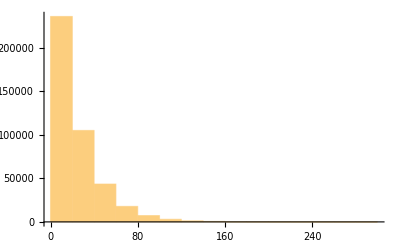

```mathematica
Histogram[qq]
```

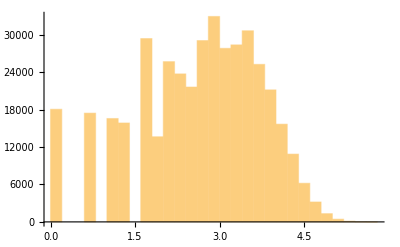

```mathematica
Histogram[Map[Log,qq]]
```

```mathematica
ListPlot[Differences[Differences[qq]]]
```

-Graphics-

```mathematica
ListPlay[ExponentialMovingAverage[Differences[qq],1024],SampleRate->4096]
```

$Aborted

```mathematica
ListPlay[Abs[Map[Sign[{Re[#],Im[#]}[[1]]]*Norm[{Re[#],Im[#]}]&,Fourier[qq]]],SampleRate->4096]
```

-Graphics-

```mathematica
ListPlay[Abs[Map[Im,Fourier[qq]]-Map[Re,Fourier[qq]]],SampleRate->4096]
```

-Graphics-

```mathematica
ListPlay[Map[Re,Fourier[qq]]]
```

-Graphics-

```mathematica
Log2[2000000000]//N
```

30.8974

```mathematica
2^31
```

2147483648

```mathematica
Timing[PrimePi[2000000000]]
```

{0.005736,98222287}

```mathematica
Prime[1]
```

2

```mathematica
Prime[6]
```

13

```mathematica
Product[Prime[i],{i,1,6}]
```

30030

```mathematica
17*30030
```

510510

```mathematica
ch[n_]:=Block[{prim=Product[Prime[j],{j,1,n}]},
Sum[Boole[And@@Table[CoprimeQ[i+prim,Prime[j]],{j,1,n}]],{i,0,prim-1}]/prim]
```

```mathematica
Product[Prime[j],{j,1,9}]
```

223092870

```mathematica
2^31
```

2147483648

```mathematica
Monitor[Table[ch[k],{k,2,8}],{k,j,i}]
```

{1/3,4/15,8/35,16/77,192/1001,3072/17017,55296/323323}

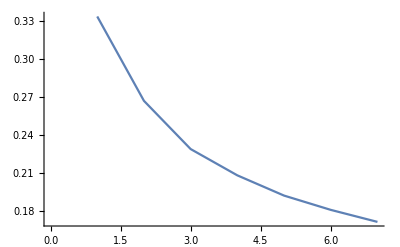

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
192/1001//N
```

0.191808

```mathematica
55296/323323//N
```

0.171024

```mathematica
Prime[6]
```

13

```mathematica
Total[Map[Boole[PrimeQ[#]]&,gs]]
```

3242

```mathematica
gs=Select[Table[i*Boole[And@@Table[CoprimeQ[i+30030,Prime[j]],{j,1,6}]],{i,0,30030-1}],#≠0&]
```

{1,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,289,293,307,311,313,317,323,331,337,347,349,353,359,361,367,373,379,383,389,391,397,401,409,419,421,431,433,437,439,443,449,457,461,463,467,479,487,491,493,499,503,509,521,523,527,529,541,547,551,557,563,569,571,577,587,589,593,599,601,607,613,617,619,629,631,641,643,647,653,659,661,667,673,677,683,691,697,701,703,709,713,719,727,731,733,739,743,751,757,761,769,773,779,787,797,799,809,811,817,821,823,827,829,839,841,851,853,857,859,863,877,881,883,887,893,899,901,907,911,919,929,937,941,943,947,953,961,967,971,977,983,989,991,997,1003,1007,1009,1013,1019,1021,1031,1033,1037,1039,1049,1051,1061,1063,1069,1073,1081,1087,1091,1093,1097,1103,1109,1117,1121,1123,1129,1139,1147,1151,1153,1159,1163,1171,1181,1187,1189,1193,1201,1207,1213,1217,1219,1223,1229,1231,1237,1241,1247,1249,1259,1271,1273,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1333,1343,1349,1357,1361,1363,1367,1369,1373,1381,1387,1399,1403,1409,1411,1423,1427,1429,1433,1439,1447,1451,1453,1457,1459,1471,1481,1483,1487,1489,1493,1499,1501,1511,1513,1517,1523,1531,1537,1541,1543,1549,1553,1559,1567,1571,1577,1579,1583,1591,1597,1601,1607,1609,1613,1619,1621,1627,1633,1637,1643,1649,1657,1663,1667,1669,1679,1681,1691,1693,1697,1699,1709,1711,1717,1721,1723,1733,1739,1741,1747,1751,1753,1759,1763,1769,1777,1783,1787,1789,1801,1811,1817,1819,1823,1829,1831,1843,1847,1849,1853,1861,1867,1871,1873,1877,1879,1889,1891,1901,1907,1909,1913,1919,1921,1927,1931,1933,1943,1949,1951,1957,1961,1973,1979,1987,1993,1997,1999,2003,2011,2017,2021,2027,2029,2033,2039,2047,2053,2059,2063,2069,2071,2077,2081,2083,2087,2089,2099,2111,2113,2117,2129,2131,2137,2141,2143,2147,2153,2159,2161,2173,2179,2183,2201,2203,2207,2209,2213,2221,2227,2231,2237,2239,2243,2251,2257,2263,2267,2269,2273,2279,2281,2287,2291,2293,2297,2309,2311,2323,2329,2333,2339,2341,2347,2351,2357,2363,2369,2371,2377,2381,2383,2389,2393,2399,2407,2411,2413,2417,2419,2423,2437,2441,2447,2449,2459,2461,2467,2473,2477,2479,2489,2491,2501,2503,2507,2521,2531,2533,2537,2539,2543,2549,2551,2557,2567,2573,2579,2581,2591,2593,2599,2603,2609,2617,2621,2623,2627,2633,2641,2647,2657,2659,2663,2669,2671,2677,2683,2687,2689,2693,2699,2701,2707,2711,2713,2719,2729,2731,2741,2747,2749,2753,2759,2767,2771,2773,2777,2789,2791,2797,2801,2803,2809,2813,2819,2831,2833,2837,2839,2843,2851,2857,2861,2867,2869,2879,2881,2887,2897,2903,2909,2911,2917,2921,2923,2927,2929,2939,2941,2953,2957,2963,2969,2971,2983,2987,2993,2999,3001,3007,3011,3013,3019,3023,3037,3041,3043,3049,3053,3061,3067,3071,3077,3079,3083,3089,3097,3103,3109,3119,3121,3127,3131,3137,3139,3149,3151,3161,3163,3167,3169,3173,3181,3187,3191,3193,3197,3203,3209,3217,3221,3229,3233,3239,3247,3251,3253,3257,3259,3271,3277,3281,3287,3293,3299,3301,3307,3313,3317,3319,3323,3329,3331,3337,3343,3347,3349,3359,3361,3371,3373,3379,3383,3389,3391,3397,3401,3403,3407,3413,3427,3431,3433,3439,3449,3457,3461,3463,3467,3469,3473,3481,3491,3499,3503,3511,3517,3527,3529,3533,3539,3541,3547,3551,3557,3559,3569,3571,3581,3583,3587,3589,3593,3599,3607,3611,3613,3617,3623,3629,3631,3637,3643,3649,3659,3667,3671,3673,3677,3683,3691,3697,3701,3709,3713,3719,3721,3727,3733,3737,3739,3743,3749,3761,3763,3767,3769,3779,3781,3791,3793,3797,3799,3803,3811,3821,3823,3827,3833,3841,3847,3851,3853,3859,3863,3869,3877,3881,3889,3893,3901,3907,3911,3917,3919,3923,3929,3931,3937,3943,3947,3953,3959,3961,3967,3973,3977,3979,3989,4001,4003,4007,4009,4013,4019,4021,4027,4031,4033,4049,4051,4057,4061,4063,4073,4079,4087,4091,4093,4097,4099,4111,4117,4127,4129,4133,4139,4141,4153,4157,4159,4163,4171,4177,4181,4183,4187,4189,4201,4211,4217,4219,4223,4229,4231,4237,4241,4243,4247,4253,4259,4261,4267,4271,4273,4283,4289,4297,4307,4309,4313,4321,4327,4331,4337,4339,4343,4349,4351,4357,4363,4369,4373,4379,4387,4391,4393,4397,4399,4409,4421,4423,4427,4429,4439,4441,4447,4451,4453,4457,4463,4469,4471,4481,4483,4489,4493,4507,4513,4517,4519,4523,4531,4541,4547,4549,4553,4559,4561,4567,4573,4577,4579,4583,4591,4597,4601,4603,4607,4619,4621,4633,4637,4639,4643,4649,4651,4657,4661,4663,4673,4679,4681,4687,4691,4699,4703,4709,4717,4721,4723,4727,4729,4733,4747,4751,4757,4759,4769,4777,4783,4787,4789,4793,4799,4801,4811,4813,4817,4819,4831,4841,4843,4847,4853,4859,4861,4867,4871,4877,4883,4889,4891,4897,4903,4909,4913,4919,4931,4933,4937,4943,4951,4957,4967,4969,4973,4981,4987,4993,4997,4999,5003,5009,5011,5017,5021,5023,5029,5039,5041,5051,5053,5059,5063,5069,5077,5081,5087,5099,5101,5107,5111,5113,5119,5123,5129,5141,5143,5147,5149,5153,5167,5171,5177,5179,5183,5189,5191,5197,5207,5209,5219,5221,5227,5231,5233,5237,5249,5251,5261,5263,5267,5273,5279,5281,5287,5293,5297,5303,5309,5311,5321,5323,5329,5333,5339,5347,5351,5353,5359,5363,5371,5377,5381,5387,5389,5393,5399,5407,5413,5417,5419,5429,5431,5437,5441,5443,5449,5459,5461,5471,5477,5479,5483,5491,5497,5501,5503,5507,5513,5519,5521,5527,5531,5539,5543,5549,5557,5561,5563,5567,5569,5573,5581,5587,5591,5597,5609,5611,5617,5623,5627,5633,5639,5641,5647,5651,5653,5657,5659,5669,5671,5683,5689,5693,5699,5701,5711,5713,5717,5723,5729,5737,5741,5743,5749,5767,5771,5773,5777,5779,5783,5791,5801,5807,5809,5813,5821,5827,5833,5839,5843,5849,5851,5857,5861,5867,5869,5879,5881,5891,5893,5897,5899,5903,5909,5911,5917,5921,5923,5927,5933,5939,5947,5953,5959,5963,5969,5977,5981,5983,5987,5989,6001,6007,6011,6023,6029,6031,6037,6043,6047,6049,6053,6059,6067,6073,6077,6079,6089,6091,6101,6103,6107,6109,6113,6119,6121,6131,6133,6137,6143,6151,6157,6161,6163,6169,6173,6179,6187,6191,6197,6199,6203,6211,6217,6221,6229,6233,6239,6241,6247,6257,6263,6269,6271,6277,6283,6287,6289,6299,6301,6311,6313,6317,6319,6323,6329,6337,6341,6343,6353,6359,6361,6367,6371,6373,6379,6389,6397,6401,6403,6407,6421,6427,6431,6437,6439,6443,6449,6451,6463,6467,6469,6473,6481,6491,6493,6497,6499,6509,6511,6521,6527,6529,6533,6541,6547,6551,6553,6557,6563,6569,6571,6577,6581,6583,6593,6599,6607,6613,6619,6623,6631,6637,6641,6647,6649,6653,6659,6661,6667,6673,6679,6683,6689,6691,6697,6701,6703,6707,6709,6719,6731,6733,6737,6739,6749,6751,6757,6761,6763,6767,6779,6781,6791,6793,6803,6817,6821,6823,6827,6829,6833,6841,6847,6857,6859,6863,6869,6871,6883,6887,6889,6893,6899,6901,6907,6911,6913,6917,6931,6943,6947,6949,6953,6959,6961,6967,6971,6973,6977,6983,6989,6991,6997,7001,7003,7009,7013,7019,7027,7031,7037,7039,7043,7057,7061,7067,7069,7079,7081,7087,7093,7097,7099,7103,7109,7121,7123,7127,7129,7141,7151,7153,7157,7159,7169,7171,7177,7181,7187,7193,7199,7201,7207,7211,7213,7219,7223,7229,7237,7243,7247,7253,7261,7277,7279,7283,7289,7291,7297,7303,7307,7309,7313,7321,7327,7331,7333,7339,7349,7351,7361,7363,7367,7369,7373,7379,7387,7391,7393,7409,7411,7417,7421,7429,7433,7439,7451,7453,7457,7459,7463,7471,7477,7481,7487,7489,7493,7499,7507,7517,7519,7523,7529,7531,7537,7541,7543,7547,7549,7559,7561,7571,7573,7577,7583,7589,7591,7597,7603,7607,7613,7619,7621,7627,7633,7639,7643,7649,7661,7663,7669,7673,7681,7687,7691,7697,7699,7703,7717,7723,7727,7729,7739,7741,7747,7751,7753,7757,7759,7769,7771,7781,7783,7789,7793,7801,7807,7811,7817,7823,7829,7831,7837,7841,7849,7853,7859,7867,7871,7873,7877,7879,7883,7897,7901,7907,7913,7919,7921,7927,7933,7937,7939,7949,7951,7957,7961,7963,7967,7979,7981,7991,7993,7999,8003,8009,8011,8017,8023,8027,8033,8039,8051,8053,8059,8069,8077,8081,8083,8087,8089,8093,8101,8111,8117,8119,8123,8131,8137,8143,8147,8149,8153,8159,8161,8167,8171,8179,8189,8191,8201,8207,8209,8213,8219,8221,8227,8231,8233,8237,8243,8249,8251,8257,8263,8269,8273,8279,8287,8291,8293,8297,8299,8303,8311,8317,8321,8329,8339,8341,8347,8353,8357,8363,8369,8377,8381,8383,8387,8389,8399,8401,8413,8417,8419,8423,8429,8431,8441,8443,8447,8453,8461,8467,8471,8473,8479,8483,8497,8501,8507,8509,8513,8521,8527,8531,8537,8539,8543,8549,8551,8557,8563,8573,8579,8581,8587,8597,8599,8609,8611,8621,8623,8627,8629,8633,8639,8641,8647,8651,8653,8663,8669,8677,8681,8683,8689,8693,8699,8707,8711,8713,8717,8719,8731,8737,8741,8747,8753,8759,8761,8773,8777,8779,8783,8791,8797,8803,8807,8809,8819,8821,8831,8837,8839,8843,8849,8851,8857,8861,8863,8867,8873,8881,8887,8891,8893,8903,8909,8917,8923,8927,8929,8933,8941,8947,8951,8959,8963,8969,8971,8977,8989,8993,8999,9001,9007,9011,9013,9017,9019,9029,9041,9043,9047,9049,9059,9067,9071,9073,9077,9083,9089,9091,9101,9103,9109,9127,9131,9133,9137,9143,9151,9157,9161,9167,9169,9173,9179,9181,9187,9193,9197,9199,9203,9209,9211,9221,9223,9227,9239,9241,9253,9257,9259,9263,9271,9277,9281,9283,9287,9293,9299,9301,9307,9311,9313,9319,9323,9329,9337,9341,9343,9349,9353,9367,9371,9377,9379,9389,9391,9397,9403,9407,9409,9413,9419,9421,9431,9433,9437,9439,9461,9463,9467,9469,9473,9479,9481,9487,9491,9497,9509,9511,9517,9521,9523,9533,9539,9547,9551,9553,9557,9563,9571,9577,9587,9589,9593,9599,9601,9613,9617,9619,9623,9629,9631,9637,9641,9643,9649,9661,9671,9673,9677,9679,9683,9689,9697,9701,9703,9707,9719,9721,9727,9731,9733,9739,9743,9749,9761,9767,9769,9773,9781,9787,9791,9797,9799,9803,9809,9811,9817,9827,9829,9833,9839,9847,9851,9853,9857,9859,9869,9871,9881,9883,9887,9899,9901,9907,9913,9917,9923,9929,9931,9937,9941,9943,9949,9953,9959,9967,9973,9979,9983,9991,10001,10007,10009,10013,10019,10027,10033,10037,10039,10051,10057,10061,10063,10067,10069,10079,10081,10091,10093,10097,10099,10103,10111,10117,10121,10123,10133,10139,10141,10147,10151,10159,10163,10169,10177,10181,10183,10187,10189,10193,10201,10207,10211,10217,10223,10229,10237,10243,10247,10249,10253,10259,10261,10267,10271,10273,10277,10279,10289,10291,10301,10303,10313,10319,10321,10327,10331,10333,10337,10343,10349,10357,10363,10369,10379,10391,10393,10397,10399,10403,10411,10421,10427,10429,10433,10441,10447,10453,10457,10459,10463,10469,10471,10477,10481,10487,10489,10499,10501,10511,10513,10519,10523,10529,10531,10537,10541,10547,10553,10559,10561,10567,10573,10579,10583,10589,10597,10601,10603,10607,10609,10613,10627,10631,10639,10643,10649,10651,10657,10663,10667,10669,10679,10687,10691,10693,10697,10709,10711,10721,10723,10727,10729,10733,10739,10741,10753,10757,10763,10771,10781,10783,10789,10793,10799,10807,10811,10817,10819,10823,10831,10837,10841,10847,10849,10853,10859,10861,10867,10873,10877,10883,10889,10891,10897,10903,10909,10919,10921,10931,10937,10939,10943,10949,10951,10957,10961,10963,10973,10979,10981,10987,10991,10993,10999,11003,11009,11017,11021,11023,11027,11029,11041,11047,11051,11057,11059,11069,11071,11083,11087,11093,11101,11107,11111,11113,11117,11119,11129,11131,11147,11149,11153,11159,11161,11171,11173,11177,11183,11189,11191,11197,11201,11203,11213,11227,11233,11237,11239,11243,11251,11257,11261,11267,11269,11273,11279,11281,11287,11293,11299,11303,11309,11311,11317,11321,11327,11329,11339,11351,11353,11357,11359,11369,11371,11377,11381,11383,11387,11393,11399,11411,11413,11419,11423,11437,11441,11443,11447,11449,11461,11467,11471,11477,11483,11489,11491,11497,11503,11507,11509,11513,11519,11521,11527,11533,11537,11549,11551,11563,11567,11569,11573,11579,11581,11587,11591,11593,11597,11603,11611,11617,11621,11623,11629,11633,11639,11647,11651,11653,11657,11659,11663,11677,11681,11689,11699,11701,11707,11717,11719,11723,11729,11731,11741,11743,11747,11749,11761,11771,11773,11777,11779,11783,11789,11797,11801,11807,11813,11819,11821,11827,11831,11833,11839,11849,11857,11861,11863,11867,11873,11881,11887,11897,11899,11903,11909,11911,11917,11923,11927,11929,11933,11939,11941,11951,11953,11959,11969,11971,11981,11983,11987,11989,11993,12007,12011,12013,12017,12029,12031,12037,12041,12043,12049,12053,12059,12071,12073,12079,12083,12091,12097,12101,12107,12109,12113,12119,12121,12127,12137,12139,12143,12149,12151,12157,12161,12163,12167,12169,12179,12191,12193,12197,12203,12209,12211,12217,12223,12227,12239,12241,12247,12251,12253,12263,12269,12277,12281,12283,12289,12293,12301,12307,12317,12319,12323,12329,12343,12347,12349,12359,12361,12367,12371,12373,12377,12379,12391,12401,12403,12407,12409,12413,12421,12427,12431,12433,12437,12443,12449,12451,12457,12461,12469,12473,12479,12487,12491,12497,12499,12503,12511,12517,12521,12527,12533,12539,12541,12547,12553,12557,12559,12563,12569,12577,12581,12583,12587,12589,12599,12601,12611,12613,12619,12629,12631,12637,12641,12643,12647,12653,12659,12667,12671,12673,12679,12689,12697,12703,12707,12709,12713,12721,12731,12737,12739,12743,12751,12757,12763,12767,12769,12773,12781,12787,12791,12797,12799,12809,12811,12821,12823,12827,12829,12833,12839,12841,12847,12851,12853,12863,12869,12871,12877,12889,12893,12899,12907,12911,12913,12917,12919,12923,12931,12937,12941,12949,12953,12959,12967,12973,12977,12979,12983,12989,12997,13001,13003,13007,13009,13019,13021,13031,13033,13037,13043,13049,13051,13061,13063,13067,13073,13081,13087,13093,13099,13103,13109,13121,13127,13129,13133,13141,13147,13151,13157,13159,13163,13171,13177,13183,13187,13193,13199,13201,13207,13213,13217,13219,13229,13231,13241,13243,13249,13253,13259,13261,13267,13271,13283,13289,13291,13297,13301,13303,13309,13313,13319,13327,13331,13333,13337,13339,13357,13361,13367,13369,13373,13379,13381,13393,13397,13399,13411,13417,13421,13423,13427,13439,13441,13451,13457,13459,13463,13469,13471,13477,13483,13487,13493,13499,13501,13511,13513,13523,13529,13537,13543,13547,13549,13553,13561,13567,13571,13577,13579,13583,13589,13591,13597,13603,13609,13613,13619,13621,13627,13631,13633,13639,13649,13661,13667,13669,13679,13681,13687,13691,13693,13697,13703,13709,13711,13721,13723,13729,13733,13747,13751,13753,13757,13759,13763,13771,13777,13781,13787,13789,13799,13801,13807,13813,13817,13823,13829,13831,13837,13841,13843,13847,13859,13861,13873,13877,13879,13883,13889,13891,13901,13903,13907,13913,13919,13921,13927,13931,13933,13939,13943,13957,13961,13963,13967,13969,13973,13987,13991,13997,13999,14009,14011,14017,14023,14029,14033,14039,14041,14051,14057,14059,14071,14081,14083,14087,14089,14093,14099,14101,14107,14111,14117,14123,14129,14137,14141,14143,14149,14153,14159,14167,14171,14173,14177,14191,14197,14207,14213,14219,14221,14227,14233,14237,14239,14243,14249,14251,14257,14263,14269,14279,14281,14291,14293,14297,14299,14303,14309,14317,14321,14323,14327,14341,14347,14351,14353,14359,14363,14369,14381,14383,14387,14389,14393,14401,14407,14411,14419,14423,14429,14431,14437,14447,14449,14453,14459,14461,14467,14471,14473,14477,14479,14489,14491,14501,14503,14507,14513,14519,14527,14533,14537,14543,14549,14551,14557,14561,14563,14569,14579,14587,14591,14593,14603,14611,14617,14621,14627,14629,14633,14639,14647,14653,14657,14659,14669,14671,14681,14683,14687,14689,14699,14701,14711,14713,14717,14719,14723,14731,14737,14741,14743,14747,14753,14759,14761,14767,14771,14779,14783,14789,14797,14801,14803,14809,14813,14821,14827,14831,14837,14843,14849,14851,14857,14863,14867,14869,14873,14879,14881,14887,14891,14893,14897,14899,14909,14921,14923,14929,14933,14939,14941,14947,14951,14953,14957,14969,14977,14981,14983,14999,15007,15011,15013,15017,15019,15023,15031,15047,15049,15053,15061,15073,15077,15079,15083,15089,15091,15097,15101,15107,15109,15121,15131,15133,15137,15139,15143,15149,15151,15157,15161,15163,15167,15173,15179,15181,15187,15193,15199,15203,15209,15217,15221,15227,15229,15233,15241,15247,15251,15259,15263,15269,15271,15277,15283,15287,15289,15293,15299,15307,15311,15313,15317,15319,15329,15331,15341,15343,15347,15349,15359,15361,15371,15373,15377,15383,15391,15397,15401,15403,15409,15413,15419,15427,15437,15439,15443,15451,15461,15467,15469,15473,15479,15481,15487,15493,15497,15503,15511,15517,15523,15527,15529,15539,15541,15551,15553,15557,15559,15563,15569,15571,15577,15581,15583,15593,15599,15601,15607,15611,15619,15623,15629,15637,15641,15643,15647,15649,15661,15667,15671,15677,15679,15683,15689,15703,15707,15709,15713,15721,15727,15731,15733,15737,15739,15749,15751,15761,15767,15773,15779,15781,15787,15791,15793,15797,15803,15809,15811,15817,15823,15833,15839,15853,15857,15859,15863,15871,15877,15881,15887,15889,15893,15901,15907,15913,15919,15923,15929,15931,15937,15941,15943,15947,15949,15959,15971,15973,15979,15989,15991,15997,16001,16007,16013,16019,16021,16031,16033,16039,16043,16057,16061,16063,16067,16069,16073,16087,16091,16097,16099,16103,16109,16111,16117,16123,16127,16129,16139,16141,16147,16151,16153,16157,16169,16171,16183,16187,16189,16193,16199,16201,16207,16213,16217,16223,16229,16231,16241,16243,16249,16253,16259,16267,16271,16273,16277,16279,16283,16297,16301,16307,16309,16319,16321,16327,16333,16337,16339,16343,16349,16351,16361,16363,16369,16381,16391,16397,16399,16403,16409,16411,16417,16421,16427,16433,16439,16441,16447,16451,16453,16459,16463,16469,16477,16481,16483,16487,16493,16501,16507,16517,16519,16529,16531,16537,16543,16547,16553,16559,16561,16567,16571,16573,16579,16589,16591,16603,16607,16609,16613,16619,16631,16633,16637,16649,16651,16657,16661,16663,16669,16673,16691,16693,16697,16699,16703,16711,16717,16721,16727,16729,16733,16739,16741,16747,16759,16763,16769,16771,16777,16781,16787,16789,16799,16801,16811,16813,16817,16823,16829,16831,16837,16843,16847,16853,16859,16867,16871,16873,16879,16883,16889,16897,16901,16903,16909,16921,16927,16931,16937,16943,16949,16957,16963,16967,16969,16979,16981,16987,16993,16997,16999,17009,17011,17021,17023,17027,17029,17033,17041,17047,17051,17053,17057,17063,17071,17077,17081,17089,17093,17099,17107,17111,17113,17117,17119,17123,17131,17137,17141,17153,17159,17161,17167,17177,17179,17183,17189,17191,17197,17201,17203,17207,17209,17219,17221,17231,17233,17239,17243,17249,17257,17261,17263,17267,17273,17279,17287,17291,17293,17299,17309,17317,17321,17323,17327,17333,17341,17351,17357,17359,17363,17371,17377,17383,17387,17389,17393,17399,17401,17411,17417,17419,17429,17431,17441,17443,17447,17449,17453,17461,17467,17471,17473,17477,17483,17489,17491,17497,17503,17509,17513,17519,17527,17531,17533,17539,17543,17551,17557,17561,17569,17573,17579,17581,17587,17593,17597,17599,17603,17609,17617,17621,17623,17627,17629,17639,17651,17653,17657,17659,17663,17669,17671,17681,17683,17687,17701,17707,17711,17713,17723,17729,17737,17741,17747,17749,17753,17761,17767,17777,17779,17783,17789,17791,17803,17807,17813,17819,17821,17827,17833,17837,17839,17851,17861,17863,17867,17869,17873,17879,17881,17887,17891,17893,17903,17909,17911,17917,17921,17923,17929,17933,17939,17947,17951,17957,17959,17971,17977,17981,17987,17989,17993,17999,18001,18013,18017,18019,18023,18037,18041,18043,18047,18049,18059,18061,18071,18077,18079,18089,18091,18097,18101,18103,18107,18113,18119,18121,18127,18131,18133,18143,18149,18157,18163,18167,18169,18173,18181,18191,18197,18199,18203,18209,18211,18217,18223,18229,18233,18241,18247,18251,18253,18257,18259,18269,18281,18283,18287,18289,18299,18301,18307,18311,18313,18323,18329,18331,18341,18349,18353,18367,18371,18373,18377,18379,18383,18391,18397,18401,18407,18409,18413,18419,18427,18433,18437,18439,18443,18449,18451,18457,18461,18463,18467,18479,18481,18493,18497,18503,18509,18511,18517,18521,18523,18527,18533,18539,18541,18547,18553,18559,18563,18569,18581,18583,18587,18589,18593,18607,18611,18617,18619,18631,18637,18643,18647,18649,18653,18659,18661,18671,18673,18677,18679,18691,18701,18703,18709,18713,18719,18721,18727,18731,18737,18743,18749,18751,18757,18761,18763,18769,18773,18779,18787,18791,18793,18797,18803,18817,18827,18829,18833,18839,18841,18847,18853,18857,18859,18869,18871,18877,18881,18883,18899,18901,18911,18913,18917,18919,18923,18929,18937,18943,18947,18959,18961,18971,18973,18979,18983,18989,19001,19003,19007,19009,19013,19021,19027,19031,19037,19039,19043,19049,19051,19057,19067,19069,19073,19079,19081,19087,19091,19093,19099,19109,19111,19121,19127,19133,19139,19141,19147,19153,19157,19163,19169,19171,19177,19181,19183,19189,19193,19199,19207,19211,19213,19219,19223,19231,19237,19241,19247,19249,19259,19267,19273,19277,19289,19291,19297,19301,19303,19307,19309,19319,19321,19333,19337,19339,19343,19351,19361,19363,19367,19373,19379,19381,19387,19391,19399,19403,19417,19421,19423,19427,19429,19433,19441,19447,19451,19457,19463,19469,19471,19477,19483,19489,19493,19499,19501,19507,19511,19517,19519,19529,19531,19541,19543,19549,19553,19559,19561,19567,19571,19573,19577,19583,19589,19597,19601,19603,19609,19619,19627,19631,19633,19637,19639,19651,19661,19667,19673,19681,19687,19693,19697,19699,19703,19709,19711,19717,19727,19729,19739,19741,19751,19753,19757,19759,19763,19769,19771,19777,19781,19783,19787,19793,19801,19807,19813,19819,19823,19829,19837,19841,19843,19847,19849,19853,19861,19867,19871,19879,19883,19889,19891,19897,19907,19909,19913,19919,19927,19931,19933,19937,19939,19949,19951,19961,19963,19967,19969,19973,19979,19991,19993,19997,20003,20011,20017,20021,20023,20029,20039,20047,20051,20057,20063,20071,20077,20081,20087,20089,20093,20099,20101,20107,20113,20117,20123,20129,20131,20143,20147,20149,20159,20161,20171,20173,20177,20179,20183,20191,20197,20201,20203,20213,20219,20221,20227,20231,20233,20239,20243,20249,20257,20261,20263,20269,20281,20287,20291,20297,20299,20303,20309,20311,20323,20327,20329,20333,20341,20347,20351,20353,20357,20359,20369,20381,20387,20389,20393,20399,20401,20407,20411,20413,20417,20429,20431,20437,20441,20443,20453,20459,20467,20473,20477,20479,20483,20491,20497,20507,20509,20513,20519,20521,20533,20539,20543,20549,20551,20557,20561,20563,20567,20569,20591,20593,20597,20599,20609,20611,20617,20621,20623,20627,20633,20639,20641,20651,20653,20659,20663,20677,20681,20687,20689,20693,20701,20707,20711,20717,20719,20723,20729,20731,20737,20743,20747,20749,20753,20759,20767,20771,20773,20777,20789,20791,20803,20807,20809,20819,20821,20827,20831,20833,20837,20843,20849,20851,20857,20861,20863,20869,20873,20879,20887,20893,20897,20899,20903,20921,20927,20929,20939,20941,20947,20953,20957,20959,20963,20971,20981,20983,20987,20989,21001,21011,21013,21017,21019,21023,21029,21031,21037,21041,21053,21059,21061,21067,21071,21079,21083,21089,21097,21101,21103,21107,21113,21121,21127,21137,21139,21143,21149,21157,21163,21167,21169,21173,21179,21181,21187,21191,21193,21199,21209,21211,21221,21223,21227,21233,21239,21247,21251,21253,21257,21269,21271,21277,21283,21289,21293,21299,21311,21313,21317,21319,21323,21331,21337,21341,21347,21349,21353,21361,21367,21377,21379,21383,21389,21391,21397,21401,21403,21407,21409,21419,21421,21431,21433,21443,21449,21451,21457,21467,21473,21479,21481,21487,21491,21493,21499,21503,21509,21517,21521,21523,21529,21533,21547,21551,21557,21559,21563,21569,21577,21583,21587,21589,21599,21601,21607,21611,21613,21617,21629,21631,21641,21643,21647,21649,21653,21661,21667,21673,21677,21683,21689,21691,21701,21709,21713,21719,21727,21731,21733,21737,21739,21743,21751,21757,21761,21767,21773,21779,21781,21787,21793,21797,21799,21803,21809,21811,21817,21821,21823,21829,21839,21841,21851,21859,21863,21869,21871,21877,21881,21883,21887,21893,21899,21907,21911,21913,21919,21929,21937,21941,21943,21947,21949,21953,21961,21971,21977,21979,21991,21997,22003,22007,22013,22019,22021,22027,22031,22037,22039,22049,22051,22063,22067,22069,22073,22079,22081,22091,22093,22097,22103,22109,22111,22117,22123,22129,22133,22147,22151,22153,22157,22159,22163,22171,22177,22181,22189,22193,22199,22201,22207,22213,22219,22223,22229,22237,22241,22247,22249,22259,22261,22271,22273,22277,22279,22283,22289,22291,22301,22303,22307,22313,22327,22331,22333,22339,22343,22349,22357,22361,22367,22369,22381,22387,22391,22397,22403,22409,22411,22417,22423,22427,22433,22439,22441,22447,22453,22457,22459,22469,22471,22481,22483,22487,22489,22493,22499,22501,22507,22511,22513,22523,22531,22537,22541,22543,22549,22553,22559,22567,22571,22573,22577,22579,22591,22597,22601,22609,22613,22619,22621,22637,22639,22643,22651,22657,22661,22663,22667,22669,22679,22681,22691,22697,22699,22703,22709,22717,22721,22723,22727,22733,22739,22741,22747,22751,22753,22769,22777,22783,22787,22793,22801,22807,22811,22817,22819,22823,22829,22831,22837,22843,22849,22853,22859,22861,22871,22873,22877,22879,22889,22901,22903,22907,22909,22921,22927,22931,22933,22937,22943,22949,22951,22961,22963,22969,22973,22987,22991,22993,22999,23003,23011,23017,23021,23027,23029,23033,23039,23041,23047,23053,23057,23059,23063,23069,23071,23077,23081,23083,23087,23099,23113,23117,23119,23123,23129,23131,23137,23141,23143,23147,23159,23161,23167,23171,23173,23183,23189,23197,23201,23203,23207,23209,23213,23227,23237,23239,23249,23251,23263,23267,23269,23273,23279,23281,23291,23293,23297,23299,23311,23321,23323,23327,23329,23333,23339,23341,23347,23351,23357,23363,23369,23371,23377,23381,23383,23389,23393,23399,23407,23411,23417,23423,23431,23437,23447,23449,23453,23459,23461,23467,23473,23477,23479,23483,23489,23497,23501,23503,23509,23519,23521,23531,23533,23537,23539,23549,23557,23561,23563,23567,23579,23581,23587,23591,23593,23599,23603,23609,23623,23627,23629,23633,23641,23651,23657,23659,23663,23669,23671,23677,23687,23689,23693,23701,23707,23711,23713,23717,23719,23729,23731,23741,23743,23747,23753,23759,23761,23767,23773,23783,23789,23791,23797,23801,23809,23813,23819,23827,23831,23833,23839,23843,23851,23857,23861,23867,23869,23873,23879,23887,23893,23897,23899,23909,23911,23917,23921,23923,23927,23929,23939,23941,23951,23953,23957,23963,23971,23977,23981,23983,23987,23993,23999,24001,24007,24019,24023,24029,24041,24043,24047,24049,24053,24061,24067,24071,24077,24083,24091,24097,24103,24107,24109,24113,24119,24121,24127,24131,24133,24137,24139,24149,24151,24161,24163,24169,24173,24179,24181,24187,24191,24197,24203,24209,24217,24221,24223,24229,24239,24247,24251,24253,24257,24259,24263,24281,24287,24289,24293,24301,24307,24313,24317,24319,24329,24331,24337,24341,24347,24359,24361,24371,24373,24377,24379,24383,24389,24391,24397,24403,24407,24413,24419,24421,24433,24439,24443,24449,24457,24461,24463,24467,24469,24473,24481,24487,24491,24499,24503,24509,24511,24517,24523,24527,24529,24533,24539,24547,24551,24553,24559,24569,24571,24581,24587,24589,24593,24599,24601,24611,24613,24617,24623,24631,24637,24641,24643,24649,24653,24659,24667,24671,24677,24679,24683,24691,24697,24701,24707,24709,24719,24721,24727,24733,24737,24743,24749,24751,24757,24763,24767,24769,24779,24781,24793,24797,24799,24803,24809,24811,24821,24823,24833,24839,24841,24847,24851,24853,24859,24863,24877,24881,24883,24887,24889,24901,24907,24911,24917,24919,24923,24929,24931,24943,24949,24953,24961,24967,24971,24977,24979,24989,24991,25001,25007,25009,25013,25019,25021,25027,25031,25033,25037,25043,25049,25057,25061,25063,25073,25079,25087,25093,25097,25099,25111,25117,25121,25127,25133,25139,25141,25147,25153,25159,25163,25169,25171,25177,25183,25187,25189,25199,25211,25213,25217,25219,25229,25231,25237,25241,25243,25247,25253,25261,25271,25273,25279,25283,25297,25301,25303,25307,25309,25313,25321,25327,25331,25339,25343,25349,25351,25357,25367,25369,25373,25379,25381,25387,25391,25393,25397,25409,25411,25423,25427,25429,25433,25439,25447,25451,25453,25457,25463,25469,25471,25477,25481,25483,25489,25499,25507,25511,25513,25517,25523,25537,25541,25547,25549,25559,25561,25567,25573,25577,25579,25583,25589,25591,25601,25603,25607,25609,25621,25631,25633,25637,25639,25643,25651,25657,25661,25667,25673,25679,25681,25687,25691,25693,25699,25703,25709,25717,25721,25723,25733,25741,25747,25757,25759,25763,25769,25771,25777,25783,25787,25789,25793,25799,25801,25807,25811,25813,25819,25829,25841,25843,25847,25849,25853,25859,25867,25871,25873,25877,25889,25891,25897,25901,25903,25913,25919,25931,25933,25937,25939,25943,25951,25957,25967,25969,25973,25979,25981,25997,25999,26003,26009,26011,26017,26021,26023,26027,26029,26041,26051,26053,26057,26063,26069,26071,26077,26083,26087,26093,26099,26101,26107,26111,26113,26119,26123,26129,26137,26141,26149,26153,26161,26167,26171,26177,26179,26183,26189,26197,26203,26207,26209,26219,26227,26231,26233,26237,26239,26249,26251,26261,26263,26267,26269,26281,26287,26291,26293,26297,26303,26309,26311,26317,26321,26329,26333,26339,26347,26353,26357,26359,26363,26371,26381,26387,26393,26399,26401,26407,26413,26417,26419,26423,26431,26437,26441,26443,26447,26449,26459,26461,26471,26473,26479,26483,26489,26491,26497,26501,26503,26513,26519,26527,26531,26539,26549,26557,26561,26563,26567,26569,26573,26581,26591,26597,26599,26603,26617,26623,26627,26629,26633,26639,26641,26647,26651,26657,26659,26669,26671,26681,26683,26687,26693,26699,26701,26707,26711,26713,26717,26723,26729,26731,26737,26743,26749,26753,26759,26771,26773,26777,26779,26783,26791,26797,26801,26809,26813,26821,26827,26833,26837,26839,26843,26849,26857,26861,26863,26867,26869,26879,26881,26891,26893,26899,26903,26909,26911,26921,26927,26933,26941,26947,26951,26953,26959,26963,26969,26977,26981,26987,26989,26993,27007,27011,27017,27019,27023,27029,27031,27037,27043,27047,27059,27061,27067,27073,27077,27089,27091,27101,27103,27107,27109,27113,27119,27121,27127,27133,27143,27149,27151,27161,27163,27169,27173,27179,27187,27191,27193,27197,27199,27211,27217,27221,27227,27229,27233,27239,27241,27253,27257,27259,27263,27271,27277,27281,27283,27289,27299,27301,27311,27317,27319,27323,27329,27331,27337,27341,27343,27347,27353,27359,27361,27367,27371,27373,27383,27389,27397,27403,27407,27409,27413,27421,27427,27431,27437,27439,27449,27451,27457,27463,27473,27479,27481,27487,27491,27493,27497,27499,27509,27523,27527,27529,27539,27541,27551,27553,27557,27563,27569,27571,27581,27583,27589,27593,27607,27611,27613,27617,27619,27623,27631,27637,27641,27647,27649,27653,27659,27661,27667,27673,27679,27683,27689,27691,27697,27701,27707,27719,27721,27733,27737,27739,27743,27749,27751,27757,27761,27763,27767,27773,27779,27787,27791,27793,27799,27803,27809,27817,27821,27823,27827,27829,27847,27851,27857,27869,27871,27877,27883,27887,27889,27893,27899,27901,27913,27917,27919,27931,27941,27943,27947,27949,27953,27959,27961,27967,27971,27977,27983,27991,27997,28001,28003,28009,28013,28019,28027,28031,28033,28037,28043,28051,28057,28069,28073,28079,28081,28087,28097,28099,28103,28109,28111,28117,28121,28123,28129,28139,28141,28151,28153,28157,28159,28163,28169,28177,28181,28183,28187,28199,28201,28207,28211,28213,28219,28229,28241,28243,28247,28253,28261,28267,28271,28277,28279,28283,28289,28291,28297,28307,28309,28313,28319,28321,28331,28333,28337,28339,28349,28351,28361,28363,28367,28373,28381,28387,28393,28397,28403,28409,28411,28417,28421,28423,28429,28433,28439,28447,28451,28453,28459,28463,28471,28477,28481,28487,28489,28493,28499,28507,28513,28517,28519,28529,28531,28537,28541,28543,28547,28549,28559,28571,28573,28577,28579,28583,28591,28597,28601,28603,28607,28619,28621,28627,28631,28643,28649,28657,28661,28663,28667,28669,28673,28681,28687,28697,28703,28709,28711,28723,28727,28729,28733,28739,28741,28747,28751,28753,28757,28759,28771,28781,28783,28789,28793,28799,28801,28807,28811,28813,28817,28823,28829,28837,28841,28843,28849,28859,28867,28871,28877,28879,28883,28891,28901,28907,28909,28913,28921,28927,28933,28937,28939,28943,28949,28957,28961,28967,28969,28979,28981,28991,28993,28997,28999,29009,29011,29017,29021,29023,29027,29033,29039,29041,29047,29053,29059,29063,29069,29077,29083,29087,29089,29093,29101,29111,29119,29123,29129,29131,29137,29143,29147,29149,29153,29167,29171,29173,29177,29179,29189,29191,29201,29203,29207,29209,29213,29219,29221,29231,29233,29243,29251,29257,29261,29269,29273,29279,29287,29291,29297,29299,29303,29311,29317,29321,29327,29329,29333,29339,29347,29353,29357,29363,29369,29371,29377,29383,29387,29389,29399,29401,29411,29413,29417,29423,29429,29431,29437,29441,29443,29453,29459,29461,29467,29473,29479,29483,29489,29501,29503,29507,29509,29521,29527,29531,29537,29539,29543,29551,29563,29567,29569,29573,29581,29587,29591,29593,29597,29599,29609,29611,29621,29629,29633,29639,29641,29647,29651,29657,29663,29669,29671,29677,29681,29683,29693,29699,29707,29713,29717,29719,29723,29737,29741,29747,29749,29753,29759,29761,29767,29773,29779,29789,29791,29797,29801,29803,29807,29819,29831,29833,29837,29839,29849,29851,29857,29863,29867,29873,29879,29881,29891,29893,29899,29903,29917,29921,29923,29927,29929,29933,29941,29947,29951,29957,29959,29963,29969,29971,29977,29983,29987,29989,29993,29999,30001,30007,30011,30013,30029}

```mathematica
Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[Select[gs,PrimeQ]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]+30030,¬PrimeQ[#]&]
```

{}

```mathematica
Table[FactorInteger[gs[[i]]],{i,55,80}]//Column
```

{{281,1}}
{{283,1}}
{{17,2}}
{{293,1}}
{{307,1}}
{{311,1}}
{{313,1}}
{{317,1}}
{{17,1},{19,1}}
{{331,1}}
{{337,1}}
{{347,1}}
{{349,1}}
{{353,1}}
{{359,1}}
{{19,2}}
{{367,1}}
{{373,1}}
{{379,1}}
{{383,1}}
{{389,1}}
{{17,1},{23,1}}
{{397,1}}
{{401,1}}
{{409,1}}
{{419,1}}

```mathematica
Table[Boole[PrimeQ[30030*(8i)+gs[[1]]]],{i,0,1000}]
```

{0,0,0,0,1,1,0,0,1,0,1,0,0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,1,0,0,1,1,0,1,1,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,0,1,1,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,1,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,1,0,1,1,0,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,1,0,0,0,1,1,0,0,0,1,1,0,1,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,0,1,1,0,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,1,0,0,0,1,0,1,1,1,0,0,0,1,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0}

```mathematica
Prime[4648]^2
```

1999073521

```mathematica
PrimePi[√2000000000]
```

```mathematica
Prime[4648]
```

44711

```mathematica
ConstantArray[2,3]
```

{2,2,2}

```mathematica
seive[n_]:=Block[{list=ConstantArray[1,n],primes={}},
Do[If[list[[i]]≠0,primes=Append[primes,i];Do[list[[i*j]]=0,{j,1,Quotient[n,i]}],0],{i,2,n}];primes]
```

```mathematica
Flatten[Table[{i},{i,1,10}]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
gsmults[n_]:=Flatten[Table[30030*i+gs,{i,0,Quotient[n,30030]}]]
seive2[n_]:=Block[{list=gsmults[n],primes={},primoral=1,i=1},
While[list[[i]]≤n,If[CoprimeQ[list[[i]],primoral],primes=Append[primes,list[[i]]];primoral=primoral*list[[i]];i++,i++]];primes]
```

```mathematica
seive3[n_]:=Block[{list=gsmults[n],primes={},primoral=1,i=1},
```

```mathematica
Timing[Monitor[Product[Boole[Prime[i]<Mod[Primoral[i],2^64]],{i,100,10000}],i]]
```

{42.0871,1}

```mathematica
Prime[10000]^2
```

10968163441

```mathematica
Ceiling[Log2[Primoral[15]]]
```

60

```mathematica
Ceiling[Log2[Primoral[16,25]]]
```

62

```mathematica
First[Timing[seive[1000000]]]
```

21.6001

```mathematica
First[Timing[seive2[1000000]]]
```

41.3209

```mathematica
Monitor[Sum[{Boole[CoprimeQ[Mod[Primoral[PrimePi[gs[[i]]-1]],2^64],gs[[i]]]],Boole[PrimeQ[gs[[i]]]]},{i,1,5760}],i]
```

```mathematica
{5664,3242}/30030//N
```

{0.188611,0.107959}

```mathematica
{1,3242}/30030//N
```

{0.0000333,0.107959}

```mathematica
Monitor[Sum[{Boole[CoprimeQ[Primoral[PrimePi[1*30030+gs[[i]]-1]],1*30030+gs[[i]]]],Boole[PrimeQ[1*30030+gs[[i]]]]},{i,1,5760}],i]
```

{2814,2814}

```mathematica
Timing[Monitor[Sum[{Boole[CoprimeQ[Mod[Primoral[PrimePi[j*30030+gs[[j]]-1]],2^64],j*30030+gs[[i]]]],Boole[PrimeQ[1*30030+gs[[i]]]]},{j,1,1},{i,1,5760}],{j,i}]]
```

{14.5717,{5424,2814}}

```mathematica
Timing[Monitor[Sum[{Boole[CoprimeQ[Mod[Primoral[PrimePi[j*30030+gs[[j]]-1]],2^64],j*30030+gs[[i]]]],Boole[PrimeQ[1*30030+gs[[i]]]]},{j,2,2},{i,1,5760}],{j,i}]]
```

{29.7842,{5576,2814}}

```mathematica
(∑_(i=1)^10 2^i*(14.5717/2))/(60*6)
```

41.4079

```mathematica
Boole[CoprimeQ[1,Mod[∏_(k=1)^PrimePi[-1+List] Prime[k],18446744073709551616]]]
```

Boole[CoprimeQ[1,Mod[∏_(k=1)^PrimePi[-1+List] Prime[k],18446744073709551616]]]

```mathematica
Timing[ParallelSum[{Boole[CoprimeQ[Mod[Primoral[PrimePi[j*30030+gs[[i]]-1]],2^64],j*30030+gs[[i]]]],Boole[PrimeQ[1*30030+gs[[i]]]]},{j,0,10},{i,1,5760}]]
```

{45.5532,{62375,30954}}

```mathematica
{62375,30954}/(30030*11)//N
```

{0.188826,0.0937063}

```mathematica
tri[n_]:=n(n-1)/2
```

```mathematica
4*tri[50000]/tri[10000]//N
```

100.008

```mathematica
{0,2814}/30030//N
```

{0.,0.0937063}

5

```mathematica
Length[%]
```

5760

```mathematica
int gcd(int a,int b)
{int temp;
while (b≠0) {temp=a % b;
a=b;
b=temp;} return a;}
```

```mathematica
gcd[a0_,b0_]:=Block[{a=a0,b=b0,temp=0,count=0},
While[b≠0,count++;temp=Mod[a,b];a=b;b=temp];count]
```

```mathematica
mx[f_,a_,b_]:=Block[{max=-∞},
Do[max=Max[f[i],max],{i,a,b}];max]
```

```mathematica
mx[{1,2,5,3,1}[[#]]&,1,5]
```

5

```mathematica
Fibonacci[47]>2000000000
```

True

```mathematica
Fibonacci[90]
Log2[%]//N
```

2880067194370816120

61.3208

```mathematica
Primoral[j_]:=Product[Prime[k],{k,1,j}]
Primoral[i_,j_]:=Product[Prime[k],{k,i,j}]
```

```mathematica
Ceiling[Log2[Primoral[26]]]
```

128

```mathematica
Primoral[7,18]
```

3905707004975257109

```mathematica
Ceiling[Log2[Primoral[7,18]]]
```

62

```mathematica
Ceiling[Log2[Primoral[15]]]
```

60

```mathematica
Ceiling[Log2[Primoral[16,25]]]
```

62

```mathematica
Ceiling[Log2[Primoral[26,34]]]
```

62

```mathematica
Ceiling[Log2[Primoral[35,42]]]
```

59

```mathematica
nPrimoral[i_,j_]:=If[Ceiling[Log2[Primoral[i,j]]]>64,j-1,nPrimoral[i,j+1]]
nPrimoral[i_]:=nPrimoral[i,i+1]
```

```mathematica
nPrimoral[1]
```

15

```mathematica
NestList[nPrimoral[#+1]&,0,1000]
```

{0,15,25,34,42,50,58,65,72,79,86,93,100,106,112,118,124,130,136,142,148,154,160,166,172,178,184,190,196,202,208,214,220,226,232,238,244,250,256,261,266,271,276,281,286,291,296,301,306,311,316,321,326,331,336,341,346,351,356,361,366,371,376,381,386,391,396,401,406,411,416,421,426,431,436,441,446,451,456,461,466,471,476,481,486,491,496,501,506,511,516,521,526,531,536,541,546,551,556,561,566,571,576,581,586,591,596,601,606,611,616,621,626,631,636,641,646,651,656,661,666,671,676,681,686,691,696,701,706,711,716,721,726,731,736,741,746,751,756,761,766,771,776,781,786,791,796,801,806,811,816,821,826,831,836,841,846,851,856,861,866,871,876,881,886,891,896,901,906,911,915,919,923,927,931,935,939,943,947,951,955,959,963,967,971,975,979,983,987,991,995,999,1003,1007,1011,1015,1019,1023,1027,1031,1035,1039,1043,1047,1051,1055,1059,1063,1067,1071,1075,1079,1083,1087,1091,1095,1099,1103,1107,1111,1115,1119,1123,1127,1131,1135,1139,1143,1147,1151,1155,1159,1163,1167,1171,1175,1179,1183,1187,1191,1195,1199,1203,1207,1211,1215,1219,1223,1227,1231,1235,1239,1243,1247,1251,1255,1259,1263,1267,1271,1275,1279,1283,1287,1291,1295,1299,1303,1307,1311,1315,1319,1323,1327,1331,1335,1339,1343,1347,1351,1355,1359,1363,1367,1371,1375,1379,1383,1387,1391,1395,1399,1403,1407,1411,1415,1419,1423,1427,1431,1435,1439,1443,1447,1451,1455,1459,1463,1467,1471,1475,1479,1483,1487,1491,1495,1499,1503,1507,1511,1515,1519,1523,1527,1531,1535,1539,1543,1547,1551,1555,1559,1563,1567,1571,1575,1579,1583,1587,1591,1595,1599,1603,1607,1611,1615,1619,1623,1627,1631,1635,1639,1643,1647,1651,1655,1659,1663,1667,1671,1675,1679,1683,1687,1691,1695,1699,1703,1707,1711,1715,1719,1723,1727,1731,1735,1739,1743,1747,1751,1755,1759,1763,1767,1771,1775,1779,1783,1787,1791,1795,1799,1803,1807,1811,1815,1819,1823,1827,1831,1835,1839,1843,1847,1851,1855,1859,1863,1867,1871,1875,1879,1883,1887,1891,1895,1899,1903,1907,1911,1915,1919,1923,1927,1931,1935,1939,1943,1947,1951,1955,1959,1963,1967,1971,1975,1979,1983,1987,1991,1995,1999,2003,2007,2011,2015,2019,2023,2027,2031,2035,2039,2043,2047,2051,2055,2059,2063,2067,2071,2075,2079,2083,2087,2091,2095,2099,2103,2107,2111,2115,2119,2123,2127,2131,2135,2139,2143,2147,2151,2155,2159,2163,2167,2171,2175,2179,2183,2187,2191,2195,2199,2203,2207,2211,2215,2219,2223,2227,2231,2235,2239,2243,2247,2251,2255,2259,2263,2267,2271,2275,2279,2283,2287,2291,2295,2299,2303,2307,2311,2315,2319,2323,2327,2331,2335,2339,2343,2347,2351,2355,2359,2363,2367,2371,2375,2379,2383,2387,2391,2395,2399,2403,2407,2411,2415,2419,2423,2427,2431,2435,2439,2443,2447,2451,2455,2459,2463,2467,2471,2475,2479,2483,2487,2491,2495,2499,2503,2507,2511,2515,2519,2523,2527,2531,2535,2539,2543,2547,2551,2555,2559,2563,2567,2571,2575,2579,2583,2587,2591,2595,2599,2603,2607,2611,2615,2619,2623,2627,2631,2635,2639,2643,2647,2651,2655,2659,2663,2667,2671,2675,2679,2683,2687,2691,2695,2699,2703,2707,2711,2715,2719,2723,2727,2731,2735,2739,2743,2747,2751,2755,2759,2763,2767,2771,2775,2779,2783,2787,2791,2795,2799,2803,2807,2811,2815,2819,2823,2827,2831,2835,2839,2843,2847,2851,2855,2859,2863,2867,2871,2875,2879,2883,2887,2891,2895,2899,2903,2907,2911,2915,2919,2923,2927,2931,2935,2939,2943,2947,2951,2955,2959,2963,2967,2971,2975,2979,2983,2987,2991,2995,2999,3003,3007,3011,3015,3019,3023,3027,3031,3035,3039,3043,3047,3051,3055,3059,3063,3067,3071,3075,3079,3083,3087,3091,3095,3099,3103,3107,3111,3115,3119,3123,3127,3131,3135,3139,3143,3147,3151,3155,3159,3163,3167,3171,3175,3179,3183,3187,3191,3195,3199,3203,3207,3211,3215,3219,3223,3227,3231,3235,3239,3243,3247,3251,3255,3259,3263,3267,3271,3275,3279,3283,3287,3291,3295,3299,3303,3307,3311,3315,3319,3323,3327,3331,3335,3339,3343,3347,3351,3355,3359,3363,3367,3371,3375,3379,3383,3387,3391,3395,3399,3403,3407,3411,3415,3419,3423,3427,3431,3435,3439,3443,3447,3451,3455,3459,3463,3467,3471,3475,3479,3483,3487,3491,3495,3499,3503,3507,3511,3515,3519,3523,3527,3531,3535,3539,3543,3547,3551,3555,3559,3563,3567,3571,3575,3579,3583,3587,3591,3595,3599,3603,3607,3611,3615,3619,3623,3627,3631,3635,3639,3643,3647,3651,3655,3659,3663,3667,3671,3675,3679,3683,3687,3691,3695,3699,3703,3707,3711,3715,3719,3723,3727,3731,3735,3739,3743,3747,3751,3755,3759,3763,3767,3771,3775,3779,3783,3787,3791,3795,3799,3803,3807,3811,3815,3819,3823,3827,3831,3835,3839,3843,3847,3851,3855,3859,3863,3867,3871,3875,3879,3883,3887,3891,3895,3899,3903,3907,3911,3915,3919,3923,3927,3931,3935,3939,3943,3947,3951,3955,3959,3963,3967,3971,3975,3979,3983,3987,3991,3995,3999,4003,4007,4011,4015,4019,4023,4027,4031,4035,4039,4043,4047,4051,4055,4059,4063,4067,4071,4075,4079,4083,4087,4091,4095,4099,4103,4107,4111,4115,4119,4123,4127,4131,4135,4139,4143,4147,4151,4155,4159,4163,4167,4171,4175,4179,4183,4187,4191,4195,4199,4203,4207,4211,4215,4219,4223,4227,4231,4235}

```mathematica
Length[Out[127]]
```

1001

```mathematica
Differences[Out[127]]
```

{15,10,9,8,8,8,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
{15,10,9,8,8,8,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}//Differences
```

```mathematica
Position[{-5,-1,-1,0,0,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},-1]
```

{{2},{3},{6},{12},{38},{169}}

```mathematica
ds={1,2,5,11,37,168};
di=0;
d=ds[di];
s=15;
s-=5;
loop{
	s  -=(i>=ds[di]);
	di+=(i>=di);}
```

```mathematica
InterpolatingPolynomial[{1,1,1,3,6,26,131},i]
```

1+(1/3+(-1/8+(1/6+1/48 (-6+i)) (-5+i)) (-4+i)) (-3+i) (-2+i) (-1+i)

```mathematica
4+(x<170)+(x<39)+(x<13)+(x<7)+(x<4)+(x<3)+(5*(x<2))
```

```mathematica
Table[4+Boole[(x<170)]+Boole[(x<39)]+Boole[(x<13)]+Boole[(x<7)]+Boole[(x<4)]+Boole[(x<3)]+(5*Boole[(x<2)]),{x,1,1000}]==Out[405]
```

True

```mathematica
15[1,1]
10[2,2]
9[3,3]
8[4,6]
7[7,12]
6[13,38]
5[39,169]
4[170,]
```

```mathematica
Primoral[4207,4210]
```

2574493343728149083

```mathematica
coprime[c_,a_,b_]:=Block[{min=Min[a,b],max=Max[a,b]},
If[min==0,c,
If[max==1,c,
coprime[c+1,min,Mod[max,min]]
]]]
coprime[a_,b_]:=coprime[0,a,b]
```

Part::partw: Part 5761 of {1, 17, 19, 23, 29, 31, 37, 41, 43, 47, 53, 59, 61, 67, 71, 73, 79, 83, 89, 97, 101, 103, 107, 109, 113, 127, 131, 137, 139, 149, 151, 157, 163, 167, 173, 179, 181, 191, 193, 197, 199, 211, 223, 227, 229, 233, 239, 241, 251, 257, « 5710 »} does not exist.

Part::partw: Part 5762 of {1, 17, 19, 23, 29, 31, 37, 41, 43, 47, 53, 59, 61, 67, 71, 73, 79, 83, 89, 97, 101, 103, 107, 109, 113, 127, 131, 137, 139, 149, 151, 157, 163, 167, 173, 179, 181, 191, 193, 197, 199, 211, 223, 227, 229, 233, 239, 241, 251, 257, « 5710 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

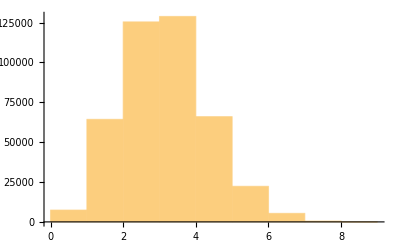

```mathematica
ldif[l_]:=Max[l]-Min[l]
Monitor[Flatten[Table[ldif[{
coprime[gs[[i]],j],
coprime[gs[[i+1]],j],
coprime[gs[[i+2]],j],
coprime[gs[[i+3]],j]}],{i,1,Length[gs]},{j,gs[[i+4]],72+gs[[i+4]]}]],{i,j}]//Histogram
```

```mathematica
First[Timing[Table[Prime[i],{i,1,1000000}]]]
```

2.74727

```mathematica
Monitor[Max[Table[coprime[3905707004975257109,RandomInteger[{1,100000}]],{i,1,100000}]],i]
```

20

```mathematica
Monitor[Mean[Table[coprime[3905707004975257109,RandomInteger[{1,100000}]],{i,1,100000}]],i]
```

```mathematica
tcoprime[n_]:=Monitor[Block[{bests={{0,0,0}}},
Do[Block[{this=coprime[i,j], best=bests[[1,1]]},
Piecewise[{{bests=Prepend[bests,{this,i,j}];best=this, this≥best}, {0, True}}]],{i,1,n-1},{j,i+1,n}];bests],{i,j}]
```

```mathematica
Reverse[tcoprime[1000]]
```

{{0,0,0},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{1,1,17},{1,1,18},{1,1,19},{1,1,20},{1,1,21},{1,1,22},{1,1,23},{1,1,24},{1,1,25},{1,1,26},{1,1,27},{1,1,28},{1,1,29},{1,1,30},3783,{12,335,877},{12,335,882},{12,337,545},{12,337,546},{12,337,882},{12,337,883},{12,338,545},{12,338,547},{12,338,883},{12,338,885},{12,343,542},{12,343,555},{12,343,885},{12,343,898},{12,377,521},{13,377,610},{13,377,987},{13,521,843},{13,521,898},{13,542,877},{13,542,885},{13,545,882},{13,545,883},{13,546,883},{13,547,882},{13,547,885},{13,555,877},{13,555,898},{13,610,843},{14,610,987}}
 |  |  |  |

```mathematica
DeleteDuplicates[Map[First,Out[274]]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14}

```mathematica
Table[First[Out[274][[First[Position[Map[First,Out[274]],i]]]]],{i,2,14}]
```

{{2,2,3},{3,3,5},{4,5,8},{5,8,13},{6,13,21},{7,21,34},{8,34,55},{9,55,89},{10,89,144},{11,144,233},{12,233,377},{13,377,610},{14,610,987}}

```mathematica
926783/100000//N
```

9.26783

```mathematica
5,8
3,5
2,3
1,2
```

```mathematica
ttr[n_]:={Prime[n+1]-Prime[n],Sum[Boole[CoprimeQ[Mod[Primoral[n],2^64],i]],{i,Prime[n]+1,Prime[n+1]}]-1}
goodForm[l_]:=If[Length[l]>1,
If[l[[1]]==0,goodForm[Drop[l,1]],False],
l[[1]]==1]
Monitor[ParallelSum[ttr[n],{n,6,100000}],{n,i}]
```

$Aborted

```mathematica
32271/104730//N
```

0.308135

```mathematica
Prime[100000]
```

```mathematica
PrimePi[2000000000]
```

98222287

```mathematica
FactorInteger[Mod[Primoral[16],2^64]]
```

{{2,1},{20562719,1},{343884833603,1}}

```mathematica
Mod[1234,13]
```

```mathematica
Mod[12,7]
```

5

```mathematica
coprime[40037,12367854]
```

10

```mathematica
Prime[4207]
```

40037

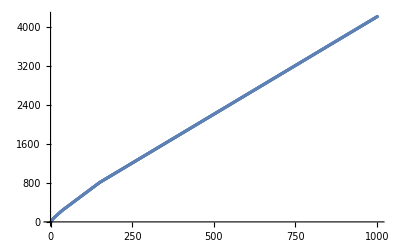

```mathematica
ListPlot[%]
```

```mathematica
Log2[2^3+1]//N
```

3.16993

```mathematica
Table[Prime[i],{i,1,100}]
```

```mathematica
Reverse[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}]
```

```mathematica
StringJoin[Map[StringJoin[" * (x % ",ToString[#],") "]&,{541,523,521,509,503,499,491,487,479,467,463,461,457,449,443,439,433,431,421,419,409,401,397,389,383,379,373,367,359,353,349,347,337,331,317,313,311,307,293,283,281,277,271,269,263,257,251,241,239,233,229,227,223,211,199,197,193,191,181,179,173,167,163,157,151,149,139,137,131,127,113,109,107,103,101,97,89,83,79,73,71,67,61,59,53,47,43,41,37,31,29,23,19,17,13,11,7,5,3,2}]]
```

* (x % 541)  * (x % 523)  * (x % 521)  * (x % 509)  * (x % 503)  * (x % 499)  * (x % 491)  * (x % 487)  * (x % 479)  * (x % 467)  * (x % 463)  * (x % 461)  * (x % 457)  * (x % 449)  * (x % 443)  * (x % 439)  * (x % 433)  * (x % 431)  * (x % 421)  * (x % 419)  * (x % 409)  * (x % 401)  * (x % 397)  * (x % 389)  * (x % 383)  * (x % 379)  * (x % 373)  * (x % 367)  * (x % 359)  * (x % 353)  * (x % 349)  * (x % 347)  * (x % 337)  * (x % 331)  * (x % 317)  * (x % 313)  * (x % 311)  * (x % 307)  * (x % 293)  * (x % 283)  * (x % 281)  * (x % 277)  * (x % 271)  * (x % 269)  * (x % 263)  * (x % 257)  * (x % 251)  * (x % 241)  * (x % 239)  * (x % 233)  * (x % 229)  * (x % 227)  * (x % 223)  * (x % 211)  * (x % 199)  * (x % 197)  * (x % 193)  * (x % 191)  * (x % 181)  * (x % 179)  * (x % 173)  * (x % 167)  * (x % 163)  * (x % 157)  * (x % 151)  * (x % 149)  * (x % 139)  * (x % 137)  * (x % 131)  * (x % 127)  * (x % 113)  * (x % 109)  * (x % 107)  * (x % 103)  * (x % 101)  * (x % 97)  * (x % 89)  * (x % 83)  * (x % 79)  * (x % 73)  * (x % 71)  * (x % 67)  * (x % 61)  * (x % 59)  * (x % 53)  * (x % 47)  * (x % 43)  * (x % 41)  * (x % 37)  * (x % 31)  * (x % 29)  * (x % 23)  * (x % 19)  * (x % 17)  * (x % 13)  * (x % 11)  * (x % 7)  * (x % 5)  * (x % 3)  * (x % 2)

```mathematica
gcd[Fibonacci[45],Fibonacci[46]]
```

45

```mathematica
gcd[Fibonacci[46],Fibonacci[45]]
```

44

```mathematica
Table[gcd[Fibonacci[n+2],Fibonacci[n+1]],{n,1,5}]
```

```mathematica
Table[gcd[Fibonacci[n+2],Fibonacci[n+1]],{n,1,5}]
```

{1,2,3,4,5}

```mathematica
Monitor[mx[gcd[30030,#]&,1,2000000000],i]
```

$Aborted

```mathematica
Monitor[mx[gcd[#,30030]&,1,2000000000],i]
```

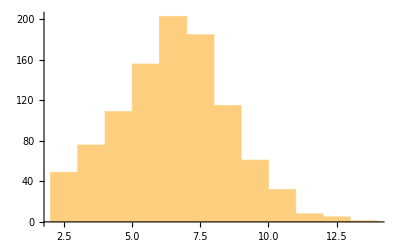

```mathematica
Histogram[Table[gcd[i,30030],{i,1,2000000000}]]
```

```mathematica
Table[GCD[a,b]==gcd[a,b],{a,1,10},{b,1,10}]
```

{{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True}}

```mathematica
5760/4
```

1440

```mathematica
IntegerDigits[30030,2]
```

{1,1,1,0,1,0,1,0,1,0,0,1,1,1,0}

```mathematica
5760/30030//N
```

0.191808

```mathematica
123,17
```

```mathematica
Mod[123,17]
```

4

```mathematica
Mod[17,4]
```

1

```mathematica
Mod[24,12]
```

0

```mathematica
Limit[(n PrimePi[x^n])/(x^(n-1) PrimePi[x]),x->∞]==1
```

```mathematica
IntegerDigits[FromDigits[IntegerDigits[ToExpression[StringJoin["010000000","100000000","000100000","001000000","000001000","000010000","000000010","000000100","113333001"]]],4],10000]
IntegerDigits[FromDigits[IntegerDigits[ToExpression[StringJoin["001000000","322000000","232000000","000010000","222110000","000000100","111001100","000000001","222000011"]]],4],10000]
```

{3653,8098,4519,3576,7427,6255,5242,2584,9064,7068,4580,2433}

{913,6406,2444,6620,8888,8789,5417,8025,8002,2526,7952,261}

```mathematica
|o(a)=2,o(b)=3,o(ab)=19,o(ababab2)=17
```

```mathematica
00,111,
```

```mathematica
IntegerDigits[FromDigits[IntegerDigits[ToExpression[StringJoin[ConstantArray["0101011",17]]]],2],10000]
```

{2250,2678,6687,9975,6903,4896,4708,3486,1483}

```mathematica
IntegerDigits[FromDigits[IntegerDigits[ToExpression[StringJoin[ConstantArray["01",19]]]],2],10000]
```

{916,2596,8981}

```mathematica
CayleyGraph[MathieuGroupM11[]]
```

```mathematica
m11=Out[540];
```

```mathematica
VertexConnectivity[m11]
```

2

```mathematica
EulerianGraphQ[m11]
```

True

```mathematica
PlanarGraphQ[m11]
```

False

```mathematica
PlanarGraphQ[RandomSample[EdgeList[m11],10]]
```

False

```mathematica
FindCycle[m11,∞,1]
```

{{1->592,592->1}}

```mathematica
partition[{g_,cys_}]:=Block[{cy=First[FindCycle[g,∞,1]]},{Graph[Complement[EdgeList[g],Map[If[#[[1]]<#[[2]],#,#[[2]]<->#[[1]]]&,cy]]],Append[cys,cy]}]
```

```mathematica
{EdgeCount[#[[1]]],#[[2]]}&[partition[{m11,{}}]]
```

{15839,{{1->592,592->1}}}

```mathematica
FullPartition[g_]:=Last[NestWhile[partition,{g,{}},EdgeCount[First[#]]>0&]]
```

```mathematica
Complement[EdgeList[CompleteGraph[5]],{1<->5,5<->4,4<->1}]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
Complement[EdgeList[CompleteGraph[5]],Map[If[#[[1]]<#[[2]],#,#[[2]]<->#[[1]]]&,{1<->5,5<->4,4<->1}]]
```

{1<->2,1<->3,2<->3,2<->4,2<->5,3<->4,3<->5}

```mathematica
EdgeList[CompleteGraph[5]]
```

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
m11cys=FullPartition[m11];
```

First::nofirst: {} has a length of zero and no first element.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Complement::heads: Heads Less and List at positions 2 and 1 are expected to be the same.

EdgeCount::graph: A graph object is expected at position 1 in EdgeCount[Graph[Complement[{36 -> 5597, 38 -> 5598, 39 -> 5599, 42 -> 5561, 52 -> 5589, 66 -> 5609, 77 -> 5307, 78 -> 5309, 80 -> 5312, 90 -> 5265, 100 -> 99, 102 -> 101, 103 -> 97, 104 -> 98, 105 -> 95, 106 -> 96, 106 -> 5297, 107 -> 92, 107 -> 5298, 108 -> 91, 109 -> 94, 110 -> 93, 110 -> 5301, 111 -> 89, 112 -> 90, 121 -> 119, 121 -> 5294, 122 -> 120, 123 -> 117, 124 -> 116, 125 -> 115, 126 -> 118, 127 -> 113, 128 -> 114, 128 -> 5296, 129 -> 79, 130 -> 80, 131 -> 76, 132 -> 75, 133 -> 74, 134 -> 78, 135 -> 77, 136 -> 73, 137 -> 87, 138 -> 88, 139 -> 84, 140 -> 83, 141 -> 82, 142 -> 86, 143 -> 85, « 9209 »}, {} ⟦ 1 ⟧ < {} ⟦ 2 ⟧]]].

```mathematica
Length[m11cys]
```

2545

```mathematica
Map[Length,m11cys]
```

{2,4462,2,2538,2,1617,2,4,2,2,513,2,4,2,2,2,2,2,2,2,2,2,4,591,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,4,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,4,2,2,4,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,4,2,2,2,4,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,2,4,2,4,4,4,2,2,2,4,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,4,2,4,2,2,2,2,2,2,4,2,2,2,4,4,2,4,2,2,2,2,4,2,2,2,4,4,2,2,2,4,4,2,4,4,2,4,4,4,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,4,2,2,2,2,2,2,2,2,2,2,4,4,4,4,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,4,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,2,4,2,4,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,4,4,2,2,2,4,2,2,4,2,4,2,4,2,4,2,4,4,2,2,4,4,2,2,2,2,2,2,4,2,4,2,2,2,2,2,2,4,2,2,2,4,4,2,2,2,4,4,2,2,2,2,4,2,2,2,2,2,4,2,2,2,2,4,4,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,4,4,4,4,2,2,2,2,4,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,1}

```mathematica
Total[Out[602]]
```

15368

```mathematica
Map[Map[First,#]&,Select[m11cys,#≠{}&]]
```

{{1,592},2542,{7898,7904,7902,7901}}
 |  |  |  |

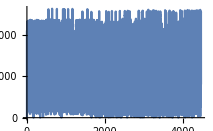
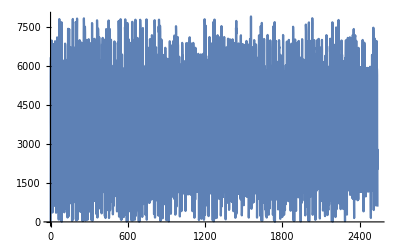
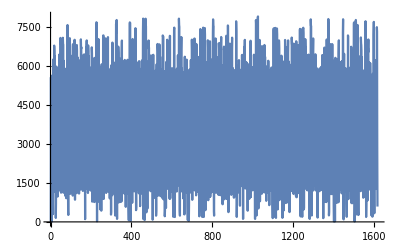
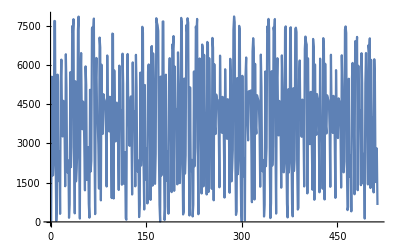
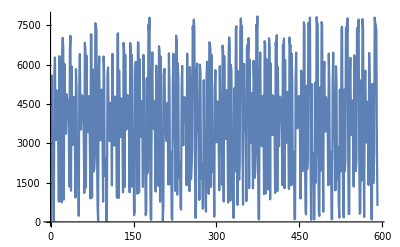

```mathematica
Map[ListPlot[#,Joined->True]&,Select[Out[606],Length[#]>4&]]
```

```mathematica
m11cys
```

{{1<->5,5<->4,4<->1},{1<->2,2<->3,3<->1},{2<->4,4<->3,3<->5,5<->2}}

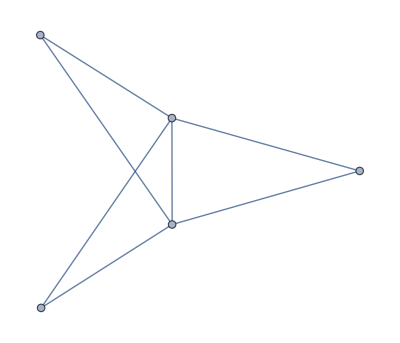
{-Graphics-,{{1<->5,5<->4,4<->1}}}

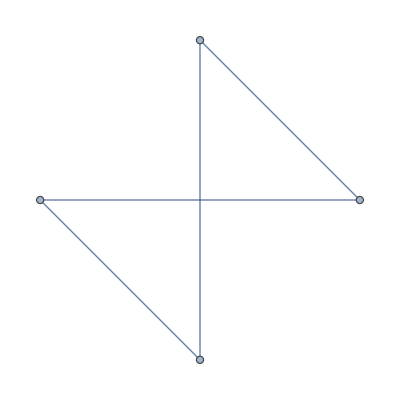
{-Graphics-,{{1<->5,5<->4,4<->1},{1<->2,2<->3,3<->1}}}

{-Graphics-,{{1<->5,5<->4,4<->1},{1<->2,2<->3,3<->1},{2<->4,4<->3,3<->5,5<->2}}}

```mathematica
partition[{CompleteGraph[5],{}}]
partition[%]
partition[%]
```

```mathematica
Last[NestWhile[partition,{CompleteGraph[5],{}},EdgeCount[First[#]]>0&]]
```

{{1<->5,5<->4,4<->1},{1<->2,2<->3,3<->1},{2<->4,4<->3,3<->5,5<->2}}

```mathematica
FullPartition[CompleteGraph[5]]
```

{{1<->5,5<->4,4<->1},{1<->2,2<->3,3<->1},{2<->4,4<->3,3<->5,5<->2}}

```mathematica
EulerianGraphQ[CompleteGraph[5]]
```

True

```mathematica
Map[Length,FindCycle[m11,∞,10]]
```

$Aborted

```mathematica
Tally[VertexDegree[m11]]
```

{{4,7920}}

```mathematica
15840(15840-1)/2
```

125444880

```mathematica
EdgeCount[m11]
```

15840

```mathematica
VertexCount[m11]
```

7920

```mathematica
15840^3/(29 7920^2)//N
```

2184.83

```mathematica
⟨a,b|a^2=b^3=(ab)^19=[a,b]^9=((ab)^6(ab^2)^5)^2=((ababab^2)^2 abab^2 ab^2 abab^2)^2=abab(abab^2)^3 abab(abab^2)^4 ab^2(abab^2)^3=(ababababab^2 abab^2)^4=1⟩
```

```mathematica
[a,b]^9==(a^-1 b^-1 ab)^9==(abbab)^9
```

```mathematica
{"aa",
"bbb",
rep["ab",19],
rep["abbab",9],
rep[StringJoin[rep["ab",6],rep["abb",5]],2],
rep[StringJoin[rep["abababb",2],"ababbabbababb"],2],
StringJoin["abab",rep["ababb",3],"abab",rep["ababb",4],"abb",rep["ababb",3]],
rep["abababababbababb",4]}//tonum//Column
```

0004 | 
0026 | 
0084 | 4282 | 3235 | 4562 | 0055 | 
0019 | 2884 | 8791 | 8802 | 9638 | 1758 | 
0036 | 3435 | 8878 | 3216 | 8115 | 1599 | 0676 | 
0036 | 3635 | 3639 | 4837 | 4955 | 0694 | 7844 | 
0007 | 9488 | 2876 | 0112 | 6499 | 1849 | 6601 | 0179 | 
0214 | 6066 | 9849 | 4224 | 2473 | 2828 | 9811 | 2892 |

```mathematica
spad[s_]:=StringJoin[If[StringLength[s]>0,StringJoin[ConstantArray["0",4-StringLength[s]]],""],s," | "]
tonum[s_]:=Map[StringJoin[Map[spad[ToString[#]]&,IntegerDigits[#,10000]]]&,Map[FromDigits[#,3]&,Map[Piecewise[{{1, #=="a"}, {2, #=="b"}, {ErrorBox["error"], True}}]&,Characters[s],{2}]]]
rep[s_,n_]:=StringJoin[ConstantArray[s,n]]
```

```mathematica
The Coxeter group (generated by involutions a,b1,b2,b3,c1,c2,c3,d1,d2,d3,e1 and e2) such that:
e1-- d1-- c1-- b1-- a-- b2-- c2-- d2-- e2
					|b3
					|c3
					|d3
along with (a b1 c1 a b2 c2 a b3 c3)^10=1 (the Spider relation).
```

```mathematica
a,b1,b2,b3,c1,c2,c3,d1,d2,d3,e1 and e2
1,2,   3,  4,   5,  6,   7,  8,  9,  10,11,    12
```

```mathematica
spider={Flatten[ConstantArray[{1,2,5,1,3,6,1,4,7},10]]}
```

{{1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7,1,2,5,1,3,6,1,4,7}}

```mathematica
twos=Map[{#[[1]],#[[2]],#[[1]],#[[2]]}&,Complement[EdgeList[CompleteGraph[12]],Map[If[#[[1]]<#[[2]],#,#[[2]]<->#[[1]]]&,EdgeList[mg]]]](*(xy)^2==1*)
```

{{1,5,1,5},{1,6,1,6},{1,7,1,7},{1,8,1,8},{1,9,1,9},{1,10,1,10},{1,11,1,11},{1,12,1,12},{2,3,2,3},{2,4,2,4},{2,6,2,6},{2,7,2,7},{2,8,2,8},{2,9,2,9},{2,10,2,10},{2,11,2,11},{2,12,2,12},{3,4,3,4},{3,5,3,5},{3,7,3,7},{3,8,3,8},{3,9,3,9},{3,10,3,10},{3,11,3,11},{3,12,3,12},{4,5,4,5},{4,6,4,6},{4,8,4,8},{4,9,4,9},{4,10,4,10},{4,11,4,11},{4,12,4,12},{5,6,5,6},{5,7,5,7},{5,9,5,9},{5,10,5,10},{5,11,5,11},{5,12,5,12},{6,7,6,7},{6,8,6,8},{6,10,6,10},{6,11,6,11},{6,12,6,12},{7,8,7,8},{7,9,7,9},{7,11,7,11},{7,12,7,12},{8,9,8,9},{8,10,8,10},{8,12,8,12},{9,10,9,10},{9,11,9,11},{10,11,10,11},{10,12,10,12},{11,12,11,12}}

```mathematica
threes=Map[{#[[1]],#[[2]],#[[1]],#[[2]],#[[1]],#[[2]]}&,EdgeList[mg]](*(xy)^3==1*)
```

{{11,8,11,8,11,8},{8,5,8,5,8,5},{5,2,5,2,5,2},{2,1,2,1,2,1},{1,3,1,3,1,3},{3,6,3,6,3,6},{6,9,6,9,6,9},{9,12,9,12,9,12},{1,4,1,4,1,4},{4,7,4,7,4,7},{7,10,7,10,7,10}}

```mathematica
ones=Map[{#,#}&,VertexList[mg]](*#^2==1*)
```

{{11,11},{8,8},{5,5},{2,2},{1,1},{3,3},{6,6},{9,9},{12,12},{4,4},{7,7},{10,10}}

```mathematica
Flatten[Map[IntegerDigits[#,10000]&,Sort[Map[FromDigits[#,13]&,Flatten[{ones,twos,threes,spider},1]]]],1]//Length
```

142

```mathematica
Map[StringJoin[Map[spad[ToString[#]]&,IntegerDigits[#,10000]]]&,Sort[Map[FromDigits[#,13]&,Flatten[{ones,twos,threes,spider},1]]]]//Column
```

```mathematica
{{"0014 | "}, {"0028 | "}, {"0042 | "}, {"0056 | "}, {"0070 | "}, {"0084 | "}, {"0098 | "}, {"0112 | "}, {"0126 | "}, {"0140 | "}, {"0154 | "}, {"0168 | "}, {"3060 | "}, {"3230 | "}, {"3400 | "}, {"3570 | "}, {"3740 | "}, {"3910 | "}, {"4080 | "}, {"4250 | "}, {"4930 | "}, {"5100 | "}, {"5440 | "}, {"5610 | "}, {"5780 | "}, {"5950 | "}, {"6120 | "}, {"6290 | "}, {"6460 | "}, {"7310 | "}, {"7480 | "}, {"7820 | "}, {"7990 | "}, {"8160 | "}, {"8330 | "}, {"8500 | "}, {"8670 | "}, {"9690 | "}, {"9860 | "}, {"0001 | 0200 | "}, {"0001 | 0370 | "}, {"0001 | 0540 | "}, {"0001 | 0710 | "}, {"0001 | 0880 | "}, {"0001 | 2070 | "}, {"0001 | 2240 | "}, {"0001 | 2580 | "}, {"0001 | 2750 | "}, {"0001 | 2920 | "}, {"0001 | 3090 | "}, {"0001 | 4450 | "}, {"0001 | 4620 | "}, {"0001 | 4960 | "}, {"0001 | 5130 | "}, {"0001 | 5300 | "}, {"0001 | 6830 | "}, {"0001 | 7000 | "}, {"0001 | 7340 | "}, {"0001 | 7510 | "}, {"0001 | 9210 | "}, {"0001 | 9380 | "}, {"0001 | 9720 | "}, {"0002 | 1590 | "}, {"0002 | 1760 | "}, {"0002 | 3970 | "}, {"0002 | 4140 | "}, {"0002 | 6350 | "}, {"0045 | 9696 | "}, {"0048 | 8427 | "}, {"0077 | 5737 | "}, {"0129 | 2895 | "}, {"0169 | 5129 | "}, {"0192 | 4977 | "}, {"0249 | 9597 | "}, {"0290 | 1831 | "}, {"0313 | 1679 | "}, {"0370 | 6299 | "}, {"0433 | 8381 | "}, {"1637 | 9974 | 1069 | 4429 | 8031 | 4859 | 6166 | 3583 | 7859 | 8557 | 2625 | 3785 | 7317 | 4210 | 2634 | 8732 | 0826 | 5645 | 1689 | 8349 | 5362 | 0140 | 2912 | 3766 | 3324 | "}}
```

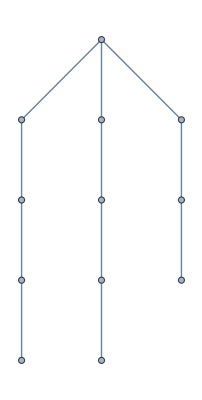

```mathematica
mg=Graph[{11<->8,
8<->5,
5<->2,
2<->1,
1<->3,
3<->6,
6<->9,
9<->12,
1<->4,
4<->7,
7<->10}]
```

```mathematica
Log[2^(196560^2)]/Log[10000]//N
```

2.90764×10^9

```mathematica
(Log2[10000]70000)//N
```

930140.

```mathematica
(4370^2*Log10[2])/(Log10[10000]700)//N
```

2053.12

```mathematica
(4370^2*Log10[2])/(4*700)//N
```

2053.12

```mathematica
IntegerDigits[FromDigits[Flatten[ToExpression[StringReplace["[[1,1,1,1,0,1,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0,1,1,0],[1,1,0,1,1,0,0,1,0,0,1,1,0,1,1,1,0,0,0,0,0,1,1,1],[0,0,0,1,0,1,1,0,0,0,0,1,0,0,0,0,0,0,1,0,1,1,0,1],[1,1,1,1,1,0,0,1,0,1,1,0,0,1,0,0,1,0,0,0,0,1,1,0],[1,1,0,0,0,0,1,0,0,0,1,0,0,1,0,1,1,1,0,0,1,1,1,0],[1,0,0,1,0,0,1,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,1],[0,0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,1,0,0,1,1,1,1,1],[0,0,0,1,1,0,0,1,1,0,0,1,1,1,0,1,1,1,0,1,0,1,1,1],[0,0,0,0,1,1,1,0,0,1,1,0,1,1,0,1,1,1,1,1,0,1,1,0],[0,0,1,0,1,1,1,1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0],[0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,1,0,1,0,0,1],[1,1,0,1,1,0,0,0,0,1,0,1,0,0,1,1,1,1,0,0,1,0,0,0],[0,0,1,0,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,1,1,0],[1,0,1,0,1,1,0,1,1,0,0,0,1,1,0,0,0,1,0,1,0,1,0,0],[0,1,0,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,0,1,1,1,0,1],[1,1,0,1,1,1,1,0,0,0,0,1,0,0,1,1,0,1,0,0,0,0,1,0],[1,0,1,1,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,0,0,0,1,1],[1,1,1,1,0,0,0,0,0,1,1,0,0,1,1,1,0,1,0,0,1,0,1,0],[1,1,0,1,0,0,1,1,1,0,1,0,0,0,0,0,1,0,0,0,0,1,1,1],[1,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1,1,1,1,1],[0,1,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0],[0,1,1,1,0,0,1,0,0,1,0,0,0,0,1,1,1,0,0,1,0,1,0,0],[1,0,0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,1,0,0,0],[1,0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,0,1,1]]",{"["->"{","]"->"}"}]]],2],10000]
```

{23,6161,4606,3765,709,4300,567,5404,4869,8284,5179,6587,1655,3476,3693,4226,3939,7024,4205,9751,2419,4431,9147,116,6245,9211,9535,7216,8010,8260,988,1801,8244,3938,6070,8919,563,8849,2705,6525,3905,1909,8331,3955}

```mathematica
Length[%]
```

44

```mathematica
19 6560
```

```mathematica
Prime[4648]
```

44711

```mathematica
PrimePi[39317]
```

4139

```mathematica
PrimePi[44711]
```

4648

```mathematica
FactorInteger[39229]
```

{{39229,1}}

```mathematica
FactorInteger[39199]
```

{{39199,1}}

```mathematica
FactorInteger[7949]
```

{{7949,1}}

```mathematica
PrimePi[41057]
```

4298

```mathematica
p[n_]:={PrimeQ[n],PrimePi[n]}
```

```mathematica
p[41183]
```

{True,4310}

```mathematica
Log2[5272913654073762587]//N
```

62.1933

```mathematica
p[521329]
```

{True,43161}

```mathematica
p[41201]
```

{True,4312}

```mathematica
p[52127]
```

{True,5330}

```mathematica
p[30029]
```

{True,3248}

```mathematica
FactorInteger[289]
```

{{17,2}}

```mathematica
StringReplace["not p:13231,pi:1568
not p:12877,pi:1527
not p:12403,pi:1476
not p:10823,pi:1316
not p:10349,pi:1271
not p:10201,pi:1252
not p:10033,pi:1230
not p:7979,pi:1009
not p:6241,pi:817
not p:4661,pi:640
not p:4489,pi:619
not p:4087,pi:573
not p:3953,pi:558
not p:3721,pi:528
not p:3599,pi:512
not p:3551,pi:506
not p:3481,pi:495
not p:3239,pi:466
not p:3233,pi:465
not p:3127,pi:453
not p:2809,pi:417
not p:2747,pi:407
not p:2501,pi:373
not p:2449,pi:369
not p:2419,pi:364
not p:2173,pi:334
not p:2077,pi:319
not p:1891,pi:296
not p:1829,pi:286
not p:1681,pi:267
not p:1643,pi:262
not p:1333,pi:219
not p:1271,pi:206
not p:961,pi:164
not p:527,pi:100
not p:361,pi:72
not p:323,pi:65
not p:289,pi:59
",{"not p:"->"{","pi:"->"","\n"->"},"}]
```

```mathematica
Map[FactorInteger,Map[First,{{13231,1568},{12877,1527},{12403,1476},{10823,1316},{10349,1271},{10201,1252},{10033,1230},{7979,1009},{6241,817},{4661,640},{4489,619},{4087,573},{3953,558},{3721,528},{3599,512},{3551,506},{3481,495},{3239,466},{3233,465},{3127,453},{2809,417},{2747,407},{2501,373},{2449,369},{2419,364},{2173,334},{2077,319},{1891,296},{1829,286},{1681,267},{1643,262},{1333,219},{1271,206},{961,164},{527,100},{361,72},{323,65},{289,59}}]]//Column
```

{{101,1},{131,1}}
{{79,1},{163,1}}
{{79,1},{157,1}}
{{79,1},{137,1}}
{{79,1},{131,1}}
{{101,2}}
{{79,1},{127,1}}
{{79,1},{101,1}}
{{79,2}}
{{59,1},{79,1}}
{{67,2}}
{{61,1},{67,1}}
{{59,1},{67,1}}
{{61,2}}
{{59,1},{61,1}}
{{53,1},{67,1}}
{{59,2}}
{{41,1},{79,1}}
{{53,1},{61,1}}
{{53,1},{59,1}}
{{53,2}}
{{41,1},{67,1}}
{{41,1},{61,1}}
{{31,1},{79,1}}
{{41,1},{59,1}}
{{41,1},{53,1}}
{{31,1},{67,1}}
{{31,1},{61,1}}
{{31,1},{59,1}}
{{41,2}}
{{31,1},{53,1}}
{{31,1},{43,1}}
{{31,1},{41,1}}
{{31,2}}
{{17,1},{31,1}}
{{19,2}}
{{17,1},{19,1}}
{{17,2}}

```mathematica
d[b_,d_]:=N[2Log[b^(d^2)]/Log[10000]]
```

```mathematica
d[2,80]
```

963.296

```mathematica
Map[StringJoin[Map[spad[ToString[#]]&,IntegerDigits[#,10000]]]&,Map[FromDigits[#,4]&,Map[Map[Piecewise[{{1, #=="x"}, {2, #=="y"}, {3, #=="t"}}]&,#]&,Map[Characters,{"xx",
"yyy",
"xyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxyxy",
"xyyxyxyyxyxyyxyxyyxyxyyxyxyyxyxyyxyxyyxyxyyxyxyyxyxyyxyxyyxy",
"xyyxyyxyxyxyyxyyxyxyxyyxyyxyxyxyyxyyxyxyxyyxyyxyxy",
"xyxyxyyxyxyxyyxyxyxyyxyxyyxyyxyxyyxyyxyxyyxyy",
"xyxyxyyxyxyyxyxyyxyxyxyyxyxyyxyxyyxyxyxyyxyxyyxyxyyxyxyxyyxyxyyxyxyy",
"tt",
"txtx",
"tyyxyyxyyxyyyyxyyyyxyyxyytyxyxyyxyyxyxyxy",
"yxyyyyxyyxyyyyxyytyxyyxyxyyxyxyyyyxyyxyyyyxyytyxyyxyxyyxyxyyyyxyyxyyyyxyytyxyyxyxyyx",
"yxyxyxyyxyxyxyyxyxyxytyyyyxyyxyyxyyxyyxyyxyyyyxyyxyyxtxyxyxyyxyxyxyxyxyxyyyxyxyxyyxyxyxyyxyxyxytyyyyxyyxyyxyyxyyxyyxyyyyxyyxyyxtxyxyxyyxyxyxyxyxyxyy"}]]]//Sort]//Column
```

0005 | 
0015 | 
0042 | 
0221 | 
0004 | 4135 | 3877 | 5222 | 8985 | 5520 | 1126 | 
0495 | 2364 | 6569 | 4707 | 0594 | 8337 | 1162 | 
1980 | 7040 | 6285 | 6608 | 4398 | 3859 | 8758 | 
0052 | 3153 | 4759 | 4970 | 7410 | 2114 | 6445 | 2710 | 
5483 | 2279 | 0050 | 0825 | 9859 | 7660 | 3904 | 5777 | 6550 | 
0003 | 4849 | 1720 | 6018 | 4826 | 9680 | 6444 | 2641 | 5230 | 7377 | 1930 | 
0226 | 0223 | 9345 | 5489 | 2832 | 0808 | 9780 | 0843 | 6192 | 2036 | 9191 | 2446 | 9353 | 
0007 | 6390 | 4033 | 4252 | 8837 | 6201 | 5700 | 4484 | 5098 | 6729 | 9615 | 4604 | 5795 | 1510 | 7798 | 5680 | 3472 | 4058 | 6055 | 0172 | 0749 | 1314 | 3194 |

```mathematica
5013 9758 5920
0217 9989 5040
0102 3934 4640
0006 6060 2880
0001 4183 1360
0088 7040
0031 9440
0016 3680
0001 2144
6048
0812
0602
0444
```

```mathematica
89
```

```mathematica
8677 5571 0460 7756 2880
```

```mathematica
FactorInteger[98]
```

{{2,1},{7,2}}

```mathematica
FactorInteger[27+89]
```

{{2,2},{29,1}}

```mathematica
89+5
```

94

```mathematica
[g,h]==g^-1*h^-1*g*h
g^h==h^-1*g*h
```

```mathematica
(ab)^-1==b^-1 a^-1
(abc)^-1==c^-1 b^-1 a^-1
```